## QCD

### α

```mathematica
(* beta function coefficients and 4-loop Lambda_QCD taken from arxiv/0908.1135 *)
```

```mathematica
β0N=(33-2Nf)/(12π);
β1N=(153-19Nf)/(24π^2);
β2N=(77139-15099Nf+325Nf^2)/(3456π^3);
β3N=(29243-6946.3Nf+405.089Nf^2+1.49931Nf^3)/(256π^4);
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{.338,f==3},{.296,f==4},{.213,f==5},{.090,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
Mαs[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[1,3],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,3],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,4],Mc≤Q<Mb},{αsNf[Q,5],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,6],Q≥Mt}}]
αs[2]
```

0.293951

```mathematica
αsNf[Mt,5]
```

0.107828

```mathematica
αsNf[Mt,6]
```

0.10787

```mathematica
αs[Mt]
```

0.107925

```mathematica
αsNf[Mb,5]
```

0.217151

```mathematica
αsNf[Mb,4]
```

0.215429

```mathematica
αsNf[Mc,4]
```

0.335937

```mathematica
αsNf[Mc,3]
```

0.322415

```mathematica
MZ=91.1876;
```

```mathematica
αs[MZ]
```

0.118288

```mathematica
(*LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]*)
LQs[Q_,f_]:=Log[Q^2/Λ^2]
αsNf4Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQs[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQs[Q,f]^4)(β1N^3/β0N^3(-Log[LQs[Q,f]]^3+(5/2)Log[LQs[Q,f]]^2+2Log[LQs[Q,f]]-1/2))-1/(β0N^4 LQs[Q,f]^4)(3β1N β2N Log[LQs[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQs[Q,f]))/.Nf->f
Mαs3Loop[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3
Mαs2Loop[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2
αs4Loop[Q_]:=Piecewise[{{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,3],Q<1},{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,3],1≤Q<Mc},{Mαs3Loop[Mb,5]αsNf4Loop[Q,4],Mc≤Q<Mb},{αsNf4Loop[Q,5],Mb≤Q<Mt},{(1/Mαs3Loop[Mt,6])αsNf4Loop[Q,6],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,4],Mc≤Q<Mb},{αsNf3Loop[Q,5],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,6],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,3],Q<1},{αsNf2Loop[Q,3],1≤Q<Mc},{αsNf2Loop[Q,4],Mc≤Q<Mb},{αsNf2Loop[Q,5],Mb≤Q<Mt},{αsNf2Loop[Q,6],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,3],Q<1},{αsNf1Loop[Q,3],1≤Q<Mc},{αsNf1Loop[Q,4],Mc≤Q<Mb},{αsNf1Loop[Q,5],Mb≤Q<Mt},{αsNf1Loop[Q,6],Q≥Mt}}]
```

```mathematica
Λ4LoopNf5=Λ/.FindRoot[αsNf4Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.213

```mathematica
Λ4LoopNf6=Λ/.FindRoot[αsNf4Loop[Mt,6]-(αsNf4Loop[Mt,5]/.{Λ->Λ4LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0897171

```mathematica
Λ4LoopNf4=Λ/.FindRoot[αsNf4Loop[Mb,4]-(αsNf4Loop[Mb,5]/.{Λ->Λ4LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.303565

```mathematica
Λ4LoopNf3=Λ/.FindRoot[αsNf4Loop[Mc,3]-(αsNf4Loop[Mc,4]/.{Λ->Λ4LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.378129

```mathematica
Λ3LoopNf5=Λ/.FindRoot[αsNf3Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.217435

```mathematica
Λ3LoopNf6=Λ/.FindRoot[αsNf3Loop[Mt,6]-(αsNf3Loop[Mt,5]/.{Λ->Λ3LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0910249

```mathematica
Λ3LoopNf4=Λ/.FindRoot[αsNf3Loop[Mb,4]-(αsNf3Loop[Mb,5]/.{Λ->Λ3LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.299152

```mathematica
Λ3LoopNf3=Λ/.FindRoot[αsNf3Loop[Mc,3]-(αsNf3Loop[Mc,4]/.{Λ->Λ3LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.335423

```mathematica
Λ2LoopNf5=Λ/.FindRoot[αsNf2Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.229911

```mathematica
Λ2LoopNf6=Λ/.FindRoot[αsNf2Loop[Mt,6]-(αsNf2Loop[Mt,5]/.{Λ->Λ2LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0931592

```mathematica
Λ2LoopNf4=Λ/.FindRoot[αsNf2Loop[Mb,4]-(αsNf2Loop[Mb,5]/.{Λ->Λ2LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.332194

```mathematica
Λ2LoopNf3=Λ/.FindRoot[αsNf2Loop[Mc,3]-(αsNf2Loop[Mc,4]/.{Λ->Λ2LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.386001

```mathematica
Λ1LoopNf5=Λ/.FindRoot[αsNf1Loop[MZ,5]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.0893248

```mathematica
Λ1LoopNf6=Λ/.FindRoot[αsNf1Loop[Mt,6]-(αsNf1Loop[Mt,5]/.{Λ->Λ1LoopNf5}),{Λ,ΛQCD[6]}][[1]]
```

0.0434346

```mathematica
Λ1LoopNf4=Λ/.FindRoot[αsNf1Loop[Mb,4]-(αsNf1Loop[Mb,5]/.{Λ->Λ1LoopNf5}),{Λ,ΛQCD[4]}][[1]]
```

0.122648

```mathematica
Λ1LoopNf3=Λ/.FindRoot[αsNf1Loop[Mc,3]-(αsNf1Loop[Mc,4]/.{Λ->Λ1LoopNf4}),{Λ,ΛQCD[3]}][[1]]
```

0.147643

```mathematica
αsNf1Loop[Mb,5]/.{Λ->Λ1LoopNf5}
```

0.206797

```mathematica
αsNf1Loop[Mb,4]/.{Λ->Λ1LoopNf4}
```

0.206797

```mathematica
αsNf1Loop[Mc,4]/.{Λ->Λ1LoopNf4}
```

0.301123

```mathematica
αsNf1Loop[Mc,3]/.{Λ->Λ1LoopNf3}
```

0.301123

```mathematica
(* don't freeze out evolution for Q < 1 GeV *)
```

```mathematica
β0N=(33-2Nf)/(12π);
β1N=(153-19Nf)/(24π^2);
β2N=(77139-15099Nf+325Nf^2)/(3456π^3);
β3N=(29243-6946.3Nf+405.089Nf^2+1.49931Nf^3)/(256π^4);
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{Λ4LoopNf3,f==3},{Λ4LoopNf4,f==4},{Λ4LoopNf5,f==5},{Λ4LoopNf6,f==6}}]
ΛQCD3Loop[f_]:=Piecewise[{{Λ3LoopNf3,f==3},{Λ3LoopNf4,f==4},{Λ3LoopNf5,f==5},{Λ3LoopNf6,f==6}}]
ΛQCD2Loop[f_]:=Piecewise[{{Λ2LoopNf3,f==3},{Λ2LoopNf4,f==4},{Λ2LoopNf5,f==5},{Λ2LoopNf6,f==6}}]
ΛQCD1Loop[f_]:=Piecewise[{{Λ1LoopNf3,f==3},{Λ1LoopNf4,f==4},{Λ1LoopNf5,f==5},{Λ1LoopNf6,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
LQ3Loop[Q_,f_]:=Log[Q^2/ΛQCD3Loop[f]^2]
LQ2Loop[Q_,f_]:=Log[Q^2/ΛQCD2Loop[f]^2]
LQ1Loop[Q_,f_]:=Log[Q^2/ΛQCD1Loop[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf4Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ3Loop[Q,f])-β1N Log[LQ3Loop[Q,f]]/(β0N^3LQ3Loop[Q,f]^2)+1/(β0N^3 LQ3Loop[Q,f]^3)(β1N^2/β0N^2(Log[LQ3Loop[Q,f]]^2-Log[LQ3Loop[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQ2Loop[Q,f])-β1N Log[LQ2Loop[Q,f]]/(β0N^3LQ[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQ1Loop[Q,f]))/.Nf->f
Mαs[Q_,f_]:=1+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3
Mαs2Loop[Q_,f_]:=1+(-.291667 )(αsNf3Loop[Q,f]/π)^2
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,3],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,3],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,4],Mc≤Q<Mb},{αsNf[Q,5],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,6],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,3],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,4],Mc≤Q<Mb},{αsNf3Loop[Q,5],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,6],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,3],Q<1},{αsNf2Loop[Q,3],1≤Q<Mc},{αsNf2Loop[Q,4],Mc≤Q<Mb},{αsNf2Loop[Q,5],Mb≤Q<Mt},{αsNf2Loop[Q,6],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,3],Q<1},{αsNf1Loop[Q,3],1≤Q<Mc},{αsNf1Loop[Q,4],Mc≤Q<Mb},{αsNf1Loop[Q,5],Mb≤Q<Mt},{αsNf1Loop[Q,6],Q≥Mt}}]
αs[2]
αs3Loop[2]
αs2Loop[2]
αs1Loop[2]
```

0.297172

0.304349

0.319784

0.270092

```mathematica
μoΛTab=1/{.95,.75,.5,.25,.05,.01,.001}
```

{1.05263,1.33333,2.,4.,20.,100.,1000.}

```mathematica
Mc/ΛQCD3Loop[4]
Mc/ΛQCD2Loop[4]
Mc/ΛQCD1Loop[4]
```

5.01418

4.51544

12.2301

```mathematica
Mb/ΛQCD3Loop[5]
Mb/ΛQCD2Loop[5]
Mb/ΛQCD1Loop[5]
```

21.6157

20.4427

52.617

```mathematica
Mt/ΛQCD3Loop[6]
Mt/ΛQCD2Loop[6]
Mt/ΛQCD1Loop[6]
```

1904.31

1860.69

3990.83

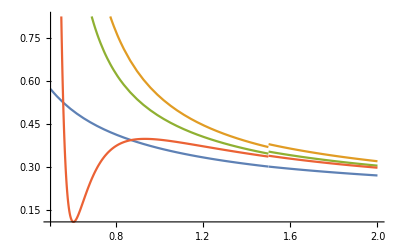

```mathematica
Plot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,2}]
```

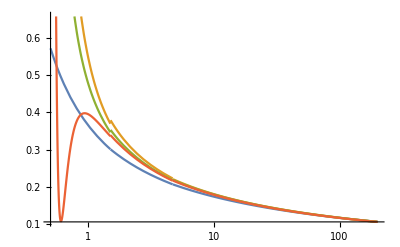

```mathematica
LogLinearPlot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,200}]
```

### μ

```mathematica
(* scale setting prescription: mu/mQ = fudge * alpha_s(mu), solved numerically for mu *)
```

#### LO

```mathematica
Clear[mu];
```

```mathematica
fudge=4;
```

```mathematica
(* Start Nf = 4 *)
```

```mathematica
Nf4α1Loopμ=Reverse@Table[Max[1,mu/.FindRoot[mu==fudge αs1Loop[mu]mQ,{mu,10}]],{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.05254,3.74331,3.42818,3.1062,2.77611,2.43616,2.08379,1.715}

```mathematica
Nf4α1LoopMid=Table[αs1Loop[Nf4α1Loopμ[[k]]],{k,1,Length[Nf4α1Loopμ]}]
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
Nf4α1LoopStepTab=Round[4/(.2 Nf4α1LoopMid^2)]
```

{430,411,390,367,342,314,282,245}

```mathematica
Nf4α1LoopBig=Table[αs1Loop[1/2Nf4α1Loopμ[[k]]],{k,1,Length[Nf4α1Loopμ]}]
```

{0.268835,0.276665,0.28589,0.296997,0.311546,0.330832,0.357283,0.396841}

```mathematica
Nf4α1LoopSmall=Table[αs1Loop[2Nf4α1Loopμ[[k]]],{k,1,Length[Nf4α1Loopμ]}]
```

{0.181799,0.185058,0.188807,0.193197,0.198453,0.204935,0.213849,0.226354}

```mathematica
Length[DeleteDuplicates[Join[Nf4α1LoopMid,Nf4α1LoopBig,Nf4α1LoopSmall]]]
```

24

```mathematica
(* Start Nf = 5 *)
```

```mathematica
Nf5α1Loopμ=Reverse@Table[mu/.FindRoot[mu==fudge αs1Loop[mu]mQ,{mu,10}],{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{83.1266,72.9651,62.6156,52.0329,41.1465,29.8326,17.822,4.05254}

```mathematica
Mt
```

173.34

```mathematica
Nf5α1LoopMid=Table[αs1Loop[Nf5α1Loopμ[[k]]],{k,1,Length[Nf5α1Loopμ]}]
```

{0.11989,0.122221,0.125074,0.128711,0.133637,0.141032,0.154751,0.21556}

```mathematica
Nf5α1LoopStepTab=Round[4/(.2 Nf5α1LoopMid^2)]
```

{1391,1339,1278,1207,1120,1006,835,430}

```mathematica
Nf5α1LoopBig=Table[αs1Loop[1/2Nf5α1Loopμ[[k]]],{k,1,Length[Nf5α1Loopμ]}]
```

{0.133418,0.136311,0.13987,0.144434,0.150667,0.160132,0.178055,0.268835}

```mathematica
Nf5α1LoopSmall=Table[αs1Loop[2Nf5α1Loopμ[[k]]],{k,1,Length[Nf5α1Loopμ]}]
```

{0.108852,0.11077,0.113109,0.116075,0.120067,0.126002,0.136841,0.181799}

```mathematica
Length[DeleteDuplicates[Join[Nf5α1LoopMid,Nf5α1LoopBig,Nf5α1LoopSmall]]]
```

24

```mathematica
Nf4α1LoopmQ=Reverse@Table[mQ,{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.7,4.24286,3.78571,3.32857,2.87143,2.41429,1.95714,1.5}

```mathematica
Nf5α1LoopmQ=Reverse@Table[mQ,{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{173.34,149.249,125.157,101.066,76.9743,52.8829,28.7914,4.7}

#### NLO

```mathematica
(* Start Nf = 4 *)
```

```mathematica
Nf4α2Loopμ=Reverse@Table[Max[1,mu/.FindRoot[mu==fudge αs2Loop[mu]mQ,{mu,10}]],{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.31311,4.00065,3.68202,3.35624,3.02203,2.67764,2.32054,1.94685}

```mathematica
Nf4mQTab=Reverse@Table[mQ,{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.7,4.24286,3.78571,3.32857,2.87143,2.41429,1.95714,1.5}

```mathematica
Nf4α2Loopμ/Nf4mQTab
```

{0.917683,0.942915,0.972609,1.00831,1.05245,1.10908,1.18568,1.2979}

```mathematica
2Nf4α2Loopμ/Nf4mQTab
```

{1.83537,1.88583,1.94522,2.01663,2.1049,2.21816,2.37136,2.5958}

```mathematica
1/2Nf4α2Loopμ/Nf4mQTab
```

{0.458842,0.471457,0.486305,0.504157,0.526225,0.554541,0.592839,0.648951}

```mathematica
Nf4α2LoopMid=Table[αs2Loop[Nf4α2Loopμ[[k]]],{k,1,Length[Nf4α2Loopμ]}]
```

{0.229421,0.235729,0.243152,0.252078,0.263112,0.277271,0.29642,0.324475}

```mathematica
Nf4α2LoopStepTab=Round[4/(.2 Nf4α2LoopMid^2)]
```

{380,360,338,315,289,260,228,190}

```mathematica
Nf4α2LoopBig=Table[αs2Loop[1/2Nf4α2Loopμ[[k]]],{k,1,Length[Nf4α2Loopμ]}]
```

{0.307437,0.319756,0.334731,0.353465,0.377818,0.404105,0.461228,0.564997}

```mathematica
Nf4α2LoopSmall=Table[αs2Loop[2Nf4α2Loopμ[[k]]],{k,1,Length[Nf4α2Loopμ]}]
```

{0.18711,0.190696,0.194827,0.199668,0.205469,0.212624,0.223621,0.238097}

```mathematica
Nf4α2LoopSmall[[-2]]=0.22362;
```

```mathematica
Length[DeleteDuplicates[Join[Nf4α2LoopMid,Nf4α2LoopBig,Nf4α2LoopSmall]]]
```

24

```mathematica
(* Start Nf = 5 *)
```

```mathematica
Nf5α2Loopμ=Reverse@Table[mu/.FindRoot[mu==fudge αs2Loop[mu]mQ,{mu,10}],{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{83.4672,73.3356,63.0103,52.4444,41.5642,30.2405,18.1903,4.31311}

```mathematica
Mt
```

173.34

```mathematica
Nf5mQTab=Reverse@Table[mQ,{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{173.34,149.249,125.157,101.066,76.9743,52.8829,28.7914,4.7}

```mathematica
Nf5α2Loopμ/Nf5mQTab
```

{0.481523,0.491366,0.50345,0.518914,0.539976,0.571839,0.631796,0.917683}

```mathematica
2Nf5α2Loopμ/Nf5mQTab
```

{0.963046,0.982731,1.0069,1.03783,1.07995,1.14368,1.26359,1.83537}

```mathematica
1/2Nf5α2Loopμ/Nf5mQTab
```

{0.240762,0.245683,0.251725,0.259457,0.269988,0.285919,0.315898,0.458842}

```mathematica
Nf5α2LoopMid=Table[αs2Loop[Nf5α2Loopμ[[k]]],{k,1,Length[Nf5α2Loopμ]}]
```

{0.120381,0.122841,0.125862,0.129728,0.134994,0.14296,0.157949,0.229421}

```mathematica
Nf5α2LoopStepTab=Round[4/(.2 Nf5α2LoopMid^2)]
```

{1380,1325,1263,1188,1097,979,802,380}

```mathematica
Nf5α2LoopBig=Table[αs2Loop[1/2Nf5α2Loopμ[[k]]],{k,1,Length[Nf5α2Loopμ]}]
```

{0.134898,0.138021,0.141879,0.146857,0.153712,0.164251,0.18467,0.307437}

```mathematica
Nf5α2LoopSmall=Table[αs2Loop[2Nf5α2Loopμ[[k]]],{k,1,Length[Nf5α2Loopμ]}]
```

{0.108756,0.110748,0.113181,0.116276,0.120457,0.126705,0.138215,0.18711}

```mathematica
Length[DeleteDuplicates[Join[Nf5α2LoopMid,Nf5α2LoopBig,Nf5α2LoopSmall]]]
```

24

```mathematica
Nf4α2LoopmQ=Reverse@Table[mQ,{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.7,4.24286,3.78571,3.32857,2.87143,2.41429,1.95714,1.5}

```mathematica
Nf5α2LoopmQ=Reverse@Table[mQ,{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{173.34,149.249,125.157,101.066,76.9743,52.8829,28.7914,4.7}

#### NNLO

```mathematica
(* Start Nf = 4 *)
```

```mathematica
Nf4α3Loopμ=Reverse@Table[Max[1,mu/.FindRoot[mu==fudge αs3Loop[mu]mQ,{mu,10}]],{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.24177,3.9304,3.61282,3.28803,2.95474,2.61112,2.2546,1.88115}

```mathematica
Nf4α3LoopMid=Table[αs3Loop[Nf4α3Loopμ[[k]]],{k,1,Length[Nf4α3Loopμ]}]
```

{0.225626,0.231589,0.238582,0.246955,0.257253,0.270383,0.287996,0.313525}

```mathematica
Nf4α3LoopStepTab=Round[4/(.2 Nf4α3LoopMid^2)]
```

{393,373,351,328,302,274,241,203}

```mathematica
Nf4mQTab=Reverse@Table[mQ,{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.7,4.24286,3.78571,3.32857,2.87143,2.41429,1.95714,1.5}

```mathematica
Nf4α2Loopμ/Nf4mQTab
```

{0.917683,0.942915,0.972609,1.00831,1.05245,1.10908,1.18568,1.2979}

```mathematica
2Nf4α2Loopμ/Nf4mQTab
```

{1.83537,1.88583,1.94522,2.01663,2.1049,2.21816,2.37136,2.5958}

```mathematica
1/2Nf4α2Loopμ/Nf4mQTab
```

{0.458842,0.471457,0.486305,0.504157,0.526225,0.554541,0.592839,0.648951}

```mathematica
Nf4α3LoopBig=Table[αs3Loop[1/2Nf4α3Loopμ[[k]]],{k,1,Length[Nf4α3Loopμ]}]
```

{0.296093,0.306917,0.319941,0.336039,0.34972,0.380431,0.426678,0.508047}

```mathematica
Nf4α3LoopSmall=Table[αs3Loop[2Nf4α3Loopμ[[k]]],{k,1,Length[Nf4α3Loopμ]}]
```

{0.187113,0.190693,0.194817,0.199654,0.205452,0.212612,0.221075,0.235162}

```mathematica
Length[DeleteDuplicates[Join[Nf4α3LoopMid,Nf4α3LoopBig,Nf4α3LoopSmall]]]
```

24

```mathematica
(* Start Nf = 5 *)
```

```mathematica
Nf5α3Loopμ=Reverse@Table[mu/.FindRoot[mu==fudge αs3Loop[mu]mQ,{mu,10}],{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{83.4695,73.3338,63.0043,52.434,41.5493,30.2209,18.1659,4.24177}

```mathematica
Mt
```

173.34

```mathematica
Nf5mQTab=Reverse@Table[mQ,{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{173.34,149.249,125.157,101.066,76.9743,52.8829,28.7914,4.7}

```mathematica
Nf5α3Loopμ/Nf5mQTab
```

{0.481536,0.491353,0.503401,0.518811,0.539782,0.571469,0.630948,0.902505}

```mathematica
2Nf5α3Loopμ/Nf5mQTab
```

{0.963073,0.982706,1.0068,1.03762,1.07956,1.14294,1.2619,1.80501}

```mathematica
1/2Nf5α3Loopμ/Nf5mQTab
```

{0.240768,0.245677,0.251701,0.259405,0.269891,0.285734,0.315474,0.451253}

```mathematica
Nf5α3LoopMid=Table[αs3Loop[Nf5α3Loopμ[[k]]],{k,1,Length[Nf5α3Loopμ]}]
```

{0.120384,0.122838,0.12585,0.129703,0.134945,0.142867,0.157737,0.225626}

```mathematica
Nf5α3LoopStepTab=Round[4/(.2 Nf5α3LoopMid^2)]
```

{1380,1325,1263,1189,1098,980,804,393}

```mathematica
Nf5α3LoopBig=Table[αs3Loop[1/2Nf5α3Loopμ[[k]]],{k,1,Length[Nf5α3Loopμ]}]
```

{0.134841,0.137946,0.14178,0.146722,0.153516,0.163936,0.184024,0.296093}

```mathematica
Nf5α3LoopSmall=Table[αs3Loop[2Nf5α3Loopμ[[k]]],{k,1,Length[Nf5α3Loopμ]}]
```

{0.108781,0.110771,0.113203,0.116293,0.120467,0.126701,0.138172,0.187113}

```mathematica
Length[DeleteDuplicates[Join[Nf5α3LoopMid,Nf5α3LoopBig,Nf5α3LoopSmall]]]
```

24

```mathematica
Nf4α3LoopmQ=Reverse@Table[mQ,{mQ,Mc,Mb,(Mb-Mc)/7}]
```

{4.7,4.24286,3.78571,3.32857,2.87143,2.41429,1.95714,1.5}

```mathematica
Nf5α3LoopmQ=Reverse@Table[mQ,{mQ,Mb,Mt,(Mt-Mb)/7}]
```

{173.34,149.249,125.157,101.066,76.9743,52.8829,28.7914,4.7}

### Wvfn test

```mathematica
datadir="~/Dropbox (Personal)/physics/projects/heavy_quark_nuclei/data/";
```

```mathematica
NWalkers=200;
```

```mathematica
Nboot=200;
```

```mathematica
<<MaTeX`
```

```mathematica
markerlist={"□","○","△","▽","◇","▯","◦"};
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->None,RoundingRadius->0,FrameMargins->0.2,Background->Directive[Lighter[LightGray,0.75]]]
```

```mathematica
OLegend=LineLegend[{Directive[ColorData[97][1]],Directive[ColorData[97][2]],Directive[ColorData[97][5]],Directive[ColorData[97][3]]},{MaTeX["\\text{LO}",Magnification->0.8],MaTeX["\\text{NLO}",Magnification->0.8],MaTeX["\\text{mNLO}",Magnification->0.8],MaTeX["\\text{NNLO}",Magnification->0.8]},LegendMarkers->{Style[markerlist[[1]],1,Bold,ColorData[97][1]],Style[markerlist[[2]],1,Bold,ColorData[97][2]],Style[markerlist[[5]],1,Bold,ColorData[97][5]],Style[markerlist[[3]],1,Bold,ColorData[97][3]]},LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
OLegend2=LineLegend[{Directive[ColorData[97][1]],Directive[ColorData[97][2]],Directive[ColorData[97][5]],Directive[ColorData[97][3]]},{MaTeX["\\text{LO}",Magnification->0.8],MaTeX["\\text{NLO}",Magnification->0.8],MaTeX["\\text{mNLO}",Magnification->0.8],MaTeX["\\text{NNLO}",Magnification->0.8]},LegendMarkers->{Style[markerlist[[1]],1,Bold,ColorData[97][1]],Style[markerlist[[2]],1,Bold,ColorData[97][2]],Style[markerlist[[5]],1,Bold,ColorData[97][5]],Style[markerlist[[3]],1,Bold,ColorData[97][3]]},LegendLayout->{"Row",2},LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
spoilW=Table[Import[datadir<>"Hammys_LO_dtau0.2_Nstep430_Nwalkers200_Ncoord3_Nc3_Nf4_alpha0.21556_spoila"<>ToString[a]<>"_spoilfhwf.h5",{"Datasets","Ws"}][[All,All,1]],{a,1,5}];
```

```mathematica
spoilH=Table[Import[datadir<>"Hammys_LO_dtau0.2_Nstep430_Nwalkers200_Ncoord3_Nc3_Nf4_alpha0.21556_spoila"<>ToString[a]<>"_spoilfhwf.h5",{"Datasets","Hammys"}][[All,All,1]],{a,1,5}];
```

```mathematica
bootIndices=RandomInteger[{1,NWalkers},{Nboot,NWalkers}];
```

```mathematica
bootSpoilW=Table[Table[spoilW[[a,All,bootIndices[[b]]]],{b,Nboot}],{a,1,5}];
```

```mathematica
bootSpoilH=Table[Table[spoilH[[a,All,bootIndices[[b]]]],{b,Nboot}],{a,1,5}];
```

```mathematica
Nstep=Length[spoilW[[1]]]
```

431

```mathematica
bootTab=ParallelTable[Table[Table[Mean[bootSpoilH[[a,b,t]]bootSpoilW[[a,b,t]]]/Mean[bootSpoilW[[a,b,t]]],{b,1,Nboot}],{t,1,Nstep}],{a,1,5}];
```

```mathematica
αspoil=0.21556;
```

```mathematica
E2LOspoil=-αspoil^2/4(4/3)^2
```

-0.0206516

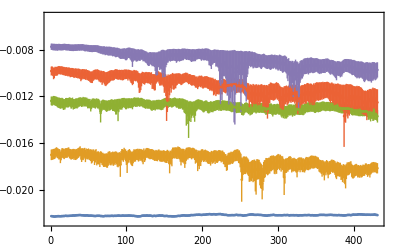

```mathematica
ListPlot[Table[Table[Around[Mean[bootTab[[a,t]]],StandardDeviation[bootTab[[a,t]]]],{t,1,Nstep}],{a,1,5}],PlotRange->{1.1 E2LOspoil,.25 E2LOspoil},Frame->True]
```

### M_QQbar

```mathematica
datadir="~/Dropbox/physics/projects/heavy_quark_nuclei/data/";
```

```mathematica
plotdir="~/Dropbox/physics/projects/heavy_quark_nuclei/plots/";
```

```mathematica
NWalkers=200;
```

```mathematica
<<MaTeX`
```

```mathematica
markerlist={"□","○","△","▽","◇","▯","◦"};
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->None,RoundingRadius->0,FrameMargins->0.2,Background->Directive[Lighter[LightGray,0.75]]]
```

```mathematica
OLegend=LineLegend[{Directive[ColorData[97][1]],Directive[ColorData[97][2]],Directive[ColorData[97][5]],Directive[ColorData[97][3]]},{MaTeX["\\text{LO}",Magnification->0.8],MaTeX["\\text{NLO}",Magnification->0.8],MaTeX["\\text{mNLO}",Magnification->0.8],MaTeX["\\text{NNLO}",Magnification->0.8]},LegendMarkers->{Style[markerlist[[1]],1,Bold,ColorData[97][1]],Style[markerlist[[2]],1,Bold,ColorData[97][2]],Style[markerlist[[5]],1,Bold,ColorData[97][5]],Style[markerlist[[3]],1,Bold,ColorData[97][3]]},LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
OLegend2=LineLegend[{Directive[ColorData[97][1]],Directive[ColorData[97][2]],Directive[ColorData[97][5]],Directive[ColorData[97][3]]},{MaTeX["\\text{LO}",Magnification->0.8],MaTeX["\\text{NLO}",Magnification->0.8],MaTeX["\\text{mNLO}",Magnification->0.8],MaTeX["\\text{NNLO}",Magnification->0.8]},LegendMarkers->{Style[markerlist[[1]],1,Bold,ColorData[97][1]],Style[markerlist[[2]],1,Bold,ColorData[97][2]],Style[markerlist[[5]],1,Bold,ColorData[97][5]],Style[markerlist[[3]],1,Bold,ColorData[97][3]]},LegendLayout->{"Row",2},LegendMargins->0.5,LegendFunction->frame]
```

#### LO

```mathematica
Nf4α1LoopMid
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
Nf4α1LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α1LoopBig]}]
```

{-0.0321210010,-0.0340193410,-0.0363258210,-0.0392032110,-0.0431381810,-0.0486443610,-0.0567338410,-0.0699923510}

```mathematica
Nf4α1LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α1LoopMid]}]
```

{-0.0206516110,-0.0216219410,-0.0227788610,-0.0241904110,-0.0259641710,-0.0282833910,-0.0314892110,-0.0363113410}

```mathematica
Nf4α1LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α1LoopSmall]}]
```

{-0.0146892810,-0.0152206510,-0.0158435910,-0.0165889210,-0.0175038210,-0.0186659410,-0.0203250610,-0.0227716110}

```mathematica
Nf4α1LoopΔEqqbarMid/Nf4α1LoopMid^2
```

{-0.444442622,-0.444446221,-0.444446220,-0.444446218,-0.444444517,-0.444445816,-0.444444214,-0.444445212}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

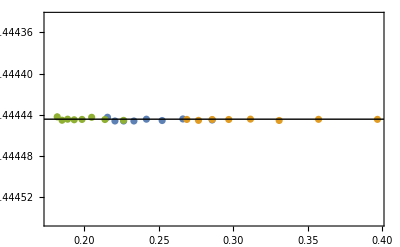

```mathematica
EqqbarNf4α1LoopPlot=Show[ListPlot[{Reverse@Table[{Nf4α1LoopMid[[i]],Nf4α1LoopΔEqqbarMid[[i]]/Nf4α1LoopMid[[i]]^2},{i,1,Length[Nf4α1LoopMid]}],Reverse@Table[{Nf4α1LoopBig[[i]],Nf4α1LoopΔEqqbarBig[[i]]/Nf4α1LoopBig[[i]]^2},{i,1,Length[Nf4α1LoopBig]}],Reverse@Table[{Nf4α1LoopSmall[[i]],Nf4α1LoopΔEqqbarSmall[[i]]/Nf4α1LoopSmall[[i]]^2},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->{ΔEqqbarOα2Exact-.0001,ΔEqqbarOα2Exact+.0001}],Graphics[{Black,Line[{{0,ΔEqqbarOα2Exact},{1,ΔEqqbarOα2Exact}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

```mathematica
αLegendLO=PointLegend[Table[Directive[ColorData[97][1]],{ii,3}],{MaTeX["\\mu=\\mu_p",Magnification->0.8],MaTeX["\\mu=\\mu_p/2",Magnification->0.8],MaTeX["\\mu=2\\mu_p",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][1]],{ii,3}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

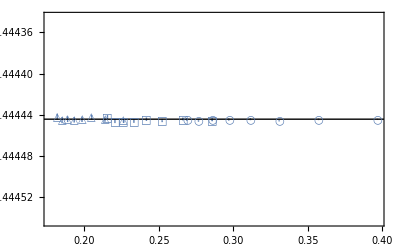

```mathematica
EqqbarNf4α1LoopPlot=Show[ListPlot[{Reverse@Table[{Nf4α1LoopMid[[i]],Nf4α1LoopΔEqqbarMid[[i]]/Nf4α1LoopMid[[i]]^2},{i,1,Length[Nf4α1LoopMid]}],Table[{Nf4α1LoopBig[[i]],Nf4α1LoopΔEqqbarBig[[i]]/Nf4α1LoopBig[[i]]^2},{i,1,Length[Nf4α1LoopBig]}],Reverse@Table[{Nf4α1LoopSmall[[i]],Nf4α1LoopΔEqqbarSmall[[i]]/Nf4α1LoopSmall[[i]]^2},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->{ΔEqqbarOα2Exact-.0001,ΔEqqbarOα2Exact+.0001},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][1]},PlotStyle->{ColorData[97][1]}],Graphics[{Black,Line[{{0,ΔEqqbarOα2Exact},{1,ΔEqqbarOα2Exact}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["\\text{LO}",Magnification->1.2]]
```

```mathematica
Export[plotdir<>"DeltaEQQbar_vs_alpha_LO.pdf",EqqbarNf4α1LoopPlot];
```

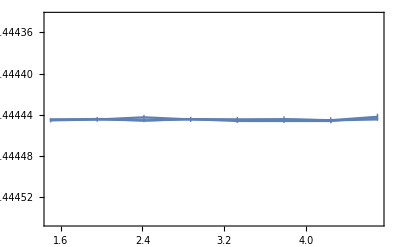

```mathematica
Nf4α1LoopΔEqqbarPlot=Show[ListPlot[{Reverse@Table[{Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqbarMid[[i]]/Nf4α1LoopMid[[i]]^2},{i,1,Length[Nf4α1LoopMid]}],Reverse@Table[{Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqbarBig[[i]]/Nf4α1LoopBig[[i]]^2},{i,1,Length[Nf4α1LoopBig]}],Reverse@Table[{Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqbarSmall[[i]]/Nf4α1LoopSmall[[i]]^2},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->{{Mc,Mb},{ΔEqqbarOα2Exact-.0001,ΔEqqbarOα2Exact+.0001}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

```mathematica
Nf5α1LoopMid
```

{0.11989,0.122221,0.125074,0.128711,0.133637,0.141032,0.154751,0.21556}

```mathematica
Nf5α1LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α1LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α1LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α1LoopBig]}]
```

{-0.0079112710,-0.0082580810,-0.0086949410,-0.0092716410,-0.0100891310,-0.0113965610,-0.0140904810,-0.0321210010}

```mathematica
Nf5α1LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α1LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α1LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α1LoopMid]}]
```

{-0.0063882710,-0.0066391010,-0.0069526710,-0.0073629010,-0.0079372710,-0.0088400110,-0.0106435010,-0.0206516110}

```mathematica
Nf5α1LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α1LoopSmall]}]
```

{-0.0052661110,-0.0054533310,-0.0056860610,-0.0059881810,-0.0064071510,-0.0070562210,-0.0083224310,-0.0146892810}

```mathematica
Nf5α1LoopΔEqqbarMid/Nf5α1LoopMid^2
```

{-0.4444487,-0.4444467,-0.4444456,-0.4444476,-0.4444436,-0.4444475,-0.4444464,-0.444442622}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

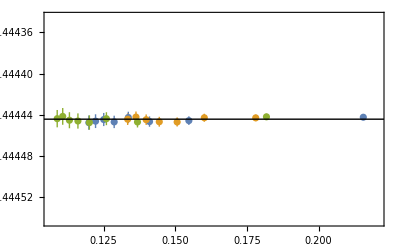

```mathematica
EqqbarNf5α1LoopPlot=Show[ListPlot[{Reverse@Table[{Nf5α1LoopMid[[i]],Nf5α1LoopΔEqqbarMid[[i]]/Nf5α1LoopMid[[i]]^2},{i,1,Length[Nf5α1LoopMid]}],Reverse@Table[{Nf5α1LoopBig[[i]],Nf5α1LoopΔEqqbarBig[[i]]/Nf5α1LoopBig[[i]]^2},{i,1,Length[Nf5α1LoopBig]}],Reverse@Table[{Nf5α1LoopSmall[[i]],Nf5α1LoopΔEqqbarSmall[[i]]/Nf5α1LoopSmall[[i]]^2},{i,1,Length[Nf5α1LoopSmall]}]},PlotRange->{ΔEqqbarOα2Exact-.0001,ΔEqqbarOα2Exact+.0001}],Graphics[{Black,Line[{{0,ΔEqqbarOα2Exact},{1,ΔEqqbarOα2Exact}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

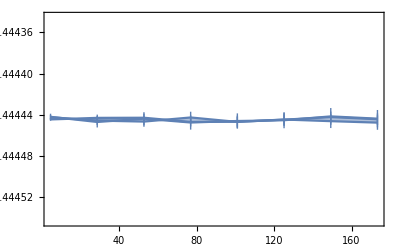

```mathematica
Nf5α1LoopΔEqqbarPlot=Show[ListPlot[{Reverse@Table[{Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqbarMid[[i]]/Nf5α1LoopMid[[i]]^2},{i,1,Length[Nf5α1LoopMid]}],Reverse@Table[{Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqbarBig[[i]]/Nf5α1LoopBig[[i]]^2},{i,1,Length[Nf5α1LoopBig]}],Reverse@Table[{Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqbarSmall[[i]]/Nf5α1LoopSmall[[i]]^2},{i,1,Length[Nf5α1LoopSmall]}]},PlotRange->{{Mb,Mt},{ΔEqqbarOα2Exact-.0001,ΔEqqbarOα2Exact+.0001}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

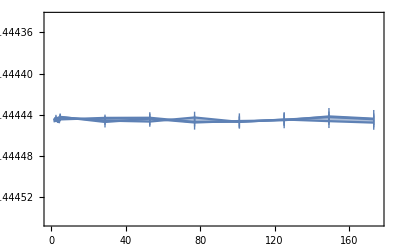

```mathematica
Show[Nf4α1LoopΔEqqbarPlot,Nf5α1LoopΔEqqbarPlot,PlotRange->{{Mc-2,Mt+2},{ΔEqqbarOα2Exact-.0001,ΔEqqbarOα2Exact+.0001}}]
```

#### NLO

```mathematica
Nf4α2LoopMid
```

{0.229421,0.235729,0.243152,0.252078,0.263112,0.277271,0.29642,0.324475}

```mathematica
Nf4α2LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α2LoopBig]}]
```

{-0.090110.00025,-0.098150.00027,-0.109490.00035,-0.128360.00033,-0.15180.0007,-0.17920.0006,-0.24290.0010,-0.40110.0011}

```mathematica
Nf4α2LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α2LoopMid]}]
```

{-0.054690.00030,-0.059570.00034,-0.062330.00035,-0.06970.0004,-0.07940.0005,-0.08960.0005,-0.10600.0007,-0.13800.0009}

```mathematica
Nf4α2LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α2LoopSmall]}]
```

{-0.037480.00028,-0.040020.00031,-0.042470.00033,-0.04540.0004,-0.04720.0005,-0.05280.0005,-0.05940.0005,-0.07180.0007}

```mathematica
Nf4α2LoopΔEqqbarMid/Nf4α2LoopMid^2
```

{-1.0390.006,-1.0720.006,-1.0540.006,-1.0970.007,-1.1470.007,-1.1650.007,-1.2060.008,-1.3110.009}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Nf4α2LoopΔEqqbarBig/Nf4α2LoopBig^2
```

{-0.95330.0027,-0.95990.0026,-0.97720.0031,-1.02740.0026,-1.0640.005,-1.0980.004,-1.1420.005,-1.25660.0034}

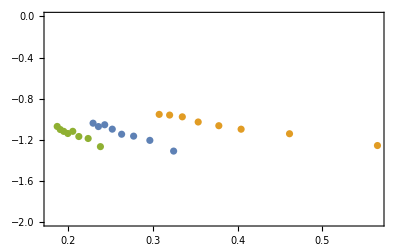

```mathematica
EqqbarNf4α2LoopPlot=Show[ListPlot[{Table[{Nf4α2LoopMid[[i]],Nf4α2LoopΔEqqbarMid[[i]]/Nf4α2LoopMid[[i]]^2},{i,1,Length[Nf4α2LoopMid]}],Table[{Nf4α2LoopBig[[i]],Nf4α2LoopΔEqqbarBig[[i]]/Nf4α2LoopBig[[i]]^2},{i,1,Length[Nf4α2LoopBig]}],Table[{Nf4α2LoopSmall[[i]],Nf4α2LoopΔEqqbarSmall[[i]]/Nf4α2LoopSmall[[i]]^2},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->{-2,0}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

```mathematica
αLegendNLO=PointLegend[Table[Directive[ColorData[97][2]],{ii,3}],{MaTeX["\\mu=\\mu_p",Magnification->0.8],MaTeX["\\mu=\\mu_p/2",Magnification->0.8],MaTeX["\\mu=2\\mu_p",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][2]],{ii,3}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

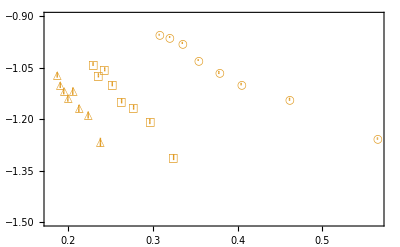

```mathematica
EqqbarNf4α2LoopPlot=Show[ListPlot[{Table[{Nf4α2LoopMid[[i]],Nf4α2LoopΔEqqbarMid[[i]]/Nf4α2LoopMid[[i]]^2},{i,1,Length[Nf4α2LoopMid]}],Table[{Nf4α2LoopBig[[i]],Nf4α2LoopΔEqqbarBig[[i]]/Nf4α2LoopBig[[i]]^2},{i,1,Length[Nf4α2LoopBig]}],Table[{Nf4α2LoopSmall[[i]],Nf4α2LoopΔEqqbarSmall[[i]]/Nf4α2LoopSmall[[i]]^2},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->{-1.5,-.9},PlotLegends->Placed[αLegendNLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][2]},PlotStyle->{ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["\\text{NLO}",Magnification->1.2]]
```

```mathematica
Export[plotdir<>"DeltaEQQbar_vs_alpha_NLO.pdf",EqqbarNf4α2LoopPlot];
```

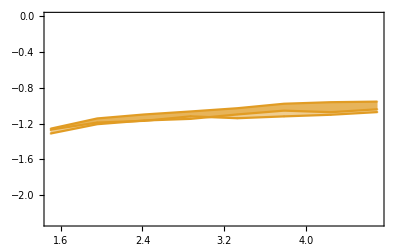

```mathematica
Nf4α2LoopΔEqqbarPlot=Show[ListPlot[{Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqbarMid[[i]]/Nf4α2LoopMid[[i]]^2},{i,1,Length[Nf4α2LoopMid]}],Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqbarBig[[i]]/Nf4α2LoopBig[[i]]^2},{i,1,Length[Nf4α2LoopBig]}],Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqbarSmall[[i]]/Nf4α2LoopSmall[[i]]^2},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->{{Mc,Mb},{-2.3,0}},Joined->True,Filling->{True},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

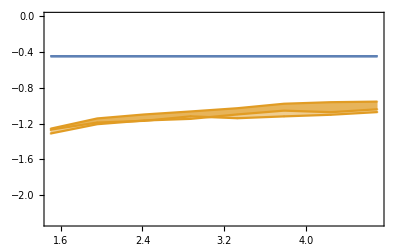

```mathematica
Show[Nf4α2LoopΔEqqbarPlot,Nf4α1LoopΔEqqbarPlot]
```

```mathematica
Nf5α2LoopMid
```

{0.120381,0.122841,0.125862,0.129728,0.134994,0.14296,0.157949,0.229421}

```mathematica
Nf5α2LoopBig
```

{0.134898,0.138021,0.141879,0.146857,0.153712,0.164251,0.18467,0.307437}

```mathematica
Nf5α2LoopSmall
```

{0.108756,0.110748,0.113181,0.116276,0.120457,0.126705,0.138215,0.18711}

```mathematica
Nf4α2LoopMid
```

{0.229421,0.235729,0.243152,0.252078,0.263112,0.277271,0.29642,0.324475}

```mathematica
Nf4α2LoopBig
```

{0.307437,0.319756,0.334731,0.353465,0.377818,0.404105,0.461228,0.564997}

```mathematica
Nf4α2LoopSmall
```

{0.18711,0.190696,0.194827,0.199668,0.205469,0.212624,0.22362,0.238097}

```mathematica
Nf5α2Loopμ
```

{83.4672,73.3356,63.0103,52.4444,41.5642,30.2405,18.1903,4.31311}

```mathematica
Nf4α2Loopμ
```

{4.31311,4.00065,3.68202,3.35624,3.02203,2.67764,2.32054,1.94685}

```mathematica
Nf5α2LoopStepTab
```

{1380,1325,1263,1188,1097,979,802,380}

```mathematica
Nf4α2LoopStepTab
```

{380,360,338,315,289,260,228,190}

```mathematica
Nf5α2LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α2LoopBig]}]
```

{-0.0119740.000020,-0.0127590.000018,-0.0136120.000021,-0.0146910.000021,-0.0163300.000030,-0.018790.00004,-0.025110.00004,-0.086280.00024}

```mathematica
Nf5α2LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α2LoopMid]}]
```

{-0.0105170.000025,-0.0106010.000028,-0.0115080.000031,-0.012340.00004,-0.013080.00004,-0.015410.00005,-0.019410.00008,-0.050350.00027}

```mathematica
Nf5α2LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α2LoopSmall]}]
```

{-0.008870.00004,-0.0092320.000035,-0.009860.00004,-0.010570.00004,-0.011340.00004,-0.012890.00006,-0.016270.00008,-0.035490.00026}

```mathematica
Nf4α2LoopΔEqqbarBig
```

{-0.090110.00025,-0.098150.00027,-0.109490.00035,-0.128360.00033,-0.15180.0007,-0.17920.0006,-0.24290.0010,-0.40110.0011}

```mathematica
Nf4α2LoopΔEqqbarMid
```

{-0.054690.00030,-0.059570.00034,-0.062330.00035,-0.06970.0004,-0.07940.0005,-0.08960.0005,-0.10600.0007,-0.13800.0009}

```mathematica
Nf4α2LoopΔEqqbarSmall
```

{-0.037480.00028,-0.040020.00031,-0.042470.00033,-0.04540.0004,-0.04720.0005,-0.05280.0005,-0.05940.0005,-0.07180.0007}

```mathematica
Nf5α2LoopΔEqqbarMid/Nf5α2LoopMid^2
```

{-0.72570.0018,-0.70250.0018,-0.72640.0020,-0.73330.0021,-0.71770.0022,-0.75380.0022,-0.77810.0032,-0.9570.005}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Nf5α2LoopΔEqqbarBig/Nf5α2LoopBig^2
```

{-0.65800.0011,-0.66980.0009,-0.67620.0010,-0.68120.0010,-0.69110.0013,-0.69640.0014,-0.73630.0013,-0.91290.0025}

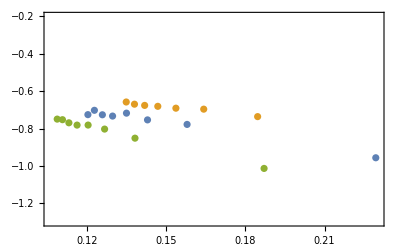

```mathematica
EqqbarNf5α2LoopPlot=Show[ListPlot[{Reverse@Table[{Nf5α2LoopMid[[i]],Nf5α2LoopΔEqqbarMid[[i]]/Nf5α2LoopMid[[i]]^2},{i,1,Length[Nf5α2LoopMid]}],Reverse@Table[{Nf5α2LoopBig[[i]],Nf5α2LoopΔEqqbarBig[[i]]/Nf5α2LoopBig[[i]]^2},{i,1,Length[Nf5α2LoopBig]}],Reverse@Table[{Nf5α2LoopSmall[[i]],Nf5α2LoopΔEqqbarSmall[[i]]/Nf5α2LoopSmall[[i]]^2},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->{-1.3,-.2}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

```mathematica
Nf5α2LoopΔEqqbarBig/Nf5α2LoopBig^2
```

{-0.65800.0011,-0.66980.0009,-0.67620.0010,-0.68120.0010,-0.69110.0013,-0.69640.0014,-0.73630.0013,-0.91290.0025}

```mathematica
Nf5α2LoopΔEqqbarSmall/Nf5α2LoopSmall^2
```

{-0.74960.0034,-0.75270.0028,-0.76940.0028,-0.78170.0033,-0.78150.0029,-0.80300.0035,-0.8520.004,-1.0140.007}

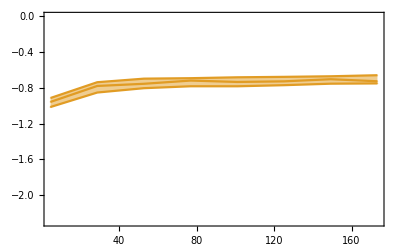

```mathematica
Nf5α2LoopΔEqqbarPlot=Show[ListPlot[{Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopΔEqqbarMid[[i]]/Nf5α2LoopMid[[i]]^2},{i,1,Length[Nf5α2LoopMid]}],Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopΔEqqbarBig[[i]]/Nf5α2LoopBig[[i]]^2},{i,1,Length[Nf5α2LoopBig]}],Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopΔEqqbarSmall[[i]]/Nf5α2LoopSmall[[i]]^2},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->{{Mb,Mt},{-2.3,0}},Joined->True,Filling->{2->{3}},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

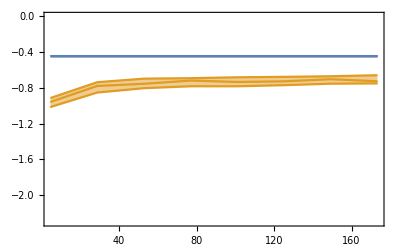

```mathematica
Show[Nf5α2LoopΔEqqbarPlot,Nf5α1LoopΔEqqbarPlot]
```

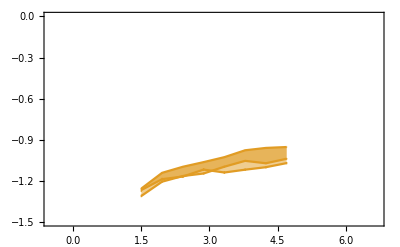

```mathematica
Show[Nf4α2LoopΔEqqbarPlot,PlotRange->{{Mc-2,Mb+2},{-1.5,0}}]
```

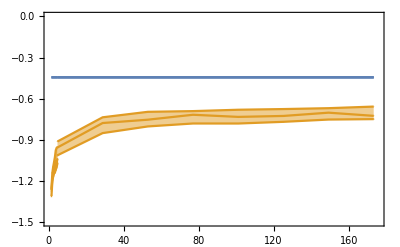

```mathematica
Show[Nf4α2LoopΔEqqbarPlot,Nf5α2LoopΔEqqbarPlot,Nf4α1LoopΔEqqbarPlot,Nf5α1LoopΔEqqbarPlot,PlotRange->{{2Mc-2,Mt+2},{-1.5,0}}]
```

#### mNLO

```mathematica
Nf4α2LoopMid
```

{0.229421,0.235729,0.243152,0.252078,0.263112,0.277271,0.29642,0.324475}

```mathematica
Nf4α2LoopmΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α2LoopBig]}]
```

{-0.10470.0006,-0.11440.0008,-0.13130.0009,-0.15450.0010,-0.19420.0015,-0.22440.0019,-0.33340.0029,-0.5960.005}

```mathematica
Nf4α2LoopmΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α2LoopMid]}]
```

{-0.05670.0004,-0.06060.0006,-0.06910.0006,-0.07660.0007,-0.08690.0008,-0.09790.0010,-0.12140.0013,-0.15140.0017}

```mathematica
Nf4α2LoopmΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α2LoopSmall]}]
```

{-0.03830.0004,-0.04100.0004,-0.04290.0005,-0.04830.0005,-0.05170.0006,-0.05620.0006,-0.06700.0008,-0.07800.0010}

```mathematica
Nf4α2LoopmΔEqqbarMid/Nf4α2LoopMid^2
```

{-1.0780.008,-1.0910.010,-1.1700.010,-1.2060.010,-1.2550.012,-1.2730.012,-1.3810.015,-1.4380.016}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Nf4α2LoopmΔEqqbarBig/Nf4α2LoopBig^2
```

{-1.1070.007,-1.1180.007,-1.1720.008,-1.2360.008,-1.3610.011,-1.3740.012,-1.5670.014,-1.8670.017}

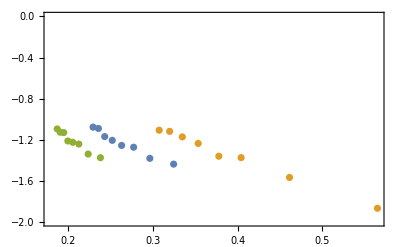

```mathematica
EqqbarNf4α2LoopmPlot=Show[ListPlot[{Table[{Nf4α2LoopMid[[i]],Nf4α2LoopmΔEqqbarMid[[i]]/Nf4α2LoopMid[[i]]^2},{i,1,Length[Nf4α2LoopMid]}],Table[{Nf4α2LoopBig[[i]],Nf4α2LoopmΔEqqbarBig[[i]]/Nf4α2LoopBig[[i]]^2},{i,1,Length[Nf4α2LoopBig]}],Table[{Nf4α2LoopSmall[[i]],Nf4α2LoopmΔEqqbarSmall[[i]]/Nf4α2LoopSmall[[i]]^2},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->{-2,0}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

```mathematica
αLegendmNLO=PointLegend[Table[Directive[ColorData[97][5]],{ii,3}],{MaTeX["\\mu=\\mu_p",Magnification->0.8],MaTeX["\\mu=\\mu_p/2",Magnification->0.8],MaTeX["\\mu=2\\mu_p",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][5]],{ii,3}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

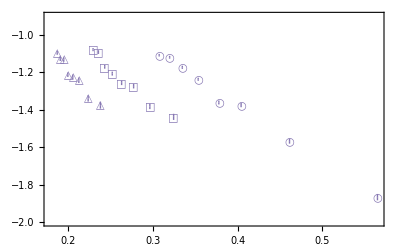

```mathematica
EqqbarNf4α2LoopmPlot=Show[ListPlot[{Table[{Nf4α2LoopMid[[i]],Nf4α2LoopmΔEqqbarMid[[i]]/Nf4α2LoopMid[[i]]^2},{i,1,Length[Nf4α2LoopMid]}],Table[{Nf4α2LoopBig[[i]],Nf4α2LoopmΔEqqbarBig[[i]]/Nf4α2LoopBig[[i]]^2},{i,1,Length[Nf4α2LoopBig]}],Table[{Nf4α2LoopSmall[[i]],Nf4α2LoopmΔEqqbarSmall[[i]]/Nf4α2LoopSmall[[i]]^2},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->{-2,-.9},PlotLegends->Placed[αLegendmNLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][5]},PlotStyle->{ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["\\text{mNLO}",Magnification->1.2]]
```

```mathematica
Export[plotdir<>"DeltaEQQbar_vs_alpha_mNLO.pdf",EqqbarNf4α2LoopmPlot];
```

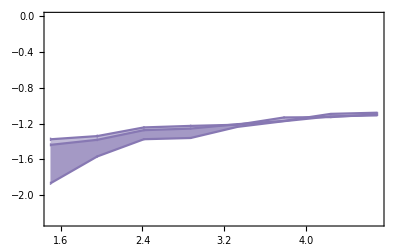

```mathematica
Nf4α2LoopmΔEqqbarPlot=Show[ListPlot[{Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopmΔEqqbarMid[[i]]/Nf4α2LoopMid[[i]]^2},{i,1,Length[Nf4α2LoopMid]}],Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopmΔEqqbarBig[[i]]/Nf4α2LoopBig[[i]]^2},{i,1,Length[Nf4α2LoopBig]}],Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopmΔEqqbarSmall[[i]]/Nf4α2LoopSmall[[i]]^2},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->{{Mc,Mb},{-2.3,0}},Joined->True,Filling->{True},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

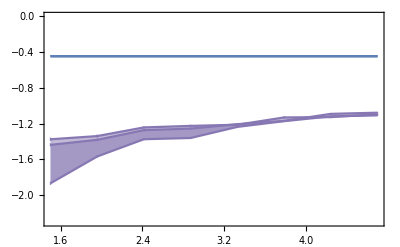

```mathematica
Show[Nf4α2LoopmΔEqqbarPlot,Nf4α1LoopΔEqqbarPlot]
```

```mathematica
Nf5α2LoopMid
```

{0.120381,0.122841,0.125862,0.129728,0.134994,0.14296,0.157949,0.229421}

```mathematica
Nf5α2LoopBig
```

{0.134898,0.138021,0.141879,0.146857,0.153712,0.164251,0.18467,0.307437}

```mathematica
Nf5α2LoopSmall
```

{0.108756,0.110748,0.113181,0.116276,0.120457,0.126705,0.138215,0.18711}

```mathematica
Nf4α2LoopMid
```

{0.229421,0.235729,0.243152,0.252078,0.263112,0.277271,0.29642,0.324475}

```mathematica
Nf4α2LoopBig
```

{0.307437,0.319756,0.334731,0.353465,0.377818,0.404105,0.461228,0.564997}

```mathematica
Nf4α2LoopSmall
```

{0.18711,0.190696,0.194827,0.199668,0.205469,0.212624,0.22362,0.238097}

```mathematica
Nf5α2Loopμ
```

{83.4672,73.3356,63.0103,52.4444,41.5642,30.2405,18.1903,4.31311}

```mathematica
Nf4α2Loopμ
```

{4.31311,4.00065,3.68202,3.35624,3.02203,2.67764,2.32054,1.94685}

```mathematica
Nf5α2LoopStepTab
```

{1380,1325,1263,1188,1097,979,802,380}

```mathematica
Nf4α2LoopStepTab
```

{380,360,338,315,289,260,228,190}

```mathematica
Nf5α2LoopmΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α2LoopBig]}]
```

{-0.0125810.000033,-0.013030.00004,-0.014230.00004,-0.015420.00004,-0.016780.00007,-0.019880.00007,-0.026650.00010,-0.10400.0006}

```mathematica
Nf5α2LoopmΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α2LoopMid]}]
```

{-0.010620.00004,-0.011010.00004,-0.011520.00004,-0.012430.00005,-0.014080.00006,-0.016140.00007,-0.021060.00011,-0.05740.0004}

```mathematica
Nf5α2LoopmΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α2LoopSmall]}]
```

{-0.009150.00004,-0.009500.00005,-0.009780.00005,-0.010440.00005,-0.011750.00006,-0.013150.00007,-0.016710.00010,-0.03780.0004}

```mathematica
Nf4α2LoopmΔEqqbarBig
```

{-0.10470.0006,-0.11440.0008,-0.13130.0009,-0.15450.0010,-0.19420.0015,-0.22440.0019,-0.33340.0029,-0.5960.005}

```mathematica
Nf4α2LoopmΔEqqbarMid
```

{-0.05670.0004,-0.06060.0006,-0.06910.0006,-0.07660.0007,-0.08690.0008,-0.09790.0010,-0.12140.0013,-0.15140.0017}

```mathematica
Nf4α2LoopmΔEqqbarSmall
```

{-0.03830.0004,-0.04100.0004,-0.04290.0005,-0.04830.0005,-0.05170.0006,-0.05620.0006,-0.06700.0008,-0.07800.0010}

```mathematica
Nf5α2LoopmΔEqqbarMid/Nf5α2LoopMid^2
```

{-0.73300.0027,-0.72990.0028,-0.72720.0028,-0.73880.0031,-0.77280.0034,-0.78980.0035,-0.8440.004,-1.0900.007}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Nf5α2LoopmΔEqqbarBig/Nf5α2LoopBig^2
```

{-0.69130.0018,-0.68390.0019,-0.70680.0019,-0.71490.0020,-0.71000.0028,-0.73680.0026,-0.78140.0030,-1.1010.007}

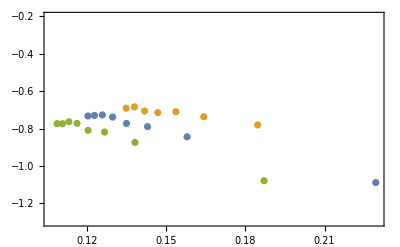

```mathematica
EqqbarNf5α2LoopmPlot=Show[ListPlot[{Reverse@Table[{Nf5α2LoopMid[[i]],Nf5α2LoopmΔEqqbarMid[[i]]/Nf5α2LoopMid[[i]]^2},{i,1,Length[Nf5α2LoopMid]}],Reverse@Table[{Nf5α2LoopBig[[i]],Nf5α2LoopmΔEqqbarBig[[i]]/Nf5α2LoopBig[[i]]^2},{i,1,Length[Nf5α2LoopBig]}],Reverse@Table[{Nf5α2LoopSmall[[i]],Nf5α2LoopmΔEqqbarSmall[[i]]/Nf5α2LoopSmall[[i]]^2},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->{-1.3,-.2}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

```mathematica
Nf5α2LoopmΔEqqbarBig/Nf5α2LoopBig^2
```

{-0.69130.0018,-0.68390.0019,-0.70680.0019,-0.71490.0020,-0.71000.0028,-0.73680.0026,-0.78140.0030,-1.1010.007}

```mathematica
Nf5α2LoopmΔEqqbarSmall/Nf5α2LoopSmall^2
```

{-0.77360.0032,-0.7740.004,-0.7630.004,-0.7720.004,-0.8100.004,-0.8190.005,-0.8750.005,-1.0800.011}

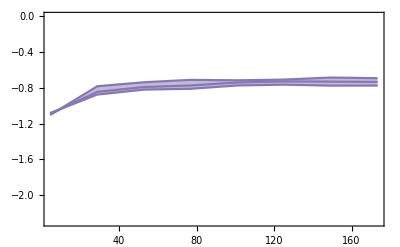

```mathematica
Nf5α2LoopmΔEqqbarPlot=Show[ListPlot[{Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopmΔEqqbarMid[[i]]/Nf5α2LoopMid[[i]]^2},{i,1,Length[Nf5α2LoopMid]}],Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopmΔEqqbarBig[[i]]/Nf5α2LoopBig[[i]]^2},{i,1,Length[Nf5α2LoopBig]}],Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopmΔEqqbarSmall[[i]]/Nf5α2LoopSmall[[i]]^2},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->{{Mb,Mt},{-2.3,0}},Joined->True,Filling->{2->{3}},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

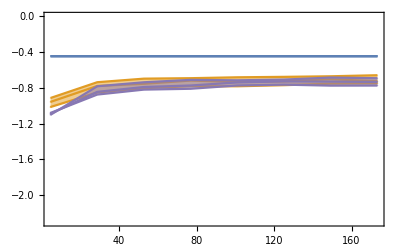

```mathematica
Show[Nf5α2LoopΔEqqbarPlot,Nf5α2LoopmΔEqqbarPlot,Nf5α1LoopΔEqqbarPlot]
```

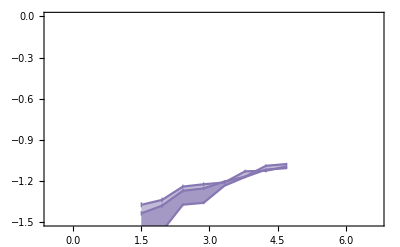

```mathematica
Show[Nf4α2LoopmΔEqqbarPlot,PlotRange->{{Mc-2,Mb+2},{-1.5,0}}]
```

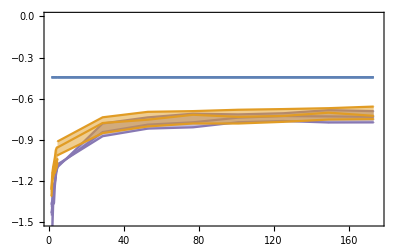

```mathematica
Show[Nf4α2LoopmΔEqqbarPlot,Nf5α2LoopmΔEqqbarPlot,Nf4α2LoopΔEqqbarPlot,Nf5α2LoopΔEqqbarPlot,Nf4α1LoopΔEqqbarPlot,Nf5α1LoopΔEqqbarPlot,PlotRange->{{2Mc-2,Mt+2},{-1.5,0}}]
```

#### NNLO

```mathematica
Nf4α3LoopMid
```

{0.225626,0.231589,0.238582,0.246955,0.257253,0.270383,0.287996,0.313525}

```mathematica
Nf4α3LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α3LoopBig]}]
```

{-0.14660.0005,-0.16100.0006,-0.18390.0006,-0.21110.0009,-0.24520.0011,-0.32580.0014,-0.46060.0018,-0.78260.0033}

```mathematica
Nf4α3LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α3LoopMid]}]
```

{-0.08950.0005,-0.09890.0006,-0.10750.0006,-0.11950.0007,-0.13580.0009,-0.15420.0013,-0.19530.0014,-0.25610.0022}

```mathematica
Nf4α3LoopSmall
```

{0.187113,0.190693,0.194817,0.199654,0.205452,0.212612,0.221075,0.235162}

```mathematica
Nf4α3LoopStepTab
```

{393,373,351,328,302,274,241,203}

```mathematica
Nf4α3LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α3LoopSmall]}]
```

{-0.06250.0005,-0.06780.0005,-0.07350.0006,-0.07850.0007,-0.08550.0008,-0.09610.0010,-0.11180.0011,-0.13900.0016}

```mathematica
Nf4α3LoopΔEqqbarMid/Nf4α3LoopMid^2
```

{-1.7590.010,-1.8430.012,-1.8880.011,-1.9600.012,-2.0520.013,-2.1100.017,-2.3550.017,-2.6050.022}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Nf4α3LoopΔEqqbarBig/Nf4α3LoopBig^2
```

{-1.6730.006,-1.7090.006,-1.7970.006,-1.8690.008,-2.0050.009,-2.2510.009,-2.5300.010,-3.0320.013}

```mathematica
αLegendNNLO=PointLegend[Table[Directive[ColorData[97][3]],{ii,3}],{MaTeX["\\mu=\\mu_p",Magnification->0.8],MaTeX["\\mu=\\mu_p/2",Magnification->0.8],MaTeX["\\mu=2\\mu_p",Magnification->0.8]},LegendMarkers->Table[Style[markerlist[[ii]],14,Bold,ColorData[97][3]],{ii,3}],LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

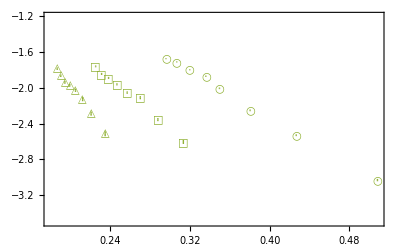

```mathematica
EqqbarNf4α3LoopPlot=Show[ListPlot[{Table[{Nf4α3LoopMid[[i]],Nf4α3LoopΔEqqbarMid[[i]]/Nf4α3LoopMid[[i]]^2},{i,1,Length[Nf4α3LoopMid]}],Table[{Nf4α3LoopBig[[i]],Nf4α3LoopΔEqqbarBig[[i]]/Nf4α3LoopBig[[i]]^2},{i,1,Length[Nf4α3LoopBig]}],Table[{Nf4α3LoopSmall[[i]],Nf4α3LoopΔEqqbarSmall[[i]]/Nf4α3LoopSmall[[i]]^2},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->{-3.5,-1.2},PlotLegends->Placed[αLegendNNLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][3]},PlotStyle->{ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["\\text{NNLO}",Magnification->1.2]]
```

```mathematica
Export[plotdir<>"DeltaEQQbar_vs_alpha_NNLO.pdf",EqqbarNf4α3LoopPlot];
```

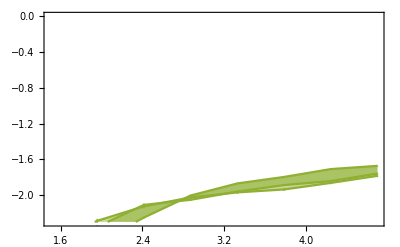

```mathematica
Nf4α3LoopΔEqqbarPlot=Show[ListPlot[{Reverse@Table[{Nf4α3LoopmQ[[i]],Nf4α3LoopΔEqqbarMid[[i]]/Nf4α3LoopMid[[i]]^2},{i,1,Length[Nf4α3LoopMid]}],Reverse@Table[{Nf4α3LoopmQ[[i]],Nf4α3LoopΔEqqbarBig[[i]]/Nf4α3LoopBig[[i]]^2},{i,1,Length[Nf4α3LoopBig]}],Reverse@Table[{Nf4α3LoopmQ[[i]],Nf4α3LoopΔEqqbarSmall[[i]]/Nf4α3LoopSmall[[i]]^2},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->{{Mc,Mb},{-2.3,0}},Joined->True,Filling->True,IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

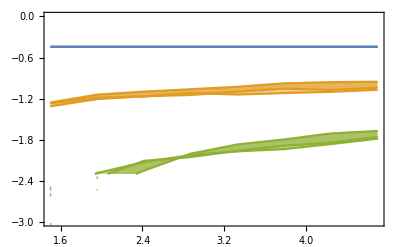

```mathematica
Show[Nf4α3LoopΔEqqbarPlot,Nf4α2LoopΔEqqbarPlot,Nf4α1LoopΔEqqbarPlot,PlotRange->{-3,0}]
```

```mathematica
Show[Nf4α3LoopΔEqqbarPlot,Nf5α3LoopΔEqqbarPlot,PlotRange->{{1.4,6},{-3,0}}]
```

Rule::argr: Rule called with 1 argument; 2 arguments are expected.

General::stop: Further output of Rule::argr will be suppressed during this calculation.

Show::gcomb: Could not combine the graphics objects in ….

Show[-Graphics-,Nf5α3LoopΔEqqbarPlot,PlotRange→{{1.4,6},{-3,0}}]

```mathematica
Nf5α3LoopMid
```

{0.120384,0.122838,0.12585,0.129703,0.134945,0.142867,0.157737,0.225626}

```mathematica
Nf5α3LoopBig
```

{0.134841,0.137946,0.14178,0.146722,0.153516,0.163936,0.184024,0.296093}

```mathematica
Nf5α3LoopSmall
```

{0.108781,0.110771,0.113203,0.116293,0.120467,0.126701,0.138172,0.187113}

```mathematica
Nf4α3LoopMid
```

{0.225626,0.231589,0.238582,0.246955,0.257253,0.270383,0.287996,0.313525}

```mathematica
Nf4α3LoopBig
```

{0.296093,0.306917,0.319941,0.336039,0.34972,0.380431,0.426678,0.508047}

```mathematica
Nf4α3LoopSmall
```

{0.187113,0.190693,0.194817,0.199654,0.205452,0.212612,0.221075,0.235162}

```mathematica
Nf5α3Loopμ
```

{83.4695,73.3338,63.0043,52.434,41.5493,30.2209,18.1659,4.24177}

```mathematica
Nf4α3Loopμ
```

{4.24177,3.9304,3.61282,3.28803,2.95474,2.61112,2.2546,1.88115}

```mathematica
Nf5α3LoopStepTab
```

{1380,1325,1263,1189,1098,980,804,393}

```mathematica
Nf4α3LoopStepTab
```

{393,373,351,328,302,274,241,203}

```mathematica
Nf5α3LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α3LoopBig]}]
```

{-0.0143750.000019,-0.0153930.000022,-0.0161910.000033,-0.0178700.000034,-0.0203020.000035,-0.023800.00006,-0.032590.00008,-0.12640.0005}

```mathematica
Nf5α3LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α3LoopMid]}]
```

{-0.012720.00004,-0.013450.00004,-0.014210.00005,-0.015710.00005,-0.017760.00005,-0.019860.00007,-0.026710.00012,-0.07960.0004}

```mathematica
Nf5α3LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α3LoopSmall]}]
```

{-0.010950.00005,-0.011620.00005,-0.012370.00006,-0.013500.00007,-0.014670.00007,-0.017120.00010,-0.022650.00013,-0.05350.0005}

```mathematica
Nf4α3LoopΔEqqbarBig
```

{-0.14660.0005,-0.16100.0006,-0.18390.0006,-0.21110.0009,-0.24520.0011,-0.32580.0014,-0.46060.0018,-0.78260.0033}

```mathematica
Nf4α3LoopΔEqqbarMid
```

{-0.08950.0005,-0.09890.0006,-0.10750.0006,-0.11950.0007,-0.13580.0009,-0.15420.0013,-0.19530.0014,-0.25610.0022}

```mathematica
Nf4α3LoopΔEqqbarSmall
```

{-0.06250.0005,-0.06780.0005,-0.07350.0006,-0.07850.0007,-0.08550.0008,-0.09610.0010,-0.11180.0011,-0.13900.0016}

```mathematica
Nf5α3LoopΔEqqbarMid/Nf5α3LoopMid^2
```

{-0.87750.0025,-0.89110.0026,-0.89710.0029,-0.93360.0030,-0.97510.0029,-0.9730.004,-1.0740.005,-1.5640.008}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Nf5α3LoopΔEqqbarBig/Nf5α3LoopBig^2
```

{-0.79060.0011,-0.80890.0012,-0.80550.0017,-0.83010.0016,-0.86150.0015,-0.88550.0021,-0.96240.0024,-1.4410.006}

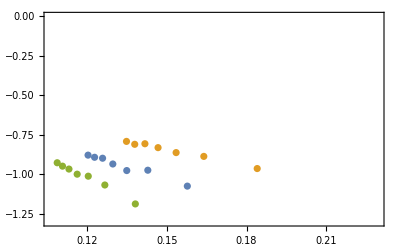

```mathematica
EqqbarNf5α3LoopPlot=Show[ListPlot[{Reverse@Table[{Nf5α3LoopMid[[i]],Nf5α3LoopΔEqqbarMid[[i]]/Nf5α3LoopMid[[i]]^2},{i,1,Length[Nf5α3LoopMid]}],Reverse@Table[{Nf5α3LoopBig[[i]],Nf5α3LoopΔEqqbarBig[[i]]/Nf5α3LoopBig[[i]]^2},{i,1,Length[Nf5α3LoopBig]}],Reverse@Table[{Nf5α3LoopSmall[[i]],Nf5α3LoopΔEqqbarSmall[[i]]/Nf5α3LoopSmall[[i]]^2},{i,1,Length[Nf5α3LoopSmall]}]},PlotRange->{-1.3,0}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

```mathematica
Nf5α3LoopΔEqqbarBig/Nf5α3LoopBig^2
```

{-0.79060.0011,-0.80890.0012,-0.80550.0017,-0.83010.0016,-0.86150.0015,-0.88550.0021,-0.96240.0024,-1.4410.006}

```mathematica
Nf5α3LoopΔEqqbarSmall/Nf5α3LoopSmall^2
```

{-0.9260.004,-0.9470.004,-0.9660.004,-0.9980.005,-1.0110.005,-1.0670.006,-1.1860.007,-1.5290.015}

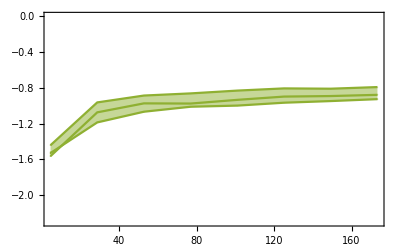

```mathematica
Nf5α3LoopΔEqqbarPlot=Show[ListPlot[{Reverse@Table[{Nf5α3LoopmQ[[i]],Nf5α3LoopΔEqqbarMid[[i]]/Nf5α3LoopMid[[i]]^2},{i,1,Length[Nf5α3LoopMid]}],Reverse@Table[{Nf5α3LoopmQ[[i]],Nf5α3LoopΔEqqbarBig[[i]]/Nf5α3LoopBig[[i]]^2},{i,1,Length[Nf5α3LoopBig]}],Reverse@Table[{Nf5α3LoopmQ[[i]],Nf5α3LoopΔEqqbarSmall[[i]]/Nf5α3LoopSmall[[i]]^2},{i,1,Length[Nf5α3LoopSmall]}]},PlotRange->{{Mb,Mt},{-2.3,0}},Joined->True,Filling->{2->{3}},PlotLegends->Placed[OLegend,{0.5,0.2}],IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

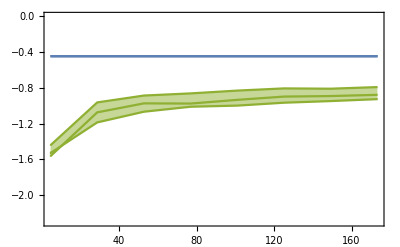

```mathematica
Show[Nf5α3LoopΔEqqbarPlot,Nf5α1LoopΔEqqbarPlot]
```

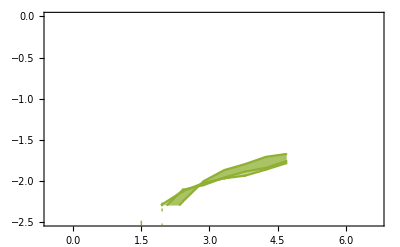

```mathematica
Show[Nf4α3LoopΔEqqbarPlot,PlotRange->{{Mc-2,Mb+2},{-2.5,0}}]
```

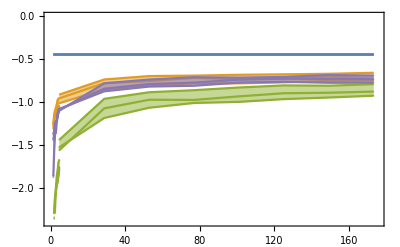

```mathematica
EqqbarNf45α3LoopPlotMQ=Show[Nf4α3LoopΔEqqbarPlot,Nf5α3LoopΔEqqbarPlot,Nf4α2LoopΔEqqbarPlot,Nf5α2LoopΔEqqbarPlot,Nf4α2LoopmΔEqqbarPlot,Nf5α2LoopmΔEqqbarPlot,Nf4α1LoopΔEqqbarPlot,Nf5α1LoopΔEqqbarPlot,PlotRange->{{0,Mt+2},{-2.4,0}},Axes->False]
```

```mathematica
Export[plotdir<>"DeltaEQQbar_vs_mQ.pdf",EqqbarNf45α3LoopPlotMQ];
```

### M_QQQ

```mathematica
MbbbLQCD=Around[14.366,Sqrt[.009^2+.020^2]]
```

14.3660.022

```mathematica
MbbbLQCD/3
```

4.7890.007

```mathematica
MbbcLQCD=Around[11.195,Sqrt[.008^2+.020^2]]
```

11.1950.022

```mathematica
MbccLQCD=Around[8.007,Sqrt[.009^2+.020^2]]
```

8.0070.022

```mathematica
McccLQCD=Around[4.796,Sqrt[.008^2+.018^2]]
```

4.7960.020

```mathematica
moops=9.46030;
```

```mathematica
mJPsi=3.096;
```

```mathematica
(* 1S0 *)
```

```mathematica
mJPsi=Around[2.9839,.0005];
```

```mathematica
moops=Around[9.46030,.00026];
```

```mathematica
mJPsi=1/2(Around[2.9839,.0005]+Around[3.096900,.000006])
```

3.040400.00025

```mathematica
moops=1/2(Around[9.46030,.00026]+Around[9.3987,.0020])
```

9.42950.0010

```mathematica
mJPsi=(Around[3.096900,.000006])
```

3.0969006

```mathematica
moops=(Around[9.46030,.00026])
```

9.460300.00026

```mathematica
McccLQCD/mJPsi
```

1.5490.006

```mathematica
mJPsi
```

3.0969006

#### LO

```mathematica
Nf4α1LoopMid
```

{0.21556,0.220566,0.22639,0.233299,0.241701,0.252265,0.266178,0.285833}

```mathematica
Nf4α1LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α1LoopBig]}]
```

{-0.0344670.000017,-0.0364380.000018,-0.0388520.000020,-0.0420010.000022,-0.0463650.000022,-0.0521260.000029,-0.0609240.000033,-0.075090.00004}

```mathematica
Nf4α1LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α1LoopMid]}]
```

{-0.0220920.000013,-0.0231680.000013,-0.0243600.000015,-0.0259920.000015,-0.0278250.000015,-0.0303640.000020,-0.0338120.000021,-0.0389530.000027}

```mathematica
Nf4α1LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α1LoopSmall]}]
```

{-0.0157700.000012,-0.0163450.000011,-0.0169850.000012,-0.0177660.000013,-0.0187380.000014,-0.0199600.000015,-0.0219260.000017,-0.0243730.000021}

```mathematica
ΔEqqqOα2=Nf4α1LoopΔEqqbarMid/Nf4α1LoopMid^2
```

{-0.444442622,-0.444446221,-0.444446220,-0.444446218,-0.444444517,-0.444445816,-0.444444214,-0.444445212}

```mathematica
Nf4α1LoopΔEqqqMid/Nf4α1LoopMid^2
```

{-0.475450.00027,-0.476220.00026,-0.475300.00029,-0.477550.00027,-0.476300.00026,-0.477150.00032,-0.477230.00030,-0.476780.00033}

```mathematica
ΔEqqqOα2WD=3/2Nf4α1LoopΔEqqbarMid/Nf4α1LoopMid^2
```

{-0.666663832,-0.666669331,-0.666669329,-0.666669328,-0.666666726,-0.666668624,-0.666666321,-0.666667918}

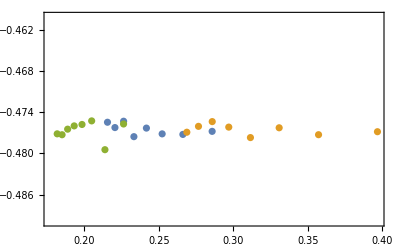

```mathematica
EqqqNf4α1LoopPlot=Show[ListPlot[{Table[{Nf4α1LoopMid[[i]],Nf4α1LoopΔEqqqMid[[i]]/Nf4α1LoopMid[[i]]^2},{i,1,Length[Nf4α1LoopMid]}],Table[{Nf4α1LoopBig[[i]],Nf4α1LoopΔEqqqBig[[i]]/Nf4α1LoopBig[[i]]^2},{i,1,Length[Nf4α1LoopBig]}],Table[{Nf4α1LoopSmall[[i]],Nf4α1LoopΔEqqqSmall[[i]]/Nf4α1LoopSmall[[i]]^2},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->{-.49,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

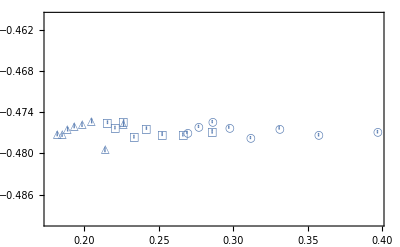

```mathematica
EqqqNf4α1LoopPlot=Show[ListPlot[{Table[{Nf4α1LoopMid[[i]],Nf4α1LoopΔEqqqMid[[i]]/Nf4α1LoopMid[[i]]^2},{i,1,Length[Nf4α1LoopMid]}],Table[{Nf4α1LoopBig[[i]],Nf4α1LoopΔEqqqBig[[i]]/Nf4α1LoopBig[[i]]^2},{i,1,Length[Nf4α1LoopBig]}],Table[{Nf4α1LoopSmall[[i]],Nf4α1LoopΔEqqqSmall[[i]]/Nf4α1LoopSmall[[i]]^2},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->{-.49,-.46},PlotLegends->Placed[αLegendLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][1]},PlotStyle->{ColorData[97][1]}],Graphics[{Black,Line[{{0,ΔEqqbarOα2Exact},{1,ΔEqqbarOα2Exact}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["\\text{LO}",Magnification->1.2]]
```

```mathematica
Export[plotdir<>"DeltaEQQQ_vs_alpha_LO.pdf",EqqqNf4α1LoopPlot];
```

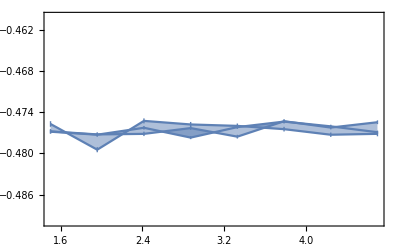

```mathematica
Nf4α1LoopΔEqqqPlot=Show[ListPlot[{Reverse@Table[{Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqMid[[i]]/Nf4α1LoopMid[[i]]^2},{i,1,Length[Nf4α1LoopMid]}],Reverse@Table[{Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqBig[[i]]/Nf4α1LoopBig[[i]]^2},{i,1,Length[Nf4α1LoopBig]}],Reverse@Table[{Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqSmall[[i]]/Nf4α1LoopSmall[[i]]^2},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->{{Mc,Mb},{-.49,-.46}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

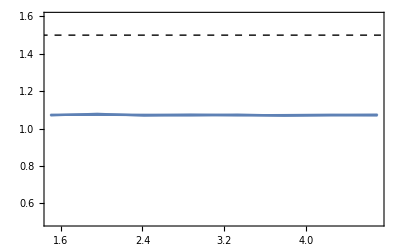

```mathematica
Nf4α1LoopΔEqqqRatioPlot=Show[ListPlot[{Reverse@Table[{Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqMid[[i]]/Nf4α1LoopΔEqqbarMid[[i]]},{i,1,Length[Nf4α1LoopMid]}],Reverse@Table[{Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqBig[[i]]/Nf4α1LoopΔEqqbarBig[[i]]},{i,1,Length[Nf4α1LoopBig]}],Reverse@Table[{Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqSmall[[i]]/Nf4α1LoopΔEqqbarSmall[[i]]},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->{{Mc,Mb},{.5,1.6}},Joined->True,Filling->{{2->{3}},{1->{2}}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

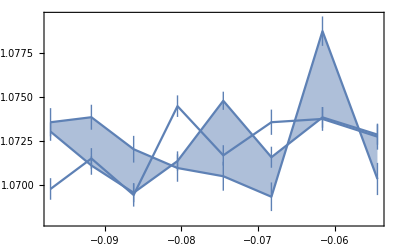

```mathematica
Nf4α1LoopΔEqqbarVsPlot=Show[ListPlot[{Table[{Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqMid[[i]]/Nf4α1LoopΔEqqbarMid[[i]]},{i,1,Length[Nf4α1LoopMid]}],Table[{Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqBig[[i]]/Nf4α1LoopΔEqqbarBig[[i]]},{i,1,Length[Nf4α1LoopBig]}],Table[{Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqSmall[[i]]/Nf4α1LoopΔEqqbarSmall[[i]]},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\Delta E_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

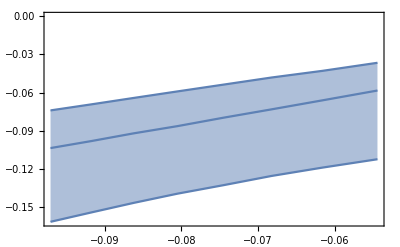

```mathematica
Nf4α1LoopΔEqqbarVsPlot=Show[ListPlot[{Table[{Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqMid[[i]]Nf4α1LoopmQ[[i]]},{i,1,Length[Nf4α1LoopMid]}],Table[{Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqBig[[i]]Nf4α1LoopmQ[[i]]},{i,1,Length[Nf4α1LoopBig]}],Table[{Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],Nf4α1LoopΔEqqqSmall[[i]]Nf4α1LoopmQ[[i]]},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\Delta E_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}\\text{ [GeV]}"]}]
```

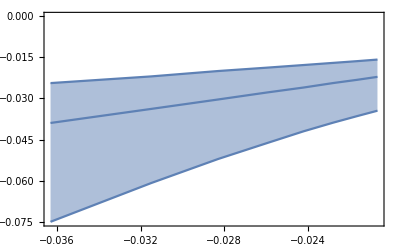

```mathematica
Nf4α1LoopΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{Nf4α1LoopΔEqqbarMid[[i]],Nf4α1LoopΔEqqqMid[[i]]},{i,1,Length[Nf4α1LoopMid]}],Reverse@Table[{Nf4α1LoopΔEqqbarMid[[i]],Nf4α1LoopΔEqqqBig[[i]]},{i,1,Length[Nf4α1LoopBig]}],Reverse@Table[{Nf4α1LoopΔEqqbarMid[[i]],Nf4α1LoopΔEqqqSmall[[i]]},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]}]
```

```mathematica
Nf5α1LoopMid
```

{0.11989,0.122221,0.125074,0.128711,0.133637,0.141032,0.154751,0.21556}

```mathematica
Nf5α1LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α1LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α1LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α1LoopBig]}]
```

{-0.008470033,-0.008870234,-0.009304332,-0.0099774,-0.0108195,-0.0122216,-0.0151087,-0.0344940.000017}

```mathematica
Nf5α1LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α1LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α1LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α1LoopMid]}]
```

{-0.006861134,-0.007112831,-0.007478232,-0.007889129,-0.0085234,-0.0094964,-0.0114106,-0.0221330.000014}

```mathematica
Nf5α1LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α1LoopSmall]}]
```

{-0.005654427,-0.005874632,-0.006089727,-0.006410234,-0.006884835,-0.0075654,-0.0089465,-0.0157780.000012}

```mathematica
ΔEqqqOα2=Nf5α1LoopΔEqqbarMid/Nf5α1LoopMid^2
```

{-0.4444487,-0.4444467,-0.4444456,-0.4444476,-0.4444436,-0.4444475,-0.4444464,-0.444442622}

```mathematica
Nf5α1LoopΔEqqqMid/Nf5α1LoopMid^2
```

{-0.477340.00024,-0.476160.00021,-0.478040.00020,-0.476210.00018,-0.477230.00022,-0.477450.00020,-0.476460.00026,-0.476320.00030}

```mathematica
ΔEqqqOα2WD=3/2Nf5α1LoopΔEqqbarMid/Nf5α1LoopMid^2
```

{-0.6666720.000010,-0.6666700.000010,-0.66666710,-0.6666719,-0.6666648,-0.6666708,-0.6666696,-0.666663832}

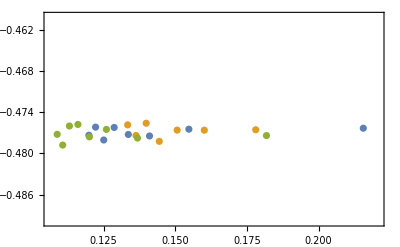

```mathematica
EqqqNf5α1LoopPlot=Show[ListPlot[{Table[{Nf5α1LoopMid[[i]],Nf5α1LoopΔEqqqMid[[i]]/Nf5α1LoopMid[[i]]^2},{i,1,Length[Nf5α1LoopMid]}],Table[{Nf5α1LoopBig[[i]],Nf5α1LoopΔEqqqBig[[i]]/Nf5α1LoopBig[[i]]^2},{i,1,Length[Nf5α1LoopBig]}],Table[{Nf5α1LoopSmall[[i]],Nf5α1LoopΔEqqqSmall[[i]]/Nf5α1LoopSmall[[i]]^2},{i,1,Length[Nf5α1LoopSmall]}]},PlotRange->{-.49,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

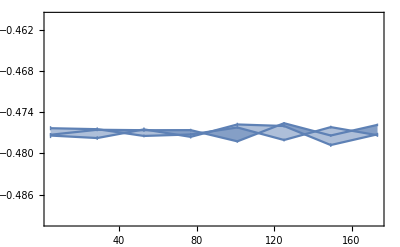

```mathematica
Nf5α1LoopΔEqqqPlot=Show[ListPlot[{Reverse@Table[{Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqqMid[[i]]/Nf5α1LoopMid[[i]]^2},{i,1,Length[Nf5α1LoopMid]}],Reverse@Table[{Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqqBig[[i]]/Nf5α1LoopBig[[i]]^2},{i,1,Length[Nf5α1LoopBig]}],Reverse@Table[{Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqqSmall[[i]]/Nf5α1LoopSmall[[i]]^2},{i,1,Length[Nf5α1LoopSmall]}]},PlotRange->{{Mb,Mt},{-.49,-.46}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

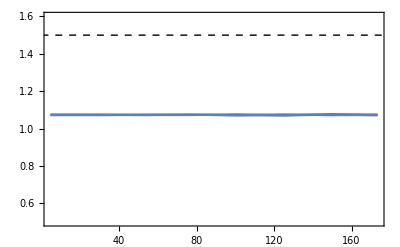

```mathematica
Nf5α1LoopΔEqqqRatioPlot=Show[ListPlot[{Reverse@Table[{Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqqMid[[i]]/Nf5α1LoopΔEqqbarMid[[i]]},{i,1,Length[Nf5α1LoopMid]}],Reverse@Table[{Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqqBig[[i]]/Nf5α1LoopΔEqqbarBig[[i]]},{i,1,Length[Nf5α1LoopBig]}],Reverse@Table[{Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqqSmall[[i]]/Nf5α1LoopΔEqqbarSmall[[i]]},{i,1,Length[Nf5α1LoopSmall]}]},PlotRange->{{Mb,Mt},{.5,1.6}},Joined->True,Filling->{{2->{3}},{1->{2}}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

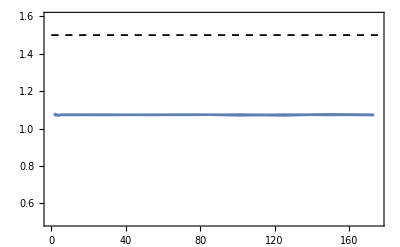

```mathematica
Show[Nf4α1LoopΔEqqqRatioPlot,Nf5α1LoopΔEqqqRatioPlot,PlotRange->{{Mc-2,Mt+2},{.5,1.6}}]
```

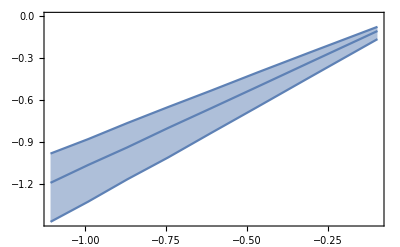

```mathematica
Nf5α1LoopΔEqqbarVsPlot=Show[ListPlot[{Table[{Nf5α1LoopΔEqqbarMid[[i]]Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqqMid[[i]]Nf5α1LoopmQ[[i]]},{i,1,Length[Nf5α1LoopMid]}],Table[{Nf5α1LoopΔEqqbarMid[[i]]Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqqBig[[i]]Nf5α1LoopmQ[[i]]},{i,1,Length[Nf5α1LoopBig]}],Table[{Nf5α1LoopΔEqqbarMid[[i]]Nf5α1LoopmQ[[i]],Nf5α1LoopΔEqqqSmall[[i]]Nf5α1LoopmQ[[i]]},{i,1,Length[Nf5α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\Delta E_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}\\text{ [GeV]}"]}]
```

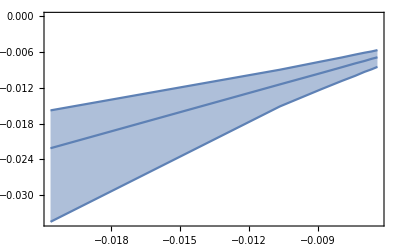

```mathematica
Nf5α1LoopΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{Nf5α1LoopΔEqqbarMid[[i]],Nf5α1LoopΔEqqqMid[[i]]},{i,1,Length[Nf5α1LoopMid]}],Reverse@Table[{Nf5α1LoopΔEqqbarMid[[i]],Nf5α1LoopΔEqqqBig[[i]]},{i,1,Length[Nf5α1LoopBig]}],Reverse@Table[{Nf5α1LoopΔEqqbarMid[[i]],Nf5α1LoopΔEqqqSmall[[i]]},{i,1,Length[Nf5α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]}]
```

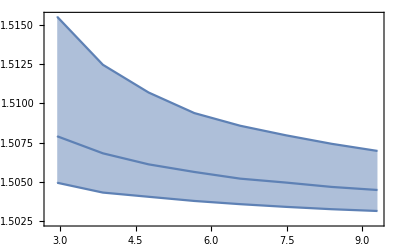

```mathematica
Nf4α1LoopΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{2Nf4α1LoopmQ[[i]]+Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],(3+Nf4α1LoopΔEqqqMid[[i]])/(2+Nf4α1LoopΔEqqbarMid[[i]])},{i,1,Length[Nf4α1LoopMid]}],Reverse@Table[{2Nf4α1LoopmQ[[i]]+Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],(3+Nf4α1LoopΔEqqqBig[[i]])/(2+Nf4α1LoopΔEqqbarBig[[i]])},{i,1,Length[Nf4α1LoopBig]}],Reverse@Table[{2Nf4α1LoopmQ[[i]]+Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],(3+Nf4α1LoopΔEqqqSmall[[i]])/(2+Nf4α1LoopΔEqqbarSmall[[i]])},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

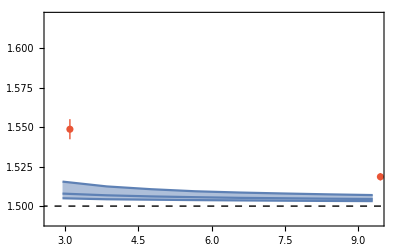

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->ColorData[97][0]],PlotRange->{{1.8Mc,2Mb},{1.49,1.62}},Axes->False]
```

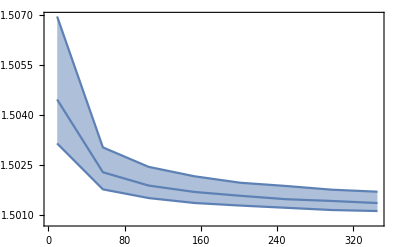

```mathematica
Nf5α1LoopΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{2Nf5α1LoopmQ[[i]]+Nf5α1LoopΔEqqbarMid[[i]]Nf5α1LoopmQ[[i]],(3+Nf5α1LoopΔEqqqMid[[i]])/(2+Nf5α1LoopΔEqqbarMid[[i]])},{i,1,Length[Nf5α1LoopMid]}],Reverse@Table[{2Nf5α1LoopmQ[[i]]+Nf5α1LoopΔEqqbarMid[[i]]Nf5α1LoopmQ[[i]],(3+Nf5α1LoopΔEqqqBig[[i]])/(2+Nf5α1LoopΔEqqbarBig[[i]])},{i,1,Length[Nf5α1LoopBig]}],Reverse@Table[{2Nf5α1LoopmQ[[i]]+Nf5α1LoopΔEqqbarMid[[i]]Nf5α1LoopmQ[[i]],(3+Nf5α1LoopΔEqqqSmall[[i]])/(2+Nf5α1LoopΔEqqbarSmall[[i]])},{i,1,Length[Nf5α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

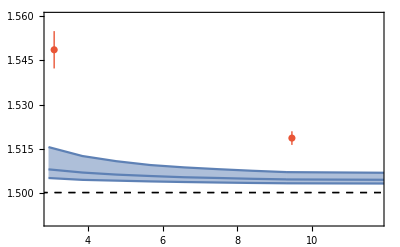

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot,Nf5α1LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->ColorData[97][0]],PlotRange->{{2Mc,2.5Mb},{1.49,1.56}},Axes->False]
```

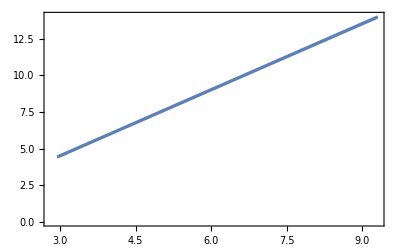

```mathematica
Nf4α1LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Reverse@Table[{2Nf4α1LoopmQ[[i]]+Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],(3Nf4α1LoopmQ[[i]]+Nf4α1LoopΔEqqqMid[[i]]Nf4α1LoopmQ[[i]])},{i,1,Length[Nf4α1LoopMid]}],Reverse@Table[{2Nf4α1LoopmQ[[i]]+Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],(3Nf4α1LoopmQ[[i]]+Nf4α1LoopmQ[[i]]Nf4α1LoopΔEqqqBig[[i]])},{i,1,Length[Nf4α1LoopBig]}],Reverse@Table[{2Nf4α1LoopmQ[[i]]+Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],(3Nf4α1LoopmQ[[i]]+Nf4α1LoopmQ[[i]]Nf4α1LoopΔEqqqSmall[[i]])},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}]
```

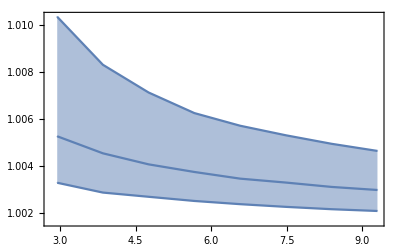

```mathematica
Nf4α1LoopΔEqqbarVsPlot23=Show[ListPlot[{Reverse@Table[{2Nf4α1LoopmQ[[i]]+Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],2/3(3+Nf4α1LoopΔEqqqMid[[i]])/(2+Nf4α1LoopΔEqqbarMid[[i]])},{i,1,Length[Nf4α1LoopMid]}],Reverse@Table[{2Nf4α1LoopmQ[[i]]+Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],2/3(3+Nf4α1LoopΔEqqqBig[[i]])/(2+Nf4α1LoopΔEqqbarBig[[i]])},{i,1,Length[Nf4α1LoopBig]}],Reverse@Table[{2Nf4α1LoopmQ[[i]]+Nf4α1LoopΔEqqbarMid[[i]]Nf4α1LoopmQ[[i]],2/3(3+Nf4α1LoopΔEqqqSmall[[i]])/(2+Nf4α1LoopΔEqqbarSmall[[i]])},{i,1,Length[Nf4α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["(2/3) M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

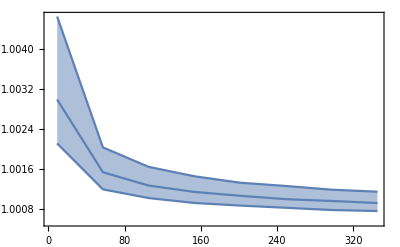

```mathematica
Nf5α1LoopΔEqqbarVsPlot23=Show[ListPlot[{Reverse@Table[{2Nf5α1LoopmQ[[i]]+Nf5α1LoopΔEqqbarMid[[i]]Nf5α1LoopmQ[[i]],2/3(3+Nf5α1LoopΔEqqqMid[[i]])/(2+Nf5α1LoopΔEqqbarMid[[i]])},{i,1,Length[Nf5α1LoopMid]}],Reverse@Table[{2Nf5α1LoopmQ[[i]]+Nf5α1LoopΔEqqbarMid[[i]]Nf5α1LoopmQ[[i]],2/3(3+Nf5α1LoopΔEqqqBig[[i]])/(2+Nf5α1LoopΔEqqbarBig[[i]])},{i,1,Length[Nf5α1LoopBig]}],Reverse@Table[{2Nf5α1LoopmQ[[i]]+Nf5α1LoopΔEqqbarMid[[i]]Nf5α1LoopmQ[[i]],2/3(3+Nf5α1LoopΔEqqqSmall[[i]])/(2+Nf5α1LoopΔEqqbarSmall[[i]])},{i,1,Length[Nf5α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["(2/3) M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

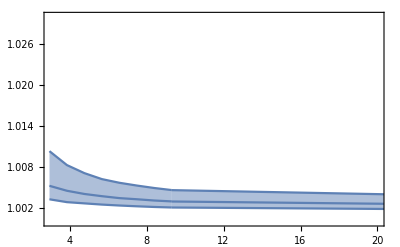

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot23,Nf5α1LoopΔEqqbarVsPlot23,PlotRange->{{3,20},{1,1.03}}]
```

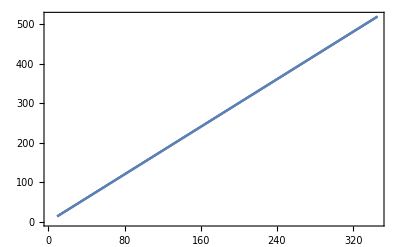

```mathematica
Nf5α1LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Reverse@Table[{2Nf5α1LoopmQ[[i]]+Nf5α1LoopΔEqqbarMid[[i]]Nf5α1LoopmQ[[i]],(3Nf5α1LoopmQ[[i]]+Nf5α1LoopΔEqqqMid[[i]]Nf5α1LoopmQ[[i]])},{i,1,Length[Nf5α1LoopMid]}],Reverse@Table[{2Nf5α1LoopmQ[[i]]+Nf5α1LoopΔEqqbarMid[[i]]Nf5α1LoopmQ[[i]],(3Nf5α1LoopmQ[[i]]+Nf5α1LoopmQ[[i]]Nf5α1LoopΔEqqqBig[[i]])},{i,1,Length[Nf5α1LoopBig]}],Reverse@Table[{2Nf5α1LoopmQ[[i]]+Nf5α1LoopΔEqqbarMid[[i]]Nf5α1LoopmQ[[i]],(3Nf5α1LoopmQ[[i]]+Nf5α1LoopmQ[[i]]Nf5α1LoopΔEqqqSmall[[i]])},{i,1,Length[Nf5α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}]
```

#### NLO

```mathematica
Nf4α2LoopMid
```

{0.229421,0.235729,0.243152,0.252078,0.263112,0.277271,0.29642,0.324475}

```mathematica
Nf4α2LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α2LoopBig]}]
```

{-0.108770.00034,-0.11770.0004,-0.13550.0004,-0.14980.0006,-0.18600.0006,-0.21680.0009,-0.29470.0014,-0.49520.0023}

```mathematica
Nf4α2LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α2LoopMid]}]
```

{-0.065710.00030,-0.068060.00035,-0.07530.0004,-0.08180.0005,-0.09220.0005,-0.10890.0006,-0.12910.0008,-0.16380.0012}

```mathematica
Nf4α2LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α2LoopSmall]}]
```

{-0.043300.00032,-0.045870.00033,-0.048670.00033,-0.05250.0004,-0.05900.0004,-0.06460.0005,-0.07310.0007,-0.08870.0008}

```mathematica
ΔEqqqOα2=Nf4α2LoopΔEqqbarMid/Nf4α2LoopMid^2
```

{-1.0390.006,-1.0720.006,-1.0540.006,-1.0970.007,-1.1470.007,-1.1650.007,-1.2060.008,-1.3110.009}

```mathematica
Nf4α2LoopΔEqqqMid/Nf4α2LoopMid^2
```

{-1.2490.006,-1.2250.006,-1.2730.007,-1.2880.007,-1.3320.008,-1.4170.008,-1.4690.009,-1.5560.011}

```mathematica
ΔEqqqOα2WD=3/2Nf4α2LoopΔEqqbarMid/Nf4α2LoopMid^2
```

{-1.5580.008,-1.6080.009,-1.5810.009,-1.6460.011,-1.7200.011,-1.7480.011,-1.8090.012,-1.9660.013}

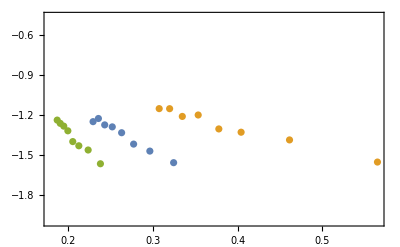

```mathematica
EqqqNf4α2LoopPlot=Show[ListPlot[{Table[{Nf4α2LoopMid[[i]],Nf4α2LoopΔEqqqMid[[i]]/Nf4α2LoopMid[[i]]^2},{i,1,Length[Nf4α2LoopMid]}],Table[{Nf4α2LoopBig[[i]],Nf4α2LoopΔEqqqBig[[i]]/Nf4α2LoopBig[[i]]^2},{i,1,Length[Nf4α2LoopBig]}],Table[{Nf4α2LoopSmall[[i]],Nf4α2LoopΔEqqqSmall[[i]]/Nf4α2LoopSmall[[i]]^2},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->{-2,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

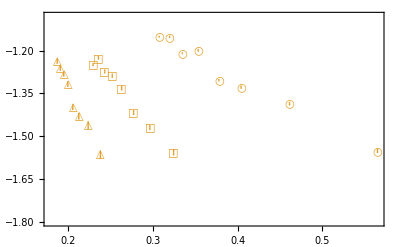

```mathematica
EqqqNf4α2LoopPlot=Show[ListPlot[{Table[{Nf4α2LoopMid[[i]],Nf4α2LoopΔEqqqMid[[i]]/Nf4α2LoopMid[[i]]^2},{i,1,Length[Nf4α2LoopMid]}],Table[{Nf4α2LoopBig[[i]],Nf4α2LoopΔEqqqBig[[i]]/Nf4α2LoopBig[[i]]^2},{i,1,Length[Nf4α2LoopBig]}],Table[{Nf4α2LoopSmall[[i]],Nf4α2LoopΔEqqqSmall[[i]]/Nf4α2LoopSmall[[i]]^2},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->{-1.5 1.2,-.9 1.2},PlotLegends->Placed[αLegendNLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][2]},PlotStyle->{ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["\\text{NLO}",Magnification->1.2]]
```

```mathematica
Export[plotdir<>"DeltaEQQQ_vs_alpha_NLO.pdf",EqqqNf4α2LoopPlot];
```

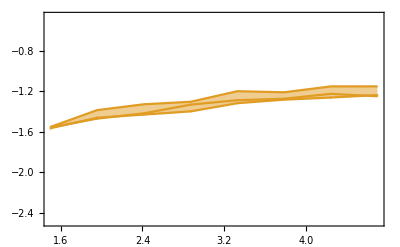

```mathematica
Nf4α2LoopΔEqqqPlot=Show[ListPlot[{Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqqMid[[i]]/Nf4α2LoopMid[[i]]^2},{i,1,Length[Nf4α2LoopMid]}],Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqqBig[[i]]/Nf4α2LoopBig[[i]]^2},{i,1,Length[Nf4α2LoopBig]}],Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqqSmall[[i]]/Nf4α2LoopSmall[[i]]^2},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->{{Mc,Mb},{-2.49,-.46}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

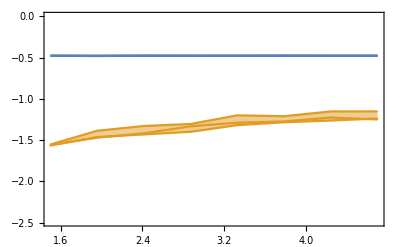

```mathematica
Show[Nf4α2LoopΔEqqqPlot,Nf4α1LoopΔEqqqPlot,PlotRange->{-2.49,0}]
```

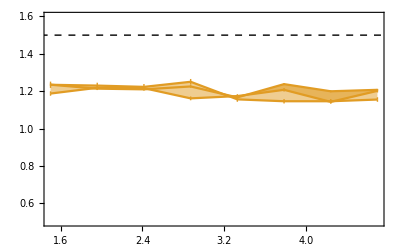

```mathematica
Nf4α2LoopΔEqqqRatioPlot=Show[ListPlot[{Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqqMid[[i]]/Nf4α2LoopΔEqqbarMid[[i]]},{i,1,Length[Nf4α2LoopMid]}],Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqqBig[[i]]/Nf4α2LoopΔEqqbarBig[[i]]},{i,1,Length[Nf4α2LoopBig]}],Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqqSmall[[i]]/Nf4α2LoopΔEqqbarSmall[[i]]},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->{{Mc,Mb},{.5,1.6}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

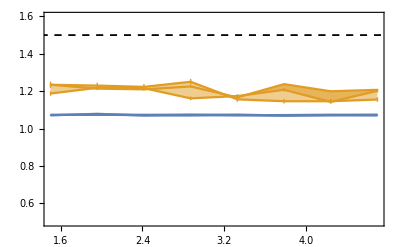

```mathematica
Show[Nf4α2LoopΔEqqqRatioPlot,Nf4α1LoopΔEqqqRatioPlot]
```

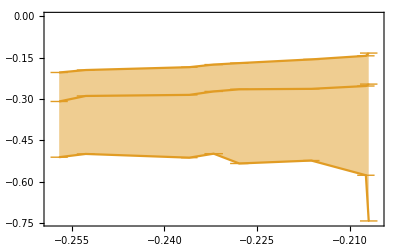

```mathematica
Nf4α2LoopΔEqqbarVsPlot=Show[ListPlot[{Table[{Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqqMid[[i]]Nf4α2LoopmQ[[i]]},{i,1,Length[Nf4α2LoopMid]}],Table[{Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqqBig[[i]]Nf4α2LoopmQ[[i]]},{i,1,Length[Nf4α2LoopBig]}],Table[{Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],Nf4α2LoopΔEqqqSmall[[i]]Nf4α2LoopmQ[[i]]},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\Delta E_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}\\text{ [GeV]}"]}]
```

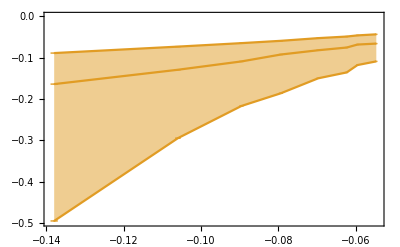

```mathematica
Nf4α2LoopΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{Nf4α2LoopΔEqqbarMid[[i]],Nf4α2LoopΔEqqqMid[[i]]},{i,1,Length[Nf4α2LoopMid]}],Reverse@Table[{Nf4α2LoopΔEqqbarMid[[i]],Nf4α2LoopΔEqqqBig[[i]]},{i,1,Length[Nf4α2LoopBig]}],Reverse@Table[{Nf4α2LoopΔEqqbarMid[[i]],Nf4α2LoopΔEqqqSmall[[i]]},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]}]
```

```mathematica
Show[Nf4α2LoopΔEqqbarVsPlot,Nf4α1LoopΔEqqbarVsPlot]
```

-Graphics-

```mathematica
Nf5α2LoopMid
```

{0.120381,0.122841,0.125862,0.129728,0.134994,0.14296,0.157949,0.229421}

```mathematica
Nf5α2LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α2LoopBig]}]
```

{-0.0138150.000019,-0.0144830.000026,-0.0155660.000022,-0.0168030.000026,-0.0188980.000032,-0.0221430.000035,-0.028790.00006,-0.102290.00035}

```mathematica
Nf5α2LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α2LoopMid]}]
```

{-0.0120640.000030,-0.0125140.000030,-0.0132580.000034,-0.014300.00004,-0.015630.00005,-0.018120.00006,-0.023120.00007,-0.061380.00034}

```mathematica
Nf5α2LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α2LoopSmall]}]
```

{-0.010290.00004,-0.010710.00004,-0.011180.00004,-0.011730.00004,-0.013320.00007,-0.015120.00006,-0.019010.00009,-0.042060.00028}

```mathematica
ΔEqqqOα2=Nf5α2LoopΔEqqbarMid/Nf5α2LoopMid^2
```

{-0.72570.0018,-0.70250.0018,-0.72640.0020,-0.73330.0021,-0.71770.0022,-0.75380.0022,-0.77810.0032,-0.9570.005}

```mathematica
Nf5α2LoopΔEqqqMid/Nf5α2LoopMid^2
```

{-0.83250.0021,-0.82930.0020,-0.83690.0021,-0.84950.0026,-0.85760.0025,-0.88680.0030,-0.92660.0028,-1.1660.006}

```mathematica
ΔEqqqOα2WD=3/2Nf5α2LoopΔEqqbarMid/Nf5α2LoopMid^2
```

{-1.08860.0026,-1.05380.0027,-1.08960.0029,-1.10000.0032,-1.07660.0034,-1.13070.0033,-1.1670.005,-1.4350.008}

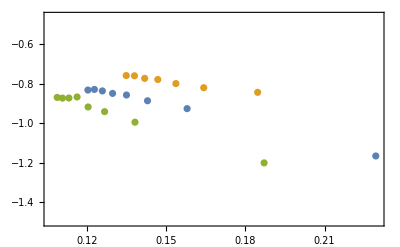

```mathematica
Eqqbarα2LoopPlot=Show[ListPlot[{Table[{Nf5α2LoopMid[[i]],Nf5α2LoopΔEqqqMid[[i]]/Nf5α2LoopMid[[i]]^2},{i,1,Length[Nf5α2LoopMid]}],Table[{Nf5α2LoopBig[[i]],Nf5α2LoopΔEqqqBig[[i]]/Nf5α2LoopBig[[i]]^2},{i,1,Length[Nf5α2LoopBig]}],Table[{Nf5α2LoopSmall[[i]],Nf5α2LoopΔEqqqSmall[[i]]/Nf5α2LoopSmall[[i]]^2},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->{-1.5,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

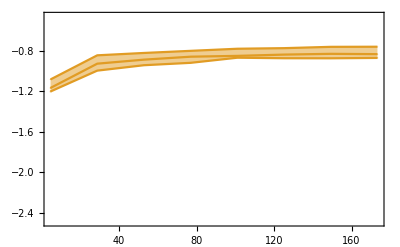

```mathematica
Nf5α2LoopΔEqqqPlot=Show[ListPlot[{Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopΔEqqqMid[[i]]/Nf5α2LoopMid[[i]]^2},{i,1,Length[Nf5α2LoopMid]}],Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopΔEqqqBig[[i]]/Nf5α2LoopBig[[i]]^2},{i,1,Length[Nf5α2LoopBig]}],Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopΔEqqqSmall[[i]]/Nf5α2LoopSmall[[i]]^2},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->{{Mb,Mt},{-2.49,-.46}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

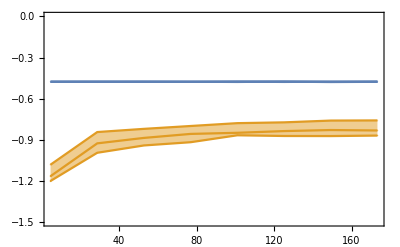

```mathematica
Show[Nf5α2LoopΔEqqqPlot,Nf5α1LoopΔEqqqPlot,PlotRange->{-1.5,0},Axes->False]
```

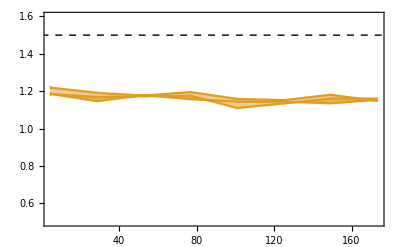

```mathematica
Nf5α2LoopΔEqqqRatioPlot=Show[ListPlot[{Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopΔEqqqMid[[i]]/Nf5α2LoopΔEqqbarMid[[i]]},{i,1,Length[Nf5α2LoopMid]}],Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopΔEqqqBig[[i]]/Nf5α2LoopΔEqqbarBig[[i]]},{i,1,Length[Nf5α2LoopBig]}],Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopΔEqqqSmall[[i]]/Nf5α2LoopΔEqqbarSmall[[i]]},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->{{Mb,Mt},{.5,1.6}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

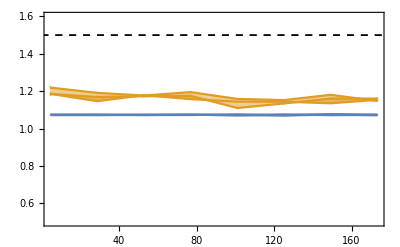

```mathematica
Show[Nf5α2LoopΔEqqqRatioPlot,Nf5α1LoopΔEqqqRatioPlot]
```

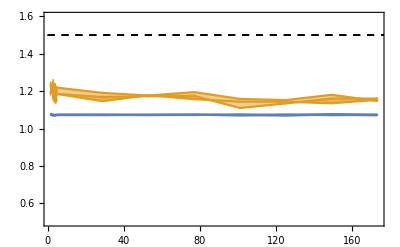

```mathematica
Show[Nf4α2LoopΔEqqqRatioPlot,Nf5α2LoopΔEqqqRatioPlot,Nf4α1LoopΔEqqqRatioPlot,Nf5α1LoopΔEqqqRatioPlot,PlotRange->{{Mc,Mt},{.5,1.6}}]
```

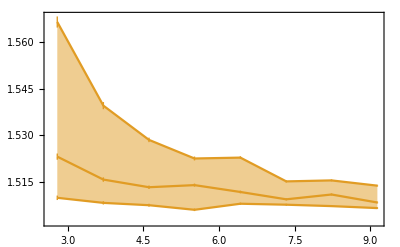

```mathematica
Nf4α2LoopΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],(3Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqqMid[[i]]Nf4α2LoopmQ[[i]])/(2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]])},{i,1,Length[Nf4α2LoopMid]}],Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],(3Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqqBig[[i]]Nf4α2LoopmQ[[i]])/(2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarBig[[i]]Nf4α2LoopmQ[[i]])},{i,1,Length[Nf4α2LoopBig]}],Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],(3Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqqSmall[[i]]Nf4α2LoopmQ[[i]])/(2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarSmall[[i]]Nf4α2LoopmQ[[i]])},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

```mathematica
Nf4α2LoopΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],(3+Nf4α2LoopΔEqqqMid[[i]])/(2+Nf4α2LoopΔEqqbarMid[[i]])},{i,1,Length[Nf4α2LoopMid]}],Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],(3+Nf4α2LoopΔEqqqBig[[i]])/(2+Nf4α2LoopΔEqqbarBig[[i]])},{i,1,Length[Nf4α2LoopBig]}],Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],(3+Nf4α2LoopΔEqqqSmall[[i]])/(2+Nf4α2LoopΔEqqbarSmall[[i]])},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
mJPsi
```

3.0969006

```mathematica
McccLQCD/mJPsi
```

1.5490.006

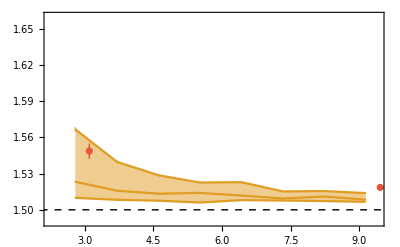

```mathematica
Show[Nf4α2LoopΔEqqbarVsPlot,ListPlot[{{mJPsi[[1]],McccLQCD/mJPsi},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->ColorData[97][0]],PlotRange->{{1.5Mc,2Mb},{1.49,1.66}},Axes->False]
```

```mathematica
Table[Series[(3+Nf5α1LoopΔEqqqBig[[ii]]  αα^2/Nf5α1LoopMid[[ii]]^2)/(2+Nf5α1LoopΔEqqbarBig[[ii]] αα^2/Nf5α1LoopMid[[ii]]^2),{αα,0,2}],{ii,1,8}]
```

{3/2+(0.118170.00012) αα^2+O[αα]^3,3/2+(0.117720.00011) αα^2+O[αα]^3,3/2+(0.119480.00010) αα^2+O[αα]^3,3/2+(0.118640.00012) αα^2+O[αα]^3,3/2+(0.120800.00013) αα^2+O[αα]^3,3/2+(0.122510.00014) αα^2+O[αα]^3,3/2+(0.125850.00014) αα^2+O[αα]^3,3/2+(0.147290.00018) αα^2+O[αα]^3}

```mathematica
Table[Series[(3+Nf5α2LoopΔEqqqBig[[ii]]  αα^2/Nf5α2LoopMid[[ii]]^2)/(2+Nf5α2LoopΔEqqbarBig[[ii]] αα^2/Nf5α2LoopMid[[ii]]^2),{αα,0,2}],{ii,1,8}]
```

{3/2+(0.14310.0012) αα^2+O[αα]^3,3/2+(0.15420.0012) αα^2+O[αα]^3,3/2+(0.15310.0012) αα^2+O[αα]^3,3/2+(0.15550.0012) αα^2+O[αα]^3,3/2+(0.15360.0015) αα^2+O[αα]^3,3/2+(0.14770.0016) αα^2+O[αα]^3,3/2+(0.17790.0018) αα^2+O[αα]^3,3/2+(0.2580.005) αα^2+O[αα]^3}

```mathematica
.12 .4^2
```

0.0192

```mathematica
.12 .2^2
```

0.0048

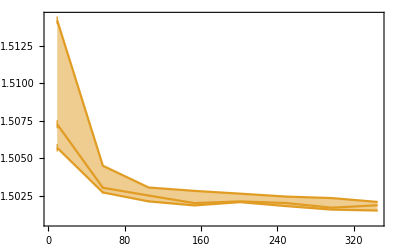

```mathematica
Nf5α2LoopΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],(3Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqqMid[[i]]Nf5α2LoopmQ[[i]])/(2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]])},{i,1,Length[Nf5α2LoopMid]}],Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],(3Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqqBig[[i]]Nf5α2LoopmQ[[i]])/(2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarBig[[i]]Nf5α2LoopmQ[[i]])},{i,1,Length[Nf5α2LoopBig]}],Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],(3Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqqSmall[[i]]Nf5α2LoopmQ[[i]])/(2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarSmall[[i]]Nf5α2LoopmQ[[i]])},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

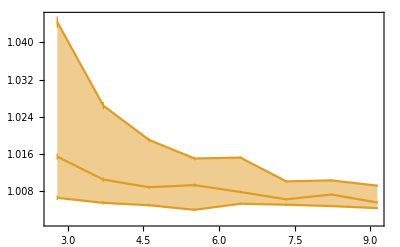

```mathematica
Nf4α2LoopΔEqqbarVsPlot23=Show[ListPlot[{Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],2/3(3Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqqMid[[i]]Nf4α2LoopmQ[[i]])/(2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]])},{i,1,Length[Nf4α2LoopMid]}],Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],2/3(3Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqqBig[[i]]Nf4α2LoopmQ[[i]])/(2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarBig[[i]]Nf4α2LoopmQ[[i]])},{i,1,Length[Nf4α2LoopBig]}],Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],2/3(3Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqqSmall[[i]]Nf4α2LoopmQ[[i]])/(2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarSmall[[i]]Nf4α2LoopmQ[[i]])},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["(2/3) M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

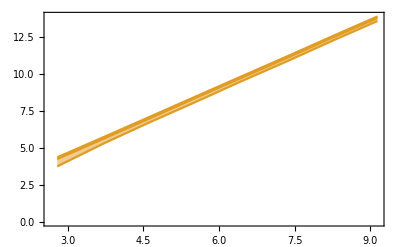

```mathematica
Nf4α2LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],(3Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqqMid[[i]]Nf4α2LoopmQ[[i]])},{i,1,Length[Nf4α2LoopMid]}],Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],(3Nf4α2LoopmQ[[i]]+Nf4α2LoopmQ[[i]]Nf4α2LoopΔEqqqBig[[i]])},{i,1,Length[Nf4α2LoopBig]}],Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],(3Nf4α2LoopmQ[[i]]+Nf4α2LoopmQ[[i]]Nf4α2LoopΔEqqqSmall[[i]])},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}]
```

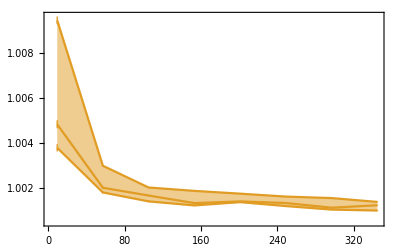

```mathematica
Nf5α2LoopΔEqqbarVsPlot23=Show[ListPlot[{Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],2/3(3Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqqMid[[i]]Nf5α2LoopmQ[[i]])/(2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]])},{i,1,Length[Nf5α2LoopMid]}],Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],2/3(3Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqqBig[[i]]Nf5α2LoopmQ[[i]])/(2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarBig[[i]]Nf5α2LoopmQ[[i]])},{i,1,Length[Nf5α2LoopBig]}],Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],2/3(3Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqqSmall[[i]]Nf5α2LoopmQ[[i]])/(2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarSmall[[i]]Nf5α2LoopmQ[[i]])},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["(2/3) M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

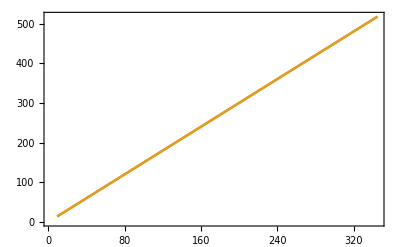

```mathematica
Nf5α2LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],(3Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqqMid[[i]]Nf5α2LoopmQ[[i]])},{i,1,Length[Nf5α2LoopMid]}],Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],(3Nf5α2LoopmQ[[i]]+Nf5α2LoopmQ[[i]]Nf5α2LoopΔEqqqBig[[i]])},{i,1,Length[Nf5α2LoopBig]}],Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],(3Nf5α2LoopmQ[[i]]+Nf5α2LoopmQ[[i]]Nf5α2LoopΔEqqqSmall[[i]])},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}]
```

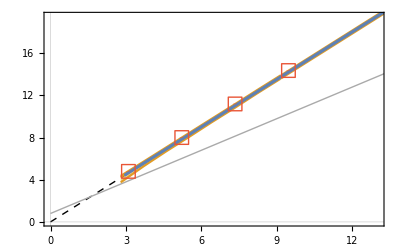

```mathematica
scale=13;Show[ListPlot[{{mJPsi,McccLQCD},{(2/3mJPsi+1/3moops),MbccLQCD},{(1/3mJPsi+2/3moops),MbbcLQCD},{moops,MbbbLQCD}},PlotStyle->Opacity[0],IntervalMarkersStyle->{Opacity[0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}],Graphics[{Black,Dashed,Line[{{0,0},{2scale,1.5  2 scale}}]}],Graphics[{Lighter[Gray],Line[{{0,.800},{1000,.800+1000}}]}],Nf4α2LoopΔEqqbarVsPlotNoRatio,Nf5α2LoopΔEqqbarVsPlotNoRatio,Nf4α1LoopΔEqqbarVsPlotNoRatio,Nf5α1LoopΔEqqbarVsPlotNoRatio,ListPlot[{{mJPsi,McccLQCD},{(2/3mJPsi+1/3moops),MbccLQCD},{(1/3mJPsi+2/3moops),MbbcLQCD},{moops,MbbbLQCD}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}],PlotRange->{{0,scale},{0,3/2 scale}},Axes->False,GridLines->{{0},{0}}]
```

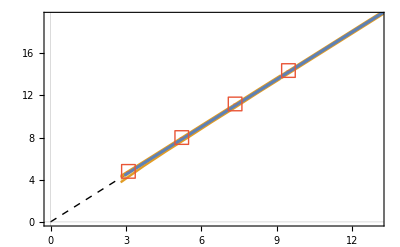

```mathematica
scale=13;Show[ListPlot[{{mJPsi,McccLQCD},{(2/3mJPsi+1/3moops),MbccLQCD},{(1/3mJPsi+2/3moops),MbbcLQCD},{moops,MbbbLQCD}},PlotStyle->Opacity[0],IntervalMarkersStyle->{Opacity[0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}],Graphics[{Black,Dashed,Line[{{0,0},{2scale,1.5  2 scale}}]}],Nf4α2LoopΔEqqbarVsPlotNoRatio,Nf5α2LoopΔEqqbarVsPlotNoRatio,Nf4α1LoopΔEqqbarVsPlotNoRatio,Nf5α1LoopΔEqqbarVsPlotNoRatio,ListPlot[{{mJPsi,McccLQCD},{(2/3mJPsi+1/3moops),MbccLQCD},{(1/3mJPsi+2/3moops),MbbcLQCD},{moops,MbbbLQCD}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}],PlotRange->{{0,scale},{0,3/2 scale}},Axes->False,GridLines->{{0},{0}}]
```

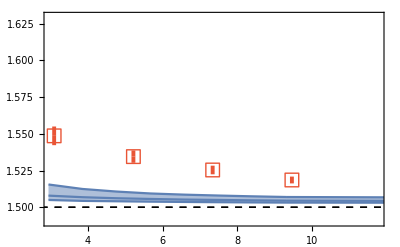

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot,Nf5α1LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold]],PlotRange->{{2Mc,2.5Mb},{1.49,1.63}},Axes->False]
```

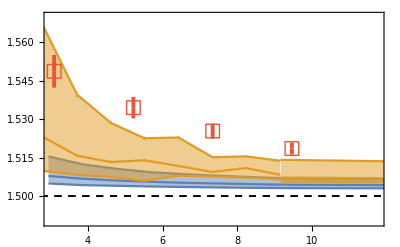

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot,Nf5α1LoopΔEqqbarVsPlot,Nf4α2LoopΔEqqbarVsPlot,Nf5α2LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold]],PlotRange->{{2Mc,2.5Mb},{1.49,1.57}},Axes->False]
```

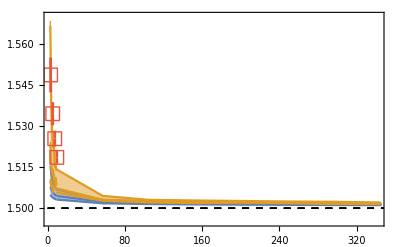

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot,Nf5α1LoopΔEqqbarVsPlot,Nf4α2LoopΔEqqbarVsPlot,Nf5α2LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.005]},PlotMarkers->Style[markerlist[[1]],14,Bold]],PlotRange->{{2Mc,1.97Mt},{1.495,1.57}},Axes->False]
```

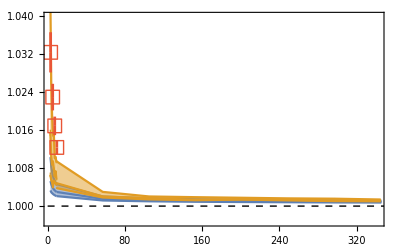

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot23,Nf5α1LoopΔEqqbarVsPlot23,Nf4α2LoopΔEqqbarVsPlot23,Nf5α2LoopΔEqqbarVsPlot23,ListPlot[{{mJPsi,2/3McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),2/3MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),2/3MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,2/3MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.005]},PlotMarkers->Style[markerlist[[1]],14,Bold]],Graphics[{Black,Dashed,Line[{{0,1},{20000,1}}]}],PlotRange->{{2Mc,1.97Mt},{2/3 1.495,2/3 1.56}},Axes->False]
```

#### mNLO

```mathematica
Nf4α2LoopMid
```

{0.229421,0.235729,0.243152,0.252078,0.263112,0.277271,0.29642,0.324475}

```mathematica
Nf4α2LoopmΔEqqqBig=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α2LoopBig]}]
```

{-0.12180.0006,-0.13790.0007,-0.15470.0007,-0.18040.0010,-0.21830.0014,-0.26110.0015,-0.37840.0028,-0.6670.005}

```mathematica
Nf4α2LoopmΔEqqqMid=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α2LoopMid]}]
```

{-0.06740.0004,-0.07350.0005,-0.07980.0005,-0.08960.0006,-0.10280.0007,-0.11520.0008,-0.14010.0011,-0.17880.0014}

```mathematica
Nf4α2LoopmΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α2LoopSmall]}]
```

{-0.045640.00032,-0.047750.00033,-0.05110.0004,-0.05480.0004,-0.06040.0005,-0.06480.0005,-0.07600.0006,-0.09110.0008}

```mathematica
ΔEqqqOα2=Nf4α2LoopmΔEqqbarMid/Nf4α2LoopMid^2
```

{-1.0780.008,-1.0910.010,-1.1700.010,-1.2060.010,-1.2550.012,-1.2730.012,-1.3810.015,-1.4380.016}

```mathematica
Nf4α2LoopmΔEqqqMid/Nf4α2LoopMid^2
```

{-1.2810.007,-1.3230.009,-1.3500.009,-1.4110.009,-1.4840.010,-1.4990.010,-1.5940.013,-1.6980.014}

```mathematica
ΔEqqqOα2WD=3/2Nf4α2LoopmΔEqqbarMid/Nf4α2LoopMid^2
```

{-1.6160.013,-1.6360.015,-1.7540.015,-1.8090.016,-1.8830.018,-1.9090.019,-2.0720.022,-2.1560.025}

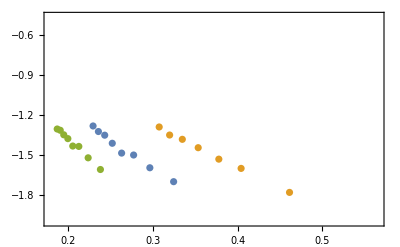

```mathematica
Show[ListPlot[{Table[{Nf4α2LoopMid[[i]],Nf4α2LoopmΔEqqqMid[[i]]/Nf4α2LoopMid[[i]]^2},{i,1,Length[Nf4α2LoopMid]}],Table[{Nf4α2LoopBig[[i]],Nf4α2LoopmΔEqqqBig[[i]]/Nf4α2LoopBig[[i]]^2},{i,1,Length[Nf4α2LoopBig]}],Table[{Nf4α2LoopSmall[[i]],Nf4α2LoopmΔEqqqSmall[[i]]/Nf4α2LoopSmall[[i]]^2},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->{-2,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

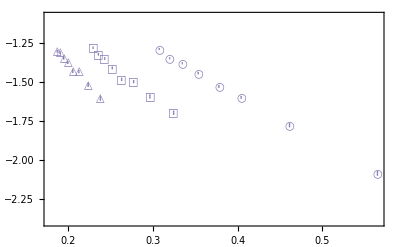

```mathematica
EqqqNf4α2LoopmPlot=Show[ListPlot[{Table[{Nf4α2LoopMid[[i]],Nf4α2LoopmΔEqqqMid[[i]]/Nf4α2LoopMid[[i]]^2},{i,1,Length[Nf4α2LoopMid]}],Table[{Nf4α2LoopBig[[i]],Nf4α2LoopmΔEqqqBig[[i]]/Nf4α2LoopBig[[i]]^2},{i,1,Length[Nf4α2LoopBig]}],Table[{Nf4α2LoopSmall[[i]],Nf4α2LoopmΔEqqqSmall[[i]]/Nf4α2LoopSmall[[i]]^2},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->{-2 1.2,-.9 1.2},PlotLegends->Placed[αLegendmNLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][5]},PlotStyle->{ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["\\text{mNLO}",Magnification->1.2]]
```

```mathematica
Export[plotdir<>"DeltaEQQQ_vs_alpha_mNLO.pdf",EqqqNf4α2LoopmPlot];
```

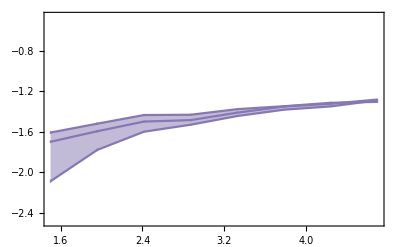

```mathematica
Nf4α2LoopmΔEqqqPlot=Show[ListPlot[{Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopmΔEqqqMid[[i]]/Nf4α2LoopMid[[i]]^2},{i,1,Length[Nf4α2LoopMid]}],Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopmΔEqqqBig[[i]]/Nf4α2LoopBig[[i]]^2},{i,1,Length[Nf4α2LoopBig]}],Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopmΔEqqqSmall[[i]]/Nf4α2LoopSmall[[i]]^2},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->{{Mc,Mb},{-2.49,-.46}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

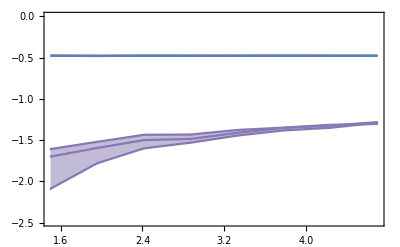

```mathematica
Show[Nf4α2LoopmΔEqqqPlot,Nf4α1LoopΔEqqqPlot,PlotRange->{-2.49,0}]
```

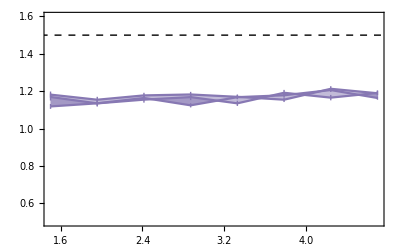

```mathematica
Nf4α2LoopmΔEqqqRatioPlot=Show[ListPlot[{Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopmΔEqqqMid[[i]]/Nf4α2LoopmΔEqqbarMid[[i]]},{i,1,Length[Nf4α2LoopMid]}],Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopmΔEqqqBig[[i]]/Nf4α2LoopmΔEqqbarBig[[i]]},{i,1,Length[Nf4α2LoopBig]}],Reverse@Table[{Nf4α2LoopmQ[[i]],Nf4α2LoopmΔEqqqSmall[[i]]/Nf4α2LoopmΔEqqbarSmall[[i]]},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->{{Mc,Mb},{.5,1.6}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

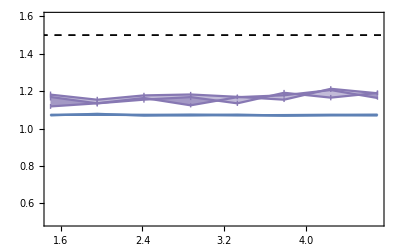

```mathematica
Show[Nf4α2LoopmΔEqqqRatioPlot,Nf4α1LoopΔEqqqRatioPlot]
```

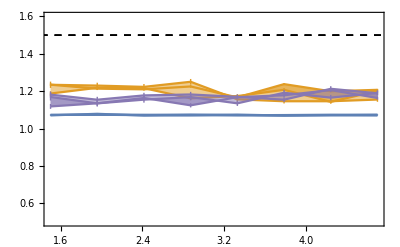

```mathematica
Show[Nf4α2LoopΔEqqqRatioPlot,Nf4α2LoopmΔEqqqRatioPlot,Nf4α1LoopΔEqqqRatioPlot]
```

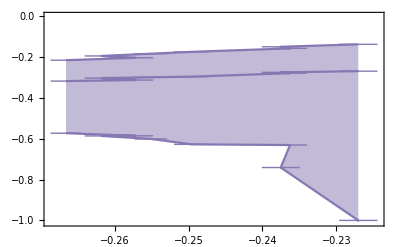

```mathematica
Nf4α2LoopmΔEqqbarVsPlot=Show[ListPlot[{Table[{Nf4α2LoopmΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],Nf4α2LoopmΔEqqqMid[[i]]Nf4α2LoopmQ[[i]]},{i,1,Length[Nf4α2LoopMid]}],Table[{Nf4α2LoopmΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],Nf4α2LoopmΔEqqqBig[[i]]Nf4α2LoopmQ[[i]]},{i,1,Length[Nf4α2LoopBig]}],Table[{Nf4α2LoopmΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],Nf4α2LoopmΔEqqqSmall[[i]]Nf4α2LoopmQ[[i]]},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\Delta E_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}\\text{ [GeV]}"]}]
```

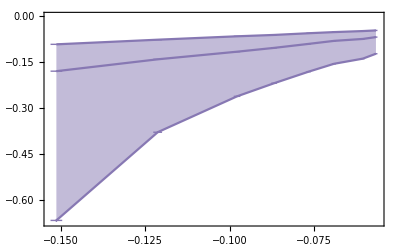

```mathematica
Nf4α2LoopmΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{Nf4α2LoopmΔEqqbarMid[[i]],Nf4α2LoopmΔEqqqMid[[i]]},{i,1,Length[Nf4α2LoopMid]}],Reverse@Table[{Nf4α2LoopmΔEqqbarMid[[i]],Nf4α2LoopmΔEqqqBig[[i]]},{i,1,Length[Nf4α2LoopBig]}],Reverse@Table[{Nf4α2LoopmΔEqqbarMid[[i]],Nf4α2LoopmΔEqqqSmall[[i]]},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]}]
```

```mathematica
Show[Nf4α2LoopmΔEqqbarVsPlot,Nf4α1LoopΔEqqbarVsPlot]
```

-Graphics-

```mathematica
Nf5α2LoopMid
```

{0.120381,0.122841,0.125862,0.129728,0.134994,0.14296,0.157949,0.229421}

```mathematica
Nf5α2LoopmΔEqqqBig=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α2LoopBig]}]
```

{-0.0141990.000031,-0.0150100.000031,-0.0162250.000035,-0.017380.00005,-0.019570.00005,-0.023070.00007,-0.031040.00011,-0.11390.0006}

```mathematica
Nf5α2LoopmΔEqqqMid=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α2LoopMid]}]
```

{-0.0120820.000031,-0.012880.00004,-0.013630.00005,-0.014430.00005,-0.016020.00006,-0.018110.00007,-0.024090.00010,-0.06430.0004}

```mathematica
Nf5α2LoopmΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α2LoopSmall]}]
```

{-0.010370.00004,-0.010820.00004,-0.011510.00004,-0.012080.00005,-0.013270.00006,-0.015380.00007,-0.018940.00009,-0.042830.00028}

```mathematica
ΔEqqqOα2=Nf5α2LoopmΔEqqbarMid/Nf5α2LoopMid^2
```

{-0.73300.0027,-0.72990.0028,-0.72720.0028,-0.73880.0031,-0.77280.0034,-0.78980.0035,-0.8440.004,-1.0900.007}

```mathematica
Nf5α2LoopmΔEqqqMid/Nf5α2LoopMid^2
```

{-0.83370.0022,-0.85370.0027,-0.86050.0029,-0.85750.0029,-0.87890.0032,-0.88590.0033,-0.9660.004,-1.2210.008}

```mathematica
ΔEqqqOα2WD=3/2Nf5α2LoopmΔEqqbarMid/Nf5α2LoopMid^2
```

{-1.0990.004,-1.0950.004,-1.0910.004,-1.1080.005,-1.1590.005,-1.1850.005,-1.2660.006,-1.6350.011}

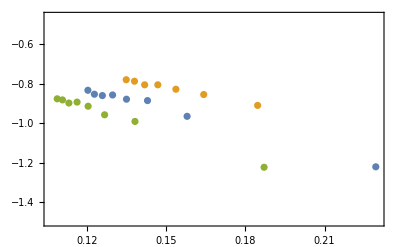

```mathematica
EqqqNf4α2LoopmPlot=Show[ListPlot[{Table[{Nf5α2LoopMid[[i]],Nf5α2LoopmΔEqqqMid[[i]]/Nf5α2LoopMid[[i]]^2},{i,1,Length[Nf5α2LoopMid]}],Table[{Nf5α2LoopBig[[i]],Nf5α2LoopmΔEqqqBig[[i]]/Nf5α2LoopBig[[i]]^2},{i,1,Length[Nf5α2LoopBig]}],Table[{Nf5α2LoopSmall[[i]],Nf5α2LoopmΔEqqqSmall[[i]]/Nf5α2LoopSmall[[i]]^2},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->{-1.5,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

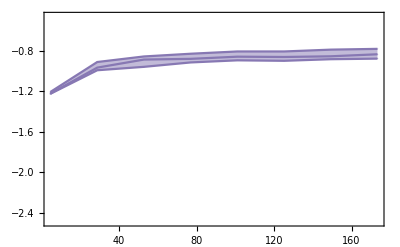

```mathematica
Nf5α2LoopmΔEqqqPlot=Show[ListPlot[{Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopmΔEqqqMid[[i]]/Nf5α2LoopMid[[i]]^2},{i,1,Length[Nf5α2LoopMid]}],Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopmΔEqqqBig[[i]]/Nf5α2LoopBig[[i]]^2},{i,1,Length[Nf5α2LoopBig]}],Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopmΔEqqqSmall[[i]]/Nf5α2LoopSmall[[i]]^2},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->{{Mb,Mt},{-2.49,-.46}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

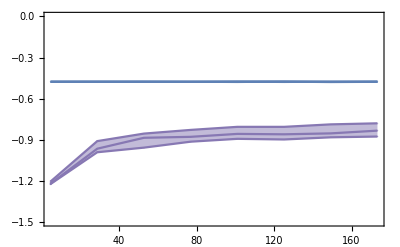

```mathematica
Show[Nf5α2LoopmΔEqqqPlot,Nf5α1LoopΔEqqqPlot,PlotRange->{-1.5,0},Axes->False]
```

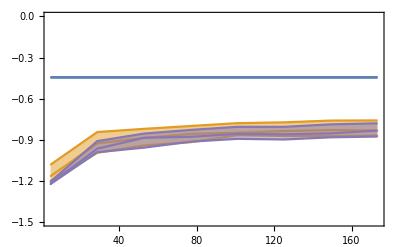

```mathematica
Show[Nf5α2LoopΔEqqqPlot,Nf5α2LoopmΔEqqqPlot,Nf5α1LoopΔEqqbarPlot,PlotRange->{-1.5,0},Axes->False]
```

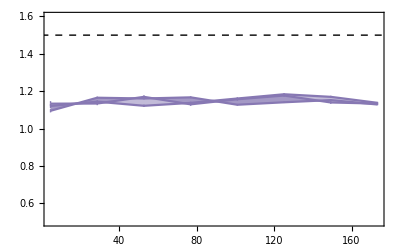

```mathematica
Nf5α2LoopmΔEqqqRatioPlot=Show[ListPlot[{Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopmΔEqqqMid[[i]]/Nf5α2LoopmΔEqqbarMid[[i]]},{i,1,Length[Nf5α2LoopMid]}],Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopmΔEqqqBig[[i]]/Nf5α2LoopmΔEqqbarBig[[i]]},{i,1,Length[Nf5α2LoopBig]}],Reverse@Table[{Nf5α2LoopmQ[[i]],Nf5α2LoopmΔEqqqSmall[[i]]/Nf5α2LoopmΔEqqbarSmall[[i]]},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->{{Mb,Mt},{.5,1.6}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

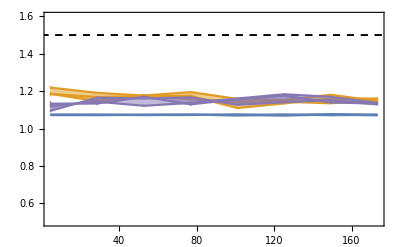

```mathematica
Show[Nf5α2LoopΔEqqqRatioPlot,Nf5α2LoopmΔEqqqRatioPlot,Nf5α1LoopΔEqqqRatioPlot]
```

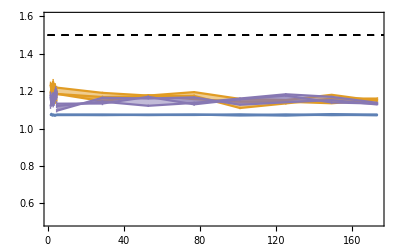

```mathematica
Show[Nf4α2LoopΔEqqqRatioPlot,Nf5α2LoopΔEqqqRatioPlot,Nf4α2LoopmΔEqqqRatioPlot,Nf5α2LoopmΔEqqqRatioPlot,Nf4α1LoopΔEqqqRatioPlot,Nf5α1LoopΔEqqqRatioPlot,PlotRange->{{Mc,Mt},{.5,1.6}}]
```

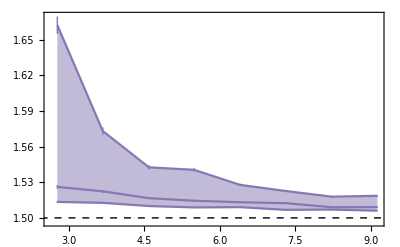

```mathematica
Nf4α2LoopmΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopmΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],(3Nf4α2LoopmQ[[i]]+Nf4α2LoopmΔEqqqMid[[i]]Nf4α2LoopmQ[[i]])/(2Nf4α2LoopmQ[[i]]+Nf4α2LoopmΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]])},{i,1,Length[Nf4α2LoopMid]}],Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopmΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],(3Nf4α2LoopmQ[[i]]+Nf4α2LoopmΔEqqqBig[[i]]Nf4α2LoopmQ[[i]])/(2Nf4α2LoopmQ[[i]]+Nf4α2LoopmΔEqqbarBig[[i]]Nf4α2LoopmQ[[i]])},{i,1,Length[Nf4α2LoopBig]}],Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopmΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],(3Nf4α2LoopmQ[[i]]+Nf4α2LoopmΔEqqqSmall[[i]]Nf4α2LoopmQ[[i]])/(2Nf4α2LoopmQ[[i]]+Nf4α2LoopmΔEqqbarSmall[[i]]Nf4α2LoopmQ[[i]])},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

```mathematica
Nf4α2LoopmΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopmΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],(3+Nf4α2LoopmΔEqqqMid[[i]])/(2+Nf4α2LoopmΔEqqbarMid[[i]])},{i,1,Length[Nf4α2LoopMid]}],Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopmΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],(3+Nf4α2LoopmΔEqqqBig[[i]])/(2+Nf4α2LoopmΔEqqbarBig[[i]])},{i,1,Length[Nf4α2LoopBig]}],Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopmΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],(3+Nf4α2LoopmΔEqqqSmall[[i]])/(2+Nf4α2LoopmΔEqqbarSmall[[i]])},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
mJPsi
```

3.0969006

```mathematica
McccLQCD/mJPsi
```

1.5490.006

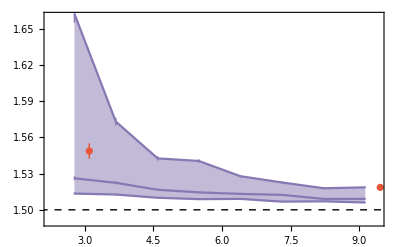

```mathematica
Show[Nf4α2LoopmΔEqqbarVsPlot,ListPlot[{{mJPsi[[1]],McccLQCD/mJPsi},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->ColorData[97][0]],PlotRange->{{1.5Mc,2Mb},{1.49,1.66}},Axes->False]
```

```mathematica
Table[Series[(3+Nf5α1LoopΔEqqqBig[[ii]]  αα^2/Nf5α1LoopMid[[ii]]^2)/(2+Nf5α1LoopΔEqqbarBig[[ii]] αα^2/Nf5α1LoopMid[[ii]]^2),{αα,0,2}],{ii,1,8}]
```

{3/2+(0.118170.00012) αα^2+O[αα]^3,3/2+(0.117720.00011) αα^2+O[αα]^3,3/2+(0.119480.00010) αα^2+O[αα]^3,3/2+(0.118640.00012) αα^2+O[αα]^3,3/2+(0.120800.00013) αα^2+O[αα]^3,3/2+(0.122510.00014) αα^2+O[αα]^3,3/2+(0.125850.00014) αα^2+O[αα]^3,3/2+(0.147290.00018) αα^2+O[αα]^3}

```mathematica
Table[Series[(3+Nf5α2LoopmΔEqqqBig[[ii]]  αα^2/Nf5α2LoopMid[[ii]]^2)/(2+Nf5α2LoopmΔEqqbarBig[[ii]] αα^2/Nf5α2LoopMid[[ii]]^2),{αα,0,2}],{ii,1,8}]
```

{3/2+(0.16120.0020) αα^2+O[αα]^3,3/2+(0.15020.0021) αα^2+O[αα]^3,3/2+(0.16140.0022) αα^2+O[αα]^3,3/2+(0.17070.0024) αα^2+O[αα]^3,3/2+(0.15330.0030) αα^2+O[αα]^3,3/2+(0.16500.0030) αα^2+O[αα]^3,3/2+(0.1790.004) αα^2+O[αα]^3,3/2+(0.4000.011) αα^2+O[αα]^3}

```mathematica
.12 .4^2
```

0.0192

```mathematica
.12 .2^2
```

0.0048

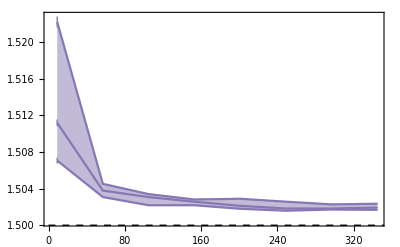

```mathematica
Nf5α2LoopmΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopmΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],(3Nf5α2LoopmQ[[i]]+Nf5α2LoopmΔEqqqMid[[i]]Nf5α2LoopmQ[[i]])/(2Nf5α2LoopmQ[[i]]+Nf5α2LoopmΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]])},{i,1,Length[Nf5α2LoopMid]}],Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopmΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],(3Nf5α2LoopmQ[[i]]+Nf5α2LoopmΔEqqqBig[[i]]Nf5α2LoopmQ[[i]])/(2Nf5α2LoopmQ[[i]]+Nf5α2LoopmΔEqqbarBig[[i]]Nf5α2LoopmQ[[i]])},{i,1,Length[Nf5α2LoopBig]}],Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopmΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],(3Nf5α2LoopmQ[[i]]+Nf5α2LoopmΔEqqqSmall[[i]]Nf5α2LoopmQ[[i]])/(2Nf5α2LoopmQ[[i]]+Nf5α2LoopmΔEqqbarSmall[[i]]Nf5α2LoopmQ[[i]])},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

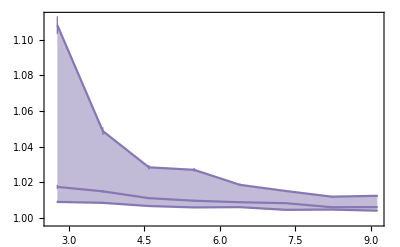

```mathematica
Nf4α2LoopmΔEqqbarVsPlot23=Show[ListPlot[{Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopmΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],2/3(3Nf4α2LoopmQ[[i]]+Nf4α2LoopmΔEqqqMid[[i]]Nf4α2LoopmQ[[i]])/(2Nf4α2LoopmQ[[i]]+Nf4α2LoopmΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]])},{i,1,Length[Nf4α2LoopMid]}],Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopmΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],2/3(3Nf4α2LoopmQ[[i]]+Nf4α2LoopmΔEqqqBig[[i]]Nf4α2LoopmQ[[i]])/(2Nf4α2LoopmQ[[i]]+Nf4α2LoopmΔEqqbarBig[[i]]Nf4α2LoopmQ[[i]])},{i,1,Length[Nf4α2LoopBig]}],Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopmΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],2/3(3Nf4α2LoopmQ[[i]]+Nf4α2LoopmΔEqqqSmall[[i]]Nf4α2LoopmQ[[i]])/(2Nf4α2LoopmQ[[i]]+Nf4α2LoopmΔEqqbarSmall[[i]]Nf4α2LoopmQ[[i]])},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["(2/3) M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

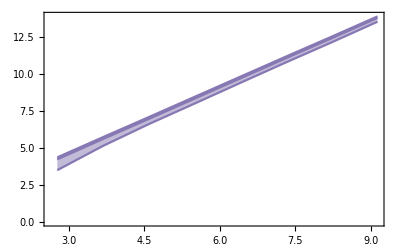

```mathematica
Nf4α2LoopmΔEqqbarVsPlotNoRatio=Show[ListPlot[{Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopmΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],(3Nf4α2LoopmQ[[i]]+Nf4α2LoopmΔEqqqMid[[i]]Nf4α2LoopmQ[[i]])},{i,1,Length[Nf4α2LoopMid]}],Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopmΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],(3Nf4α2LoopmQ[[i]]+Nf4α2LoopmQ[[i]]Nf4α2LoopmΔEqqqBig[[i]])},{i,1,Length[Nf4α2LoopBig]}],Reverse@Table[{2Nf4α2LoopmQ[[i]]+Nf4α2LoopmΔEqqbarMid[[i]]Nf4α2LoopmQ[[i]],(3Nf4α2LoopmQ[[i]]+Nf4α2LoopmQ[[i]]Nf4α2LoopmΔEqqqSmall[[i]])},{i,1,Length[Nf4α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}]
```

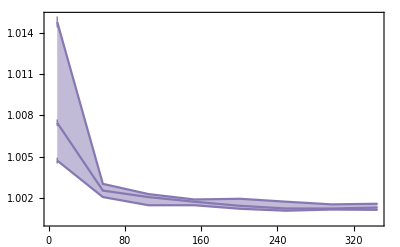

```mathematica
Nf5α2LoopmΔEqqbarVsPlot23=Show[ListPlot[{Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopmΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],2/3(3Nf5α2LoopmQ[[i]]+Nf5α2LoopmΔEqqqMid[[i]]Nf5α2LoopmQ[[i]])/(2Nf5α2LoopmQ[[i]]+Nf5α2LoopmΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]])},{i,1,Length[Nf5α2LoopMid]}],Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopmΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],2/3(3Nf5α2LoopmQ[[i]]+Nf5α2LoopmΔEqqqBig[[i]]Nf5α2LoopmQ[[i]])/(2Nf5α2LoopmQ[[i]]+Nf5α2LoopmΔEqqbarBig[[i]]Nf5α2LoopmQ[[i]])},{i,1,Length[Nf5α2LoopBig]}],Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopmΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],2/3(3Nf5α2LoopmQ[[i]]+Nf5α2LoopmΔEqqqSmall[[i]]Nf5α2LoopmQ[[i]])/(2Nf5α2LoopmQ[[i]]+Nf5α2LoopmΔEqqbarSmall[[i]]Nf5α2LoopmQ[[i]])},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["(2/3) M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

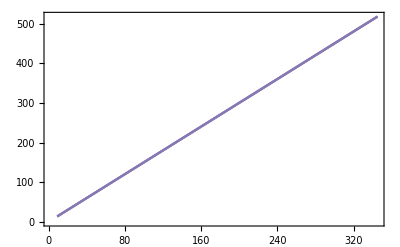

```mathematica
Nf5α2LoopmΔEqqbarVsPlotNoRatio=Show[ListPlot[{Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopmΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],(3Nf5α2LoopmQ[[i]]+Nf5α2LoopmΔEqqqMid[[i]]Nf5α2LoopmQ[[i]])},{i,1,Length[Nf5α2LoopMid]}],Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopmΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],(3Nf5α2LoopmQ[[i]]+Nf5α2LoopmQ[[i]]Nf5α2LoopmΔEqqqBig[[i]])},{i,1,Length[Nf5α2LoopBig]}],Reverse@Table[{2Nf5α2LoopmQ[[i]]+Nf5α2LoopmΔEqqbarMid[[i]]Nf5α2LoopmQ[[i]],(3Nf5α2LoopmQ[[i]]+Nf5α2LoopmQ[[i]]Nf5α2LoopmΔEqqqSmall[[i]])},{i,1,Length[Nf5α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}]
```

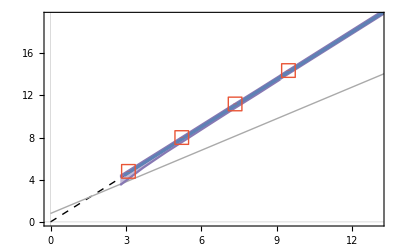

```mathematica
scale=13;Show[ListPlot[{{mJPsi,McccLQCD},{(2/3mJPsi+1/3moops),MbccLQCD},{(1/3mJPsi+2/3moops),MbbcLQCD},{moops,MbbbLQCD}},PlotStyle->Opacity[0],IntervalMarkersStyle->{Opacity[0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}],Graphics[{Black,Dashed,Line[{{0,0},{2scale,1.5  2 scale}}]}],Graphics[{Lighter[Gray],Line[{{0,.800},{1000,.800+1000}}]}],Nf4α2LoopmΔEqqbarVsPlotNoRatio,Nf5α2LoopmΔEqqbarVsPlotNoRatio,Nf4α1LoopΔEqqbarVsPlotNoRatio,Nf5α1LoopΔEqqbarVsPlotNoRatio,ListPlot[{{mJPsi,McccLQCD},{(2/3mJPsi+1/3moops),MbccLQCD},{(1/3mJPsi+2/3moops),MbbcLQCD},{moops,MbbbLQCD}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}],PlotRange->{{0,scale},{0,3/2 scale}},Axes->False,GridLines->{{0},{0}}]
```

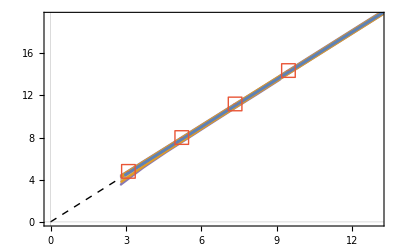

```mathematica
scale=13;Show[ListPlot[{{mJPsi,McccLQCD},{(2/3mJPsi+1/3moops),MbccLQCD},{(1/3mJPsi+2/3moops),MbbcLQCD},{moops,MbbbLQCD}},PlotStyle->Opacity[0],IntervalMarkersStyle->{Opacity[0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}],Graphics[{Black,Dashed,Line[{{0,0},{2scale,1.5  2 scale}}]}],Nf4α2LoopmΔEqqbarVsPlotNoRatio,Nf5α2LoopmΔEqqbarVsPlotNoRatio,Nf4α2LoopΔEqqbarVsPlotNoRatio,Nf5α2LoopΔEqqbarVsPlotNoRatio,Nf4α1LoopΔEqqbarVsPlotNoRatio,Nf5α1LoopΔEqqbarVsPlotNoRatio,ListPlot[{{mJPsi,McccLQCD},{(2/3mJPsi+1/3moops),MbccLQCD},{(1/3mJPsi+2/3moops),MbbcLQCD},{moops,MbbbLQCD}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}],PlotRange->{{0,scale},{0,3/2 scale}},Axes->False,GridLines->{{0},{0}}]
```

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot,Nf5α1LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold]],PlotRange->{{2Mc,2.5Mb},{1.49,1.63}},Axes->False]
```

-Graphics-

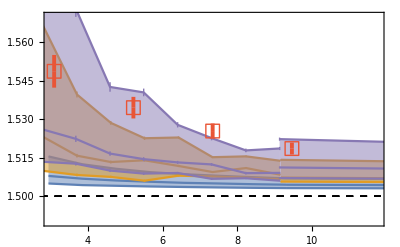

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot,Nf5α1LoopΔEqqbarVsPlot,Nf4α2LoopΔEqqbarVsPlot,Nf5α2LoopΔEqqbarVsPlot,Nf4α2LoopmΔEqqbarVsPlot,Nf5α2LoopmΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold]],PlotRange->{{2Mc,2.5Mb},{1.49,1.57}},Axes->False]
```

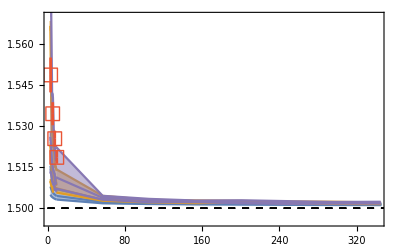

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot,Nf5α1LoopΔEqqbarVsPlot,Nf4α2LoopΔEqqbarVsPlot,Nf5α2LoopΔEqqbarVsPlot,Nf4α2LoopmΔEqqbarVsPlot,Nf5α2LoopmΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.005]},PlotMarkers->Style[markerlist[[1]],14,Bold]],PlotRange->{{2Mc,1.97Mt},{1.495,1.57}},Axes->False]
```

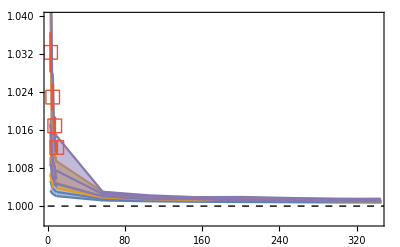

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot23,Nf5α1LoopΔEqqbarVsPlot23,Nf4α2LoopΔEqqbarVsPlot23,Nf5α2LoopΔEqqbarVsPlot23,Nf4α2LoopmΔEqqbarVsPlot23,Nf5α2LoopmΔEqqbarVsPlot23,ListPlot[{{mJPsi,2/3McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),2/3MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),2/3MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,2/3MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.005]},PlotMarkers->Style[markerlist[[1]],14,Bold]],Graphics[{Black,Dashed,Line[{{0,1},{20000,1}}]}],PlotRange->{{2Mc,1.97Mt},{2/3 1.495,2/3 1.56}},Axes->False]
```

#### NNLO

```mathematica
Nf4α3LoopMid
```

{0.225626,0.231589,0.238582,0.246955,0.257253,0.270383,0.287996,0.313525}

```mathematica
Table[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,3]],{i,1,Length[Nf4α3LoopBig]}]
```

{1.02863,1.03381,1.34805,0.885382,1.07816,0.785995,1.09081,1.25459}

```mathematica
Table[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,3]],{i,1,Length[Nf4α3LoopBig]}]
```

{0.739366,0.557169,0.782995,0.796744,0.791008,0.718253,0.901865,0.788854}

```mathematica
Table[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,3]],{i,1,Length[Nf4α3LoopBig]}]
```

{0.894601,0.697081,0.938211,0.794223,0.969158,0.802369,0.959402,1.10224}

```mathematica
Nf4α3LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α3LoopBig]}]
```

{-0.18540.0006,-0.20930.0007,-0.23880.0008,-0.27690.0009,-0.32030.0011,-0.41570.0015,-0.58550.0019,-1.0540.004}

```mathematica
Nf4α3LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α3LoopMid]}]
```

{-0.11160.0005,-0.12300.0006,-0.13430.0007,-0.15120.0009,-0.17200.0009,-0.20180.0013,-0.24910.0015,-0.34230.0020}

```mathematica
Nf4α3LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α3LoopSmall]}]
```

{-0.07870.0005,-0.08380.0006,-0.09000.0006,-0.09600.0007,-0.10800.0007,-0.12170.0010,-0.13910.0010,-0.17500.0014}

```mathematica
ΔEqqqOα2=Nf4α3LoopΔEqqbarMid/Nf4α3LoopMid^2
```

{-1.7590.010,-1.8430.012,-1.8880.011,-1.9600.012,-2.0520.013,-2.1100.017,-2.3550.017,-2.6050.022}

```mathematica
Nf4α3LoopΔEqqqMid/Nf4α3LoopMid^2
```

{-2.1920.010,-2.2940.012,-2.3600.012,-2.4780.014,-2.5990.014,-2.7600.018,-3.0030.018,-3.4830.020}

```mathematica
ΔEqqqOα2WD=3/2Nf4α3LoopΔEqqbarMid/Nf4α3LoopMid^2
```

{-2.6380.015,-2.7650.017,-2.8320.017,-2.9400.018,-3.0790.020,-3.1640.026,-3.5320.026,-3.9080.034}

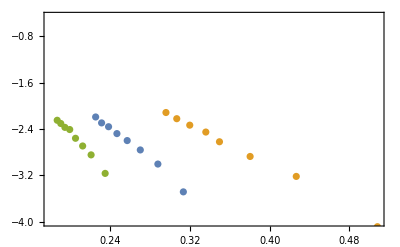

```mathematica
EqqqNf4α3LoopPlot=Show[ListPlot[{Table[{Nf4α3LoopMid[[i]],Nf4α3LoopΔEqqqMid[[i]]/Nf4α3LoopMid[[i]]^2},{i,1,Length[Nf4α3LoopMid]}],Table[{Nf4α3LoopBig[[i]],Nf4α3LoopΔEqqqBig[[i]]/Nf4α3LoopBig[[i]]^2},{i,1,Length[Nf4α3LoopBig]}],Table[{Nf4α3LoopSmall[[i]],Nf4α3LoopΔEqqqSmall[[i]]/Nf4α3LoopSmall[[i]]^2},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->{-4,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

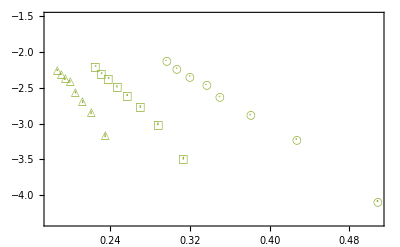

```mathematica
EqqqNf4α3LoopPlot=Show[ListPlot[{Table[{Nf4α3LoopMid[[i]],Nf4α3LoopΔEqqqMid[[i]]/Nf4α3LoopMid[[i]]^2},{i,1,Length[Nf4α3LoopMid]}],Table[{Nf4α3LoopBig[[i]],Nf4α3LoopΔEqqqBig[[i]]/Nf4α3LoopBig[[i]]^2},{i,1,Length[Nf4α3LoopBig]}],Table[{Nf4α3LoopSmall[[i]],Nf4α3LoopΔEqqqSmall[[i]]/Nf4α3LoopSmall[[i]]^2},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->{-3.5 1.25,-1.2 1.25},PlotLegends->Placed[αLegendNNLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][3]},PlotStyle->{ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["\\text{NNLO}",Magnification->1.2]]
```

```mathematica
Export[plotdir<>"DeltaEQQQ_vs_alpha_NNLO.pdf",EqqqNf4α3LoopPlot];
```

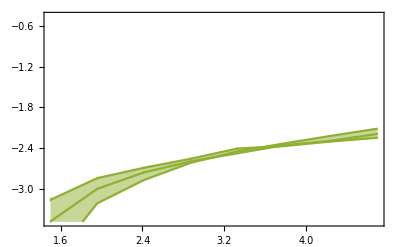

```mathematica
Nf4α3LoopΔEqqqPlot=Show[ListPlot[{Reverse@Table[{Nf4α3LoopmQ[[i]],Nf4α3LoopΔEqqqMid[[i]]/Nf4α3LoopMid[[i]]^2},{i,1,Length[Nf4α3LoopMid]}],Reverse@Table[{Nf4α3LoopmQ[[i]],Nf4α3LoopΔEqqqBig[[i]]/Nf4α3LoopBig[[i]]^2},{i,1,Length[Nf4α3LoopBig]}],Reverse@Table[{Nf4α3LoopmQ[[i]],Nf4α3LoopΔEqqqSmall[[i]]/Nf4α3LoopSmall[[i]]^2},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->{{Mc,Mb},{-3.49,-.46}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

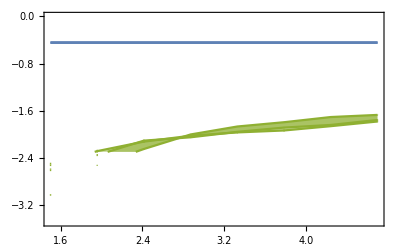

```mathematica
Show[Nf4α3LoopΔEqqbarPlot,Nf4α1LoopΔEqqbarPlot,PlotRange->{-3.49,0}]
```

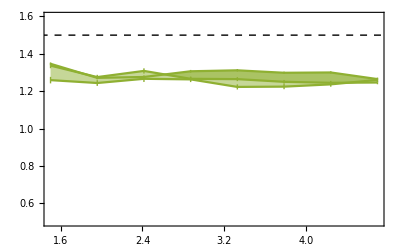

```mathematica
Nf4α3LoopΔEqqqRatioPlot=Show[ListPlot[{Reverse@Table[{Nf4α3LoopmQ[[i]],Nf4α3LoopΔEqqqMid[[i]]/Nf4α3LoopΔEqqbarMid[[i]]},{i,1,Length[Nf4α3LoopMid]}],Reverse@Table[{Nf4α3LoopmQ[[i]],Nf4α3LoopΔEqqqBig[[i]]/Nf4α3LoopΔEqqbarBig[[i]]},{i,1,Length[Nf4α3LoopBig]}],Reverse@Table[{Nf4α3LoopmQ[[i]],Nf4α3LoopΔEqqqSmall[[i]]/Nf4α3LoopΔEqqbarSmall[[i]]},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->{{Mc,Mb},{.5,1.6}},PlotLegends->Placed[OLegend,{0.5,0.2}],Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

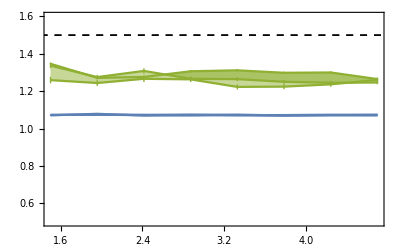

```mathematica
Show[Nf4α3LoopΔEqqqRatioPlot,Nf4α1LoopΔEqqqRatioPlot]
```

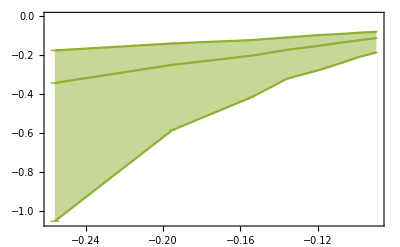

```mathematica
Nf4α3LoopΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{Nf4α3LoopΔEqqbarMid[[i]],Nf4α3LoopΔEqqqMid[[i]]},{i,1,Length[Nf4α3LoopMid]}],Reverse@Table[{Nf4α3LoopΔEqqbarMid[[i]],Nf4α3LoopΔEqqqBig[[i]]},{i,1,Length[Nf4α3LoopBig]}],Reverse@Table[{Nf4α3LoopΔEqqbarMid[[i]],Nf4α3LoopΔEqqqSmall[[i]]},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\Delta E_{Q\\overline{Q}}/m_Q",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/m_Q"]}]
```

```mathematica
Show[Nf4α3LoopΔEqqbarVsPlot,Nf4α1LoopΔEqqbarVsPlot]
```

-Graphics-

```mathematica
Nf5α3LoopMid
```

{0.120384,0.122838,0.12585,0.129703,0.134945,0.142867,0.157737,0.225626}

```mathematica
Nf5α3LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α3LoopBig]}]
```

{-0.0170870.000029,-0.0179900.000028,-0.0192670.000031,-0.021430.00004,-0.024010.00004,-0.028750.00005,-0.039890.00009,-0.16030.0005}

```mathematica
Nf5α3LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α3LoopMid]}]
```

{-0.015200.00005,-0.016010.00004,-0.017020.00005,-0.018980.00006,-0.020560.00006,-0.024450.00007,-0.032480.00012,-0.09710.0004}

```mathematica
Nf5α3LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α3LoopSmall]}]
```

{-0.013400.00005,-0.014010.00005,-0.014800.00006,-0.016290.00006,-0.017850.00007,-0.020900.00009,-0.026960.00012,-0.06910.0004}

```mathematica
ΔEqqqOα2=Nf5α3LoopΔEqqbarMid/Nf5α3LoopMid^2
```

{-0.87750.0025,-0.89110.0026,-0.89710.0029,-0.93360.0030,-0.97510.0029,-0.9730.004,-1.0740.005,-1.5640.008}

```mathematica
Nf5α3LoopΔEqqqMid/Nf5α3LoopMid^2
```

{-1.04850.0032,-1.06090.0028,-1.07480.0033,-1.12830.0033,-1.12900.0032,-1.1980.004,-1.3050.005,-1.9080.009}

```mathematica
ΔEqqqOα2WD=3/2Nf5α3LoopΔEqqbarMid/Nf5α3LoopMid^2
```

{-1.3160.004,-1.3370.004,-1.3460.004,-1.4000.004,-1.4630.004,-1.4590.005,-1.6100.007,-2.3450.012}

```mathematica
Nf5α3LoopΔEqqqMid
```

{-0.015200.00005,-0.016010.00004,-0.017020.00005,-0.018980.00006,-0.020560.00006,-0.024450.00007,-0.032480.00012,-0.09710.0004}

```mathematica
Nf4α3LoopΔEqqqMid
```

{-0.11160.0005,-0.12300.0006,-0.13430.0007,-0.15120.0009,-0.17200.0009,-0.20180.0013,-0.24910.0015,-0.34230.0020}

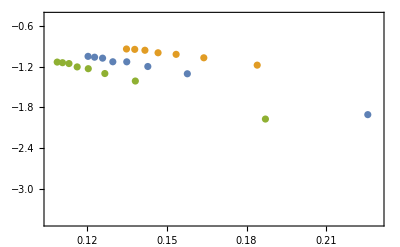

```mathematica
EqqqNf5α3LoopPlot=Show[ListPlot[{Table[{Nf5α3LoopMid[[i]],Nf5α3LoopΔEqqqMid[[i]]/Nf5α3LoopMid[[i]]^2},{i,1,Length[Nf5α3LoopMid]}],Table[{Nf5α3LoopBig[[i]],Nf5α3LoopΔEqqqBig[[i]]/Nf5α3LoopBig[[i]]^2},{i,1,Length[Nf5α3LoopBig]}],Table[{Nf5α3LoopSmall[[i]],Nf5α3LoopΔEqqqSmall[[i]]/Nf5α3LoopSmall[[i]]^2},{i,1,Length[Nf5α3LoopSmall]}]},PlotRange->{-3.49,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

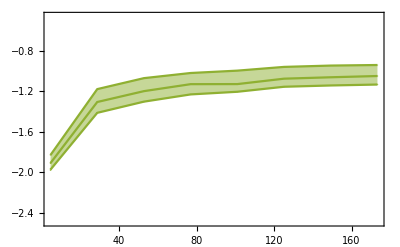

```mathematica
Nf5α3LoopΔEqqqPlot=Show[ListPlot[{Reverse@Table[{Nf5α3LoopmQ[[i]],Nf5α3LoopΔEqqqMid[[i]]/Nf5α3LoopMid[[i]]^2},{i,1,Length[Nf5α3LoopMid]}],Reverse@Table[{Nf5α3LoopmQ[[i]],Nf5α3LoopΔEqqqBig[[i]]/Nf5α3LoopBig[[i]]^2},{i,1,Length[Nf5α3LoopBig]}],Reverse@Table[{Nf5α3LoopmQ[[i]],Nf5α3LoopΔEqqqSmall[[i]]/Nf5α3LoopSmall[[i]]^2},{i,1,Length[Nf5α3LoopSmall]}]},PlotRange->{{Mb,Mt},{-2.49,-.46}},Joined->True,Filling->{2->{3}},PlotLegends->Placed[OLegend,{0.5,0.2}],FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

```mathematica
Show[Nf5α3LoopΔEqqqPlot,Nf5α2LoopΔEqqqPlot,Nf5α1LoopΔEqqqPlot,PlotRange->{-2.,0},Axes->False]
```

-Graphics-

```mathematica
EqqqNf45α3LoopPlotMQ=Show[Nf4α3LoopΔEqqqPlot,Nf5α3LoopΔEqqqPlot,Nf4α2LoopΔEqqqPlot,Nf5α2LoopΔEqqqPlot,Nf4α1LoopΔEqqqPlot,Nf5α1LoopΔEqqqPlot,PlotRange->{-2.7,0},Axes->False]
```

-Graphics-

```mathematica
EqqqNf45α3LoopPlotMQ=Show[Nf4α1LoopΔEqqqPlot,Nf5α1LoopΔEqqqPlot,Nf4α2LoopΔEqqqPlot,Nf5α2LoopΔEqqqPlot,Nf4α2LoopmΔEqqqPlot,Nf5α2LoopmΔEqqqPlot,Nf4α3LoopΔEqqqPlot,Nf5α3LoopΔEqqqPlot,PlotRange->{-2.7,0},Axes->False]
```

-Graphics-

```mathematica
Export[plotdir<>"DeltaEQQQ_vs_mQ.pdf",EqqqNf45α3LoopPlotMQ];
```

```mathematica
Nf5α3LoopΔEqqqRatioPlot=Show[ListPlot[{Reverse@Table[{Nf5α3LoopmQ[[i]],Nf5α3LoopΔEqqqMid[[i]]/Nf5α3LoopΔEqqbarMid[[i]]},{i,1,Length[Nf5α3LoopMid]}],Reverse@Table[{Nf5α3LoopmQ[[i]],Nf5α3LoopΔEqqqBig[[i]]/Nf5α3LoopΔEqqbarBig[[i]]},{i,1,Length[Nf5α3LoopBig]}],Reverse@Table[{Nf5α3LoopmQ[[i]],Nf5α3LoopΔEqqqSmall[[i]]/Nf5α3LoopΔEqqbarSmall[[i]]},{i,1,Length[Nf5α3LoopSmall]}]},PlotRange->{{Mb,Mt},{.5,1.6}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Show[Nf5α1LoopΔEqqqRatioPlot,Nf5α2LoopΔEqqqRatioPlot,Nf5α2LoopmΔEqqqRatioPlot,Nf5α3LoopΔEqqqRatioPlot]
```

-Graphics-

```mathematica
Show[Nf4α2LoopΔEqqqRatioPlot,Nf5α2LoopΔEqqqRatioPlot,PlotRange->{{Mc,.2Mt},{.8,1.6}}]
```

-Graphics-

```mathematica
Nf5α2LoopΔEqqqRatioPlot
```

-Graphics-

```mathematica
EqqqNf4α3LoopPlotMQratio=Show[Nf4α1LoopΔEqqqRatioPlot,Nf5α1LoopΔEqqqRatioPlot,Nf4α2LoopΔEqqqRatioPlot,Nf5α2LoopΔEqqqRatioPlot,Nf4α2LoopmΔEqqqRatioPlot,Nf5α2LoopmΔEqqqRatioPlot,Nf4α3LoopΔEqqqRatioPlot,Nf5α3LoopΔEqqqRatioPlot,PlotRange->{{Mc,Mb},{.8,1.6}}]
```

-Graphics-

```mathematica
Export[plotdir<>"DeltaE_ratio_vs_mQ.pdf",EqqqNf4α3LoopPlotMQratio];
```

```mathematica
EqqqNf45α3LoopPlotMQratio=Show[Nf4α1LoopΔEqqqRatioPlot,Nf5α1LoopΔEqqqRatioPlot,Nf4α2LoopΔEqqqRatioPlot,Nf5α2LoopΔEqqqRatioPlot,Nf4α2LoopmΔEqqqRatioPlot,Nf5α2LoopmΔEqqqRatioPlot,Nf4α3LoopΔEqqqRatioPlot,Nf5α3LoopΔEqqqRatioPlot,PlotRange->{{Mc,Mt},{.8,1.6}}]
```

-Graphics-

```mathematica
Export[plotdir<>"DeltaE_ratio_vs_mQ_big.pdf",EqqqNf45α3LoopPlotMQratio];
```

```mathematica
Nf4α3LoopΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarMid[[i]]Nf4α3LoopmQ[[i]],(3Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqqMid[[i]]Nf4α3LoopmQ[[i]])/(2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarMid[[i]]Nf4α3LoopmQ[[i]])},{i,1,Length[Nf4α3LoopMid]}],Reverse@Table[{2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarMid[[i]]Nf4α3LoopmQ[[i]],(3Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqqBig[[i]]Nf4α3LoopmQ[[i]])/(2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarBig[[i]]Nf4α3LoopmQ[[i]])},{i,1,Length[Nf4α3LoopBig]}],Reverse@Table[{2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarMid[[i]]Nf4α3LoopmQ[[i]],(3Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqqSmall[[i]]Nf4α3LoopmQ[[i]])/(2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarSmall[[i]]Nf4α3LoopmQ[[i]])},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},PlotLegends->Placed[OLegend,{0.5,0.8}],IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Show[Nf4α3LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->ColorData[97][0]],PlotRange->{{2Mc,2Mb},{1.49,1.56}},Axes->False]
```

-Graphics-

```mathematica
Nf5α3LoopΔEqqbarVsPlot=Show[ListPlot[{Reverse@Table[{2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarMid[[i]]Nf5α3LoopmQ[[i]],(3Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqqMid[[i]]Nf5α3LoopmQ[[i]])/(2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarMid[[i]]Nf5α3LoopmQ[[i]])},{i,1,Length[Nf5α3LoopMid]}],Reverse@Table[{2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarMid[[i]]Nf5α3LoopmQ[[i]],(3Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqqBig[[i]]Nf5α3LoopmQ[[i]])/(2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarBig[[i]]Nf5α3LoopmQ[[i]])},{i,1,Length[Nf5α3LoopBig]}],Reverse@Table[{2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarMid[[i]]Nf5α3LoopmQ[[i]],(3Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqqSmall[[i]]Nf5α3LoopmQ[[i]])/(2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarSmall[[i]]Nf5α3LoopmQ[[i]])},{i,1,Length[Nf5α3LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
markerlist={"□","○","△","▽","◇","▯","◦"};
```

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot,Nf5α1LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold]],PlotRange->{{2Mc,2.5Mb},{1.49,1.60}},Axes->False]
```

-Graphics-

```mathematica
MqqqNf45α3LoopPlotMQratio=Show[Nf4α1LoopΔEqqbarVsPlot,Nf5α1LoopΔEqqbarVsPlot,Nf4α2LoopΔEqqbarVsPlot,Nf5α2LoopΔEqqbarVsPlot,Nf4α3LoopΔEqqbarVsPlot,Nf5α3LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold]],PlotRange->{{2Mc,2.5Mb},{1.49,1.60}},Axes->False]
```

-Graphics-

```mathematica
MqqqNf45α3LoopPlotMQratio=Show[Nf4α1LoopΔEqqbarVsPlot,Nf5α1LoopΔEqqbarVsPlot,Nf4α2LoopΔEqqbarVsPlot,Nf5α2LoopΔEqqbarVsPlot,Nf4α2LoopmΔEqqbarVsPlot,Nf5α2LoopmΔEqqbarVsPlot,Nf4α3LoopΔEqqbarVsPlot,Nf5α3LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold]],PlotRange->{{2Mc,2.5Mb},{1.49,1.60}},Axes->False]
```

-Graphics-

```mathematica
Export[plotdir<>"M_ratio_vs_MQQbar.pdf",MqqqNf45α3LoopPlotMQratio];
```

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot,Nf5α1LoopΔEqqbarVsPlot,Nf4α2LoopΔEqqbarVsPlot,Nf5α2LoopΔEqqbarVsPlot,Nf4α3LoopΔEqqbarVsPlot,Nf5α3LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.005]},PlotMarkers->Style[markerlist[[1]],14,Bold]],PlotRange->{{2Mc,2Mt},{1.49,1.56}},Axes->False]
```

-Graphics-

```mathematica
MqqqNf45α3LoopPlotMQratioBig=Show[Nf4α1LoopΔEqqbarVsPlot,Nf5α1LoopΔEqqbarVsPlot,Nf4α2LoopΔEqqbarVsPlot,Nf5α2LoopΔEqqbarVsPlot,Nf4α3LoopΔEqqbarVsPlot,Nf5α3LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.005]},PlotMarkers->Style[markerlist[[1]],14,Bold]],Graphics[{Black,Dashed,Line[{{0,1},{20000,1}}]}],PlotRange->{{2Mc,.3Mt},{1.495,1.57}},Axes->False]
```

-Graphics-

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot,Nf5α1LoopΔEqqbarVsPlot,Nf4α2LoopΔEqqbarVsPlot,Nf5α2LoopΔEqqbarVsPlot,Nf4α2LoopmΔEqqbarVsPlot,Nf5α2LoopmΔEqqbarVsPlot,Nf4α3LoopΔEqqbarVsPlot,Nf5α3LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.005]},PlotMarkers->Style[markerlist[[1]],14,Bold]],PlotRange->{{2Mc,2Mt},{1.49,1.56}},Axes->False]
```

-Graphics-

```mathematica
MqqqNf45α3LoopPlotMQratioBig=Show[Nf4α1LoopΔEqqbarVsPlot,Nf5α1LoopΔEqqbarVsPlot,Nf4α2LoopΔEqqbarVsPlot,Nf5α2LoopΔEqqbarVsPlot,Nf4α2LoopmΔEqqbarVsPlot,Nf5α2LoopmΔEqqbarVsPlot,Nf4α3LoopΔEqqbarVsPlot,Nf5α3LoopΔEqqbarVsPlot,ListPlot[{{mJPsi,McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.005]},PlotMarkers->Style[markerlist[[1]],14,Bold]],Graphics[{Black,Dashed,Line[{{0,1},{20000,1}}]}],PlotRange->{{2Mc,.3Mt},{1.495,1.57}},Axes->False]
```

-Graphics-

```mathematica
Export[plotdir<>"M_ratio_vs_MQQbar_big.pdf",MqqqNf45α3LoopPlotMQratioBig];
```

```mathematica
Nf4α3LoopΔEqqbarVsPlot23=Show[ListPlot[{Reverse@Table[{2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarMid[[i]]Nf4α3LoopmQ[[i]],2/3(3Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqqMid[[i]]Nf4α3LoopmQ[[i]])/(2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarMid[[i]]Nf4α3LoopmQ[[i]])},{i,1,Length[Nf4α3LoopMid]}],Reverse@Table[{2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarMid[[i]]Nf4α3LoopmQ[[i]],2/3(3Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqqBig[[i]]Nf4α3LoopmQ[[i]])/(2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarBig[[i]]Nf4α3LoopmQ[[i]])},{i,1,Length[Nf4α3LoopBig]}],Reverse@Table[{2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarMid[[i]]Nf4α3LoopmQ[[i]],2/3(3Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqqSmall[[i]]Nf4α3LoopmQ[[i]])/(2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarSmall[[i]]Nf4α3LoopmQ[[i]])},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["(2/3) M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Nf4α3LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Reverse@Table[{2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarMid[[i]]Nf4α3LoopmQ[[i]],(3Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqqMid[[i]]Nf4α3LoopmQ[[i]])},{i,1,Length[Nf4α3LoopMid]}],Reverse@Table[{2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarMid[[i]]Nf4α3LoopmQ[[i]],(3Nf4α3LoopmQ[[i]]+Nf4α3LoopmQ[[i]]Nf4α3LoopΔEqqqBig[[i]])},{i,1,Length[Nf4α3LoopBig]}],Reverse@Table[{2Nf4α3LoopmQ[[i]]+Nf4α3LoopΔEqqbarMid[[i]]Nf4α3LoopmQ[[i]],(3Nf4α3LoopmQ[[i]]+Nf4α3LoopmQ[[i]]Nf4α3LoopΔEqqqSmall[[i]])},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}]
```

-Graphics-

```mathematica
Nf5α3LoopΔEqqbarVsPlot23=Show[ListPlot[{Reverse@Table[{2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarMid[[i]]Nf5α3LoopmQ[[i]],2/3(3Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqqMid[[i]]Nf5α3LoopmQ[[i]])/(2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarMid[[i]]Nf5α3LoopmQ[[i]])},{i,1,Length[Nf5α3LoopMid]}],Reverse@Table[{2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarMid[[i]]Nf5α3LoopmQ[[i]],2/3(3Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqqBig[[i]]Nf5α3LoopmQ[[i]])/(2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarBig[[i]]Nf5α3LoopmQ[[i]])},{i,1,Length[Nf5α3LoopBig]}],Reverse@Table[{2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarMid[[i]]Nf5α3LoopmQ[[i]],2/3(3Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqqSmall[[i]]Nf5α3LoopmQ[[i]])/(2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarSmall[[i]]Nf5α3LoopmQ[[i]])},{i,1,Length[Nf5α3LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["(2/3) M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Nf5α3LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Reverse@Table[{2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarMid[[i]]Nf5α3LoopmQ[[i]],(3Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqqMid[[i]]Nf5α3LoopmQ[[i]])},{i,1,Length[Nf5α3LoopMid]}],Reverse@Table[{2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarMid[[i]]Nf5α3LoopmQ[[i]],(3Nf5α3LoopmQ[[i]]+Nf5α3LoopmQ[[i]]Nf5α3LoopΔEqqqBig[[i]])},{i,1,Length[Nf5α3LoopBig]}],Reverse@Table[{2Nf5α3LoopmQ[[i]]+Nf5α3LoopΔEqqbarMid[[i]]Nf5α3LoopmQ[[i]],(3Nf5α3LoopmQ[[i]]+Nf5α3LoopmQ[[i]]Nf5α3LoopΔEqqqSmall[[i]])},{i,1,Length[Nf5α3LoopSmall]}]},PlotRange->All,PlotLegends->Placed[OLegend2,{0.3,0.8}],Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}]
```

-Graphics-

```mathematica
scale=13;MqqqNf45α3LoopPlotMQQbar=Show[ListPlot[{{mJPsi,McccLQCD},{(2/3mJPsi+1/3moops),MbccLQCD},{(1/3mJPsi+2/3moops),MbbcLQCD},{moops,MbbbLQCD}},PlotStyle->Opacity[0],IntervalMarkersStyle->{Opacity[0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}],Graphics[{Black,Dashed,Line[{{0,0},{2scale,1.5  2 scale}}]}],Nf4α3LoopΔEqqbarVsPlotNoRatio,Nf5α3LoopΔEqqbarVsPlotNoRatio,Nf4α2LoopΔEqqbarVsPlotNoRatio,Nf5α2LoopΔEqqbarVsPlotNoRatio,Nf4α1LoopΔEqqbarVsPlotNoRatio,Nf5α1LoopΔEqqbarVsPlotNoRatio,ListPlot[{{mJPsi,McccLQCD},{(2/3mJPsi+1/3moops),MbccLQCD},{(1/3mJPsi+2/3moops),MbbcLQCD},{moops,MbbbLQCD}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}],PlotRange->{{0,scale},{0,3/2 scale}},Axes->False,GridLines->{{0},{0}}]
```

-Graphics-

```mathematica
(*scale=13;MqqqNf45α3LoopPlotMQQbar=Show[ListPlot[{{mJPsi,McccLQCD},{(2/3mJPsi+1/3moops),MbccLQCD},{(1/3mJPsi+2/3moops),MbbcLQCD},{moops,MbbbLQCD}},PlotStyle->Opacity[0],IntervalMarkersStyle->{Opacity[0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}],Graphics[{Black,Dashed,Line[{{0,0},{2scale,1.5  2 scale}}]}],Nf4α3LoopΔEqqbarVsPlotNoRatio,Nf5α3LoopΔEqqbarVsPlotNoRatio,Nf4α2LoopΔEqqbarVsPlotNoRatio,Nf5α2LoopΔEqqbarVsPlotNoRatio,Nf4α2LoopmΔEqqbarVsPlotNoRatio,Nf5α2LoopmΔEqqbarVsPlotNoRatio,Nf4α1LoopΔEqqbarVsPlotNoRatio,Nf5α1LoopΔEqqbarVsPlotNoRatio,ListPlot[{{mJPsi,McccLQCD},{(2/3mJPsi+1/3moops),MbccLQCD},{(1/3mJPsi+2/3moops),MbbcLQCD},{moops,MbbbLQCD}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.007]},PlotMarkers->Style[markerlist[[1]],14,Bold],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}],PlotRange->{{0,scale},{0,3/2 scale}},Axes->False,GridLines->{{0},{0}}]*)
```

```mathematica
Export[plotdir<>"MQQQ_vs_MQQbar.pdf",MqqqNf45α3LoopPlotMQQbar];
```

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot23,Nf5α1LoopΔEqqbarVsPlot23,Nf4α2LoopΔEqqbarVsPlot23,Nf5α2LoopΔEqqbarVsPlot23,Nf4α3LoopΔEqqbarVsPlot23,Nf5α3LoopΔEqqbarVsPlot23,ListPlot[{{mJPsi,2/3McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),2/3MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),2/3MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,2/3MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.005]},PlotMarkers->Style[markerlist[[1]],14,Bold]],Graphics[{Black,Dashed,Line[{{0,1},{20000,1}}]}],PlotRange->{{2Mc,1.97Mt},{2/3 1.495,2/3 1.56}},Axes->False]
```

-Graphics-

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot23,Nf5α1LoopΔEqqbarVsPlot23,Nf4α2LoopΔEqqbarVsPlot23,Nf5α2LoopΔEqqbarVsPlot23,Nf4α3LoopΔEqqbarVsPlot23,Nf5α3LoopΔEqqbarVsPlot23,ListPlot[{{mJPsi,2/3McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),2/3MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),2/3MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,2/3MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.005]},PlotMarkers->Style[markerlist[[1]],14,Bold]],Graphics[{Black,Dashed,Line[{{0,1},{20000,1}}]}],PlotRange->{{2Mc,.3Mt},{2/3 1.495,2/3 1.57}},Axes->False]
```

-Graphics-

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot23,Nf5α1LoopΔEqqbarVsPlot23,Nf4α2LoopΔEqqbarVsPlot23,Nf5α2LoopΔEqqbarVsPlot23,Nf4α2LoopmΔEqqbarVsPlot23,Nf5α2LoopmΔEqqbarVsPlot23,Nf4α3LoopΔEqqbarVsPlot23,Nf5α3LoopΔEqqbarVsPlot23,ListPlot[{{mJPsi,2/3McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),2/3MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),2/3MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,2/3MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.005]},PlotMarkers->Style[markerlist[[1]],14,Bold]],Graphics[{Black,Dashed,Line[{{0,1},{20000,1}}]}],PlotRange->{{2Mc,1.97Mt},{2/3 1.495,2/3 1.56}},Axes->False]
```

-Graphics-

```mathematica
Show[Nf4α1LoopΔEqqbarVsPlot23,Nf5α1LoopΔEqqbarVsPlot23,Nf4α2LoopΔEqqbarVsPlot23,Nf5α2LoopΔEqqbarVsPlot23,Nf4α2LoopmΔEqqbarVsPlot23,Nf5α2LoopmΔEqqbarVsPlot23,Nf4α3LoopΔEqqbarVsPlot23,Nf5α3LoopΔEqqbarVsPlot23,ListPlot[{{mJPsi,2/3McccLQCD/mJPsi},{(2/3mJPsi+1/3moops),2/3MbccLQCD/(2/3mJPsi+1/3moops)},{(1/3mJPsi+2/3moops),2/3MbbcLQCD/(1/3mJPsi+2/3moops)},{moops,2/3MbbbLQCD/moops}},PlotStyle->ColorData[97][0],IntervalMarkersStyle->{ColorData[97][0],Thickness[0.005]},PlotMarkers->Style[markerlist[[1]],14,Bold]],Graphics[{Black,Dashed,Line[{{0,1},{20000,1}}]}],PlotRange->{{2Mc,.3Mt},{2/3 1.495,2/3 1.57}},Axes->False]
```

-Graphics-

```mathematica
Nf4α3LoopΔEqqqBigNo3NoA=Table[Around[Import[datadir<>"no_three_body_force/Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"no_three_body_force/Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α3LoopBig]}]
```

{-0.18390.0006,-0.20710.0007,-0.23580.0008,-0.26930.0010,-0.31020.0012,-0.41260.0015,-0.59450.0023,-1.0300.004}

```mathematica
Nf4α3LoopΔEqqqMidNo3NoA=Table[Around[Import[datadir<>"no_three_body_force/Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"no_three_body_force/Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α3LoopMid]}]
```

{-0.10690.0006,-0.11790.0006,-0.13230.0008,-0.14450.0009,-0.17040.0010,-0.19660.0012,-0.24920.0016,-0.33540.0020}

```mathematica
Nf4α3LoopΔEqqqSmallNo3NoA=Table[Around[Import[datadir<>"no_three_body_force/Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"no_three_body_force/Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf4_alpha"<>ToString[Nf4α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf4α3LoopSmall]}]
```

{-0.07760.0006,-0.08350.0006,-0.09230.0006,-0.09850.0008,-0.10760.0008,-0.12370.0010,-0.14140.0013,-0.18020.0016}

```mathematica
Nf5α3LoopΔEqqqBigNo3NoA=Table[Around[Import[datadir<>"no_three_body_force/Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"no_three_body_force/Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α3LoopBig]}]
```

{-0.0169610.000026,-0.0181800.000030,-0.0196350.000034,-0.021280.00004,-0.024090.00005,-0.029320.00005,-0.039860.00009,-0.16280.0005}

```mathematica
Nf5α3LoopΔEqqqMidNo3NoA=Table[Around[Import[datadir<>"no_three_body_force/Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"no_three_body_force/Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α3LoopMid]}]
```

{-0.014850.00005,-0.015970.00005,-0.016940.00005,-0.018200.00007,-0.020650.00007,-0.024470.00008,-0.032220.00011,-0.09620.0004}

```mathematica
Nf5α3LoopΔEqqqSmallNo3NoA=Table[Around[Import[datadir<>"no_three_body_force/Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"no_three_body_force/Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf5_alpha"<>ToString[Nf5α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf5α3LoopSmall]}]
```

{-0.013390.00005,-0.014110.00006,-0.014670.00006,-0.016160.00007,-0.017820.00007,-0.020840.00009,-0.027110.00012,-0.06740.0005}

```mathematica
Show[ListPlot[{Reverse@Table[{Nf4α3LoopmQ[[i]],(Nf4α3LoopΔEqqqMid[[i]]-Nf4α3LoopΔEqqqMidNo3NoA[[i]])/Nf4α3LoopMid[[i]]^2},{i,1,Length[Nf4α3LoopMid]}],Reverse@Table[{Nf4α3LoopmQ[[i]],(Nf4α3LoopΔEqqqBig[[i]]-Nf4α3LoopΔEqqqBigNo3NoA[[i]])/Nf4α3LoopBig[[i]]^2},{i,1,Length[Nf4α3LoopBig]}],Reverse@Table[{Nf4α3LoopmQ[[i]],(Nf4α3LoopΔEqqqSmall[[i]]-Nf4α3LoopΔEqqqSmallNo3NoA[[i]])/Nf4α3LoopSmall[[i]]^2},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->{{Mc,Mb},{-.3,.3}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q\\text{ [GeV]}",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Show[ListPlot[{Table[{Nf4α3LoopMid[[i]],(Nf4α3LoopΔEqqqMid[[i]]-Nf4α3LoopΔEqqqMidNo3NoA[[i]])/Nf4α3LoopMid[[i]]^2},{i,1,Length[Nf4α3LoopMid]}],Table[{Nf4α3LoopBig[[i]],(Nf4α3LoopΔEqqqBig[[i]]-Nf4α3LoopΔEqqqBigNo3NoA[[i]])/Nf4α3LoopBig[[i]]^2},{i,1,Length[Nf4α3LoopBig]}],Table[{Nf4α3LoopSmall[[i]],(Nf4α3LoopΔEqqqSmall[[i]]-Nf4α3LoopΔEqqqSmallNo3NoA[[i]])/Nf4α3LoopSmall[[i]]^2},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->{-.4,.2},PlotLegends->Placed[αLegendNNLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][3]},PlotStyle->{ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["(\\Delta E_{QQQ}-\\Delta E_{QQQ}^{\\text{2-body}})/\\alpha(\\mu)^2"]},PlotLabel->MaTeX["\\text{NNLO}",Magnification->1.2]]
```

-Graphics-

```mathematica
Table[(Nf4α3LoopΔEqqqMid[[i]]-Nf4α3LoopΔEqqqMidNo3NoA[[i]]),{i,1,Length[Nf4α3LoopMid]}]
```

{-0.00470.0008,-0.00510.0009,-0.00200.0011,-0.00670.0012,-0.00160.0013,-0.00520.0018,0.00000.0022,-0.00700.0028}

```mathematica
Table[(Nf4α3LoopΔEqqqSmall[[i]]-Nf4α3LoopΔEqqqSmallNo3NoA[[i]]),{i,1,Length[Nf4α3LoopMid]}]
```

{-0.00110.0008,-0.00030.0008,0.00230.0009,0.00250.0011,-0.00040.0011,0.00200.0014,0.00230.0016,0.00520.0021}

```mathematica
EqqqNf4α3Loop3BodyPlot=Show[ListPlot[{Table[{Nf4α3LoopMid[[i]],(Nf4α3LoopΔEqqqMid[[i]]-Nf4α3LoopΔEqqqMidNo3NoA[[i]])/Abs[Nf4α3LoopΔEqqqMid[[i]]]},{i,1,Length[Nf4α3LoopMid]}],Table[{Nf4α3LoopBig[[i]],(Nf4α3LoopΔEqqqBig[[i]]-Nf4α3LoopΔEqqqBigNo3NoA[[i]])/Abs[Nf4α3LoopΔEqqqBig[[i]]]},{i,1,Length[Nf4α3LoopBig]}],Table[{Nf4α3LoopSmall[[i]],(Nf4α3LoopΔEqqqSmall[[i]]-Nf4α3LoopΔEqqqSmallNo3NoA[[i]])/Abs[Nf4α3LoopΔEqqqSmall[[i]]]},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->{-.1,.1},PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][3]},PlotStyle->{ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["(\\Delta E_{QQQ}-\\Delta E_{QQQ}^{\\text{2-body}})/\\Delta E_{QQQ}"]},PlotLabel->MaTeX["\\text{NNLO 3-body effects}",Magnification->1.2]]
```

-Graphics-

```mathematica
EqqqNf4α3Loop2LoopPlot=Show[ListPlot[{Table[{Nf4α3LoopMid[[i]],(Nf4α3LoopΔEqqqMid[[i]]-Nf4α2LoopΔEqqqMid[[i]]Nf4α3LoopMid[[i]]^2/Nf4α2LoopMid[[i]]^2)/Abs[Nf4α3LoopΔEqqqMid[[i]]]},{i,1,Length[Nf4α3LoopMid]}],Table[{Nf4α3LoopBig[[i]],(Nf4α3LoopΔEqqqBig[[i]]-Nf4α2LoopΔEqqqBig[[i]]Nf4α3LoopMid[[i]]^2/Nf4α2LoopMid[[i]]^2)/Abs[Nf4α3LoopΔEqqqBig[[i]]]},{i,1,Length[Nf4α3LoopBig]}],Table[{Nf4α3LoopSmall[[i]],(Nf4α3LoopΔEqqqSmall[[i]]-Nf4α2LoopΔEqqqSmall[[i]]Nf4α3LoopMid[[i]]^2/Nf4α2LoopMid[[i]]^2)/Abs[Nf4α3LoopΔEqqqSmall[[i]]]},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->{-1,1},PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][0]},PlotStyle->{ColorData[97][0]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["(\\Delta E_{QQQ}^{NNLO}-\\Delta E_{QQQ}^{NLO})/\\Delta E_{QQQ}^{NNLO}"]},PlotLabel->MaTeX["\\text{NNLO-NLO}",Magnification->1.2]]
```

-Graphics-

```mathematica
EqqqNf4α2Loop1LoopPlot=Show[ListPlot[{Table[{Nf4α2LoopMid[[i]],(Nf4α2LoopΔEqqqMid[[i]]-Nf4α1LoopΔEqqqMid[[i]]Nf4α2LoopMid[[i]]^2/Nf4α1LoopMid[[i]]^2)/Abs[Nf4α2LoopΔEqqqMid[[i]]]},{i,1,Length[Nf4α3LoopMid]}],Table[{Nf4α2LoopBig[[i]],(Nf4α2LoopΔEqqqBig[[i]]-Nf4α1LoopΔEqqqBig[[i]]Nf4α2LoopMid[[i]]^2/Nf4α1LoopMid[[i]]^2)/Abs[Nf4α2LoopΔEqqqBig[[i]]]},{i,1,Length[Nf4α3LoopBig]}],Table[{Nf4α2LoopSmall[[i]],(Nf4α2LoopΔEqqqSmall[[i]]-Nf4α1LoopΔEqqqSmall[[i]]Nf4α2LoopMid[[i]]^2/Nf4α1LoopMid[[i]]^2)/Abs[Nf4α2LoopΔEqqqSmall[[i]]]},{i,1,Length[Nf4α3LoopSmall]}]},PlotRange->{-1,1},PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][0]},PlotStyle->{ColorData[97][0]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["(\\Delta E_{QQQ}^{NLO}-\\Delta E_{QQQ}^{LO})/\\Delta E_{QQQ}^{NLO}"]},PlotLabel->MaTeX["\\text{NLO-LO}",Magnification->1.2]]
```

-Graphics-

```mathematica
EqqqNf5α3Loop3BodyPlot=Show[ListPlot[{Table[{Nf5α3LoopMid[[i]],(Nf5α3LoopΔEqqqMid[[i]]-Nf5α3LoopΔEqqqMidNo3NoA[[i]])/Abs[Nf5α3LoopΔEqqqMid[[i]]]},{i,1,Length[Nf5α3LoopMid]}],Table[{Nf5α3LoopBig[[i]],(Nf5α3LoopΔEqqqBig[[i]]-Nf5α3LoopΔEqqqBigNo3NoA[[i]])/Abs[Nf5α3LoopΔEqqqBig[[i]]]},{i,1,Length[Nf5α3LoopBig]}],Table[{Nf5α3LoopSmall[[i]],(Nf5α3LoopΔEqqqSmall[[i]]-Nf5α3LoopΔEqqqSmallNo3NoA[[i]])/Abs[Nf5α3LoopΔEqqqSmall[[i]]]},{i,1,Length[Nf5α3LoopSmall]}]},PlotRange->{-.1,.1},PlotLegends->Placed[αLegendNNLO,{0.5,0.1}],PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][3]},PlotStyle->{ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["(\\Delta E_{QQQ}-\\Delta E_{QQQ}^{\\text{2-body}})/\\Delta E_{QQQ}"]},PlotLabel->MaTeX["\\text{NNLO 3-body effects}",Magnification->1.2]]
```

-Graphics-

```mathematica
Show[EqqqNf4α3Loop3BodyPlot,EqqqNf5α3Loop3BodyPlot,PlotRange->{{.08,.52},{-.1,.1}},Axes->False,GridLines->{{0},{0}}]
```

-Graphics-

```mathematica
EqqqNf5α3Loop2LoopPlot=Show[ListPlot[{Table[{Nf5α3LoopMid[[i]],(Nf5α3LoopΔEqqqMid[[i]]-Nf5α2LoopΔEqqqMid[[i]]Nf5α3LoopMid[[i]]^2/Nf5α2LoopMid[[i]]^2)/Abs[Nf5α3LoopΔEqqqMid[[i]]]},{i,1,Length[Nf5α3LoopMid]}],Table[{Nf5α3LoopBig[[i]],(Nf5α3LoopΔEqqqBig[[i]]-Nf5α2LoopΔEqqqBig[[i]]Nf5α3LoopMid[[i]]^2/Nf5α2LoopMid[[i]]^2)/Abs[Nf5α3LoopΔEqqqBig[[i]]]},{i,1,Length[Nf5α3LoopBig]}],Table[{Nf5α3LoopSmall[[i]],(Nf5α3LoopΔEqqqSmall[[i]]-Nf5α2LoopΔEqqqSmall[[i]]Nf5α3LoopMid[[i]]^2/Nf5α2LoopMid[[i]]^2)/Abs[Nf5α3LoopΔEqqqSmall[[i]]]},{i,1,Length[Nf5α3LoopSmall]}]},PlotRange->{-1,1},PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][0]},PlotStyle->{ColorData[97][0]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["(\\Delta E_{QQQ}^{NNLO}-\\Delta E_{QQQ}^{NLO})/\\Delta E_{QQQ}^{NNLO}"]},PlotLabel->MaTeX["\\text{NNLO-NLO}",Magnification->1.2]]
```

-Graphics-

```mathematica
EqqqNf5α2Loop1LoopPlot=Show[ListPlot[{Table[{Nf5α2LoopMid[[i]],(Nf5α2LoopΔEqqqMid[[i]]-Nf5α1LoopΔEqqqMid[[i]]Nf5α2LoopMid[[i]]^2/Nf5α1LoopMid[[i]]^2)/Abs[Nf5α2LoopΔEqqqMid[[i]]]},{i,1,Length[Nf5α3LoopMid]}],Table[{Nf5α2LoopBig[[i]],(Nf5α2LoopΔEqqqBig[[i]]-Nf5α1LoopΔEqqqBig[[i]]Nf5α2LoopMid[[i]]^2/Nf5α1LoopMid[[i]]^2)/Abs[Nf5α2LoopΔEqqqBig[[i]]]},{i,1,Length[Nf5α3LoopBig]}],Table[{Nf5α2LoopSmall[[i]],(Nf5α2LoopΔEqqqSmall[[i]]-Nf5α1LoopΔEqqqSmall[[i]]Nf5α2LoopMid[[i]]^2/Nf5α1LoopMid[[i]]^2)/Abs[Nf5α2LoopΔEqqqSmall[[i]]]},{i,1,Length[Nf5α3LoopSmall]}]},PlotRange->{-1,1},PlotMarkers->{markerlist[[1]],markerlist[[2]],markerlist[[3]]},IntervalMarkersStyle->{ColorData[97][0]},PlotStyle->{ColorData[97][0]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["(\\Delta E_{QQQ}^{NLO}-\\Delta E_{QQQ}^{LO})/\\Delta E_{QQQ}^{NLO}"]},PlotLabel->MaTeX["\\text{NLO-LO}",Magnification->1.2]]
```

-Graphics-

```mathematica
Show[EqqqNf4α3Loop2LoopPlot,EqqqNf5α3Loop2LoopPlot,PlotRange->{{.08,.52},{-.8,.1}},Axes->False,GridLines->{{0},{0}}]
```

-Graphics-

```mathematica
Show[EqqqNf4α2Loop1LoopPlot,EqqqNf5α2Loop1LoopPlot,PlotRange->{{.08,.52},{-.8,.1}},Axes->False,GridLines->{{0},{0}}]
```

-Graphics-

## dQCD

### α

```mathematica
CF=(N^2-1)/(2N);
CA=N;
dFA=N(N^2+6)/48;
dFF=(N^4-6N^2+18)/(96N^2);
dAA=N^2(N^2+36)/24;
beta0=(1/(4Pi))*(11/3*CA-2/3*Nf);
beta1=(1/(4Pi))^2*(34/3*CA^2-10/3*CA Nf-2CF Nf);
beta2=(1/(4Pi))^3*(2857/54*CA^3-1415/27*CA^2*Nf/2+158/27*CA*Nf^2/4+44/9*CF Nf^2/4-205/9*CF*CA*Nf/2+CF^2 Nf);
beta3=(1/(4Pi))^4*(CA CF Nf^2/4(17152/243+448/9Zeta[3])+CA CF^2 Nf/2(-4204/27+352/9Zeta[3])+424/243CA Nf^3/8 +1232/243CF Nf^3/8 + CA^2CF Nf/2(7073/243-656/9*Zeta[3])+CA^2*Nf^2/4(7930/81+224/9*Zeta[3])+CA^3*Nf/2(-39143/81+136/3*Zeta[3])+CA^4*(150653/486-44/9*Zeta[3])+CF^2*Nf^2/4(1352/27-704/9*Zeta[3])+46*CF^3*Nf/2+Nf*dFA*(512/9-1664/3*Zeta[3])+Nf^2*dFF*(-704/9+512/3*Zeta[3])+dAA(-80/9+704/3*Zeta[3]));
```

```mathematica
(* beta function coefficients and 4-loop Lambda_QCD taken from arxiv/0908.1135 *)
```

```mathematica
β0N=beta0/.N:>3;
β1N=beta1/.N:>3;
β2N=beta2/.N:>3;
β3N=beta3/.N:>3;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{.2,f==0},{.338,f==3},{.296,f==4},{.213,f==5},{.090,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[1,0],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,0],Mc≤Q<Mb},{αsNf[Q,0],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,0],Q≥Mt}}]*3/N /.N:>3
αs[3]
```

0.16074

```mathematica
MZ=91.1876;
```

```mathematica
αs[MZ]
```

0.07884

```mathematica
(*LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]*)
LQs[Q_,f_]:=Log[Q^2/Λ^2]
αsNf4Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQs[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQs[Q,f]^4)(β1N^3/β0N^3(-Log[LQs[Q,f]]^3+(5/2)Log[LQs[Q,f]]^2+2Log[LQs[Q,f]]-1/2))-1/(β0N^4 LQs[Q,f]^4)(3β1N β2N Log[LQs[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQs[Q,f]))/.Nf->f
Mαs3Loop[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2*)
αs4Loop[Q_]:=Piecewise[{{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,0],Q<1},{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,0],1≤Q<Mc},{Mαs3Loop[Mb,5]αsNf4Loop[Q,0],Mc≤Q<Mb},{αsNf4Loop[Q,0],Mb≤Q<Mt},{(1/Mαs3Loop[Mt,6])αsNf4Loop[Q,0],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Mc≤Q<Mb},{αsNf3Loop[Q,0],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,0],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,0],Q<1},{αsNf2Loop[Q,0],1≤Q<Mc},{αsNf2Loop[Q,0],Mc≤Q<Mb},{αsNf2Loop[Q,0],Mb≤Q<Mt},{αsNf2Loop[Q,0],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,0],Q<1},{αsNf1Loop[Q,0],1≤Q<Mc},{αsNf1Loop[Q,0],Mc≤Q<Mb},{αsNf1Loop[Q,0],Mb≤Q<Mt},{αsNf1Loop[Q,0],Q≥Mt}}]
```

```mathematica
Λ4LoopNf0=Λ/.FindRoot[αsNf4Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.2

```mathematica
Λ3LoopNf0=Λ/.FindRoot[αsNf3Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.211767

```mathematica
Λ2LoopNf0=Λ/.FindRoot[αsNf2Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.231173

```mathematica
Λ1LoopNf0=Λ/.FindRoot[αsNf1Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.0650813

```mathematica
(* don't freeze out evolution for Q < 1 GeV *)
```

```mathematica
β0N=beta0/.N:>3;
β1N=beta1/.N:>3;
β2N=beta2/.N:>3;
β3N=beta3/.N:>3;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Λ4LoopNf0
ΛQCD3Loop[f_]:=Λ3LoopNf0
ΛQCD2Loop[f_]:=Λ2LoopNf0
ΛQCD1Loop[f_]:=Λ1LoopNf0
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
LQ3Loop[Q_,f_]:=Log[Q^2/ΛQCD3Loop[f]^2]
LQ2Loop[Q_,f_]:=Log[Q^2/ΛQCD2Loop[f]^2]
LQ1Loop[Q_,f_]:=Log[Q^2/ΛQCD1Loop[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf4Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ3Loop[Q,f])-β1N Log[LQ3Loop[Q,f]]/(β0N^3LQ3Loop[Q,f]^2)+1/(β0N^3 LQ3Loop[Q,f]^3)(β1N^2/β0N^2(Log[LQ3Loop[Q,f]]^2-Log[LQ3Loop[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQ2Loop[Q,f])-β1N Log[LQ2Loop[Q,f]]/(β0N^3LQ[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQ1Loop[Q,f]))/.Nf->f
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf3Loop[Q,f]/π)^2*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,0],Mc≤Q<Mb},{αsNf[Q,0],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,0],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Mc≤Q<Mb},{αsNf3Loop[Q,0],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,0],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,0],Q<1},{αsNf2Loop[Q,0],1≤Q<Mc},{αsNf2Loop[Q,0],Mc≤Q<Mb},{αsNf2Loop[Q,0],Mb≤Q<Mt},{αsNf2Loop[Q,0],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,0],Q<1},{αsNf1Loop[Q,0],1≤Q<Mc},{αsNf1Loop[Q,0],Mc≤Q<Mb},{αsNf1Loop[Q,0],Mb≤Q<Mt},{αsNf1Loop[Q,0],Q≥Mt}}]
αs[2]
αs3Loop[2]
αs2Loop[2]
αs1Loop[2]
```

0.183929

0.193995

0.198324

0.16676

```mathematica
μoΛTab=1/{.95,.75,.5,.25,.05,.01,.001}
```

{1.05263,1.33333,2.,4.,20.,100.,1000.}

```mathematica
Mc/ΛQCD3Loop[4]
Mc/ΛQCD2Loop[4]
Mc/ΛQCD1Loop[4]
```

7.08325

6.48864

23.0481

```mathematica
Mb/ΛQCD3Loop[5]
Mb/ΛQCD2Loop[5]
Mb/ΛQCD1Loop[5]
```

22.1942

20.3311

72.2174

```mathematica
Mt/ΛQCD3Loop[6]
Mt/ΛQCD2Loop[6]
Mt/ΛQCD1Loop[6]
```

818.54

749.827

2663.44

```mathematica
nfTab={0,0,0,0,0,0,0};
```

```mathematica
ΛQCDTab=Table[ΛQCD[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD3LoopTab=Table[ΛQCD3Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD2LoopTab=Table[ΛQCD2Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD1LoopTab=Table[ΛQCD1Loop[nfTab[[n]]],{n,Length[nfTab]}]
```

{0.2,0.2,0.2,0.2,0.2,0.2,0.2}

{0.211767,0.211767,0.211767,0.211767,0.211767,0.211767,0.211767}

{0.231173,0.231173,0.231173,0.231173,0.231173,0.231173,0.231173}

{0.0650813,0.0650813,0.0650813,0.0650813,0.0650813,0.0650813,0.0650813}

```mathematica
μGeVTab=μoΛTab ΛQCDTab
```

{0.210526,0.266667,0.4,0.8,4.,20.,200.}

```mathematica
μGeV3LoopTab=μoΛTab ΛQCD3LoopTab
```

{0.222913,0.282356,0.423534,0.847069,4.23534,21.1767,211.767}

```mathematica
μGeV2LoopTab=μoΛTab ΛQCD2LoopTab
```

{0.24334,0.308231,0.462347,0.924693,4.62347,23.1173,231.173}

```mathematica
μGeV1LoopTab=μoΛTab ΛQCD1LoopTab
```

{0.0685066,0.0867751,0.130163,0.260325,1.30163,6.50813,65.0813}

```mathematica
Table[αs[μGeVTab[[n]]],{n,Length[nfTab]}]
```

{181472.,10.4543,0.237118,0.267327,0.14756,0.101565,0.0707307}

```mathematica
Table[αs3Loop[μGeV3LoopTab[[n]]],{n,Length[nfTab]}]
```

{6214.1,9.42661,0.748873,0.304487,0.149909,0.102174,0.0709126}

```mathematica
Table[αs2Loop[μGeV2LoopTab[[n]]],{n,Length[nfTab]}]
```

{25.3853,2.69684,0.712084,0.307309,0.14697,0.100342,0.0699798}

```mathematica
Table[αs1Loop[μGeV1LoopTab[[n]]],{n,Length[nfTab]}]
```

{11.1359,1.98552,0.824065,0.412033,0.190671,0.124034,0.0826895}

```mathematica
Plot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,2}]
```

-Graphics-

```mathematica
LogLinearPlot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,200}]
```

-Graphics-

### μ

```mathematica
(* scale setting prescription: mu/mQ = fudge * alpha_s(mu), solved numerically for mu *)
```

#### LO

```mathematica
Clear[mu];
```

```mathematica
fudge=4;
```

```mathematica
(* Start Nf = 0 *)
```

```mathematica
Nf0α1Loopμ=Table[mu/.FindRoot[mu==fudge αs1Loop[mu]mQ,{mu,10}],{mQ,{2Λ1LoopNf0,4Λ1LoopNf0,8Λ1LoopNf0,16Λ1LoopNf0,32Λ1LoopNf0,64Λ1LoopNf0,128Λ1LoopNf0,256Λ1LoopNf0}}]
```

{0.233099,0.352229,0.55501,0.904154,1.51254,2.5848,4.49434,7.92665}

```mathematica
Nf0α1LoopMid=Table[αs1Loop[Nf0α1Loopμ[[k]]],{k,1,Length[Nf0α1Loopμ]}]
```

{0.447708,0.338259,0.266498,0.217073,0.181569,0.155143,0.134878,0.118942}

```mathematica
Nf0α1LoopMid=Table[αs1Loop[Nf0α1Loopμ[[k]]],{k,1,Length[Nf0α1Loopμ]}]
```

{0.447708,0.338259,0.266498,0.217073,0.181569,0.155143,0.134878,0.118942}

```mathematica
Nf0α1LoopStepTab=Round[2/(.2 Nf0α1LoopMid^2)]
```

{50,87,141,212,303,415,550,707}

```mathematica
Nf0α1LoopBig=Table[αs1Loop[1/2Nf0α1Loopμ[[k]]],{k,1,Length[Nf0α1Loopμ]}]
```

{0.980294,0.573782,0.393875,0.294703,0.23288,0.191125,0.161274,0.139005}

```mathematica
Nf0α1LoopSmall=Table[αs1Loop[2Nf0α1Loopμ[[k]]],{k,1,Length[Nf0α1Loopμ]}]
```

{0.290099,0.239819,0.201375,0.171814,0.148786,0.130562,0.115907,0.103939}

```mathematica
Length[DeleteDuplicates[Join[Nf0α1LoopMid,Nf0α1LoopBig,Nf0α1LoopSmall]]]
```

24

```mathematica
Nf0α1LoopmQ=Table[mQ,{mQ,{2Λ1LoopNf0,4Λ1LoopNf0,8Λ1LoopNf0,16Λ1LoopNf0,32Λ1LoopNf0,64Λ1LoopNf0,128Λ1LoopNf0,256Λ1LoopNf0}}]
```

{0.130163,0.260325,0.52065,1.0413,2.0826,4.1652,8.3304,16.6608}

```mathematica
Nf0α1LoopmQoLam=Table[mQ/Λ1LoopNf0,{mQ,{2Λ1LoopNf0,4Λ1LoopNf0,8Λ1LoopNf0,16Λ1LoopNf0,32Λ1LoopNf0,64Λ1LoopNf0,128Λ1LoopNf0,256Λ1LoopNf0}}]
```

{2.,4.,8.,16.,32.,64.,128.,256.}

#### NLO

```mathematica
(* Start Nf = 0 *)
```

```mathematica
Nf0α2Loopμ=Table[mu/.FindRoot[mu==fudge αs2Loop[mu]mQ,{mu,10}],{mQ,{2Λ2LoopNf0,4Λ2LoopNf0,8Λ2LoopNf0,16Λ2LoopNf0,32Λ2LoopNf0,64Λ2LoopNf0,128Λ2LoopNf0,256Λ2LoopNf0}}]
```

{0.713559,1.04247,1.61795,2.62765,4.41104,7.58823,13.2991,23.6498}

```mathematica
Nf0mQTab=Table[mQ,{mQ,{2Λ2LoopNf0,4Λ2LoopNf0,8Λ2LoopNf0,16Λ2LoopNf0,32Λ2LoopNf0,64Λ2LoopNf0,128Λ2LoopNf0,256Λ2LoopNf0}}]
```

{0.462347,0.924693,1.84939,3.69877,7.39755,14.7951,29.5902,59.1804}

```mathematica
Nf0α2Loopμ/Nf0mQTab
```

{1.54334,1.12737,0.874856,0.710411,0.596284,0.512888,0.449442,0.399622}

```mathematica
2Nf0α2Loopμ/Nf0mQTab
```

{3.08668,2.25474,1.74971,1.42082,1.19257,1.02578,0.898884,0.799244}

```mathematica
1/2Nf0α2Loopμ/Nf0mQTab
```

{0.771671,0.563686,0.437428,0.355206,0.298142,0.256444,0.224721,0.199811}

```mathematica
Nf0α2LoopMid=Table[αs2Loop[Nf0α2Loopμ[[k]]],{k,1,Length[Nf0α2Loopμ]}]
```

{0.385835,0.281843,0.218714,0.177603,0.149071,0.128222,0.112361,0.0999055}

```mathematica
Nf0α2LoopStepTab=Round[2/(.2 Nf0α2LoopMid^2)]
```

{67,126,209,317,450,608,792,1002}

```mathematica
Nf0α2LoopBig=Table[αs2Loop[1/2Nf0α2Loopμ[[k]]],{k,1,Length[Nf0α2Loopμ]}]
```

{1.41809,0.574986,0.342793,0.244109,0.190293,0.156271,0.132692,0.115324}

```mathematica
Nf0α2LoopSmall=Table[αs2Loop[2Nf0α2Loopμ[[k]]],{k,1,Length[Nf0α2Loopμ]}]
```

{0.233246,0.194817,0.164772,0.141566,0.123504,0.109218,0.0977139,0.0882898}

```mathematica
Length[DeleteDuplicates[Join[Nf0α2LoopMid,Nf0α2LoopBig,Nf0α2LoopSmall]]]
```

24

```mathematica
Nf0α2LoopmQ=Table[mQ,{mQ,{2Λ2LoopNf0,4Λ2LoopNf0,8Λ2LoopNf0,16Λ2LoopNf0,32Λ2LoopNf0,64Λ2LoopNf0,128Λ2LoopNf0,256Λ2LoopNf0}}]
```

{0.462347,0.924693,1.84939,3.69877,7.39755,14.7951,29.5902,59.1804}

```mathematica
Nf0α2LoopmQoLam=Table[mQ/Λ2LoopNf0,{mQ,{2Λ2LoopNf0,4Λ2LoopNf0,8Λ2LoopNf0,16Λ2LoopNf0,32Λ2LoopNf0,64Λ2LoopNf0,128Λ2LoopNf0,256Λ2LoopNf0}}]
```

{2.,4.,8.,16.,32.,64.,128.,256.}

#### NNLO

```mathematica
(* Start Nf = 0 *)
```

```mathematica
Nf0α3Loopμ=Table[mu/.FindRoot[mu==fudge αs3Loop[mu]mQ,{mu,10}],{mQ,{2Λ3LoopNf0,4Λ3LoopNf0,8Λ3LoopNf0,16Λ3LoopNf0,32Λ3LoopNf0,64Λ3LoopNf0,128Λ3LoopNf0,256Λ3LoopNf0}}]
```

{0.647079,0.952661,1.4922,2.43729,4.10239,7.06299,12.3764,21.9945}

```mathematica
Nf0mQTab=Table[mQ,{mQ,{2Λ2LoopNf0,4Λ2LoopNf0,8Λ2LoopNf0,16Λ2LoopNf0,32Λ2LoopNf0,64Λ2LoopNf0,128Λ2LoopNf0,256Λ2LoopNf0}}]
```

{0.462347,0.924693,1.84939,3.69877,7.39755,14.7951,29.5902,59.1804}

```mathematica
Nf0α3Loopμ/Nf0mQTab
```

{1.39955,1.03025,0.806862,0.658947,0.55456,0.477388,0.41826,0.371652}

```mathematica
2Nf0α3Loopμ/Nf0mQTab
```

{2.79911,2.06049,1.61372,1.31789,1.10912,0.954775,0.83652,0.743304}

```mathematica
1/2Nf0α3Loopμ/Nf0mQTab
```

{0.699776,0.515123,0.403431,0.329473,0.27728,0.238694,0.20913,0.185826}

```mathematica
Nf0α3LoopMid=Table[αs1Loop[Nf0α3Loopμ[[k]]],{k,1,Length[Nf0α3Loopμ]}]
```

{0.24869,0.212846,0.182354,0.157659,0.137848,0.121869,0.108843,0.098095}

```mathematica
Nf0α3LoopStepTab=Round[2/(.2 Nf0α3LoopMid^2)]
```

{162,221,301,402,526,673,844,1039}

```mathematica
Nf0α3LoopBig=Table[αs3Loop[1/2Nf0α3Loopμ[[k]]],{k,1,Length[Nf0α3Loopμ]}]
```

{2.50606,0.577254,0.335683,0.243572,0.192049,0.158505,0.134819,0.117188}

```mathematica
Nf0α3LoopSmall=Table[αs3Loop[2Nf0α3Loopμ[[k]]],{k,1,Length[Nf0α3Loopμ]}]
```

{0.236064,0.197851,0.167472,0.143912,0.125519,0.110934,0.0991709,0.0895271}

```mathematica
Length[DeleteDuplicates[Join[Nf0α3LoopMid,Nf0α3LoopBig,Nf0α3LoopSmall]]]
```

24

```mathematica
Nf0α3LoopmQ=Table[mQ,{mQ,{2Λ3LoopNf0,4Λ3LoopNf0,8Λ3LoopNf0,16Λ3LoopNf0,32Λ3LoopNf0,64Λ3LoopNf0,128Λ3LoopNf0,256Λ3LoopNf0}}]
```

{0.423534,0.847069,1.69414,3.38828,6.77655,13.5531,27.1062,54.2124}

```mathematica
Nf0α3LoopmQoLam=Table[mQ/Λ3LoopNf0,{mQ,{2Λ3LoopNf0,4Λ3LoopNf0,8Λ3LoopNf0,16Λ3LoopNf0,32Λ3LoopNf0,64Λ3LoopNf0,128Λ3LoopNf0,256Λ3LoopNf0}}]
```

{2.,4.,8.,16.,32.,64.,128.,256.}

### M_QQbar

```mathematica
datadir="~/Dropbox/physics/projects/heavy_quark_nuclei/data/";
```

```mathematica
plotdir="~/Dropbox/physics/projects/heavy_quark_nuclei/plots/";
```

```mathematica
NWalkers=200;
```

```mathematica
<<MaTeX`
```

```mathematica
markerlist={"□","○","△","▽","◇","▯","◦"};
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->None,RoundingRadius->0,FrameMargins->0.2,Background->Directive[Lighter[LightGray,0.75]]]
```

```mathematica
OLegend=LineLegend[{Directive[ColorData[97][1]],Directive[ColorData[97][2]],Directive[ColorData[97][5]],Directive[ColorData[97][3]]},{MaTeX["\\text{LO}",Magnification->0.8],MaTeX["\\text{NLO}",Magnification->0.8],MaTeX["\\text{mNLO}",Magnification->0.8],MaTeX["\\text{NNLO}",Magnification->0.8]},LegendMarkers->{Style[markerlist[[1]],1,Bold,ColorData[97][1]],Style[markerlist[[2]],1,Bold,ColorData[97][2]],Style[markerlist[[5]],1,Bold,ColorData[97][5]],Style[markerlist[[3]],1,Bold,ColorData[97][3]]},LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
OLegend2=LineLegend[{Directive[ColorData[97][1]],Directive[ColorData[97][2]],Directive[ColorData[97][5]],Directive[ColorData[97][3]]},{MaTeX["\\text{LO}",Magnification->0.8],MaTeX["\\text{NLO}",Magnification->0.8],MaTeX["\\text{mNLO}",Magnification->0.8],MaTeX["\\text{NNLO}",Magnification->0.8]},LegendMarkers->{Style[markerlist[[1]],1,Bold,ColorData[97][1]],Style[markerlist[[2]],1,Bold,ColorData[97][2]],Style[markerlist[[5]],1,Bold,ColorData[97][5]],Style[markerlist[[3]],1,Bold,ColorData[97][3]]},LegendLayout->{"Row",2},LegendMargins->0.5,LegendFunction->frame]
```

#### LO

```mathematica
Nf0α1LoopMid
```

{0.447708,0.338259,0.266498,0.217073,0.181569,0.155143,0.134878,0.118942}

```mathematica
Nf0α1LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf0α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α1LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf0α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α1LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf0α1LoopBig]}]
```

{-0.4271005910,-0.1463225710,-0.0689500110,-0.0385999410,-0.0241036010,-0.0162350110,-0.0115596910,-0.0085877310}

```mathematica
Nf0α1LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf0α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α1LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf0α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α1LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf0α1LoopMid]}]
```

{-0.0890855310,-0.0508529610,-0.0315649710,-0.0209425310,-0.0146521310,-0.0106974910,-0.0080853710,-0.0062876410}

```mathematica
Nf0α1LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf0α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf0α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf0α1LoopSmall]}]
```

{-0.0374033010,-0.0255614010,-0.0180230610,-0.0131200210,-0.0098387910,-0.0075761910,-0.0059708610,-0.0048014710}

```mathematica
Nf0α1LoopΔEqqbarMid/Nf0α1LoopMid^2
```

{-0.44444405,-0.44444529,-0.444443514,-0.444443221,-0.444445930,-0.4444474,-0.4444465,-0.4444487}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Show[ListPlot[{Table[{Nf0α1LoopMid[[i]],Nf0α1LoopΔEqqbarMid[[i]]/Nf0α1LoopMid[[i]]^2},{i,1,Length[Nf0α1LoopMid]}],Table[{Nf0α1LoopBig[[i]],Nf0α1LoopΔEqqbarBig[[i]]/Nf0α1LoopBig[[i]]^2},{i,1,Length[Nf0α1LoopBig]}],Table[{Nf0α1LoopSmall[[i]],Nf0α1LoopΔEqqbarSmall[[i]]/Nf0α1LoopSmall[[i]]^2},{i,1,Length[Nf0α1LoopSmall]}]},PlotRange->{ΔEqqbarOα2Exact-.0001,ΔEqqbarOα2Exact+.0001}],Graphics[{Black,Line[{{0,ΔEqqbarOα2Exact},{1,ΔEqqbarOα2Exact}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Nf0α1LoopΔEqqbarPlot=Show[ListPlot[{Table[{Nf0α1LoopmQoLam[[i]],Nf0α1LoopΔEqqbarMid[[i]]/Nf0α1LoopMid[[i]]^2},{i,1,Length[Nf0α1LoopMid]}],Table[{Nf0α1LoopmQoLam[[i]],Nf0α1LoopΔEqqbarBig[[i]]/Nf0α1LoopBig[[i]]^2},{i,1,Length[Nf0α1LoopBig]}],Table[{Nf0α1LoopmQoLam[[i]],Nf0α1LoopΔEqqbarSmall[[i]]/Nf0α1LoopSmall[[i]]^2},{i,1,Length[Nf0α1LoopSmall]}]},PlotRange->{{0,257},{ΔEqqbarOα2Exact-.0001,ΔEqqbarOα2Exact+.0001}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\Lambda/\\alpha(\\mu)^2"]}]
```

-Graphics-

#### NLO

```mathematica
Nf0α2LoopMid
```

{0.385835,0.281843,0.218714,0.177603,0.149071,0.128222,0.112361,0.0999055}

```mathematica
Nf0α2LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf0α2LoopBig]}]
```

{-4.1132180010,-0.50060.0017,-0.13820.0005,-0.059310.00024,-0.032530.00012,-0.020030.00007,-0.013340.00004,-0.0095790.000026}

```mathematica
Nf0α2LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf0α2LoopMid]}]
```

{-0.27960.0031,-0.11750.0012,-0.05800.0005,-0.033070.00025,-0.020740.00013,-0.014350.00008,-0.010310.00005,-0.0076870.000031}

```mathematica
Nf0α2LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf0α2LoopSmall]}]
```

{-0.09160.0018,-0.05370.0008,-0.03450.0004,-0.021420.00022,-0.015520.00013,-0.010880.00009,-0.008300.00005,-0.006320.00004}

```mathematica
Nf0α2LoopΔEqqbarMid/Nf0α2LoopMid^2
```

{-1.8780.021,-1.4800.015,-1.2130.011,-1.0480.008,-0.9330.006,-0.8730.005,-0.8170.004,-0.77010.0031}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Nf0α2LoopΔEqqbarBig/Nf0α2LoopBig^2
```

{-2.045366945,-1.5140.005,-1.1760.004,-0.9950.004,-0.89850.0032,-0.82010.0028,-0.75790.0024,-0.72030.0020}

```mathematica
Show[ListPlot[{Table[{Nf0α2LoopMid[[i]],Nf0α2LoopΔEqqbarMid[[i]]/Nf0α2LoopMid[[i]]^2},{i,1,Length[Nf0α2LoopMid]}],Table[{Nf0α2LoopBig[[i]],Nf0α2LoopΔEqqbarBig[[i]]/Nf0α2LoopBig[[i]]^2},{i,1,Length[Nf0α2LoopBig]}],Table[{Nf0α2LoopSmall[[i]],Nf0α2LoopΔEqqbarSmall[[i]]/Nf0α2LoopSmall[[i]]^2},{i,1,Length[Nf0α2LoopSmall]}]},PlotRange->{-4.3,0}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Nf0α2LoopΔEqqbarPlot=Show[ListPlot[{Table[{Nf0α2LoopmQoLam[[i]],Nf0α2LoopΔEqqbarMid[[i]]/Nf0α2LoopMid[[i]]^2},{i,1,Length[Nf0α2LoopMid]}],Table[{Nf0α2LoopmQoLam[[i]],Nf0α2LoopΔEqqbarBig[[i]]/Nf0α2LoopBig[[i]]^2},{i,1,Length[Nf0α2LoopBig]}],Table[{Nf0α2LoopmQoLam[[i]],Nf0α2LoopΔEqqbarSmall[[i]]/Nf0α2LoopSmall[[i]]^2},{i,1,Length[Nf0α2LoopSmall]}]},PlotRange->{{0,257},{-2.,0}},Joined->True,Filling->{2->{3}},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\Lambda/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Show[Nf0α2LoopΔEqqbarPlot,Nf0α1LoopΔEqqbarPlot,Axes->False]
```

-Graphics-

#### mNLO

```mathematica
Nf0α2LoopMid
```

{0.385835,0.281843,0.218714,0.177603,0.149071,0.128222,0.112361,0.0999055}

```mathematica
Nf0α2LoopmΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf0α2LoopBig]}]
```

{-11.7902852310,-0.7100.008,-0.16370.0012,-0.06510.0005,-0.034360.00019,-0.020640.00011,-0.013980.00006,-0.009870.00004}

```mathematica
Nf0α2LoopmΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf0α2LoopMid]}]
```

{-0.3130.006,-0.12780.0018,-0.06320.0007,-0.034380.00033,-0.022080.00018,-0.014460.00011,-0.010600.00006,-0.007900.00004}

```mathematica
Nf0α2LoopmΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf0α2LoopSmall]}]
```

{-0.09620.0018,-0.05550.0010,-0.03370.0004,-0.022920.00027,-0.015620.00015,-0.010670.00009,-0.008460.00006,-0.006470.00004}

```mathematica
Nf0α2LoopmΔEqqbarMid/Nf0α2LoopMid^2
```

{-2.100.04,-1.6090.023,-1.3210.014,-1.0900.010,-0.9940.008,-0.8800.006,-0.8390.005,-0.7920.004}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Nf0α2LoopmΔEqqbarBig/Nf0α2LoopBig^2
```

{-5.862917935,-2.1470.025,-1.3930.010,-1.0920.008,-0.9490.005,-0.8450.005,-0.79400.0033,-0.74220.0027}

```mathematica
Show[ListPlot[{Table[{Nf0α2LoopMid[[i]],Nf0α2LoopmΔEqqbarMid[[i]]/Nf0α2LoopMid[[i]]^2},{i,1,Length[Nf0α2LoopMid]}],Table[{Nf0α2LoopBig[[i]],Nf0α2LoopmΔEqqbarBig[[i]]/Nf0α2LoopBig[[i]]^2},{i,1,Length[Nf0α2LoopBig]}],Table[{Nf0α2LoopSmall[[i]],Nf0α2LoopmΔEqqbarSmall[[i]]/Nf0α2LoopSmall[[i]]^2},{i,1,Length[Nf0α2LoopSmall]}]},PlotRange->{-4.3,0}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Nf0α2LoopmΔEqqbarPlot=Show[ListPlot[{Table[{Nf0α2LoopmQoLam[[i]],Nf0α2LoopmΔEqqbarMid[[i]]/Nf0α2LoopMid[[i]]^2},{i,1,Length[Nf0α2LoopMid]}],Table[{Nf0α2LoopmQoLam[[i]],Nf0α2LoopmΔEqqbarBig[[i]]/Nf0α2LoopBig[[i]]^2},{i,1,Length[Nf0α2LoopBig]}],Table[{Nf0α2LoopmQoLam[[i]],Nf0α2LoopmΔEqqbarSmall[[i]]/Nf0α2LoopSmall[[i]]^2},{i,1,Length[Nf0α2LoopSmall]}]},PlotRange->{{0,257},{-2.,0}},Joined->True,Filling->{2->{3}},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\Lambda/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Show[Nf0α2LoopΔEqqbarPlot,Nf0α2LoopmΔEqqbarPlot,Nf0α1LoopΔEqqbarPlot,Axes->False]
```

-Graphics-

#### NNLO

```mathematica
Nf0α3LoopMid
```

{0.24869,0.212846,0.182354,0.157659,0.137848,0.121869,0.108843,0.098095}

```mathematica
Nf0α3LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf0α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α3LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf0α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α3LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf0α3LoopBig]}]
```

{nanIf[nan>0,err,1/10^7],-1.6090.005,-0.28830.0012,-0.10600.0004,-0.051190.00016,-0.029850.00009,-0.018150.00006,-0.0125560.000031}

```mathematica
Nf0α3LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf0α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α3LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf0α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α3LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf0α3LoopMid]}]
```

{-0.20370.0021,-0.11610.0011,-0.06680.0005,-0.042480.00030,-0.026440.00015,-0.017740.00011,-0.013130.00006,-0.009400.00004}

```mathematica
Nf0α3LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf0α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf0α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc3_Nf0_alpha"<>ToString[Nf0α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf0α3LoopSmall]}]
```

{-0.21670.0029,-0.11290.0015,-0.06410.0007,-0.038310.00034,-0.024750.00021,-0.016460.00014,-0.011580.00007,-0.008710.00005}

```mathematica
Nf0α3LoopΔEqqbarMid/Nf0α3LoopMid^2
```

{-3.2940.033,-2.5630.025,-2.0090.016,-1.7090.012,-1.3910.008,-1.1950.007,-1.1080.005,-0.9770.004}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Nf0α3LoopΔEqqbarBig/Nf0α3LoopBig^2
```

{0.159227 nan0.159227 If[nan>0,err,1/10^7],-4.8290.014,-2.5580.011,-1.7880.006,-1.3880.004,-1.18810.0035,-0.99830.0030,-0.91430.0022}

```mathematica
Show[ListPlot[{Table[{Nf0α3LoopMid[[i]],Nf0α3LoopΔEqqbarMid[[i]]/Nf0α3LoopMid[[i]]^2},{i,1,Length[Nf0α3LoopMid]}],Table[{Nf0α3LoopBig[[i]],Nf0α3LoopΔEqqbarBig[[i]]/Nf0α3LoopBig[[i]]^2},{i,1,Length[Nf0α3LoopBig]}],Table[{Nf0α3LoopSmall[[i]],Nf0α3LoopΔEqqbarSmall[[i]]/Nf0α3LoopSmall[[i]]^2},{i,1,Length[Nf0α3LoopSmall]}]},PlotRange->{-4.3,0}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Nf0α3LoopΔEqqbarPlot=Show[ListPlot[{Table[{Nf0α3LoopmQoLam[[i]],Nf0α3LoopΔEqqbarMid[[i]]/Nf0α3LoopMid[[i]]^2},{i,1,Length[Nf0α3LoopMid]}],Table[{Nf0α3LoopmQoLam[[i]],Nf0α3LoopΔEqqbarBig[[i]]/Nf0α3LoopBig[[i]]^2},{i,1,Length[Nf0α3LoopBig]}],Table[{Nf0α3LoopmQoLam[[i]],Nf0α3LoopΔEqqbarSmall[[i]]/Nf0α3LoopSmall[[i]]^2},{i,1,Length[Nf0α3LoopSmall]}]},PlotLegends->Placed[OLegend,{0.5,0.2}],PlotRange->{{0,257},{-2.3,0}},Joined->True,Filling->True,IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\Lambda/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
EqqbarNf0α3LoopPlotMQ=Show[Nf0α3LoopΔEqqbarPlot,Nf0α2LoopΔEqqbarPlot,Nf0α2LoopmΔEqqbarPlot,Nf0α1LoopΔEqqbarPlot]
```

-Graphics-

```mathematica
Export[plotdir<>"Nc3_DeltaEQQbar_vs_mQ.pdf",EqqbarNf0α3LoopPlotMQ];
```

### M_QQQ

#### LO

```mathematica
Nf0α1LoopMid
```

{0.447708,0.338259,0.266498,0.217073,0.181569,0.155143,0.134878,0.118942}

```mathematica
Nf0α1LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf0α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α1LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf0α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α1LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf0α1LoopBig]}]
```

{-0.459170.00032,-0.156780.00011,-0.073760.00007,-0.0413300.000032,-0.0257950.000018,-0.0174030.000011,-0.0123738,-0.0092306}

```mathematica
Nf0α1LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf0α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α1LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf0α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α1LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf0α1LoopMid]}]
```

{-0.095670.00014,-0.054600.00006,-0.0338150.000034,-0.0225060.000021,-0.0156570.000014,-0.0114309,-0.0086706,-0.0067555}

```mathematica
Nf0α1LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf0α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nf0α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf0α1LoopSmall]}]
```

{-0.040140.00005,-0.0273720.000032,-0.0192900.000026,-0.0140380.000016,-0.0105290.000010,-0.0081447,-0.0064095,-0.0051504}

```mathematica
ΔEqqqOα2=Nf0α1LoopΔEqqqMid/Nf0α1LoopMid^2
```

{-0.47730.0007,-0.47720.0005,-0.47610.0005,-0.47760.0004,-0.47490.0004,-0.47490.0004,-0.476560.00032,-0.477450.00033}

```mathematica
Nf0α1LoopΔEqqqMid/Nf0α1LoopMid^2
```

{-0.47730.0007,-0.47720.0005,-0.47610.0005,-0.47760.0004,-0.47490.0004,-0.47490.0004,-0.476560.00032,-0.477450.00033}

```mathematica
ΔEqqqOα2WD=3/2Nf0α1LoopΔEqqqMid/Nf0α1LoopMid^2
```

{-0.71600.0011,-0.71580.0008,-0.71420.0007,-0.71640.0007,-0.71240.0006,-0.71240.0006,-0.71480.0005,-0.71620.0005}

```mathematica
Show[ListPlot[{Table[{Nf0α1LoopMid[[i]],Nf0α1LoopΔEqqqMid[[i]]/Nf0α1LoopMid[[i]]^2},{i,1,Length[Nf0α1LoopMid]}],Table[{Nf0α1LoopBig[[i]],Nf0α1LoopΔEqqqBig[[i]]/Nf0α1LoopBig[[i]]^2},{i,1,Length[Nf0α1LoopBig]}],Table[{Nf0α1LoopSmall[[i]],Nf0α1LoopΔEqqqSmall[[i]]/Nf0α1LoopSmall[[i]]^2},{i,1,Length[Nf0α1LoopSmall]}]},PlotRange->{-.49,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Nf0α1LoopΔEqqqPlot=Show[ListPlot[{Table[{Nf0α1LoopmQoLam[[i]],Nf0α1LoopΔEqqqMid[[i]]/Nf0α1LoopMid[[i]]^2},{i,1,Length[Nf0α1LoopMid]}],Table[{Nf0α1LoopmQoLam[[i]],Nf0α1LoopΔEqqqBig[[i]]/Nf0α1LoopBig[[i]]^2},{i,1,Length[Nf0α1LoopBig]}],Table[{Nf0α1LoopmQoLam[[i]],Nf0α1LoopΔEqqqSmall[[i]]/Nf0α1LoopSmall[[i]]^2},{i,1,Length[Nf0α1LoopSmall]}]},PlotRange->{{0,257},{-.49,-.46}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Lambda/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Nf0α1LoopΔEqqqRatioPlot=Show[ListPlot[{Table[{Nf0α1LoopmQoLam[[i]],Nf0α1LoopΔEqqqMid[[i]]/Nf0α1LoopΔEqqbarMid[[i]]},{i,1,Length[Nf0α1LoopMid]}],Table[{Nf0α1LoopmQoLam[[i]],Nf0α1LoopΔEqqqBig[[i]]/Nf0α1LoopΔEqqbarBig[[i]]},{i,1,Length[Nf0α1LoopBig]}],Table[{Nf0α1LoopmQoLam[[i]],Nf0α1LoopΔEqqqSmall[[i]]/Nf0α1LoopΔEqqbarSmall[[i]]},{i,1,Length[Nf0α1LoopSmall]}]},PlotRange->{{0,257},{.5,1.6}},Joined->True,Filling->{{2->{3}},{1->{2}}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Nf0α1LoopΔEqqqVsPlot23=Show[ListPlot[{Table[{2Nf0α1LoopmQ[[i]]+Nf0α1LoopΔEqqbarMid[[i]]Nf0α1LoopmQ[[i]],2/3(3+Nf0α1LoopΔEqqqMid[[i]])/(2+Nf0α1LoopΔEqqbarMid[[i]])},{i,1,Length[Nf0α1LoopMid]}],Table[{2Nf0α1LoopmQ[[i]]+Nf0α1LoopΔEqqbarMid[[i]]Nf0α1LoopmQ[[i]],2/3(3+Nf0α1LoopΔEqqqBig[[i]])/(2+Nf0α1LoopΔEqqbarBig[[i]])},{i,1,Length[Nf0α1LoopBig]}],Table[{2Nf0α1LoopmQ[[i]]+Nf0α1LoopΔEqqbarMid[[i]]Nf0α1LoopmQ[[i]],2/3(3+Nf0α1LoopΔEqqqSmall[[i]])/(2+Nf0α1LoopΔEqqbarSmall[[i]])},{i,1,Length[Nf0α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["(2/3)M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Nf0α1LoopΔEqqqVsPlotNoRatio=Show[ListPlot[{Table[{2Nf0α1LoopmQ[[i]]+Nf0α1LoopΔEqqbarMid[[i]]Nf0α1LoopmQ[[i]],(3Nf0α1LoopmQ[[i]]+Nf0α1LoopΔEqqqMid[[i]]Nf0α1LoopmQ[[i]])},{i,1,Length[Nf0α1LoopMid]}],Table[{2Nf0α1LoopmQ[[i]]+Nf0α1LoopΔEqqbarMid[[i]]Nf0α1LoopmQ[[i]],(3Nf0α1LoopmQ[[i]]+Nf0α1LoopmQ[[i]]Nf0α1LoopΔEqqqBig[[i]])},{i,1,Length[Nf0α1LoopBig]}],Table[{2Nf0α1LoopmQ[[i]]+Nf0α1LoopΔEqqbarMid[[i]]Nf0α1LoopmQ[[i]],(3Nf0α1LoopmQ[[i]]+Nf0α1LoopmQ[[i]]Nf0α1LoopΔEqqqSmall[[i]])},{i,1,Length[Nf0α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}]
```

-Graphics-

```mathematica
Nf0α1LoopΔEqqbarVsPlot=Show[ListPlot[{Table[{2Nf0α1LoopmQoLam[[i]]+Nf0α1LoopΔEqqbarMid[[i]]Nf0α1LoopmQoLam[[i]],(3Nf0α1LoopmQoLam[[i]]+Nf0α1LoopΔEqqqMid[[i]]Nf0α1LoopmQoLam[[i]])/(2Nf0α1LoopmQoLam[[i]]+Nf0α1LoopΔEqqbarMid[[i]]Nf0α1LoopmQoLam[[i]])},{i,1,Length[Nf0α1LoopMid]}],Table[{2Nf0α1LoopmQoLam[[i]]+Nf0α1LoopΔEqqbarMid[[i]]Nf0α1LoopmQoLam[[i]],(3Nf0α1LoopmQoLam[[i]]+Nf0α1LoopΔEqqqBig[[i]]Nf0α1LoopmQoLam[[i]])/(2Nf0α1LoopmQoLam[[i]]+Nf0α1LoopΔEqqbarBig[[i]]Nf0α1LoopmQoLam[[i]])},{i,1,Length[Nf0α1LoopBig]}],Table[{2Nf0α1LoopmQoLam[[i]]+Nf0α1LoopΔEqqbarMid[[i]]Nf0α1LoopmQoLam[[i]],(3Nf0α1LoopmQoLam[[i]]+Nf0α1LoopΔEqqqSmall[[i]]Nf0α1LoopmQoLam[[i]])/(2Nf0α1LoopmQoLam[[i]]+Nf0α1LoopΔEqqbarSmall[[i]]Nf0α1LoopmQoLam[[i]])},{i,1,Length[Nf0α1LoopSmall]}]},PlotRange->{{0,513},{1.49,1.55}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Nf0α1LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Table[{2Nf0α1LoopmQoLam[[i]]+Nf0α1LoopΔEqqbarMid[[i]]Nf0α1LoopmQoLam[[i]],(3Nf0α1LoopmQoLam[[i]]+Nf0α1LoopΔEqqqMid[[i]]Nf0α1LoopmQoLam[[i]])},{i,1,Length[Nf0α1LoopMid]}],Table[{2Nf0α1LoopmQoLam[[i]]+Nf0α1LoopΔEqqbarMid[[i]]Nf0α1LoopmQoLam[[i]],(3Nf0α1LoopmQoLam[[i]]+Nf0α1LoopmQoLam[[i]]Nf0α1LoopΔEqqqBig[[i]])},{i,1,Length[Nf0α1LoopBig]}],Table[{2Nf0α1LoopmQoLam[[i]]+Nf0α1LoopΔEqqbarMid[[i]]Nf0α1LoopmQoLam[[i]],(3Nf0α1LoopmQoLam[[i]]+Nf0α1LoopmQoLam[[i]]Nf0α1LoopΔEqqqSmall[[i]])},{i,1,Length[Nf0α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/\\Lambda"]}]
```

-Graphics-

#### NLO

```mathematica
Nf0α2LoopMid
```

{0.385835,0.281843,0.218714,0.177603,0.149071,0.128222,0.112361,0.0999055}

```mathematica
Nf5α2LoopStepTab
```

{1380,1325,1263,1188,1097,979,802,380}

```mathematica
Nf5α3LoopStepTab
```

{1380,1325,1263,1189,1098,980,804,393}

```mathematica
Nf0α2LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf0α2LoopBig]}]
```

{-5.5590.016,-0.63080.0032,-0.17000.0007,-0.072350.00030,-0.039100.00015,-0.023790.00007,-0.015850.00004,-0.0112750.000027}

```mathematica
Nf0α2LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf0α2LoopMid]}]
```

{-0.3470.004,-0.14210.0013,-0.07250.0006,-0.040210.00025,-0.025170.00016,-0.017410.00008,-0.012080.00006,-0.0090060.000035}

```mathematica
Nf0α2LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf0α2LoopSmall]}]
```

{-0.10830.0017,-0.06500.0008,-0.03910.0004,-0.025610.00024,-0.017940.00014,-0.012990.00008,-0.009690.00005,-0.007580.00004}

```mathematica
ΔEqqqOα2=Nf0α2LoopΔEqqqMid/Nf0α2LoopMid^2
```

{-2.3330.025,-1.7890.016,-1.5160.013,-1.2750.008,-1.1330.007,-1.0590.005,-0.9570.005,-0.90230.0035}

```mathematica
Nf0α2LoopΔEqqqMid/Nf0α2LoopMid^2
```

{-2.3330.025,-1.7890.016,-1.5160.013,-1.2750.008,-1.1330.007,-1.0590.005,-0.9570.005,-0.90230.0035}

```mathematica
ΔEqqqOα2WD=3/2Nf0α2LoopΔEqqqMid/Nf0α2LoopMid^2
```

{-3.500.04,-2.6830.025,-2.2740.019,-1.9120.012,-1.6990.011,-1.5890.007,-1.4350.007,-1.3530.005}

```mathematica
Show[ListPlot[{Table[{Nf0α2LoopMid[[i]],Nf0α2LoopΔEqqqMid[[i]]/Nf0α2LoopMid[[i]]^2},{i,1,Length[Nf0α2LoopMid]}],Table[{Nf0α2LoopBig[[i]],Nf0α2LoopΔEqqqBig[[i]]/Nf0α2LoopBig[[i]]^2},{i,1,Length[Nf0α2LoopBig]}],Table[{Nf0α2LoopSmall[[i]],Nf0α2LoopΔEqqqSmall[[i]]/Nf0α2LoopSmall[[i]]^2},{i,1,Length[Nf0α2LoopSmall]}]},PlotRange->{-3.49,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Nf0α2LoopΔEqqqPlot=Show[ListPlot[{Table[{Nf0α2LoopmQoLam[[i]],Nf0α2LoopΔEqqqMid[[i]]/Nf0α2LoopMid[[i]]^2},{i,1,Length[Nf0α2LoopMid]}],Table[{Nf0α2LoopmQoLam[[i]],Nf0α2LoopΔEqqqBig[[i]]/Nf0α2LoopBig[[i]]^2},{i,1,Length[Nf0α2LoopBig]}],Table[{Nf0α2LoopmQoLam[[i]],Nf0α2LoopΔEqqqSmall[[i]]/Nf0α2LoopSmall[[i]]^2},{i,1,Length[Nf0α2LoopSmall]}]},PlotRange->{{0,257},{-2.49,-.46}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Lambda/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Show[Nf0α2LoopΔEqqqPlot,Nf0α1LoopΔEqqqPlot,PlotRange->{-2.0,0},Axes->False]
```

-Graphics-

```mathematica
Nf0α2LoopΔEqqqRatioPlot=Show[ListPlot[{Table[{Nf0α2LoopmQoLam[[i]],Nf0α2LoopΔEqqqMid[[i]]/Nf0α2LoopΔEqqbarMid[[i]]},{i,1,Length[Nf0α2LoopMid]}],Table[{Nf0α2LoopmQoLam[[i]],Nf0α2LoopΔEqqqBig[[i]]/Nf0α2LoopΔEqqbarBig[[i]]},{i,1,Length[Nf0α2LoopBig]}],Table[{Nf0α2LoopmQoLam[[i]],Nf0α2LoopΔEqqqSmall[[i]]/Nf0α2LoopΔEqqbarSmall[[i]]},{i,1,Length[Nf0α2LoopSmall]}]},PlotRange->{{0,257},{.5,1.6}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Show[Nf0α2LoopΔEqqqRatioPlot,Nf0α1LoopΔEqqqRatioPlot]
```

-Graphics-

```mathematica
Nf0α2LoopΔEqqqVsPlot23=Show[ListPlot[{Table[{2Nf0α2LoopmQ[[i]]+Nf0α2LoopΔEqqbarMid[[i]]Nf0α2LoopmQ[[i]],2/3(3Nf0α2LoopmQ[[i]]+Nf0α2LoopΔEqqqMid[[i]]Nf0α2LoopmQ[[i]])/(2Nf0α2LoopmQ[[i]]+Nf0α2LoopΔEqqbarMid[[i]]Nf0α2LoopmQ[[i]])},{i,1,Length[Nf0α2LoopMid]}],Table[{2Nf0α2LoopmQ[[i]]+Nf0α2LoopΔEqqbarMid[[i]]Nf0α2LoopmQ[[i]],2/3(3Nf0α2LoopmQ[[i]]+Nf0α2LoopΔEqqqBig[[i]]Nf0α2LoopmQ[[i]])/(2Nf0α2LoopmQ[[i]]+Nf0α2LoopΔEqqbarBig[[i]]Nf0α2LoopmQ[[i]])},{i,1,Length[Nf0α2LoopBig]}],Table[{2Nf0α2LoopmQ[[i]]+Nf0α2LoopΔEqqbarMid[[i]]Nf0α2LoopmQ[[i]],2/3(3Nf0α2LoopmQ[[i]]+Nf0α2LoopΔEqqqSmall[[i]]Nf0α2LoopmQ[[i]])/(2Nf0α2LoopmQ[[i]]+Nf0α2LoopΔEqqbarSmall[[i]]Nf0α2LoopmQ[[i]])},{i,1,Length[Nf0α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["(2/3) M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Nf0α2LoopΔEqqqVsPlotNoRatio=Show[ListPlot[{Table[{2Nf0α2LoopmQ[[i]]+Nf0α2LoopΔEqqbarMid[[i]]Nf0α2LoopmQ[[i]],(3Nf0α2LoopmQ[[i]]+Nf0α2LoopΔEqqqMid[[i]]Nf0α2LoopmQ[[i]])},{i,1,Length[Nf0α2LoopMid]}],Table[{2Nf0α2LoopmQ[[i]]+Nf0α2LoopΔEqqbarMid[[i]]Nf0α2LoopmQ[[i]],(3Nf0α2LoopmQ[[i]]+Nf0α2LoopmQ[[i]]Nf0α2LoopΔEqqqBig[[i]])},{i,1,Length[Nf0α2LoopBig]}],Table[{2Nf0α2LoopmQ[[i]]+Nf0α2LoopΔEqqbarMid[[i]]Nf0α2LoopmQ[[i]],(3Nf0α2LoopmQ[[i]]+Nf0α2LoopmQ[[i]]Nf0α2LoopΔEqqqSmall[[i]])},{i,1,Length[Nf0α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}]
```

-Graphics-

```mathematica
Show[Nf0α1LoopΔEqqqVsPlot23,Nf0α2LoopΔEqqqVsPlot23,Graphics[{Black,Dashed,Line[{{0,1},{20000,1}}]}],PlotRange->{{0,100},{2/3 1.495,2/3 1.61}},Axes->False]
```

-Graphics-

```mathematica
Nf0α2LoopΔEqqbarVsPlot=Show[ListPlot[{Table[{2Nf0α2LoopmQoLam[[i]]+Nf0α2LoopΔEqqbarMid[[i]]Nf0α2LoopmQoLam[[i]],(3Nf0α2LoopmQoLam[[i]]+Nf0α2LoopΔEqqqMid[[i]]Nf0α2LoopmQoLam[[i]])/(2Nf0α2LoopmQoLam[[i]]+Nf0α2LoopΔEqqbarMid[[i]]Nf0α2LoopmQoLam[[i]])},{i,1,Length[Nf0α2LoopMid]}],Table[{2Nf0α2LoopmQoLam[[i]]+Nf0α2LoopΔEqqbarMid[[i]]Nf0α2LoopmQoLam[[i]],(3Nf0α2LoopmQoLam[[i]]+Nf0α2LoopΔEqqqBig[[i]]Nf0α2LoopmQoLam[[i]])/(2Nf0α2LoopmQoLam[[i]]+Nf0α2LoopΔEqqbarBig[[i]]Nf0α2LoopmQoLam[[i]])},{i,1,Length[Nf0α2LoopBig]}],Table[{2Nf0α2LoopmQoLam[[i]]+Nf0α2LoopΔEqqbarMid[[i]]Nf0α2LoopmQoLam[[i]],(3Nf0α2LoopmQoLam[[i]]+Nf0α2LoopΔEqqqSmall[[i]]Nf0α2LoopmQoLam[[i]])/(2Nf0α2LoopmQoLam[[i]]+Nf0α2LoopΔEqqbarSmall[[i]]Nf0α2LoopmQoLam[[i]])},{i,1,Length[Nf0α2LoopSmall]}]},PlotRange->{{0,513},{1.49,1.55}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Nf0α2LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Table[{2Nf0α2LoopmQoLam[[i]]+Nf0α2LoopΔEqqbarMid[[i]]Nf0α2LoopmQoLam[[i]],(3Nf0α2LoopmQoLam[[i]]+Nf0α2LoopΔEqqqMid[[i]]Nf0α2LoopmQoLam[[i]])},{i,1,Length[Nf0α2LoopMid]}],Table[{2Nf0α2LoopmQoLam[[i]]+Nf0α2LoopΔEqqbarMid[[i]]Nf0α2LoopmQoLam[[i]],(3Nf0α2LoopmQoLam[[i]]+Nf0α2LoopmQoLam[[i]]Nf0α2LoopΔEqqqBig[[i]])},{i,1,Length[Nf0α2LoopBig]}],Table[{2Nf0α2LoopmQoLam[[i]]+Nf0α2LoopΔEqqbarMid[[i]]Nf0α2LoopmQoLam[[i]],(3Nf0α2LoopmQoLam[[i]]+Nf0α2LoopmQoLam[[i]]Nf0α2LoopΔEqqqSmall[[i]])},{i,1,Length[Nf0α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/\\Lambda"]}]
```

-Graphics-

#### mNLO

```mathematica
Nf0α2LoopMid
```

{0.385835,0.281843,0.218714,0.177603,0.149071,0.128222,0.112361,0.0999055}

```mathematica
Nf0α2LoopmΔEqqqBig=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf0α2LoopBig]}]
```

{-10.990.11,-0.8190.007,-0.19620.0013,-0.07840.0004,-0.040580.00017,-0.024540.00010,-0.016180.00006,-0.0114350.000035}

```mathematica
Nf0α2LoopmΔEqqqMid=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf0α2LoopMid]}]
```

{-0.3760.005,-0.15040.0018,-0.07390.0006,-0.041450.00029,-0.025910.00016,-0.017460.00009,-0.012350.00006,-0.0091920.000035}

```mathematica
Nf0α2LoopmΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nf0α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf0α2LoopSmall]}]
```

{-0.11530.0018,-0.06590.0009,-0.04180.0004,-0.026780.00022,-0.018260.00013,-0.013270.00009,-0.009830.00005,-0.007530.00004}

```mathematica
ΔEqqqOα2=Nf0α2LoopmΔEqqqMid/Nf0α2LoopMid^2
```

{-2.5260.035,-1.8930.022,-1.5450.013,-1.3140.009,-1.1660.007,-1.0620.006,-0.9780.004,-0.92100.0035}

```mathematica
Nf0α2LoopmΔEqqqMid/Nf0α2LoopMid^2
```

{-2.5260.035,-1.8930.022,-1.5450.013,-1.3140.009,-1.1660.007,-1.0620.006,-0.9780.004,-0.92100.0035}

```mathematica
ΔEqqqOα2WD=3/2Nf0α2LoopmΔEqqqMid/Nf0α2LoopMid^2
```

{-3.790.05,-2.8400.034,-2.3170.019,-1.9710.014,-1.7490.011,-1.5930.009,-1.4670.007,-1.3810.005}

```mathematica
Show[ListPlot[{Table[{Nf0α2LoopMid[[i]],Nf0α2LoopmΔEqqqMid[[i]]/Nf0α2LoopMid[[i]]^2},{i,1,Length[Nf0α2LoopMid]}],Table[{Nf0α2LoopBig[[i]],Nf0α2LoopmΔEqqqBig[[i]]/Nf0α2LoopBig[[i]]^2},{i,1,Length[Nf0α2LoopBig]}],Table[{Nf0α2LoopSmall[[i]],Nf0α2LoopmΔEqqqSmall[[i]]/Nf0α2LoopSmall[[i]]^2},{i,1,Length[Nf0α2LoopSmall]}]},PlotRange->{-3.49,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Nf0α2LoopmΔEqqqPlot=Show[ListPlot[{Table[{Nf0α2LoopmQoLam[[i]],Nf0α2LoopmΔEqqqMid[[i]]/Nf0α2LoopMid[[i]]^2},{i,1,Length[Nf0α2LoopMid]}],Table[{Nf0α2LoopmQoLam[[i]],Nf0α2LoopmΔEqqqBig[[i]]/Nf0α2LoopBig[[i]]^2},{i,1,Length[Nf0α2LoopBig]}],Table[{Nf0α2LoopmQoLam[[i]],Nf0α2LoopmΔEqqqSmall[[i]]/Nf0α2LoopSmall[[i]]^2},{i,1,Length[Nf0α2LoopSmall]}]},PlotRange->{{0,257},{-2.49,-.46}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Lambda/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Show[Nf0α2LoopΔEqqqPlot,Nf0α2LoopmΔEqqqPlot,Nf0α1LoopΔEqqqPlot,PlotRange->{-2.0,0},Axes->False]
```

-Graphics-

```mathematica
Nf0α2LoopmΔEqqqRatioPlot=Show[ListPlot[{Table[{Nf0α2LoopmQoLam[[i]],Nf0α2LoopmΔEqqqMid[[i]]/Nf0α2LoopΔEqqbarMid[[i]]},{i,1,Length[Nf0α2LoopMid]}],Table[{Nf0α2LoopmQoLam[[i]],Nf0α2LoopmΔEqqqBig[[i]]/Nf0α2LoopΔEqqbarBig[[i]]},{i,1,Length[Nf0α2LoopBig]}],Table[{Nf0α2LoopmQoLam[[i]],Nf0α2LoopmΔEqqqSmall[[i]]/Nf0α2LoopΔEqqbarSmall[[i]]},{i,1,Length[Nf0α2LoopSmall]}]},PlotRange->{{0,257},{.5,1.6}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Show[Nf0α2LoopΔEqqqRatioPlot,Nf0α2LoopmΔEqqqRatioPlot,Nf0α1LoopΔEqqqRatioPlot]
```

-Graphics-

```mathematica
Nf0α2LoopmΔEqqqVsPlot23=Show[ListPlot[{Table[{2Nf0α2LoopmQ[[i]]+Nf0α2LoopmΔEqqbarMid[[i]]Nf0α2LoopmQ[[i]],2/3(3Nf0α2LoopmQ[[i]]+Nf0α2LoopmΔEqqqMid[[i]]Nf0α2LoopmQ[[i]])/(2Nf0α2LoopmQ[[i]]+Nf0α2LoopmΔEqqbarMid[[i]]Nf0α2LoopmQ[[i]])},{i,1,Length[Nf0α2LoopMid]}],Table[{2Nf0α2LoopmQ[[i]]+Nf0α2LoopmΔEqqbarMid[[i]]Nf0α2LoopmQ[[i]],2/3(3Nf0α2LoopmQ[[i]]+Nf0α2LoopmΔEqqqBig[[i]]Nf0α2LoopmQ[[i]])/(2Nf0α2LoopmQ[[i]]+Nf0α2LoopmΔEqqbarBig[[i]]Nf0α2LoopmQ[[i]])},{i,1,Length[Nf0α2LoopBig]}],Table[{2Nf0α2LoopmQ[[i]]+Nf0α2LoopmΔEqqbarMid[[i]]Nf0α2LoopmQ[[i]],2/3(3Nf0α2LoopmQ[[i]]+Nf0α2LoopmΔEqqqSmall[[i]]Nf0α2LoopmQ[[i]])/(2Nf0α2LoopmQ[[i]]+Nf0α2LoopmΔEqqbarSmall[[i]]Nf0α2LoopmQ[[i]])},{i,1,Length[Nf0α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["(2/3) M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Nf0α2LoopmΔEqqqVsPlotNoRatio=Show[ListPlot[{Table[{2Nf0α2LoopmQ[[i]]+Nf0α2LoopmΔEqqbarMid[[i]]Nf0α2LoopmQ[[i]],(3Nf0α2LoopmQ[[i]]+Nf0α2LoopmΔEqqqMid[[i]]Nf0α2LoopmQ[[i]])},{i,1,Length[Nf0α2LoopMid]}],Table[{2Nf0α2LoopmQ[[i]]+Nf0α2LoopmΔEqqbarMid[[i]]Nf0α2LoopmQ[[i]],(3Nf0α2LoopmQ[[i]]+Nf0α2LoopmQ[[i]]Nf0α2LoopmΔEqqqBig[[i]])},{i,1,Length[Nf0α2LoopBig]}],Table[{2Nf0α2LoopmQ[[i]]+Nf0α2LoopmΔEqqbarMid[[i]]Nf0α2LoopmQ[[i]],(3Nf0α2LoopmQ[[i]]+Nf0α2LoopmQ[[i]]Nf0α2LoopmΔEqqqSmall[[i]])},{i,1,Length[Nf0α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}]
```

-Graphics-

```mathematica
Show[Nf0α1LoopΔEqqqVsPlot23,Nf0α2LoopΔEqqqVsPlot23,Nf0α2LoopmΔEqqqVsPlot23,Graphics[{Black,Dashed,Line[{{0,1},{20000,1}}]}],PlotRange->{{0,100},{2/3 1.495,2/3 1.61}},Axes->False]
```

-Graphics-

```mathematica
Nf0α2LoopmΔEqqbarVsPlot=Show[ListPlot[{Table[{2Nf0α2LoopmQoLam[[i]]+Nf0α2LoopmΔEqqbarMid[[i]]Nf0α2LoopmQoLam[[i]],(3Nf0α2LoopmQoLam[[i]]+Nf0α2LoopmΔEqqqMid[[i]]Nf0α2LoopmQoLam[[i]])/(2Nf0α2LoopmQoLam[[i]]+Nf0α2LoopmΔEqqbarMid[[i]]Nf0α2LoopmQoLam[[i]])},{i,1,Length[Nf0α2LoopMid]}],Table[{2Nf0α2LoopmQoLam[[i]]+Nf0α2LoopmΔEqqbarMid[[i]]Nf0α2LoopmQoLam[[i]],(3Nf0α2LoopmQoLam[[i]]+Nf0α2LoopmΔEqqqBig[[i]]Nf0α2LoopmQoLam[[i]])/(2Nf0α2LoopmQoLam[[i]]+Nf0α2LoopmΔEqqbarBig[[i]]Nf0α2LoopmQoLam[[i]])},{i,1,Length[Nf0α2LoopBig]}],Table[{2Nf0α2LoopmQoLam[[i]]+Nf0α2LoopmΔEqqbarMid[[i]]Nf0α2LoopmQoLam[[i]],(3Nf0α2LoopmQoLam[[i]]+Nf0α2LoopmΔEqqqSmall[[i]]Nf0α2LoopmQoLam[[i]])/(2Nf0α2LoopmQoLam[[i]]+Nf0α2LoopmΔEqqbarSmall[[i]]Nf0α2LoopmQoLam[[i]])},{i,1,Length[Nf0α2LoopSmall]}]},PlotRange->{{0,513},{1.49,1.55}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Nf0α2LoopmΔEqqbarVsPlotNoRatio=Show[ListPlot[{Table[{2Nf0α2LoopmQoLam[[i]]+Nf0α2LoopmΔEqqbarMid[[i]]Nf0α2LoopmQoLam[[i]],(3Nf0α2LoopmQoLam[[i]]+Nf0α2LoopmΔEqqqMid[[i]]Nf0α2LoopmQoLam[[i]])},{i,1,Length[Nf0α2LoopMid]}],Table[{2Nf0α2LoopmQoLam[[i]]+Nf0α2LoopmΔEqqbarMid[[i]]Nf0α2LoopmQoLam[[i]],(3Nf0α2LoopmQoLam[[i]]+Nf0α2LoopmQoLam[[i]]Nf0α2LoopmΔEqqqBig[[i]])},{i,1,Length[Nf0α2LoopBig]}],Table[{2Nf0α2LoopmQoLam[[i]]+Nf0α2LoopmΔEqqbarMid[[i]]Nf0α2LoopmQoLam[[i]],(3Nf0α2LoopmQoLam[[i]]+Nf0α2LoopmQoLam[[i]]Nf0α2LoopmΔEqqqSmall[[i]])},{i,1,Length[Nf0α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/\\Lambda"]}]
```

-Graphics-

#### NNLO

```mathematica
Nf0α3LoopMid
```

{0.24869,0.212846,0.182354,0.157659,0.137848,0.121869,0.108843,0.098095}

```mathematica
Nf0α3LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf0α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α3LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf0α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α3LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf0α3LoopBig]}]
```

{nanIf[nan>0,err,1/10^7],-2.1340.006,-0.37510.0013,-0.13650.0005,-0.064980.00020,-0.036350.00010,-0.022620.00006,-0.0153440.000035}

```mathematica
Nf0α3LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf0α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α3LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf0α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α3LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf0α3LoopMid]}]
```

{-0.26440.0027,-0.14550.0012,-0.08450.0007,-0.05120.0004,-0.033520.00019,-0.022350.00012,-0.015570.00007,-0.011620.00005}

```mathematica
Nf0α3LoopSmall
```

{0.236064,0.197851,0.167472,0.143912,0.125519,0.110934,0.0991709,0.0895271}

```mathematica
Nf0α3LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf0α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nf0α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord3_Nc3_Nf0_alpha"<>ToString[Nf0α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nf0α3LoopSmall]}]
```

{-0.28210.0034,-0.14250.0013,-0.07860.0007,-0.04800.0004,-0.031300.00022,-0.020850.00013,-0.014130.00008,-0.010730.00006}

```mathematica
ΔEqqqOα2=Nf0α3LoopΔEqqqMid/Nf0α3LoopMid^2
```

{-4.280.04,-3.2120.027,-2.5400.020,-2.0610.014,-1.7640.010,-1.5050.008,-1.3140.006,-1.2080.005}

```mathematica
Nf0α3LoopΔEqqqMid/Nf0α3LoopMid^2
```

{-4.280.04,-3.2120.027,-2.5400.020,-2.0610.014,-1.7640.010,-1.5050.008,-1.3140.006,-1.2080.005}

```mathematica
ΔEqqqOα2WD=3/2Nf0α3LoopΔEqqqMid/Nf0α3LoopMid^2
```

{-6.410.06,-4.820.04,-3.8100.029,-3.0920.021,-2.6460.015,-2.2570.012,-1.9710.009,-1.8120.008}

```mathematica
Show[ListPlot[{Table[{Nf0α3LoopMid[[i]],Nf0α3LoopΔEqqqMid[[i]]/Nf0α3LoopMid[[i]]^2},{i,1,Length[Nf0α3LoopMid]}],Table[{Nf0α3LoopBig[[i]],Nf0α3LoopΔEqqqBig[[i]]/Nf0α3LoopBig[[i]]^2},{i,1,Length[Nf0α3LoopBig]}],Table[{Nf0α3LoopSmall[[i]],Nf0α3LoopΔEqqqSmall[[i]]/Nf0α3LoopSmall[[i]]^2},{i,1,Length[Nf0α3LoopSmall]}]},PlotRange->{-14.49,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Nf0α3LoopΔEqqqRatioPlot=Show[ListPlot[{Table[{Nf0α3LoopmQoLam[[i]],Nf0α3LoopΔEqqqMid[[i]]/Nf0α3LoopΔEqqbarMid[[i]]},{i,1,Length[Nf0α3LoopMid]}],Table[{Nf0α3LoopmQoLam[[i]],Nf0α3LoopΔEqqqBig[[i]]/Nf0α3LoopΔEqqbarBig[[i]]},{i,1,Length[Nf0α3LoopBig]}],Table[{Nf0α3LoopmQoLam[[i]],Nf0α3LoopΔEqqqSmall[[i]]/Nf0α3LoopΔEqqbarSmall[[i]]},{i,1,Length[Nf0α3LoopSmall]}]},PlotRange->{{0,257},{.5,1.6}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Show[Nf0α3LoopΔEqqqRatioPlot,Nf0α2LoopΔEqqqRatioPlot,Nf0α1LoopΔEqqqRatioPlot]
```

-Graphics-

```mathematica
Nf0α3LoopΔEqqqVsPlot23=Show[ListPlot[{Table[{2Nf0α3LoopmQ[[i]]+Nf0α3LoopΔEqqbarMid[[i]]Nf0α3LoopmQ[[i]],2/3(3Nf0α3LoopmQ[[i]]+Nf0α3LoopΔEqqqMid[[i]]Nf0α3LoopmQ[[i]])/(2Nf0α3LoopmQ[[i]]+Nf0α3LoopΔEqqbarMid[[i]]Nf0α3LoopmQ[[i]])},{i,1,Length[Nf0α3LoopMid]}],Table[{2Nf0α3LoopmQ[[i]]+Nf0α3LoopΔEqqbarMid[[i]]Nf0α3LoopmQ[[i]],2/3(3Nf0α3LoopmQ[[i]]+Nf0α3LoopΔEqqqBig[[i]]Nf0α3LoopmQ[[i]])/(2Nf0α3LoopmQ[[i]]+Nf0α3LoopΔEqqbarBig[[i]]Nf0α3LoopmQ[[i]])},{i,1,Length[Nf0α3LoopBig]}],Table[{2Nf0α3LoopmQ[[i]]+Nf0α3LoopΔEqqbarMid[[i]]Nf0α3LoopmQ[[i]],2/3(3Nf0α3LoopmQ[[i]]+Nf0α3LoopΔEqqqSmall[[i]]Nf0α3LoopmQ[[i]])/(2Nf0α3LoopmQ[[i]]+Nf0α3LoopΔEqqbarSmall[[i]]Nf0α3LoopmQ[[i]])},{i,1,Length[Nf0α3LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["(2/3) M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Nf0α3LoopΔEqqqVsPlotNoRatio=Show[ListPlot[{Table[{2Nf0α3LoopmQ[[i]]+Nf0α3LoopΔEqqbarMid[[i]]Nf0α3LoopmQ[[i]],(3Nf0α3LoopmQ[[i]]+Nf0α3LoopΔEqqqMid[[i]]Nf0α3LoopmQ[[i]])},{i,1,Length[Nf0α3LoopMid]}],Table[{2Nf0α3LoopmQ[[i]]+Nf0α3LoopΔEqqbarMid[[i]]Nf0α3LoopmQ[[i]],(3Nf0α3LoopmQ[[i]]+Nf0α3LoopmQ[[i]]Nf0α3LoopΔEqqqBig[[i]])},{i,1,Length[Nf0α3LoopBig]}],Table[{2Nf0α3LoopmQ[[i]]+Nf0α3LoopΔEqqbarMid[[i]]Nf0α3LoopmQ[[i]],(3Nf0α3LoopmQ[[i]]+Nf0α3LoopmQ[[i]]Nf0α3LoopΔEqqqSmall[[i]])},{i,1,Length[Nf0α3LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}\\text{ [GeV]}",Magnification->1.2],MaTeX["M_{QQQ}\\text{ [GeV]}"]}]
```

-Graphics-

```mathematica
Nf0α3LoopΔEqqqRatioPlot=Show[ListPlot[{Table[{Nf0α3LoopmQoLam[[i]],Nf0α3LoopΔEqqqMid[[i]]/Nf0α3LoopΔEqqbarMid[[i]]},{i,1,Length[Nf0α3LoopMid]}],Table[{Nf0α3LoopmQoLam[[i]],Nf0α3LoopΔEqqqBig[[i]]/Nf0α3LoopΔEqqbarBig[[i]]},{i,1,Length[Nf0α3LoopBig]}],Table[{Nf0α3LoopmQoLam[[i]],Nf0α3LoopΔEqqqSmall[[i]]/Nf0α3LoopΔEqqbarSmall[[i]]},{i,1,Length[Nf0α3LoopSmall]}]},PlotRange->{{0,257},{.5,1.6}},PlotLegends->Placed[OLegend,{0.5,0.2}],Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Nf0α3LoopΔEqqqPlot=Show[ListPlot[{Table[{Nf0α3LoopmQoLam[[i]],Nf0α3LoopΔEqqqMid[[i]]/Nf0α3LoopMid[[i]]^2},{i,1,Length[Nf0α3LoopMid]}],Table[{Nf0α3LoopmQoLam[[i]],Nf0α3LoopΔEqqqBig[[i]]/Nf0α3LoopBig[[i]]^2},{i,1,Length[Nf0α3LoopBig]}],Table[{Nf0α3LoopmQoLam[[i]],Nf0α3LoopΔEqqqSmall[[i]]/Nf0α3LoopSmall[[i]]^2},{i,1,Length[Nf0α3LoopSmall]}]},PlotRange->{{0,257},{-2.49,-.46}},Joined->True,Filling->True,PlotLegends->Placed[OLegend,{0.5,0.2}],FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Lambda/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
EqqqNf0α3LoopPlotMQ=Show[Nf0α1LoopΔEqqqPlot,Nf0α2LoopΔEqqqPlot,Nf0α2LoopmΔEqqqPlot,Nf0α3LoopΔEqqqPlot,PlotRange->{-2.5,0},Axes->False]
```

-Graphics-

```mathematica
Export[plotdir<>"Nc3_DeltaEQQQ_vs_mQ.pdf",EqqqNf0α3LoopPlotMQ];
```

```mathematica
EqqqNf0α3LoopPlotMQratio=Show[Nf0α1LoopΔEqqqRatioPlot,Nf0α2LoopΔEqqqRatioPlot,Nf0α2LoopmΔEqqqRatioPlot,Nf0α3LoopΔEqqqRatioPlot,PlotRange->{{0,257},{.8,1.6}}]
```

-Graphics-

```mathematica
Export[plotdir<>"Nc3_DeltaE_ratio_vs_mQ.pdf",EqqqNf0α3LoopPlotMQratio];
```

```mathematica
Nf0α3LoopΔEqqbarVsPlot=Show[ListPlot[{Table[{2Nf0α3LoopmQoLam[[i]]+Nf0α3LoopΔEqqbarMid[[i]]Nf0α3LoopmQoLam[[i]],(3Nf0α3LoopmQoLam[[i]]+Nf0α3LoopΔEqqqMid[[i]]Nf0α3LoopmQoLam[[i]])/(2Nf0α3LoopmQoLam[[i]]+Nf0α3LoopΔEqqbarMid[[i]]Nf0α3LoopmQoLam[[i]])},{i,1,Length[Nf0α3LoopMid]}],Table[{2Nf0α3LoopmQoLam[[i]]+Nf0α3LoopΔEqqbarMid[[i]]Nf0α3LoopmQoLam[[i]],(3Nf0α3LoopmQoLam[[i]]+Nf0α3LoopΔEqqqBig[[i]]Nf0α3LoopmQoLam[[i]])/(2Nf0α3LoopmQoLam[[i]]+Nf0α3LoopΔEqqbarBig[[i]]Nf0α3LoopmQoLam[[i]])},{i,1,Length[Nf0α3LoopBig]}],Table[{2Nf0α3LoopmQoLam[[i]]+Nf0α3LoopΔEqqbarMid[[i]]Nf0α3LoopmQoLam[[i]],(3Nf0α3LoopmQoLam[[i]]+Nf0α3LoopΔEqqqSmall[[i]]Nf0α3LoopmQoLam[[i]])/(2Nf0α3LoopmQoLam[[i]]+Nf0α3LoopΔEqqbarSmall[[i]]Nf0α3LoopmQoLam[[i]])},{i,1,Length[Nf0α3LoopSmall]}]},PlotRange->{{0,513},{1.49,1.55}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},PlotLegends->Placed[OLegend,{0.5,0.8}],IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,1.5},{1000,1.5}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
MqqqNf0α3LoopPlotMQratio=Show[Nf0α1LoopΔEqqbarVsPlot,Nf0α2LoopΔEqqbarVsPlot,Nf0α2LoopmΔEqqbarVsPlot,Nf0α3LoopΔEqqbarVsPlot]
```

-Graphics-

```mathematica
Export[plotdir<>"Nc3_M_ratio_vs_MQQbar.pdf",MqqqNf0α3LoopPlotMQratio];
```

```mathematica
Nf0α3LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Table[{2Nf0α3LoopmQoLam[[i]]+Nf0α3LoopΔEqqbarMid[[i]]Nf0α3LoopmQoLam[[i]],(3Nf0α3LoopmQoLam[[i]]+Nf0α3LoopΔEqqqMid[[i]]Nf0α3LoopmQoLam[[i]])},{i,1,Length[Nf0α3LoopMid]}],Table[{2Nf0α3LoopmQoLam[[i]]+Nf0α3LoopΔEqqbarMid[[i]]Nf0α3LoopmQoLam[[i]],(3Nf0α3LoopmQoLam[[i]]+Nf0α3LoopmQoLam[[i]]Nf0α3LoopΔEqqqBig[[i]])},{i,1,Length[Nf0α3LoopBig]}],Table[{2Nf0α3LoopmQoLam[[i]]+Nf0α3LoopΔEqqbarMid[[i]]Nf0α3LoopmQoLam[[i]],(3Nf0α3LoopmQoLam[[i]]+Nf0α3LoopmQoLam[[i]]Nf0α3LoopΔEqqqSmall[[i]])},{i,1,Length[Nf0α3LoopSmall]}]},PlotRange->All,PlotLegends->Placed[OLegend2,{0.3,0.8}],Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/\\Lambda"]}]
```

-Graphics-

```mathematica
Nf0α3LoopΔEqqbarVsPlotNoRatio=Show[Nf0α1LoopΔEqqbarVsPlotNoRatio,Nf0α2LoopΔEqqbarVsPlotNoRatio,Nf0α2LoopmΔEqqbarVsPlotNoRatio,Nf0α3LoopΔEqqbarVsPlotNoRatio]
```

-Graphics-

```mathematica
Export[plotdir<>"Nc3_MQQQ_vs_MQQbar.pdf",MqqqNf45α3LoopPlotMQQbar];
```

## Nc=4, dQCD

```mathematica
Nc=4;
```

### α

```mathematica
CF=(N^2-1)/(2N);
CA=N;
dFA=N(N^2+6)/48;
dFF=(N^4-6N^2+18)/(96N^2);
dAA=N^2(N^2+36)/24;
beta0=(1/(4Pi))*(11/3*CA-2/3*Nf);
beta1=(1/(4Pi))^2*(34/3*CA^2-10/3*CA Nf-2CF Nf);
beta2=(1/(4Pi))^3*(2857/54*CA^3-1415/27*CA^2*Nf/2+158/27*CA*Nf^2/4+44/9*CF Nf^2/4-205/9*CF*CA*Nf/2+CF^2 Nf);
beta3=(1/(4Pi))^4*(CA CF Nf^2/4(17152/243+448/9Zeta[3])+CA CF^2 Nf/2(-4204/27+352/9Zeta[3])+424/243CA Nf^3/8 +1232/243CF Nf^3/8 + CA^2CF Nf/2(7073/243-656/9*Zeta[3])+CA^2*Nf^2/4(7930/81+224/9*Zeta[3])+CA^3*Nf/2(-39143/81+136/3*Zeta[3])+CA^4*(150653/486-44/9*Zeta[3])+CF^2*Nf^2/4(1352/27-704/9*Zeta[3])+46*CF^3*Nf/2+Nf*dFA*(512/9-1664/3*Zeta[3])+Nf^2*dFF*(-704/9+512/3*Zeta[3])+dAA(-80/9+704/3*Zeta[3]));
```

```mathematica
(* beta function coefficients and 4-loop Lambda_QCD taken from arxiv/0908.1135 *)
```

```mathematica
β0N=beta0/.N:>Nc;
β1N=beta1/.N:>Nc;
β2N=beta2/.N:>Nc;
β3N=beta3/.N:>Nc;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{.2,f==0},{.338,f==3},{.296,f==4},{.213,f==5},{.090,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[1,0],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,0],Mc≤Q<Mb},{αsNf[Q,0],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,0],Q≥Mt}}]
αs[3]
```

0.12061

```mathematica
MZ=91.1876;
```

```mathematica
αs[MZ]
```

0.0591321

```mathematica
(*LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]*)
LQs[Q_,f_]:=Log[Q^2/Λ^2]
αsNf4Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQs[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQs[Q,f]^4)(β1N^3/β0N^3(-Log[LQs[Q,f]]^3+(5/2)Log[LQs[Q,f]]^2+2Log[LQs[Q,f]]-1/2))-1/(β0N^4 LQs[Q,f]^4)(3β1N β2N Log[LQs[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQs[Q,f]))/.Nf->f
Mαs3Loop[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2*)
αs4Loop[Q_]:=Piecewise[{{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,0],Q<1},{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,0],1≤Q<Mc},{Mαs3Loop[Mb,5]αsNf4Loop[Q,0],Mc≤Q<Mb},{αsNf4Loop[Q,0],Mb≤Q<Mt},{(1/Mαs3Loop[Mt,6])αsNf4Loop[Q,0],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Mc≤Q<Mb},{αsNf3Loop[Q,0],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,0],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,0],Q<1},{αsNf2Loop[Q,0],1≤Q<Mc},{αsNf2Loop[Q,0],Mc≤Q<Mb},{αsNf2Loop[Q,0],Mb≤Q<Mt},{αsNf2Loop[Q,0],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,0],Q<1},{αsNf1Loop[Q,0],1≤Q<Mc},{αsNf1Loop[Q,0],Mc≤Q<Mb},{αsNf1Loop[Q,0],Mb≤Q<Mt},{αsNf1Loop[Q,0],Q≥Mt}}]
```

```mathematica
Λ4LoopNc4=Λ/.FindRoot[αsNf4Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.2

```mathematica
Λ3LoopNc4=Λ/.FindRoot[αsNf3Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.211638

```mathematica
Λ2LoopNc4=Λ/.FindRoot[αsNf2Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.23123

```mathematica
Λ1LoopNc4=Λ/.FindRoot[αsNf1Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.065098

```mathematica
(* don't freeze out evolution for Q < 1 GeV *)
```

```mathematica
β0N=beta0/.N:>Nc;
β1N=beta1/.N:>Nc;
β2N=beta2/.N:>Nc;
β3N=beta3/.N:>Nc;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Λ4LoopNc4
ΛQCD3Loop[f_]:=Λ3LoopNc4
ΛQCD2Loop[f_]:=Λ2LoopNc4
ΛQCD1Loop[f_]:=Λ1LoopNc4
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
LQ3Loop[Q_,f_]:=Log[Q^2/ΛQCD3Loop[f]^2]
LQ2Loop[Q_,f_]:=Log[Q^2/ΛQCD2Loop[f]^2]
LQ1Loop[Q_,f_]:=Log[Q^2/ΛQCD1Loop[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf4Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ3Loop[Q,f])-β1N Log[LQ3Loop[Q,f]]/(β0N^3LQ3Loop[Q,f]^2)+1/(β0N^3 LQ3Loop[Q,f]^3)(β1N^2/β0N^2(Log[LQ3Loop[Q,f]]^2-Log[LQ3Loop[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQ2Loop[Q,f])-β1N Log[LQ2Loop[Q,f]]/(β0N^3LQ[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQ1Loop[Q,f]))/.Nf->f
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf3Loop[Q,f]/π)^2*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,0],Mc≤Q<Mb},{αsNf[Q,0],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,0],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Mc≤Q<Mb},{αsNf3Loop[Q,0],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,0],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,0],Q<1},{αsNf2Loop[Q,0],1≤Q<Mc},{αsNf2Loop[Q,0],Mc≤Q<Mb},{αsNf2Loop[Q,0],Mb≤Q<Mt},{αsNf2Loop[Q,0],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,0],Q<1},{αsNf1Loop[Q,0],1≤Q<Mc},{αsNf1Loop[Q,0],Mc≤Q<Mb},{αsNf1Loop[Q,0],Mb≤Q<Mt},{αsNf1Loop[Q,0],Q≥Mt}}]
αs[2]
αs3Loop[2]
αs2Loop[2]
αs1Loop[2]
```

0.138051

0.14546

0.148769

0.12508

```mathematica
μoΛTab=1/{.95,.75,.5,.25,.05,.01,.001}
```

{1.05263,1.33333,2.,4.,20.,100.,1000.}

```mathematica
Mc/ΛQCD3Loop[4]
Mc/ΛQCD2Loop[4]
Mc/ΛQCD1Loop[4]
```

7.08757

6.48706

23.0422

```mathematica
Mb/ΛQCD3Loop[5]
Mb/ΛQCD2Loop[5]
Mb/ΛQCD1Loop[5]
```

22.2077

20.3261

72.1988

```mathematica
Mt/ΛQCD3Loop[6]
Mt/ΛQCD2Loop[6]
Mt/ΛQCD1Loop[6]
```

819.039

749.645

2662.75

```mathematica
nfTab={0,0,0,0,0,0,0};
```

```mathematica
ΛQCDTab=Table[ΛQCD[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD3LoopTab=Table[ΛQCD3Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD2LoopTab=Table[ΛQCD2Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD1LoopTab=Table[ΛQCD1Loop[nfTab[[n]]],{n,Length[nfTab]}]
```

{0.2,0.2,0.2,0.2,0.2,0.2,0.2}

{0.211638,0.211638,0.211638,0.211638,0.211638,0.211638,0.211638}

{0.23123,0.23123,0.23123,0.23123,0.23123,0.23123,0.23123}

{0.065098,0.065098,0.065098,0.065098,0.065098,0.065098,0.065098}

```mathematica
μGeVTab=μoΛTab ΛQCDTab
```

{0.210526,0.266667,0.4,0.8,4.,20.,200.}

```mathematica
μGeV3LoopTab=μoΛTab ΛQCD3LoopTab
```

{0.222777,0.282184,0.423277,0.846553,4.23277,21.1638,211.638}

```mathematica
μGeV2LoopTab=μoΛTab ΛQCD2LoopTab
```

{0.2434,0.308306,0.462459,0.924918,4.62459,23.123,231.23}

```mathematica
μGeV1LoopTab=μoΛTab ΛQCD1LoopTab
```

{0.0685243,0.0867974,0.130196,0.260392,1.30196,6.5098,65.098}

```mathematica
Table[αs[μGeVTab[[n]]],{n,Length[nfTab]}]
```

{136531.,8.27155,0.190622,0.201294,0.110706,0.0761801,0.0530493}

```mathematica
Table[αs3Loop[μGeV3LoopTab[[n]]],{n,Length[nfTab]}]
```

{4660.57,7.06996,0.561655,0.228365,0.112432,0.0766305,0.0531844}

```mathematica
Table[αs2Loop[μGeV2LoopTab[[n]]],{n,Length[nfTab]}]
```

{19.0125,2.02203,0.534111,0.230506,0.110233,0.0752586,0.0524855}

```mathematica
Table[αs1Loop[μGeV1LoopTab[[n]]],{n,Length[nfTab]}]
```

{8.35195,1.48914,0.618049,0.309025,0.143003,0.0930257,0.0620171}

```mathematica
Plot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,2}]
```

-Graphics-

```mathematica
LogLinearPlot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,200}]
```

-Graphics-

### μ

```mathematica
(* scale setting prescription: mu/mQ = fudge * alpha_s(mu), solved numerically for mu *)
```

```mathematica
NWalkers=50;
```

#### LO

```mathematica
Clear[mu];
```

```mathematica
fudge=4;
```

```mathematica
(* Start Nf = 0 *)
```

```mathematica
Nc4α1Loopμ=Table[mu/.FindRoot[mu==fudge αs1Loop[mu]mQ,{mu,5}],{mQ,{2Λ1LoopNc4,4Λ1LoopNc4,8Λ1LoopNc4,16Λ1LoopNc4,32Λ1LoopNc4,64Λ1LoopNc4,128Λ1LoopNc4,256Λ1LoopNc4}}]
```

{0.199349,0.295174,0.457616,0.735936,1.21852,2.06514,3.56657,6.2553}

```mathematica
Nc4α1LoopMid=Table[αs1Loop[Nc4α1Loopμ[[k]]],{k,1,Length[Nc4α1Loopμ]}]
```

{0.382786,0.283394,0.219676,0.176641,0.146236,0.12392,0.107007,0.0938383}

```mathematica
Nc4α1LoopMid=Table[αs1Loop[Nc4α1Loopμ[[k]]],{k,1,Length[Nc4α1Loopμ]}]
```

{0.382786,0.283394,0.219676,0.176641,0.146236,0.12392,0.107007,0.0938383}

```mathematica
Nc4α1LoopStepTab=Round[1/(.2 Nc4α1LoopMid^2)]
```

{34,62,104,160,234,326,437,568}

```mathematica
Nc4α1LoopBig=Table[αs1Loop[1/2Nc4α1Loopμ[[k]]],{k,1,Length[Nc4α1Loopμ]}]
```

{1.0056,0.523379,0.340814,0.247329,0.191562,0.154997,0.129413,0.110636}

```mathematica
Nc4α1LoopSmall=Table[αs1Loop[2Nc4α1Loopμ[[k]]],{k,1,Length[Nc4α1Loopμ]}]
```

{0.236383,0.194301,0.162071,0.137378,0.118256,0.103224,0.0912145,0.0814689}

```mathematica
Length[DeleteDuplicates[Join[Nc4α1LoopMid,Nc4α1LoopBig,Nc4α1LoopSmall]]]
```

24

```mathematica
Nc4α1LoopmQ=Table[mQ,{mQ,{2Λ1LoopNc4,4Λ1LoopNc4,8Λ1LoopNc4,16Λ1LoopNc4,32Λ1LoopNc4,64Λ1LoopNc4,128Λ1LoopNc4,256Λ1LoopNc4}}]
```

{0.130196,0.260392,0.520784,1.04157,2.08314,4.16627,8.33255,16.6651}

```mathematica
Nc4α1LoopmQoLam=Table[mQ/Λ1LoopNc4,{mQ,{2Λ1LoopNc4,4Λ1LoopNc4,8Λ1LoopNc4,16Λ1LoopNc4,32Λ1LoopNc4,64Λ1LoopNc4,128Λ1LoopNc4,256Λ1LoopNc4}}]
```

{2.,4.,8.,16.,32.,64.,128.,256.}

#### NLO

```mathematica
(* Start Nf = 0 *)
```

```mathematica
Nc4α2Loopμ=Table[mu/.FindRoot[mu==fudge αs2Loop[mu]mQ,{mu,10}],{mQ,{2Λ2LoopNc4,4Λ2LoopNc4,8Λ2LoopNc4,16Λ2LoopNc4,32Λ2LoopNc4,64Λ2LoopNc4,128Λ2LoopNc4,256Λ2LoopNc4}}]
```

{0.622786,0.883696,1.34002,2.13931,3.54666,6.04467,10.5183,18.5995}

```mathematica
Nc4mQTab=Table[mQ,{mQ,{2Λ2LoopNc4,4Λ2LoopNc4,8Λ2LoopNc4,16Λ2LoopNc4,32Λ2LoopNc4,64Λ2LoopNc4,128Λ2LoopNc4,256Λ2LoopNc4}}]
```

{0.462459,0.924918,1.84984,3.69967,7.39935,14.7987,29.5974,59.1948}

```mathematica
Nc4α2Loopμ/Nc4mQTab
```

{1.34668,0.955431,0.724398,0.578244,0.47932,0.408459,0.355381,0.314209}

```mathematica
2Nc4α2Loopμ/Nc4mQTab
```

{2.69337,1.91086,1.4488,1.15649,0.95864,0.816919,0.710762,0.628418}

```mathematica
1/2Nc4α2Loopμ/Nc4mQTab
```

{0.673342,0.477716,0.362199,0.289122,0.23966,0.20423,0.17769,0.157104}

```mathematica
Nc4α2LoopMid=Table[αs2Loop[Nc4α2Loopμ[[k]]],{k,1,Length[Nc4α2Loopμ]}]
```

{0.336671,0.238858,0.181099,0.144561,0.11983,0.102115,0.0888452,0.0785522}

```mathematica
Nc4α2LoopStepTab=Round[1/(.2 Nc4α2LoopMid^2)]
```

{44,88,152,239,348,480,633,810}

```mathematica
Nc4α2LoopBig=Table[αs2Loop[1/2Nc4α2Loopμ[[k]]],{k,1,Length[Nc4α2Loopμ]}]
```

{1.91711,0.587246,0.309397,0.207794,0.157028,0.126577,0.106164,0.0914638}

```mathematica
Nc4α2LoopSmall=Table[αs2Loop[2Nc4α2Loopμ[[k]]],{k,1,Length[Nc4α2Loopμ]}]
```

{0.188862,0.157274,0.132238,0.112865,0.0978576,0.0860724,0.0766526,0.0689894}

```mathematica
Length[DeleteDuplicates[Join[Nc4α2LoopMid,Nc4α2LoopBig,Nc4α2LoopSmall]]]
```

24

```mathematica
Nc4α2LoopmQ=Table[mQ,{mQ,{2Λ2LoopNc4,4Λ2LoopNc4,8Λ2LoopNc4,16Λ2LoopNc4,32Λ2LoopNc4,64Λ2LoopNc4,128Λ2LoopNc4,256Λ2LoopNc4}}]
```

{0.462459,0.924918,1.84984,3.69967,7.39935,14.7987,29.5974,59.1948}

```mathematica
Nc4α2LoopmQoLam=Table[mQ/Λ2LoopNc4,{mQ,{2Λ2LoopNc4,4Λ2LoopNc4,8Λ2LoopNc4,16Λ2LoopNc4,32Λ2LoopNc4,64Λ2LoopNc4,128Λ2LoopNc4,256Λ2LoopNc4}}]
```

{2.,4.,8.,16.,32.,64.,128.,256.}

#### NNLO

```mathematica
(* Start Nf = 0 *)
```

```mathematica
Nc4α3Loopμ=Table[mu/.FindRoot[mu==fudge αs3Loop[mu]mQ,{mu,10}],{mQ,{2Λ3LoopNc4,4Λ3LoopNc4,8Λ3LoopNc4,16Λ3LoopNc4,32Λ3LoopNc4,64Λ3LoopNc4,128Λ3LoopNc4,256Λ3LoopNc4}}]
```

{0.564673,0.803571,1.23047,1.97873,3.29286,5.6203,9.78149,17.288}

```mathematica
Nc4mQTab=Table[mQ,{mQ,{2Λ2LoopNc4,4Λ2LoopNc4,8Λ2LoopNc4,16Λ2LoopNc4,32Λ2LoopNc4,64Λ2LoopNc4,128Λ2LoopNc4,256Λ2LoopNc4}}]
```

{0.462459,0.924918,1.84984,3.69967,7.39935,14.7987,29.5974,59.1948}

```mathematica
Nc4α3Loopμ/Nc4mQTab
```

{1.22102,0.868802,0.66518,0.534838,0.445021,0.379784,0.330485,0.292052}

```mathematica
2Nc4α3Loopμ/Nc4mQTab
```

{2.44205,1.7376,1.33036,1.06968,0.890041,0.759567,0.66097,0.584104}

```mathematica
1/2Nc4α3Loopμ/Nc4mQTab
```

{0.610511,0.434401,0.33259,0.267419,0.22251,0.189892,0.165242,0.146026}

```mathematica
Nc4α3LoopMid=Table[αs1Loop[Nc4α3Loopμ[[k]]],{k,1,Length[Nc4α3Loopμ]}]
```

{0.1983,0.170462,0.145751,0.125471,0.109185,0.0960914,0.0854687,0.0767483}

```mathematica
Nc4α3LoopStepTab=Round[1/(.2 Nc4α3LoopMid^2)]
```

{127,172,235,318,419,542,684,849}

```mathematica
Nc4α3LoopBig=Table[αs3Loop[1/2Nc4α3Loopμ[[k]]],{k,1,Length[Nc4α3Loopμ]}]
```

{7.02155,0.652593,0.301718,0.205816,0.157878,0.128184,0.107814,0.0929454}

```mathematica
Nc4α3LoopSmall=Table[αs3Loop[2Nc4α3Loopμ[[k]]],{k,1,Length[Nc4α3Loopμ]}]
```

{0.190362,0.159586,0.134369,0.114729,0.099466,0.0874469,0.0778208,0.0699811}

```mathematica
Length[DeleteDuplicates[Join[Nc4α3LoopMid,Nc4α3LoopBig,Nc4α3LoopSmall]]]
```

24

```mathematica
Nc4α3LoopmQ=Table[mQ,{mQ,{2Λ3LoopNc4,4Λ3LoopNc4,8Λ3LoopNc4,16Λ3LoopNc4,32Λ3LoopNc4,64Λ3LoopNc4,128Λ3LoopNc4,256Λ3LoopNc4}}]
```

{0.423277,0.846553,1.69311,3.38621,6.77242,13.5448,27.0897,54.1794}

```mathematica
Nc4α3LoopmQoLam=Table[mQ/Λ3LoopNc4,{mQ,{2Λ3LoopNc4,4Λ3LoopNc4,8Λ3LoopNc4,16Λ3LoopNc4,32Λ3LoopNc4,64Λ3LoopNc4,128Λ3LoopNc4,256Λ3LoopNc4}}]
```

{2.,4.,8.,16.,32.,64.,128.,256.}

### M_QQbar

```mathematica
datadir="~/Dropbox/physics/projects/heavy_quark_nuclei/data/";
```

```mathematica
plotdir="~/Dropbox/physics/projects/heavy_quark_nuclei/plots/";
```

```mathematica
NWalkers=50;
```

```mathematica
<<MaTeX`
```

```mathematica
markerlist={"□","○","△","▽","◇","▯","◦"};
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->None,RoundingRadius->0,FrameMargins->0.2,Background->Directive[Lighter[LightGray,0.75]]]
```

```mathematica
OLegend=LineLegend[{Directive[ColorData[97][1]],Directive[ColorData[97][2]],Directive[ColorData[97][5]],Directive[ColorData[97][3]]},{MaTeX["\\text{LO}",Magnification->0.8],MaTeX["\\text{NLO}",Magnification->0.8],MaTeX["\\text{mNLO}",Magnification->0.8],MaTeX["\\text{NNLO}",Magnification->0.8]},LegendMarkers->{Style[markerlist[[1]],1,Bold,ColorData[97][1]],Style[markerlist[[2]],1,Bold,ColorData[97][2]],Style[markerlist[[5]],1,Bold,ColorData[97][5]],Style[markerlist[[3]],1,Bold,ColorData[97][3]]},LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
OLegend2=LineLegend[{Directive[ColorData[97][1]],Directive[ColorData[97][2]],Directive[ColorData[97][5]],Directive[ColorData[97][3]]},{MaTeX["\\text{LO}",Magnification->0.8],MaTeX["\\text{NLO}",Magnification->0.8],MaTeX["\\text{mNLO}",Magnification->0.8],MaTeX["\\text{NNLO}",Magnification->0.8]},LegendMarkers->{Style[markerlist[[1]],1,Bold,ColorData[97][1]],Style[markerlist[[2]],1,Bold,ColorData[97][2]],Style[markerlist[[5]],1,Bold,ColorData[97][5]],Style[markerlist[[3]],1,Bold,ColorData[97][3]]},LegendLayout->{"Row",2},LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
qqbarscale=3.5;
```

#### LO

```mathematica
Nc4α1LoopMid
```

{0.382786,0.283394,0.219676,0.176641,0.146236,0.12392,0.107007,0.0938383}

```mathematica
Nc4α1LoopStepTab
```

{34,62,104,160,234,326,437,568}

```mathematica
Nc4α1LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nc4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α1LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nc4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α1LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[NumericQ[err]&&err>0,err,10^(-7)]],{i,1,Length[Nc4α1LoopBig]}]
```

{-0.8887775710,-0.2407549010,-0.1020886410,-0.0537641310,-0.0322523410,-0.02111490224,-0.0147196810,-0.0107581010}

```mathematica
Nc4α1LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nc4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α1LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nc4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α1LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[NumericQ[err]&&err>0,err,10^(-7)]],{i,1,Length[Nc4α1LoopMid]}]
```

{-0.1287818510,-0.0705868610,-0.0424138510,-0.0274236710,-0.0187953810,-0.0134966310,-0.0100639110,-0.007739318558}

```mathematica
Nc4α1LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nc4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nc4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[NumericQ[err]&&err>0,err,10^(-7)]],{i,1,Length[Nc4α1LoopSmall]}]
```

{-0.0491105810,-0.0331812410,-0.0230862410,-0.0165873510,-0.0122910483211,-0.0093649210,-0.0073125710,-0.0058334610}

```mathematica
Nc4α1LoopΔEqqbarMid/Nc4α1LoopMid^2
```

{-0.87890777,-0.878905412,-0.878902721,-0.878903632,-0.8789035,-0.8789057,-0.8789059,-0.8789061249}

```mathematica
ΔEqqbarOα2Exact=-1/4 CF^2/.N->Nc
```

-225/256

```mathematica
Show[ListPlot[{Table[{Nc4α1LoopMid[[i]],Nc4α1LoopΔEqqbarMid[[i]]/Nc4α1LoopMid[[i]]^2},{i,1,Length[Nc4α1LoopMid]}],Table[{Nc4α1LoopBig[[i]],Nc4α1LoopΔEqqbarBig[[i]]/Nc4α1LoopBig[[i]]^2},{i,1,Length[Nc4α1LoopBig]}],Table[{Nc4α1LoopSmall[[i]],Nc4α1LoopΔEqqbarSmall[[i]]/Nc4α1LoopSmall[[i]]^2},{i,1,Length[Nc4α1LoopSmall]}]},PlotRange->{ΔEqqbarOα2Exact-.0001,ΔEqqbarOα2Exact+.0001}],Graphics[{Black,Line[{{0,ΔEqqbarOα2Exact},{1,ΔEqqbarOα2Exact}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Nc4α1LoopΔEqqbarPlot=Show[ListPlot[{Table[{Nc4α1LoopmQoLam[[i]],Nc4α1LoopΔEqqbarMid[[i]]/Nc4α1LoopMid[[i]]^2},{i,1,Length[Nc4α1LoopMid]}],Table[{Nc4α1LoopmQoLam[[i]],Nc4α1LoopΔEqqbarBig[[i]]/Nc4α1LoopBig[[i]]^2},{i,1,Length[Nc4α1LoopBig]}],Table[{Nc4α1LoopmQoLam[[i]],Nc4α1LoopΔEqqbarSmall[[i]]/Nc4α1LoopSmall[[i]]^2},{i,1,Length[Nc4α1LoopSmall]}]},PlotRange->{{0,257},{ΔEqqbarOα2Exact-.0001,ΔEqqbarOα2Exact+.0001}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\Lambda/\\alpha(\\mu)^2"]}]
```

-Graphics-

#### NLO

```mathematica
Nc4α2LoopMid
```

{0.336671,0.238858,0.181099,0.144561,0.11983,0.102115,0.0888452,0.0785522}

```mathematica
Nc4α2LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc4α2LoopBig]}]
```

{-13.0609373210,-0.95190.0027,-0.20800.0009,-0.07990.0005,-0.041040.00020,-0.024030.00013,-0.015880.00007,-0.0113900.000035}

```mathematica
Nc4α2LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc4α2LoopMid]}]
```

{-0.4160.010,-0.14570.0030,-0.07270.0011,-0.04000.0005,-0.024490.00028,-0.016720.00015,-0.011590.00008,-0.008860.00006}

```mathematica
Nc4α2LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc4α2LoopSmall]}]
```

{-0.1080.004,-0.06380.0017,-0.03830.0008,-0.02490.0005,-0.017520.00023,-0.012000.00016,-0.008990.00010,-0.007210.00007}

```mathematica
Nc4α2LoopΔEqqbarMid/Nc4α2LoopMid^2
```

{-3.670.08,-2.550.05,-2.2160.032,-1.9140.024,-1.7060.020,-1.6030.015,-1.4690.010,-1.4360.009}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Nc4α2LoopΔEqqbarBig/Nc4α2LoopBig^2
```

{-3.55369337427,-2.7600.008,-2.1720.010,-1.8510.011,-1.6640.008,-1.5000.008,-1.4090.007,-1.3620.004}

```mathematica
Show[ListPlot[{Table[{Nc4α2LoopMid[[i]],Nc4α2LoopΔEqqbarMid[[i]]/Nc4α2LoopMid[[i]]^2},{i,1,Length[Nc4α2LoopMid]}],Table[{Nc4α2LoopBig[[i]],Nc4α2LoopΔEqqbarBig[[i]]/Nc4α2LoopBig[[i]]^2},{i,1,Length[Nc4α2LoopBig]}],Table[{Nc4α2LoopSmall[[i]],Nc4α2LoopΔEqqbarSmall[[i]]/Nc4α2LoopSmall[[i]]^2},{i,1,Length[Nc4α2LoopSmall]}]},PlotRange->{-4.3,0}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Nc4α2LoopΔEqqbarPlot=Show[ListPlot[{Table[{Nc4α2LoopmQoLam[[i]],Nc4α2LoopΔEqqbarMid[[i]]/Nc4α2LoopMid[[i]]^2},{i,1,Length[Nc4α2LoopMid]}],Table[{Nc4α2LoopmQoLam[[i]],Nc4α2LoopΔEqqbarBig[[i]]/Nc4α2LoopBig[[i]]^2},{i,1,Length[Nc4α2LoopBig]}],Table[{Nc4α2LoopmQoLam[[i]],Nc4α2LoopΔEqqbarSmall[[i]]/Nc4α2LoopSmall[[i]]^2},{i,1,Length[Nc4α2LoopSmall]}]},PlotRange->{{0,257},{-qqbarscale,0}},Joined->True,Filling->{2->{3}},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\Lambda/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Show[Nc4α2LoopΔEqqbarPlot,Nc4α1LoopΔEqqbarPlot,Axes->False]
```

-Graphics-

#### mNLO

```mathematica
Nc4α2LoopMid
```

{0.336671,0.238858,0.181099,0.144561,0.11983,0.102115,0.0888452,0.0785522}

```mathematica
Nc4α2LoopmΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc4α2LoopBig]}]
```

{-57.5976953110,-1.5320.027,-0.25150.0032,-0.08760.0010,-0.04370.0004,-0.024580.00019,-0.016170.00011,-0.011670.00006}

```mathematica
Nc4α2LoopmΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc4α2LoopMid]}]
```

{-0.4870.018,-0.1620.005,-0.07710.0014,-0.04230.0007,-0.02590.0004,-0.017470.00020,-0.011720.00010,-0.008970.00007}

```mathematica
Nc4α2LoopmΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc4α2LoopSmall]}]
```

{-0.1150.005,-0.06840.0020,-0.04000.0009,-0.02520.0005,-0.017920.00026,-0.012190.00018,-0.009120.00012,-0.007370.00008}

```mathematica
Nc4α2LoopmΔEqqbarMid/Nc4α2LoopMid^2
```

{-4.300.16,-2.830.09,-2.350.04,-2.0260.035,-1.8020.026,-1.6760.019,-1.4850.012,-1.4540.012}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Nc4α2LoopmΔEqqbarBig/Nc4α2LoopBig^2
```

{-15.67150527727,-4.440.08,-2.6280.033,-2.0280.022,-1.7710.016,-1.5340.012,-1.4350.010,-1.3950.007}

```mathematica
Show[ListPlot[{Table[{Nc4α2LoopMid[[i]],Nc4α2LoopmΔEqqbarMid[[i]]/Nc4α2LoopMid[[i]]^2},{i,1,Length[Nc4α2LoopMid]}],Table[{Nc4α2LoopBig[[i]],Nc4α2LoopmΔEqqbarBig[[i]]/Nc4α2LoopBig[[i]]^2},{i,1,Length[Nc4α2LoopBig]}],Table[{Nc4α2LoopSmall[[i]],Nc4α2LoopmΔEqqbarSmall[[i]]/Nc4α2LoopSmall[[i]]^2},{i,1,Length[Nc4α2LoopSmall]}]},PlotRange->{-4.3,0}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Nc4α2LoopmΔEqqbarPlot=Show[ListPlot[{Table[{Nc4α2LoopmQoLam[[i]],Nc4α2LoopmΔEqqbarMid[[i]]/Nc4α2LoopMid[[i]]^2},{i,1,Length[Nc4α2LoopMid]}],Table[{Nc4α2LoopmQoLam[[i]],Nc4α2LoopmΔEqqbarBig[[i]]/Nc4α2LoopBig[[i]]^2},{i,1,Length[Nc4α2LoopBig]}],Table[{Nc4α2LoopmQoLam[[i]],Nc4α2LoopmΔEqqbarSmall[[i]]/Nc4α2LoopSmall[[i]]^2},{i,1,Length[Nc4α2LoopSmall]}]},PlotRange->{{0,257},{-qqbarscale,0}},Joined->True,Filling->{2->{3}},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\Lambda/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Show[Nc4α2LoopΔEqqbarPlot,Nc4α2LoopmΔEqqbarPlot,Nc4α1LoopΔEqqbarPlot,Axes->False]
```

-Graphics-

#### NNLO

```mathematica
Nc4α3LoopMid
```

{0.1983,0.170462,0.145751,0.125471,0.109185,0.0960914,0.0854687,0.0767483}

```mathematica
Nc4α3LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nc4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α3LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nc4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α3LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc4α3LoopBig]}]
```

{nanIf[nan>0,err,1/10^7],-5.1670.014,-0.46550.0016,-0.13720.0009,-0.063650.00029,-0.034620.00015,-0.020570.00011,-0.014310.00006}

```mathematica
Nc4α3LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nc4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α3LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nc4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α3LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc4α3LoopMid]}]
```

{-0.2320.004,-0.14210.0023,-0.07750.0012,-0.04670.0007,-0.028400.00034,-0.020320.00017,-0.013440.00012,-0.010490.00008}

```mathematica
Nc4α3LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nc4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nc4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc4_Nf0_alpha"<>ToString[Nc4α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc4α3LoopSmall]}]
```

{-0.2530.006,-0.14610.0027,-0.07300.0012,-0.04520.0009,-0.02580.0004,-0.018430.00022,-0.011950.00014,-0.009680.00011}

```mathematica
Nc4α3LoopΔEqqbarMid/Nc4α3LoopMid^2
```

{-5.900.11,-4.890.08,-3.650.06,-2.960.05,-2.3820.028,-2.2010.019,-1.8400.016,-1.7810.014}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Nc4α3LoopΔEqqbarBig/Nc4α3LoopBig^2
```

{0.0202831 nan0.0202831 If[nan>0,err,1/10^7],-12.1310.033,-5.1140.018,-3.2380.020,-2.5540.012,-2.1070.009,-1.7700.009,-1.6560.007}

```mathematica
Show[ListPlot[{Table[{Nc4α3LoopMid[[i]],Nc4α3LoopΔEqqbarMid[[i]]/Nc4α3LoopMid[[i]]^2},{i,1,Length[Nc4α3LoopMid]}],Table[{Nc4α3LoopBig[[i]],Nc4α3LoopΔEqqbarBig[[i]]/Nc4α3LoopBig[[i]]^2},{i,1,Length[Nc4α3LoopBig]}],Table[{Nc4α3LoopSmall[[i]],Nc4α3LoopΔEqqbarSmall[[i]]/Nc4α3LoopSmall[[i]]^2},{i,1,Length[Nc4α3LoopSmall]}]},PlotRange->{-4.3,0}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Nc4α3LoopΔEqqbarPlot=Show[ListPlot[{Table[{Nc4α3LoopmQoLam[[i]],Nc4α3LoopΔEqqbarMid[[i]]/Nc4α3LoopMid[[i]]^2},{i,1,Length[Nc4α3LoopMid]}],Table[{Nc4α3LoopmQoLam[[i]],Nc4α3LoopΔEqqbarBig[[i]]/Nc4α3LoopBig[[i]]^2},{i,1,Length[Nc4α3LoopBig]}],Table[{Nc4α3LoopmQoLam[[i]],Nc4α3LoopΔEqqbarSmall[[i]]/Nc4α3LoopSmall[[i]]^2},{i,1,Length[Nc4α3LoopSmall]}]},PlotLegends->Placed[OLegend,{0.5,0.2}],PlotRange->{{0,257},{-qqbarscale,0}},Joined->True,Filling->True,IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\Lambda/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
EqqbarNc4α3LoopPlotMQ=Show[Nc4α3LoopΔEqqbarPlot,Nc4α2LoopΔEqqbarPlot,Nc4α2LoopmΔEqqbarPlot,Nc4α1LoopΔEqqbarPlot,PlotRange->{-3.5,-.5}]
```

-Graphics-

```mathematica
Export[plotdir<>"Nc4_DeltaEQQbar_vs_mQ.pdf",EqqbarNc4α3LoopPlotMQ];
```

### M_QQQ

```mathematica
qqqscale=6;
```

#### LO

```mathematica
Nc4α1LoopMid
```

{0.382786,0.283394,0.219676,0.176641,0.146236,0.12392,0.107007,0.0938383}

```mathematica
Nc4α1LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nc4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α1LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nc4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α1LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc4α1LoopBig]}]
```

{-1.10790.0013,-0.30020.0004,-0.126800.00018,-0.066930.00007,-0.040360.00005,-0.0262420.000030,-0.0182760.000018,-0.0134040.000011}

```mathematica
Nc4α1LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nc4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α1LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nc4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α1LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc4α1LoopMid]}]
```

{-0.159820.00034,-0.087630.00018,-0.052780.00010,-0.034160.00004,-0.0233230.000034,-0.0167430.000024,-0.0124170.000014,-0.0096050.000011}

```mathematica
Nc4α1LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nc4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nc4α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc4α1LoopSmall]}]
```

{-0.060890.00017,-0.041140.00008,-0.028580.00007,-0.0207640.000031,-0.0152490.000020,-0.0116350.000021,-0.0090340.000014,-0.0072710.000011}

```mathematica
ΔEqqqOα2=Nc4α1LoopΔEqqqMid/Nc4α1LoopMid^2
```

{-1.09080.0023,-1.09110.0023,-1.09370.0021,-1.09490.0013,-1.09060.0016,-1.09030.0015,-1.08440.0012,-1.09070.0013}

```mathematica
Nc4α1LoopΔEqqqMid/Nc4α1LoopMid^2
```

{-1.09080.0023,-1.09110.0023,-1.09370.0021,-1.09490.0013,-1.09060.0016,-1.09030.0015,-1.08440.0012,-1.09070.0013}

```mathematica
ΔEqqqOα2WD=3/2Nc4α1LoopΔEqqqMid/Nc4α1LoopMid^2
```

{-1.63610.0035,-1.63670.0034,-1.64050.0031,-1.64230.0020,-1.63590.0024,-1.63550.0023,-1.62660.0018,-1.63610.0019}

```mathematica
Show[ListPlot[{Table[{Nc4α1LoopMid[[i]],Nc4α1LoopΔEqqqMid[[i]]/Nc4α1LoopMid[[i]]^2},{i,1,Length[Nc4α1LoopMid]}],Table[{Nc4α1LoopBig[[i]],Nc4α1LoopΔEqqqBig[[i]]/Nc4α1LoopBig[[i]]^2},{i,1,Length[Nc4α1LoopBig]}],Table[{Nc4α1LoopSmall[[i]],Nc4α1LoopΔEqqqSmall[[i]]/Nc4α1LoopSmall[[i]]^2},{i,1,Length[Nc4α1LoopSmall]}]},PlotRange->{-2,0}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Nc4α1LoopΔEqqqPlot=Show[ListPlot[{Table[{Nc4α1LoopmQoLam[[i]],Nc4α1LoopΔEqqqMid[[i]]/Nc4α1LoopMid[[i]]^2},{i,1,Length[Nc4α1LoopMid]}],Table[{Nc4α1LoopmQoLam[[i]],Nc4α1LoopΔEqqqBig[[i]]/Nc4α1LoopBig[[i]]^2},{i,1,Length[Nc4α1LoopBig]}],Table[{Nc4α1LoopmQoLam[[i]],Nc4α1LoopΔEqqqSmall[[i]]/Nc4α1LoopSmall[[i]]^2},{i,1,Length[Nc4α1LoopSmall]}]},PlotRange->{{0,257},{-qqqscale,0}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Lambda/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Nc4α1LoopΔEqqqRatioPlot=Show[ListPlot[{Table[{Nc4α1LoopmQoLam[[i]],Nc4α1LoopΔEqqqMid[[i]]/Nc4α1LoopΔEqqbarMid[[i]]},{i,1,Length[Nc4α1LoopMid]}],Table[{Nc4α1LoopmQoLam[[i]],Nc4α1LoopΔEqqqBig[[i]]/Nc4α1LoopΔEqqbarBig[[i]]},{i,1,Length[Nc4α1LoopBig]}],Table[{Nc4α1LoopmQoLam[[i]],Nc4α1LoopΔEqqqSmall[[i]]/Nc4α1LoopΔEqqbarSmall[[i]]},{i,1,Length[Nc4α1LoopSmall]}]},PlotRange->{{0,257},{.5,1.6}},Joined->True,Filling->{{2->{3}},{1->{2}}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Nc4α1LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Table[{2Nc4α1LoopmQoLam[[i]]+Nc4α1LoopΔEqqbarMid[[i]]Nc4α1LoopmQoLam[[i]],(Nc Nc4α1LoopmQoLam[[i]]+Nc4α1LoopΔEqqqMid[[i]]Nc4α1LoopmQoLam[[i]])},{i,1,Length[Nc4α1LoopMid]}],Table[{2Nc4α1LoopmQoLam[[i]]+Nc4α1LoopΔEqqbarMid[[i]]Nc4α1LoopmQoLam[[i]],(Nc Nc4α1LoopmQoLam[[i]]+Nc4α1LoopmQoLam[[i]]Nc4α1LoopΔEqqqBig[[i]])},{i,1,Length[Nc4α1LoopBig]}],Table[{2Nc4α1LoopmQoLam[[i]]+Nc4α1LoopΔEqqbarMid[[i]]Nc4α1LoopmQoLam[[i]],(Nc Nc4α1LoopmQoLam[[i]]+Nc4α1LoopmQoLam[[i]]Nc4α1LoopΔEqqqSmall[[i]])},{i,1,Length[Nc4α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/\\Lambda"]}]
```

-Graphics-

```mathematica
Nc4α1LoopΔEqqbarVsPlot=Show[ListPlot[{Table[{2Nc4α1LoopmQoLam[[i]]+Nc4α1LoopΔEqqbarMid[[i]]Nc4α1LoopmQoLam[[i]],(Nc Nc4α1LoopmQoLam[[i]]+Nc4α1LoopΔEqqqMid[[i]]Nc4α1LoopmQoLam[[i]])/(2Nc4α1LoopmQoLam[[i]]+Nc4α1LoopΔEqqbarMid[[i]]Nc4α1LoopmQoLam[[i]])},{i,1,Length[Nc4α1LoopMid]}],Table[{2Nc4α1LoopmQoLam[[i]]+Nc4α1LoopΔEqqbarMid[[i]]Nc4α1LoopmQoLam[[i]],(Nc Nc4α1LoopmQoLam[[i]]+Nc4α1LoopΔEqqqBig[[i]]Nc4α1LoopmQoLam[[i]])/(2Nc4α1LoopmQoLam[[i]]+Nc4α1LoopΔEqqbarBig[[i]]Nc4α1LoopmQoLam[[i]])},{i,1,Length[Nc4α1LoopBig]}],Table[{2Nc4α1LoopmQoLam[[i]]+Nc4α1LoopΔEqqbarMid[[i]]Nc4α1LoopmQoLam[[i]],(Nc Nc4α1LoopmQoLam[[i]]+Nc4α1LoopΔEqqqSmall[[i]]Nc4α1LoopmQoLam[[i]])/(2Nc4α1LoopmQoLam[[i]]+Nc4α1LoopΔEqqbarSmall[[i]]Nc4α1LoopmQoLam[[i]])},{i,1,Length[Nc4α1LoopSmall]}]},PlotRange->{{0,513},{Nc/2-.005 Nc,Nc/2+.02 Nc}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

#### NLO

```mathematica
Nc4α2LoopMid
```

{0.336671,0.238858,0.181099,0.144561,0.11983,0.102115,0.0888452,0.0785522}

```mathematica
Nf5α2LoopStepTab
```

{1380,1325,1263,1188,1097,979,802,380}

```mathematica
Nf5α3LoopStepTab
```

{1380,1325,1263,1189,1098,980,804,393}

```mathematica
Nc4α2LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc4α2LoopBig]}]
```

{-23.3547299610,-1.5710.006,-0.32770.0015,-0.12440.0005,-0.059380.00022,-0.035950.00013,-0.023020.00007,-0.015940.00006}

```mathematica
Nc4α2LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc4α2LoopMid]}]
```

{-0.6620.011,-0.24310.0031,-0.11480.0015,-0.06350.0007,-0.037420.00028,-0.026070.00017,-0.017850.00013,-0.012880.00008}

```mathematica
Nc4α2LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc4α2LoopSmall]}]
```

{-0.1780.004,-0.10210.0019,-0.06160.0011,-0.04080.0005,-0.026680.00027,-0.019240.00017,-0.014170.00012,-0.010380.00008}

```mathematica
ΔEqqqOα2=Nc4α2LoopΔEqqqMid/Nc4α2LoopMid^2
```

{-5.840.09,-4.260.05,-3.500.04,-3.0390.031,-2.6060.019,-2.5000.016,-2.2610.017,-2.0880.013}

```mathematica
Nc4α2LoopΔEqqqMid/Nc4α2LoopMid^2
```

{-5.840.09,-4.260.05,-3.500.04,-3.0390.031,-2.6060.019,-2.5000.016,-2.2610.017,-2.0880.013}

```mathematica
ΔEqqqOα2WD=3/2Nc4α2LoopΔEqqqMid/Nc4α2LoopMid^2
```

{-8.770.14,-6.390.08,-5.250.07,-4.560.05,-3.9090.029,-3.7500.024,-3.3910.025,-3.1320.020}

```mathematica
Show[ListPlot[{Table[{Nc4α2LoopMid[[i]],Nc4α2LoopΔEqqqMid[[i]]/Nc4α2LoopMid[[i]]^2},{i,1,Length[Nc4α2LoopMid]}],Table[{Nc4α2LoopBig[[i]],Nc4α2LoopΔEqqqBig[[i]]/Nc4α2LoopBig[[i]]^2},{i,1,Length[Nc4α2LoopBig]}],Table[{Nc4α2LoopSmall[[i]],Nc4α2LoopΔEqqqSmall[[i]]/Nc4α2LoopSmall[[i]]^2},{i,1,Length[Nc4α2LoopSmall]}]},PlotRange->{-3.49,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Nc4α2LoopΔEqqqPlot=Show[ListPlot[{Table[{Nc4α2LoopmQoLam[[i]],Nc4α2LoopΔEqqqMid[[i]]/Nc4α2LoopMid[[i]]^2},{i,1,Length[Nc4α2LoopMid]}],Table[{Nc4α2LoopmQoLam[[i]],Nc4α2LoopΔEqqqBig[[i]]/Nc4α2LoopBig[[i]]^2},{i,1,Length[Nc4α2LoopBig]}],Table[{Nc4α2LoopmQoLam[[i]],Nc4α2LoopΔEqqqSmall[[i]]/Nc4α2LoopSmall[[i]]^2},{i,1,Length[Nc4α2LoopSmall]}]},PlotRange->{{0,257},{-qqqscale,-.46}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Lambda/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Show[Nc4α2LoopΔEqqqPlot,Nc4α1LoopΔEqqqPlot,PlotRange->{-qqqscale,0},Axes->False]
```

-Graphics-

```mathematica
Nc4α2LoopΔEqqqRatioPlot=Show[ListPlot[{Table[{Nc4α2LoopmQoLam[[i]],Nc4α2LoopΔEqqqMid[[i]]/Nc4α2LoopΔEqqbarMid[[i]]},{i,1,Length[Nc4α2LoopMid]}],Table[{Nc4α2LoopmQoLam[[i]],Nc4α2LoopΔEqqqBig[[i]]/Nc4α2LoopΔEqqbarBig[[i]]},{i,1,Length[Nc4α2LoopBig]}],Table[{Nc4α2LoopmQoLam[[i]],Nc4α2LoopΔEqqqSmall[[i]]/Nc4α2LoopΔEqqbarSmall[[i]]},{i,1,Length[Nc4α2LoopSmall]}]},PlotRange->{{0,257},{.5,2.6}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Show[Nc4α2LoopΔEqqqRatioPlot,Nc4α1LoopΔEqqqRatioPlot]
```

-Graphics-

```mathematica
Nc4α2LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Table[{2Nc4α2LoopmQoLam[[i]]+Nc4α2LoopΔEqqbarMid[[i]]Nc4α2LoopmQoLam[[i]],(Nc Nc4α2LoopmQoLam[[i]]+Nc4α2LoopΔEqqqMid[[i]]Nc4α2LoopmQoLam[[i]])},{i,1,Length[Nc4α2LoopMid]}],Table[{2Nc4α2LoopmQoLam[[i]]+Nc4α2LoopΔEqqbarMid[[i]]Nc4α2LoopmQoLam[[i]],(Nc Nc4α2LoopmQoLam[[i]]+Nc4α2LoopmQoLam[[i]]Nc4α2LoopΔEqqqBig[[i]])},{i,1,Length[Nc4α2LoopBig]}],Table[{2Nc4α2LoopmQoLam[[i]]+Nc4α2LoopΔEqqbarMid[[i]]Nc4α2LoopmQoLam[[i]],(Nc Nc4α2LoopmQoLam[[i]]+Nc4α2LoopmQoLam[[i]]Nc4α2LoopΔEqqqSmall[[i]])},{i,1,Length[Nc4α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/\\Lambda"]}]
```

-Graphics-

```mathematica
Show[Nc4α2LoopΔEqqbarVsPlotNoRatio,Nc4α1LoopΔEqqbarVsPlotNoRatio]
```

-Graphics-

```mathematica
Nc4α2LoopΔEqqbarVsPlot=Show[ListPlot[{Table[{2Nc4α2LoopmQoLam[[i]]+Nc4α2LoopΔEqqbarMid[[i]]Nc4α2LoopmQoLam[[i]],(Nc Nc4α2LoopmQoLam[[i]]+Nc4α2LoopΔEqqqMid[[i]]Nc4α2LoopmQoLam[[i]])/(2Nc4α2LoopmQoLam[[i]]+Nc4α2LoopΔEqqbarMid[[i]]Nc4α2LoopmQoLam[[i]])},{i,1,Length[Nc4α2LoopMid]}],Table[{2Nc4α2LoopmQoLam[[i]]+Nc4α2LoopΔEqqbarMid[[i]]Nc4α2LoopmQoLam[[i]],(Nc Nc4α2LoopmQoLam[[i]]+Nc4α2LoopΔEqqqBig[[i]]Nc4α2LoopmQoLam[[i]])/(2Nc4α2LoopmQoLam[[i]]+Nc4α2LoopΔEqqbarBig[[i]]Nc4α2LoopmQoLam[[i]])},{i,1,Length[Nc4α2LoopBig]}],Table[{2Nc4α2LoopmQoLam[[i]]+Nc4α2LoopΔEqqbarMid[[i]]Nc4α2LoopmQoLam[[i]],(Nc Nc4α2LoopmQoLam[[i]]+Nc4α2LoopΔEqqqSmall[[i]]Nc4α2LoopmQoLam[[i]])/(2Nc4α2LoopmQoLam[[i]]+Nc4α2LoopΔEqqbarSmall[[i]]Nc4α2LoopmQoLam[[i]])},{i,1,Length[Nc4α2LoopSmall]}]},PlotRange->{{0,513},{.95 Nc/2,1.05 Nc/2}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Show[Nc4α2LoopΔEqqbarVsPlot,Nc4α1LoopΔEqqbarVsPlot]
```

-Graphics-

#### mNLO

```mathematica
Nc4α2LoopMid
```

{0.336671,0.238858,0.181099,0.144561,0.11983,0.102115,0.0888452,0.0785522}

```mathematica
Nc4α2LoopmΔEqqqBig=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc4α2LoopBig]}]
```

{-56.6250612410,-2.1840.029,-0.37380.0033,-0.13770.0009,-0.06170.0004,-0.037230.00019,-0.023570.00010,-0.016390.00008}

```mathematica
Nc4α2LoopmΔEqqqMid=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc4α2LoopMid]}]
```

{-0.7500.015,-0.2590.004,-0.12020.0017,-0.06440.0007,-0.037870.00030,-0.026630.00018,-0.017800.00012,-0.013030.00009}

```mathematica
Nc4α2LoopmΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nc4α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc4α2LoopSmall]}]
```

{-0.1840.005,-0.10530.0021,-0.06280.0011,-0.04150.0005,-0.027070.00028,-0.019290.00016,-0.014300.00013,-0.010350.00009}

```mathematica
ΔEqqqOα2=Nc4α2LoopmΔEqqqMid/Nc4α2LoopMid^2
```

{-6.620.14,-4.540.07,-3.670.05,-3.0840.035,-2.6380.021,-2.5540.017,-2.2560.015,-2.1120.014}

```mathematica
Nc4α2LoopmΔEqqqMid/Nc4α2LoopMid^2
```

{-6.620.14,-4.540.07,-3.670.05,-3.0840.035,-2.6380.021,-2.5540.017,-2.2560.015,-2.1120.014}

```mathematica
ΔEqqqOα2WD=3/2Nc4α2LoopmΔEqqqMid/Nc4α2LoopMid^2
```

{-9.920.20,-6.810.10,-5.500.08,-4.630.05,-3.9560.032,-3.8300.026,-3.3830.023,-3.1680.021}

```mathematica
Show[ListPlot[{Table[{Nc4α2LoopMid[[i]],Nc4α2LoopmΔEqqqMid[[i]]/Nc4α2LoopMid[[i]]^2},{i,1,Length[Nc4α2LoopMid]}],Table[{Nc4α2LoopBig[[i]],Nc4α2LoopmΔEqqqBig[[i]]/Nc4α2LoopBig[[i]]^2},{i,1,Length[Nc4α2LoopBig]}],Table[{Nc4α2LoopSmall[[i]],Nc4α2LoopmΔEqqqSmall[[i]]/Nc4α2LoopSmall[[i]]^2},{i,1,Length[Nc4α2LoopSmall]}]},PlotRange->{-3.49,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Nc4α2LoopmΔEqqqPlot=Show[ListPlot[{Table[{Nc4α2LoopmQoLam[[i]],Nc4α2LoopmΔEqqqMid[[i]]/Nc4α2LoopMid[[i]]^2},{i,1,Length[Nc4α2LoopMid]}],Table[{Nc4α2LoopmQoLam[[i]],Nc4α2LoopmΔEqqqBig[[i]]/Nc4α2LoopBig[[i]]^2},{i,1,Length[Nc4α2LoopBig]}],Table[{Nc4α2LoopmQoLam[[i]],Nc4α2LoopmΔEqqqSmall[[i]]/Nc4α2LoopSmall[[i]]^2},{i,1,Length[Nc4α2LoopSmall]}]},PlotRange->{{0,257},{-qqqscale,-.46}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Lambda/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Show[Nc4α2LoopΔEqqqPlot,Nc4α2LoopmΔEqqqPlot,Nc4α1LoopΔEqqqPlot,PlotRange->{-qqqscale,0},Axes->False]
```

-Graphics-

```mathematica
Nc4α2LoopmΔEqqqRatioPlot=Show[ListPlot[{Table[{Nc4α2LoopmQoLam[[i]],Nc4α2LoopmΔEqqqMid[[i]]/Nc4α2LoopmΔEqqbarMid[[i]]},{i,1,Length[Nc4α2LoopMid]}],Table[{Nc4α2LoopmQoLam[[i]],Nc4α2LoopmΔEqqqBig[[i]]/Nc4α2LoopmΔEqqbarBig[[i]]},{i,1,Length[Nc4α2LoopBig]}],Table[{Nc4α2LoopmQoLam[[i]],Nc4α2LoopmΔEqqqSmall[[i]]/Nc4α2LoopmΔEqqbarSmall[[i]]},{i,1,Length[Nc4α2LoopSmall]}]},PlotRange->{{0,257},{.5 Nc/2,1.05 Nc/2}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Show[Nc4α2LoopΔEqqqRatioPlot,Nc4α2LoopmΔEqqqRatioPlot,Nc4α1LoopΔEqqqRatioPlot]
```

-Graphics-

```mathematica
Nc4α2LoopmΔEqqbarVsPlot=Show[ListPlot[{Table[{2Nc4α2LoopmQoLam[[i]]+Nc4α2LoopmΔEqqbarMid[[i]]Nc4α2LoopmQoLam[[i]],(Nc Nc4α2LoopmQoLam[[i]]+Nc4α2LoopmΔEqqqMid[[i]]Nc4α2LoopmQoLam[[i]])/(2Nc4α2LoopmQoLam[[i]]+Nc4α2LoopmΔEqqbarMid[[i]]Nc4α2LoopmQoLam[[i]])},{i,1,Length[Nc4α2LoopMid]}],Table[{2Nc4α2LoopmQoLam[[i]]+Nc4α2LoopmΔEqqbarMid[[i]]Nc4α2LoopmQoLam[[i]],(Nc Nc4α2LoopmQoLam[[i]]+Nc4α2LoopmΔEqqqBig[[i]]Nc4α2LoopmQoLam[[i]])/(2Nc4α2LoopmQoLam[[i]]+Nc4α2LoopmΔEqqbarBig[[i]]Nc4α2LoopmQoLam[[i]])},{i,1,Length[Nc4α2LoopBig]}],Table[{2Nc4α2LoopmQoLam[[i]]+Nc4α2LoopmΔEqqbarMid[[i]]Nc4α2LoopmQoLam[[i]],(Nc Nc4α2LoopmQoLam[[i]]+Nc4α2LoopmΔEqqqSmall[[i]]Nc4α2LoopmQoLam[[i]])/(2Nc4α2LoopmQoLam[[i]]+Nc4α2LoopmΔEqqbarSmall[[i]]Nc4α2LoopmQoLam[[i]])},{i,1,Length[Nc4α2LoopSmall]}]},PlotRange->{{0,513},{.95 Nc/2,1.05 Nc/2}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Show[Nc4α1LoopΔEqqbarVsPlot,Nc4α2LoopΔEqqbarVsPlot,Nc4α2LoopmΔEqqbarVsPlot]
```

-Graphics-

```mathematica
Nc4α2LoopmΔEqqbarVsPlotNoRatio=Show[ListPlot[{Table[{2Nc4α2LoopmQoLam[[i]]+Nc4α2LoopmΔEqqbarMid[[i]]Nc4α2LoopmQoLam[[i]],(Nc Nc4α2LoopmQoLam[[i]]+Nc4α2LoopmΔEqqqMid[[i]]Nc4α2LoopmQoLam[[i]])},{i,1,Length[Nc4α2LoopMid]}],Table[{2Nc4α2LoopmQoLam[[i]]+Nc4α2LoopmΔEqqbarMid[[i]]Nc4α2LoopmQoLam[[i]],(Nc Nc4α2LoopmQoLam[[i]]+Nc4α2LoopmQoLam[[i]]Nc4α2LoopmΔEqqqBig[[i]])},{i,1,Length[Nc4α2LoopBig]}],Table[{2Nc4α2LoopmQoLam[[i]]+Nc4α2LoopmΔEqqbarMid[[i]]Nc4α2LoopmQoLam[[i]],(Nc Nc4α2LoopmQoLam[[i]]+Nc4α2LoopmQoLam[[i]]Nc4α2LoopmΔEqqqSmall[[i]])},{i,1,Length[Nc4α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/\\Lambda"]},Axes->False]
```

-Graphics-

```mathematica
Show[Nc4α1LoopΔEqqbarVsPlotNoRatio,Nc4α2LoopΔEqqbarVsPlotNoRatio,Nc4α2LoopmΔEqqbarVsPlotNoRatio]
```

-Graphics-

#### NNLO

```mathematica
Nc4α3LoopMid
```

{0.1983,0.170462,0.145751,0.125471,0.109185,0.0960914,0.0854687,0.0767483}

```mathematica
Nc4α3LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nc4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α3LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nc4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α3LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc4α3LoopBig]}]
```

{nanIf[nan>0,err,1/10^7],-9.1080.025,-0.7920.004,-0.23570.0011,-0.10310.0004,-0.055450.00022,-0.033250.00012,-0.021730.00007}

```mathematica
Nc4α3LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nc4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α3LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nc4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α3LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc4α3LoopMid]}]
```

{-0.4190.006,-0.23210.0025,-0.13250.0015,-0.07850.0008,-0.047770.00035,-0.032450.00024,-0.022670.00012,-0.016470.00011}

```mathematica
Nc4α3LoopSmall
```

{0.190362,0.159586,0.134369,0.114729,0.099466,0.0874469,0.0778208,0.0699811}

```mathematica
Nc4α3LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nc4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nc4α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc4_Nf0_alpha"<>ToString[Nc4α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc4α3LoopSmall]}]
```

{-0.4780.009,-0.23400.0034,-0.12820.0019,-0.07630.0010,-0.04560.0004,-0.030390.00032,-0.021000.00015,-0.015260.00010}

```mathematica
ΔEqqqOα2=Nc4α3LoopΔEqqqMid/Nc4α3LoopMid^2
```

{-10.650.15,-7.990.09,-6.240.07,-4.990.05,-4.0070.030,-3.5140.026,-3.1040.017,-2.7960.018}

```mathematica
Nc4α3LoopΔEqqqMid/Nc4α3LoopMid^2
```

{-10.650.15,-7.990.09,-6.240.07,-4.990.05,-4.0070.030,-3.5140.026,-3.1040.017,-2.7960.018}

```mathematica
ΔEqqqOα2WD=3/2Nc4α3LoopΔEqqqMid/Nc4α3LoopMid^2
```

{-15.970.23,-11.980.13,-9.350.11,-7.480.08,-6.010.04,-5.270.04,-4.6560.025,-4.1940.028}

```mathematica
Show[ListPlot[{Table[{Nc4α3LoopMid[[i]],Nc4α3LoopΔEqqqMid[[i]]/Nc4α3LoopMid[[i]]^2},{i,1,Length[Nc4α3LoopMid]}],Table[{Nc4α3LoopBig[[i]],Nc4α3LoopΔEqqqBig[[i]]/Nc4α3LoopBig[[i]]^2},{i,1,Length[Nc4α3LoopBig]}],Table[{Nc4α3LoopSmall[[i]],Nc4α3LoopΔEqqqSmall[[i]]/Nc4α3LoopSmall[[i]]^2},{i,1,Length[Nc4α3LoopSmall]}]},PlotRange->{-14.49,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Nc4α3LoopΔEqqqRatioPlot=Show[ListPlot[{Table[{Nc4α3LoopmQoLam[[i]],Nc4α3LoopΔEqqqMid[[i]]/Nc4α3LoopΔEqqbarMid[[i]]},{i,1,Length[Nc4α3LoopMid]}],Table[{Nc4α3LoopmQoLam[[i]],Nc4α3LoopΔEqqqBig[[i]]/Nc4α3LoopΔEqqbarBig[[i]]},{i,1,Length[Nc4α3LoopBig]}],Table[{Nc4α3LoopmQoLam[[i]],Nc4α3LoopΔEqqqSmall[[i]]/Nc4α3LoopΔEqqbarSmall[[i]]},{i,1,Length[Nc4α3LoopSmall]}]},PlotRange->{{0,257},{.5,Nc/2+.1}},PlotLegends->Placed[OLegend,{0.5,0.2}],Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Nc4α3LoopΔEqqqPlot=Show[ListPlot[{Table[{Nc4α3LoopmQoLam[[i]],Nc4α3LoopΔEqqqMid[[i]]/Nc4α3LoopMid[[i]]^2},{i,1,Length[Nc4α3LoopMid]}],Table[{Nc4α3LoopmQoLam[[i]],Nc4α3LoopΔEqqqBig[[i]]/Nc4α3LoopBig[[i]]^2},{i,1,Length[Nc4α3LoopBig]}],Table[{Nc4α3LoopmQoLam[[i]],Nc4α3LoopΔEqqqSmall[[i]]/Nc4α3LoopSmall[[i]]^2},{i,1,Length[Nc4α3LoopSmall]}]},PlotRange->{{0,257},{-qqqscale,-.46}},Joined->True,Filling->True,PlotLegends->Placed[OLegend,{0.5,0.2}],FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Lambda/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
EqqqNc4α3LoopPlotMQ=Show[Nc4α1LoopΔEqqqPlot,Nc4α2LoopΔEqqqPlot,Nc4α2LoopmΔEqqqPlot,Nc4α3LoopΔEqqqPlot,PlotRange->{-qqqscale,-0.5},Axes->False]
```

-Graphics-

```mathematica
Export[plotdir<>"Nc4_DeltaEQQQ_vs_mQ.pdf",EqqqNc4α3LoopPlotMQ];
```

```mathematica
EqqqNc4α3LoopPlotMQratio=Show[Nc4α1LoopΔEqqqRatioPlot,Nc4α2LoopΔEqqqRatioPlot,Nc4α2LoopmΔEqqqRatioPlot,Nc4α3LoopΔEqqqRatioPlot,PlotRange->{{0,257},{.4 Nc/2,1.05 Nc/2}}]
```

-Graphics-

```mathematica
Export[plotdir<>"Nc4_DeltaE_ratio_vs_mQ.pdf",EqqqNc4α3LoopPlotMQratio];
```

```mathematica
Nc4α3LoopΔEqqbarVsPlot=Show[ListPlot[{Table[{2Nc4α3LoopmQoLam[[i]]+Nc4α3LoopΔEqqbarMid[[i]]Nc4α3LoopmQoLam[[i]],(Nc Nc4α3LoopmQoLam[[i]]+Nc4α3LoopΔEqqqMid[[i]]Nc4α3LoopmQoLam[[i]])/(2Nc4α3LoopmQoLam[[i]]+Nc4α3LoopΔEqqbarMid[[i]]Nc4α3LoopmQoLam[[i]])},{i,1,Length[Nc4α3LoopMid]}],Table[{2Nc4α3LoopmQoLam[[i]]+Nc4α3LoopΔEqqbarMid[[i]]Nc4α3LoopmQoLam[[i]],(Nc Nc4α3LoopmQoLam[[i]]+Nc4α3LoopΔEqqqBig[[i]]Nc4α3LoopmQoLam[[i]])/(2Nc4α3LoopmQoLam[[i]]+Nc4α3LoopΔEqqbarBig[[i]]Nc4α3LoopmQoLam[[i]])},{i,1,Length[Nc4α3LoopBig]}],Table[{2Nc4α3LoopmQoLam[[i]]+Nc4α3LoopΔEqqbarMid[[i]]Nc4α3LoopmQoLam[[i]],(Nc Nc4α3LoopmQoLam[[i]]+Nc4α3LoopΔEqqqSmall[[i]]Nc4α3LoopmQoLam[[i]])/(2Nc4α3LoopmQoLam[[i]]+Nc4α3LoopΔEqqbarSmall[[i]]Nc4α3LoopmQoLam[[i]])},{i,1,Length[Nc4α3LoopSmall]}]},PlotRange->{{0,513},{.95 Nc/2,1.05 Nc/2}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},PlotLegends->Placed[OLegend,{0.5,0.8}],IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
MqqqNc4α3LoopPlotMQratio=Show[Nc4α1LoopΔEqqbarVsPlot,Nc4α2LoopΔEqqbarVsPlot,Nc4α2LoopmΔEqqbarVsPlot,Nc4α3LoopΔEqqbarVsPlot,PlotRange->{{0,512},{1.98,2.05}}]
```

-Graphics-

```mathematica
Export[plotdir<>"Nc4_M_ratio_vs_MQQbar.pdf",MqqqNc4α3LoopPlotMQratio];
```

```mathematica
Nc4α3LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Table[{2Nc4α3LoopmQoLam[[i]]+Nc4α3LoopΔEqqbarMid[[i]]Nc4α3LoopmQoLam[[i]],(Nc Nc4α3LoopmQoLam[[i]]+Nc4α3LoopΔEqqqMid[[i]]Nc4α3LoopmQoLam[[i]])},{i,1,Length[Nc4α3LoopMid]}],Table[{2Nc4α3LoopmQoLam[[i]]+Nc4α3LoopΔEqqbarMid[[i]]Nc4α3LoopmQoLam[[i]],(Nc Nc4α3LoopmQoLam[[i]]+Nc4α3LoopmQoLam[[i]]Nc4α3LoopΔEqqqBig[[i]])},{i,1,Length[Nc4α3LoopBig]}],Table[{2Nc4α3LoopmQoLam[[i]]+Nc4α3LoopΔEqqbarMid[[i]]Nc4α3LoopmQoLam[[i]],(Nc Nc4α3LoopmQoLam[[i]]+Nc4α3LoopmQoLam[[i]]Nc4α3LoopΔEqqqSmall[[i]])},{i,1,Length[Nc4α3LoopSmall]}]},PlotRange->All,PlotLegends->Placed[OLegend2,{0.3,0.8}],Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/\\Lambda"]}]
```

-Graphics-

```mathematica
Nc4α3LoopMQVsPlotNoRatio=Show[Nc4α1LoopΔEqqbarVsPlotNoRatio,Nc4α2LoopΔEqqbarVsPlotNoRatio,Nc4α2LoopmΔEqqbarVsPlotNoRatio,Nc4α3LoopΔEqqbarVsPlotNoRatio]
```

-Graphics-

```mathematica
Export[plotdir<>"Nc4_MQQQ_vs_MQQbar.pdf",MqqqNf45α3LoopPlotMQQbar];
```

## Nc=5, dQCD

```mathematica
Nc=5;
```

### α

```mathematica
CF=(N^2-1)/(2N);
CA=N;
dFA=N(N^2+6)/48;
dFF=(N^4-6N^2+18)/(96N^2);
dAA=N^2(N^2+36)/24;
beta0=(1/(4Pi))*(11/3*CA-2/3*Nf);
beta1=(1/(4Pi))^2*(34/3*CA^2-10/3*CA Nf-2CF Nf);
beta2=(1/(4Pi))^3*(2857/54*CA^3-1415/27*CA^2*Nf/2+158/27*CA*Nf^2/4+44/9*CF Nf^2/4-205/9*CF*CA*Nf/2+CF^2 Nf);
beta3=(1/(4Pi))^4*(CA CF Nf^2/4(17152/243+448/9Zeta[3])+CA CF^2 Nf/2(-4204/27+352/9Zeta[3])+424/243CA Nf^3/8 +1232/243CF Nf^3/8 + CA^2CF Nf/2(7073/243-656/9*Zeta[3])+CA^2*Nf^2/4(7930/81+224/9*Zeta[3])+CA^3*Nf/2(-39143/81+136/3*Zeta[3])+CA^4*(150653/486-44/9*Zeta[3])+CF^2*Nf^2/4(1352/27-704/9*Zeta[3])+46*CF^3*Nf/2+Nf*dFA*(512/9-1664/3*Zeta[3])+Nf^2*dFF*(-704/9+512/3*Zeta[3])+dAA(-80/9+704/3*Zeta[3]));
```

```mathematica
(* beta function coefficients and 4-loop Lambda_QCD taken from arxiv/0908.1135 *)
```

```mathematica
β0N=beta0/.N:>Nc;
β1N=beta1/.N:>Nc;
β2N=beta2/.N:>Nc;
β3N=beta3/.N:>Nc;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{.2,f==0},{.338,f==3},{.296,f==4},{.213,f==5},{.090,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[1,0],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,0],Mc≤Q<Mb},{αsNf[Q,0],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,0],Q≥Mt}}]
αs[3]
```

0.0965081

```mathematica
MZ=91.1876;
```

```mathematica
αs[MZ]
```

0.0473065

```mathematica
(*LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]*)
LQs[Q_,f_]:=Log[Q^2/Λ^2]
αsNf4Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQs[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQs[Q,f]^4)(β1N^3/β0N^3(-Log[LQs[Q,f]]^3+(5/2)Log[LQs[Q,f]]^2+2Log[LQs[Q,f]]-1/2))-1/(β0N^4 LQs[Q,f]^4)(3β1N β2N Log[LQs[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQs[Q,f]))/.Nf->f
Mαs3Loop[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2*)
αs4Loop[Q_]:=Piecewise[{{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,0],Q<1},{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,0],1≤Q<Mc},{Mαs3Loop[Mb,5]αsNf4Loop[Q,0],Mc≤Q<Mb},{αsNf4Loop[Q,0],Mb≤Q<Mt},{(1/Mαs3Loop[Mt,6])αsNf4Loop[Q,0],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Mc≤Q<Mb},{αsNf3Loop[Q,0],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,0],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,0],Q<1},{αsNf2Loop[Q,0],1≤Q<Mc},{αsNf2Loop[Q,0],Mc≤Q<Mb},{αsNf2Loop[Q,0],Mb≤Q<Mt},{αsNf2Loop[Q,0],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,0],Q<1},{αsNf1Loop[Q,0],1≤Q<Mc},{αsNf1Loop[Q,0],Mc≤Q<Mb},{αsNf1Loop[Q,0],Mb≤Q<Mt},{αsNf1Loop[Q,0],Q≥Mt}}]
```

```mathematica
Λ4LoopNc5=Λ/.FindRoot[αsNf4Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.2

```mathematica
Λ3LoopNc5=Λ/.FindRoot[αsNf3Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.211579

```mathematica
Λ2LoopNc5=Λ/.FindRoot[αsNf2Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.231256

```mathematica
Λ1LoopNc5=Λ/.FindRoot[αsNf1Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.0651058

```mathematica
(* don't freeze out evolution for Q < 1 GeV *)
```

```mathematica
β0N=beta0/.N:>Nc;
β1N=beta1/.N:>Nc;
β2N=beta2/.N:>Nc;
β3N=beta3/.N:>Nc;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Λ4LoopNc5
ΛQCD3Loop[f_]:=Λ3LoopNc5
ΛQCD2Loop[f_]:=Λ2LoopNc5
ΛQCD1Loop[f_]:=Λ1LoopNc5
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
LQ3Loop[Q_,f_]:=Log[Q^2/ΛQCD3Loop[f]^2]
LQ2Loop[Q_,f_]:=Log[Q^2/ΛQCD2Loop[f]^2]
LQ1Loop[Q_,f_]:=Log[Q^2/ΛQCD1Loop[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf4Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ3Loop[Q,f])-β1N Log[LQ3Loop[Q,f]]/(β0N^3LQ3Loop[Q,f]^2)+1/(β0N^3 LQ3Loop[Q,f]^3)(β1N^2/β0N^2(Log[LQ3Loop[Q,f]]^2-Log[LQ3Loop[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQ2Loop[Q,f])-β1N Log[LQ2Loop[Q,f]]/(β0N^3LQ[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQ1Loop[Q,f]))/.Nf->f
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf3Loop[Q,f]/π)^2*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,0],Mc≤Q<Mb},{αsNf[Q,0],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,0],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Mc≤Q<Mb},{αsNf3Loop[Q,0],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,0],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,0],Q<1},{αsNf2Loop[Q,0],1≤Q<Mc},{αsNf2Loop[Q,0],Mc≤Q<Mb},{αsNf2Loop[Q,0],Mb≤Q<Mt},{αsNf2Loop[Q,0],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,0],Q<1},{αsNf1Loop[Q,0],1≤Q<Mc},{αsNf1Loop[Q,0],Mc≤Q<Mb},{αsNf1Loop[Q,0],Mb≤Q<Mt},{αsNf1Loop[Q,0],Q≥Mt}}]
αs[2]
αs3Loop[2]
αs2Loop[2]
αs1Loop[2]
```

0.11048

0.116355

0.119025

0.100067

```mathematica
μoΛTab=1/{.95,.75,.5,.25,.05,.01,.001}
```

{1.05263,1.33333,2.,4.,20.,100.,1000.}

```mathematica
Mc/ΛQCD3Loop[4]
Mc/ΛQCD2Loop[4]
Mc/ΛQCD1Loop[4]
```

7.08956

6.48633

23.0394

```mathematica
Mb/ΛQCD3Loop[5]
Mb/ΛQCD2Loop[5]
Mb/ΛQCD1Loop[5]
```

22.214

20.3238

72.1902

```mathematica
Mt/ΛQCD3Loop[6]
Mt/ΛQCD2Loop[6]
Mt/ΛQCD1Loop[6]
```

819.27

749.56

2662.44

```mathematica
nfTab={0,0,0,0,0,0,0};
```

```mathematica
ΛQCDTab=Table[ΛQCD[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD3LoopTab=Table[ΛQCD3Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD2LoopTab=Table[ΛQCD2Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD1LoopTab=Table[ΛQCD1Loop[nfTab[[n]]],{n,Length[nfTab]}]
```

{0.2,0.2,0.2,0.2,0.2,0.2,0.2}

{0.211579,0.211579,0.211579,0.211579,0.211579,0.211579,0.211579}

{0.231256,0.231256,0.231256,0.231256,0.231256,0.231256,0.231256}

{0.0651058,0.0651058,0.0651058,0.0651058,0.0651058,0.0651058,0.0651058}

```mathematica
μGeVTab=μoΛTab ΛQCDTab
```

{0.210526,0.266667,0.4,0.8,4.,20.,200.}

```mathematica
μGeV3LoopTab=μoΛTab ΛQCD3LoopTab
```

{0.222714,0.282105,0.423157,0.846314,4.23157,21.1579,211.579}

```mathematica
μGeV2LoopTab=μoΛTab ΛQCD2LoopTab
```

{0.243427,0.308341,0.462511,0.925022,4.62511,23.1256,231.256}

```mathematica
μGeV1LoopTab=μoΛTab ΛQCD1LoopTab
```

{0.0685324,0.0868077,0.130212,0.260423,1.30212,6.51058,65.1058}

```mathematica
Table[αs[μGeVTab[[n]]],{n,Length[nfTab]}]
```

{109382.,6.77677,0.157231,0.161331,0.0885787,0.0609465,0.04244}

```mathematica
Table[αs3Loop[μGeV3LoopTab[[n]]],{n,Length[nfTab]}]
```

{3728.46,5.65597,0.449324,0.182692,0.0899454,0.0613044,0.0425475}

```mathematica
Table[αs2Loop[μGeV2LoopTab[[n]]],{n,Length[nfTab]}]
```

{15.2003,1.6174,0.427307,0.184414,0.0881881,0.0602076,0.0419887}

```mathematica
Table[αs1Loop[μGeV1LoopTab[[n]]],{n,Length[nfTab]}]
```

{6.68156,1.19131,0.494439,0.24722,0.114402,0.0744205,0.0496137}

```mathematica
Plot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,2}]
```

-Graphics-

```mathematica
LogLinearPlot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,200}]
```

-Graphics-

### μ

```mathematica
(* scale setting prescription: mu/mQ = fudge * alpha_s(mu), solved numerically for mu *)
```

```mathematica
NWalkers=50;
```

#### LO

```mathematica
Clear[mu];
```

```mathematica
fudge=4;
```

```mathematica
(* Start Nf = 0 *)
```

```mathematica
Nc5α1Loopμ=Table[mu/.FindRoot[mu==fudge αs1Loop[mu]mQ,{mu,2}],{mQ,{2Λ1LoopNc5,4Λ1LoopNc5,8Λ1LoopNc5,16Λ1LoopNc5,32Λ1LoopNc5,64Λ1LoopNc5,128Λ1LoopNc5,256Λ1LoopNc5}}]
```

{0.177739,0.258738,0.395671,0.629424,1.03317,1.73887,2.98616,5.21309}

```mathematica
Nc5α1LoopMid=Table[αs1Loop[Nc5α1Loopμ[[k]]],{k,1,Length[Nc5α1Loopμ]}]
```

{0.341251,0.248383,0.189917,0.151058,0.123977,0.104329,0.0895827,0.0781944}

```mathematica
Nc5α1LoopStepTab=Round[.5/(.2 Nc5α1LoopMid^2)]
```

{21,41,69,110,163,230,312,409}

```mathematica
Nc5α1LoopBig=Table[αs1Loop[1/2Nc5α1Loopμ[[k]]],{k,1,Length[Nc5α1Loopμ]}]
```

{1.10144,0.499113,0.308361,0.21751,0.165467,0.132231,0.109405,0.0928837}

```mathematica
Nc5α1LoopSmall=Table[αs1Loop[2Nc5α1Loopμ[[k]]],{k,1,Length[Nc5α1Loopμ]}]
```

{0.201902,0.165329,0.137213,0.115708,0.0991228,0.086151,0.0758417,0.0675168}

```mathematica
Length[DeleteDuplicates[Join[Nc5α1LoopMid,Nc5α1LoopBig,Nc5α1LoopSmall]]]
```

24

```mathematica
Nc5α1LoopmQ=Table[mQ,{mQ,{2Λ1LoopNc5,4Λ1LoopNc5,8Λ1LoopNc5,16Λ1LoopNc5,32Λ1LoopNc5,64Λ1LoopNc5,128Λ1LoopNc5,256Λ1LoopNc5}}]
```

{0.130212,0.260423,0.520846,1.04169,2.08339,4.16677,8.33354,16.6671}

```mathematica
Nc5α1LoopmQoLam=Table[mQ/Λ1LoopNc5,{mQ,{2Λ1LoopNc5,4Λ1LoopNc5,8Λ1LoopNc5,16Λ1LoopNc5,32Λ1LoopNc5,64Λ1LoopNc5,128Λ1LoopNc5,256Λ1LoopNc5}}]
```

{2.,4.,8.,16.,32.,64.,128.,256.}

#### NLO

```mathematica
(* Start Nf = 0 *)
```

```mathematica
Nc5α2Loopμ=Table[mu/.FindRoot[mu==fudge αs2Loop[mu]mQ,{mu,10}],{mQ,{2Λ2LoopNc5,4Λ2LoopNc5,8Λ2LoopNc5,16Λ2LoopNc5,32Λ2LoopNc5,64Λ2LoopNc5,128Λ2LoopNc5,256Λ2LoopNc5}}]
```

{0.565408,0.783469,1.16466,1.83183,3.00407,5.07901,8.78433,15.4595}

```mathematica
Nc5mQTab=Table[mQ,{mQ,{2Λ2LoopNc5,4Λ2LoopNc5,8Λ2LoopNc5,16Λ2LoopNc5,32Λ2LoopNc5,64Λ2LoopNc5,128Λ2LoopNc5,256Λ2LoopNc5}}]
```

{0.462511,0.925022,1.85004,3.70009,7.40018,14.8004,29.6007,59.2014}

```mathematica
Nc5α2Loopμ/Nc5mQTab
```

{1.22247,0.846974,0.629532,0.495077,0.405946,0.343168,0.296761,0.261134}

```mathematica
2Nc5α2Loopμ/Nc5mQTab
```

{2.44495,1.69395,1.25906,0.990154,0.811891,0.686336,0.593522,0.522268}

```mathematica
1/2Nc5α2Loopμ/Nc5mQTab
```

{0.611237,0.423487,0.314766,0.247539,0.202973,0.171584,0.14838,0.130567}

```mathematica
Nc5α2LoopMid=Table[αs2Loop[Nc5α2Loopμ[[k]]],{k,1,Length[Nc5α2Loopμ]}]
```

{0.305618,0.211743,0.157383,0.123769,0.101486,0.085792,0.0741902,0.0652835}

```mathematica
Nc5α2LoopStepTab=Round[.5/(.2 Nc5α2LoopMid^2)]
```

{27,56,101,163,243,340,454,587}

```mathematica
Nc5α2LoopBig=Table[αs2Loop[1/2Nc5α2Loopμ[[k]]],{k,1,Length[Nc5α2Loopμ]}]
```

{2.80594,0.633398,0.293502,0.185819,0.136278,0.107979,0.0895753,0.0765845}

```mathematica
Nc5α2LoopSmall=Table[αs2Loop[2Nc5α2Loopμ[[k]]],{k,1,Length[Nc5α2Loopμ]}]
```

{0.160333,0.133374,0.111698,0.0948516,0.0818314,0.071659,0.0635753,0.0570355}

```mathematica
Length[DeleteDuplicates[Join[Nc5α2LoopMid,Nc5α2LoopBig,Nc5α2LoopSmall]]]
```

24

```mathematica
Nc5α2LoopmQ=Table[mQ,{mQ,{2Λ2LoopNc5,4Λ2LoopNc5,8Λ2LoopNc5,16Λ2LoopNc5,32Λ2LoopNc5,64Λ2LoopNc5,128Λ2LoopNc5,256Λ2LoopNc5}}]
```

{0.462511,0.925022,1.85004,3.70009,7.40018,14.8004,29.6007,59.2014}

```mathematica
Nc5α2LoopmQoLam=Table[mQ/Λ2LoopNc5,{mQ,{2Λ2LoopNc5,4Λ2LoopNc5,8Λ2LoopNc5,16Λ2LoopNc5,32Λ2LoopNc5,64Λ2LoopNc5,128Λ2LoopNc5,256Λ2LoopNc5}}]
```

{2.,4.,8.,16.,32.,64.,128.,256.}

#### NNLO

```mathematica
(* Start Nf = 0 *)
```

```mathematica
Nc5α3Loopμ=Table[mu/.FindRoot[mu==fudge αs3Loop[mu]mQ,{mu,10}],{mQ,{2Λ3LoopNc5,4Λ3LoopNc5,8Λ3LoopNc5,16Λ3LoopNc5,32Λ3LoopNc5,64Λ3LoopNc5,128Λ3LoopNc5,256Λ3LoopNc5}}]
```

{0.514233,0.710355,1.06572,1.69037,2.78543,4.71915,8.16598,14.3665}

```mathematica
Nc5mQTab=Table[mQ,{mQ,{2Λ2LoopNc5,4Λ2LoopNc5,8Λ2LoopNc5,16Λ2LoopNc5,32Λ2LoopNc5,64Λ2LoopNc5,128Λ2LoopNc5,256Λ2LoopNc5}}]
```

{0.462511,0.925022,1.85004,3.70009,7.40018,14.8004,29.6007,59.2014}

```mathematica
Nc5α3Loopμ/Nc5mQTab
```

{1.11183,0.767933,0.576053,0.456845,0.3764,0.318854,0.275871,0.242672}

```mathematica
2Nc5α3Loopμ/Nc5mQTab
```

{2.22366,1.53587,1.15211,0.91369,0.752801,0.637708,0.551742,0.485343}

```mathematica
1/2Nc5α3Loopμ/Nc5mQTab
```

{0.555915,0.383966,0.288026,0.228423,0.1882,0.159427,0.137936,0.121336}

```mathematica
Nc5α3LoopMid=Table[αs1Loop[Nc5α3Loopμ[[k]]],{k,1,Length[Nc5α3Loopμ]}]
```

{0.165832,0.143412,0.122601,0.105236,0.0912423,0.0800116,0.0709311,0.063506}

```mathematica
Nc5α3LoopStepTab=Round[.5/(.2 Nc5α3LoopMid^2)]
```

{91,122,166,226,300,391,497,620}

```mathematica
Nc5α3LoopBig=Table[αs3Loop[1/2Nc5α3Loopμ[[k]]],{k,1,Length[Nc5α3Loopμ]}]
```

{24.5691,0.851096,0.288241,0.182867,0.136487,0.109163,0.0909121,0.0778192}

```mathematica
Nc5α3LoopSmall=Table[αs3Loop[2Nc5α3Loopμ[[k]]],{k,1,Length[Nc5α3Loopμ]}]
```

{0.160767,0.135178,0.113466,0.0964098,0.0831812,0.0728157,0.0645598,0.0578713}

```mathematica
Length[DeleteDuplicates[Join[Nc5α3LoopMid,Nc5α3LoopBig,Nc5α3LoopSmall]]]
```

24

```mathematica
Nc5α3LoopmQ=Table[mQ,{mQ,{2Λ3LoopNc5,4Λ3LoopNc5,8Λ3LoopNc5,16Λ3LoopNc5,32Λ3LoopNc5,64Λ3LoopNc5,128Λ3LoopNc5,256Λ3LoopNc5}}]
```

{0.423157,0.846314,1.69263,3.38526,6.77052,13.541,27.0821,54.1641}

```mathematica
Nc5α3LoopmQoLam=Table[mQ/Λ3LoopNc5,{mQ,{2Λ3LoopNc5,4Λ3LoopNc5,8Λ3LoopNc5,16Λ3LoopNc5,32Λ3LoopNc5,64Λ3LoopNc5,128Λ3LoopNc5,256Λ3LoopNc5}}]
```

{2.,4.,8.,16.,32.,64.,128.,256.}

### M_QQbar

```mathematica
datadir="~/Dropbox/physics/projects/heavy_quark_nuclei/data/";
```

```mathematica
plotdir="~/Dropbox/physics/projects/heavy_quark_nuclei/plots/";
```

```mathematica
NWalkers=50;
```

```mathematica
<<MaTeX`
```

```mathematica
markerlist={"□","○","△","▽","◇","▯","◦"};
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->None,RoundingRadius->0,FrameMargins->0.2,Background->Directive[Lighter[LightGray,0.75]]]
```

```mathematica
OLegend=LineLegend[{Directive[ColorData[97][1]],Directive[ColorData[97][2]],Directive[ColorData[97][5]],Directive[ColorData[97][3]]},{MaTeX["\\text{LO}",Magnification->0.8],MaTeX["\\text{NLO}",Magnification->0.8],MaTeX["\\text{mNLO}",Magnification->0.8],MaTeX["\\text{NNLO}",Magnification->0.8]},LegendMarkers->{Style[markerlist[[1]],1,Bold,ColorData[97][1]],Style[markerlist[[2]],1,Bold,ColorData[97][2]],Style[markerlist[[5]],1,Bold,ColorData[97][5]],Style[markerlist[[3]],1,Bold,ColorData[97][3]]},LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
OLegend2=LineLegend[{Directive[ColorData[97][1]],Directive[ColorData[97][2]],Directive[ColorData[97][5]],Directive[ColorData[97][3]]},{MaTeX["\\text{LO}",Magnification->0.8],MaTeX["\\text{NLO}",Magnification->0.8],MaTeX["\\text{mNLO}",Magnification->0.8],MaTeX["\\text{NNLO}",Magnification->0.8]},LegendMarkers->{Style[markerlist[[1]],1,Bold,ColorData[97][1]],Style[markerlist[[2]],1,Bold,ColorData[97][2]],Style[markerlist[[5]],1,Bold,ColorData[97][5]],Style[markerlist[[3]],1,Bold,ColorData[97][3]]},LegendLayout->{"Row",2},LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
qqbarscale=3.5;
```

#### LO

```mathematica
Nc5α1LoopMid
```

{0.382786,0.283394,0.219676,0.176641,0.146236,0.12392,0.107007,0.0938383}

```mathematica
Nc5α1LoopStepTab
```

{34,62,104,160,234,326,437,568}

```mathematica
Nc5α1LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nc5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α1LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nc5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α1LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[NumericQ[err]&&err>0,err,10^(-7)]],{i,1,Length[Nc5α1LoopBig]}]
```

{-0.8887775810,-0.2407549010,-0.1020886410,-0.0537641310,-0.0322523410,-0.0211149110,-0.0147196810,-0.0107580957125}

```mathematica
Nc5α1LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nc5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α1LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nc5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α1LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[NumericQ[err]&&err>0,err,10^(-7)]],{i,1,Length[Nc5α1LoopMid]}]
```

{-0.1287818510,-0.0705868610,-0.0424138510,-0.0274236710,-0.0187953810,-0.0134966302225,-0.0100639110,-0.0077393210}

```mathematica
Nc5α1LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nc5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nc5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[NumericQ[err]&&err>0,err,10^(-7)]],{i,1,Length[Nc5α1LoopSmall]}]
```

{-0.0491105810,-0.0331812410,-0.0230862410,-0.0165873510,-0.0122910510,-0.0093649157717,-0.0073125710,-0.0058334610}

```mathematica
Nc5α1LoopΔEqqbarMid/Nc5α1LoopMid^2
```

{-0.87890777,-0.878905412,-0.878902721,-0.878903632,-0.8789035,-0.87890518616,-0.8789059,-0.8789060.000011}

```mathematica
ΔEqqbarOα2Exact=-1/4 CF^2/.N->Nc
```

-225/256

```mathematica
Show[ListPlot[{Table[{Nc5α1LoopMid[[i]],Nc5α1LoopΔEqqbarMid[[i]]/Nc5α1LoopMid[[i]]^2},{i,1,Length[Nc5α1LoopMid]}],Table[{Nc5α1LoopBig[[i]],Nc5α1LoopΔEqqbarBig[[i]]/Nc5α1LoopBig[[i]]^2},{i,1,Length[Nc5α1LoopBig]}],Table[{Nc5α1LoopSmall[[i]],Nc5α1LoopΔEqqbarSmall[[i]]/Nc5α1LoopSmall[[i]]^2},{i,1,Length[Nc5α1LoopSmall]}]},PlotRange->{ΔEqqbarOα2Exact-.0001,ΔEqqbarOα2Exact+.0001}],Graphics[{Black,Line[{{0,ΔEqqbarOα2Exact},{1,ΔEqqbarOα2Exact}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Nc5α1LoopΔEqqbarPlot=Show[ListPlot[{Table[{Nc5α1LoopmQoLam[[i]],Nc5α1LoopΔEqqbarMid[[i]]/Nc5α1LoopMid[[i]]^2},{i,1,Length[Nc5α1LoopMid]}],Table[{Nc5α1LoopmQoLam[[i]],Nc5α1LoopΔEqqbarBig[[i]]/Nc5α1LoopBig[[i]]^2},{i,1,Length[Nc5α1LoopBig]}],Table[{Nc5α1LoopmQoLam[[i]],Nc5α1LoopΔEqqbarSmall[[i]]/Nc5α1LoopSmall[[i]]^2},{i,1,Length[Nc5α1LoopSmall]}]},PlotRange->{{0,257},{ΔEqqbarOα2Exact-.0001,ΔEqqbarOα2Exact+.0001}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\Lambda/\\alpha(\\mu)^2"]}]
```

-Graphics-

#### NLO

```mathematica
Nc5α2LoopMid
```

{0.336671,0.238858,0.181099,0.144561,0.11983,0.102115,0.0888452,0.0785522}

```mathematica
Nc5α2LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc5α2LoopBig]}]
```

{-13.0060035410,-0.95230.0026,-0.20830.0009,-0.08010.0005,-0.041140.00019,-0.024000.00012,-0.015880.00007,-0.0113490.000032}

```mathematica
Nc5α2LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc5α2LoopMid]}]
```

{-0.4140.009,-0.14510.0029,-0.07260.0010,-0.03980.0005,-0.024610.00028,-0.016660.00015,-0.011550.00008,-0.008840.00006}

```mathematica
Nc5α2LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc5α2LoopSmall]}]
```

{-0.1070.004,-0.06360.0017,-0.03770.0008,-0.02490.0004,-0.017640.00023,-0.011970.00015,-0.008890.00010,-0.007140.00006}

```mathematica
Nc5α2LoopΔEqqbarMid/Nc5α2LoopMid^2
```

{-3.660.08,-2.540.05,-2.2130.030,-1.9050.022,-1.7140.019,-1.5980.014,-1.4630.010,-1.4330.009}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Nc5α2LoopΔEqqbarBig/Nc5α2LoopBig^2
```

{-3.53874668227,-2.7610.007,-2.1760.009,-1.8550.011,-1.6680.008,-1.4980.008,-1.4090.006,-1.3570.004}

```mathematica
Show[ListPlot[{Table[{Nc5α2LoopMid[[i]],Nc5α2LoopΔEqqbarMid[[i]]/Nc5α2LoopMid[[i]]^2},{i,1,Length[Nc5α2LoopMid]}],Table[{Nc5α2LoopBig[[i]],Nc5α2LoopΔEqqbarBig[[i]]/Nc5α2LoopBig[[i]]^2},{i,1,Length[Nc5α2LoopBig]}],Table[{Nc5α2LoopSmall[[i]],Nc5α2LoopΔEqqbarSmall[[i]]/Nc5α2LoopSmall[[i]]^2},{i,1,Length[Nc5α2LoopSmall]}]},PlotRange->{-4.3,0}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Nc5α2LoopΔEqqbarPlot=Show[ListPlot[{Table[{Nc5α2LoopmQoLam[[i]],Nc5α2LoopΔEqqbarMid[[i]]/Nc5α2LoopMid[[i]]^2},{i,1,Length[Nc5α2LoopMid]}],Table[{Nc5α2LoopmQoLam[[i]],Nc5α2LoopΔEqqbarBig[[i]]/Nc5α2LoopBig[[i]]^2},{i,1,Length[Nc5α2LoopBig]}],Table[{Nc5α2LoopmQoLam[[i]],Nc5α2LoopΔEqqbarSmall[[i]]/Nc5α2LoopSmall[[i]]^2},{i,1,Length[Nc5α2LoopSmall]}]},PlotRange->{{0,257},{-qqbarscale,0}},Joined->True,Filling->{2->{3}},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\Lambda/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Show[Nc5α2LoopΔEqqbarPlot,Nc5α1LoopΔEqqbarPlot,Axes->False]
```

-Graphics-

#### mNLO

```mathematica
Nc5α2LoopMid
```

{0.336671,0.238858,0.181099,0.144561,0.11983,0.102115,0.0888452,0.0785522}

```mathematica
Nc5α2LoopmΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc5α2LoopBig]}]
```

{-57.0191905910,-1.5450.027,-0.25140.0030,-0.08770.0009,-0.04390.0004,-0.024500.00018,-0.016100.00011,-0.011670.00005}

```mathematica
Nc5α2LoopmΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc5α2LoopMid]}]
```

{-0.4850.017,-0.1610.005,-0.07680.0013,-0.04200.0007,-0.02590.0004,-0.017340.00019,-0.011700.00010,-0.008950.00007}

```mathematica
Nc5α2LoopmΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc5α2LoopSmall]}]
```

{-0.1140.004,-0.06800.0020,-0.03900.0009,-0.02520.0005,-0.017960.00025,-0.012140.00017,-0.009020.00011,-0.007300.00007}

```mathematica
Nc5α2LoopmΔEqqbarMid/Nc5α2LoopMid^2
```

{-4.270.15,-2.820.08,-2.340.04,-2.0100.033,-1.8010.025,-1.6630.018,-1.4820.012,-1.4510.012}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Nc5α2LoopmΔEqqbarBig/Nc5α2LoopBig^2
```

{-15.51410245527,-4.480.08,-2.6260.031,-2.0310.022,-1.7820.016,-1.5290.011,-1.4290.009,-1.3950.006}

```mathematica
Show[ListPlot[{Table[{Nc5α2LoopMid[[i]],Nc5α2LoopmΔEqqbarMid[[i]]/Nc5α2LoopMid[[i]]^2},{i,1,Length[Nc5α2LoopMid]}],Table[{Nc5α2LoopBig[[i]],Nc5α2LoopmΔEqqbarBig[[i]]/Nc5α2LoopBig[[i]]^2},{i,1,Length[Nc5α2LoopBig]}],Table[{Nc5α2LoopSmall[[i]],Nc5α2LoopmΔEqqbarSmall[[i]]/Nc5α2LoopSmall[[i]]^2},{i,1,Length[Nc5α2LoopSmall]}]},PlotRange->{-4.3,0}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Nc5α2LoopmΔEqqbarPlot=Show[ListPlot[{Table[{Nc5α2LoopmQoLam[[i]],Nc5α2LoopmΔEqqbarMid[[i]]/Nc5α2LoopMid[[i]]^2},{i,1,Length[Nc5α2LoopMid]}],Table[{Nc5α2LoopmQoLam[[i]],Nc5α2LoopmΔEqqbarBig[[i]]/Nc5α2LoopBig[[i]]^2},{i,1,Length[Nc5α2LoopBig]}],Table[{Nc5α2LoopmQoLam[[i]],Nc5α2LoopmΔEqqbarSmall[[i]]/Nc5α2LoopSmall[[i]]^2},{i,1,Length[Nc5α2LoopSmall]}]},PlotRange->{{0,257},{-qqbarscale,0}},Joined->True,Filling->{2->{3}},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\Lambda/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Show[Nc5α2LoopΔEqqbarPlot,Nc5α2LoopmΔEqqbarPlot,Nc5α1LoopΔEqqbarPlot,Axes->False]
```

-Graphics-

#### NNLO

```mathematica
Nc5α3LoopMid
```

{0.1983,0.170462,0.145751,0.125471,0.109185,0.0960914,0.0854687,0.0767483}

```mathematica
Nc5α3LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nc5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α3LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nc5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α3LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc5α3LoopBig]}]
```

{nanIf[nan>0,err,1/10^7],-5.1780.013,-0.46470.0015,-0.13790.0008,-0.064000.00027,-0.034640.00014,-0.020710.00010,-0.014190.00005}

```mathematica
Nc5α3LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nc5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α3LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nc5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α3LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc5α3LoopMid]}]
```

{-0.2280.004,-0.14210.0022,-0.07660.0011,-0.04690.0007,-0.028410.00033,-0.020310.00017,-0.013500.00011,-0.010450.00008}

```mathematica
Nc5α3LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nc5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nc5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc5_Nf0_alpha"<>ToString[Nc5α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc5α3LoopSmall]}]
```

{-0.2530.006,-0.14380.0025,-0.07210.0012,-0.04530.0009,-0.02570.0004,-0.018150.00021,-0.011930.00014,-0.009570.00010}

```mathematica
Nc5α3LoopΔEqqbarMid/Nc5α3LoopMid^2
```

{-5.800.09,-4.890.07,-3.610.05,-2.980.04,-2.3830.028,-2.1990.018,-1.8480.016,-1.7750.014}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Nc5α3LoopΔEqqbarBig/Nc5α3LoopBig^2
```

{0.0202831 nan0.0202831 If[nan>0,err,1/10^7],-12.1590.031,-5.1050.017,-3.2560.019,-2.5680.011,-2.1080.009,-1.7820.008,-1.6430.006}

```mathematica
Show[ListPlot[{Table[{Nc5α3LoopMid[[i]],Nc5α3LoopΔEqqbarMid[[i]]/Nc5α3LoopMid[[i]]^2},{i,1,Length[Nc5α3LoopMid]}],Table[{Nc5α3LoopBig[[i]],Nc5α3LoopΔEqqbarBig[[i]]/Nc5α3LoopBig[[i]]^2},{i,1,Length[Nc5α3LoopBig]}],Table[{Nc5α3LoopSmall[[i]],Nc5α3LoopΔEqqbarSmall[[i]]/Nc5α3LoopSmall[[i]]^2},{i,1,Length[Nc5α3LoopSmall]}]},PlotRange->{-4.3,0}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Nc5α3LoopΔEqqbarPlot=Show[ListPlot[{Table[{Nc5α3LoopmQoLam[[i]],Nc5α3LoopΔEqqbarMid[[i]]/Nc5α3LoopMid[[i]]^2},{i,1,Length[Nc5α3LoopMid]}],Table[{Nc5α3LoopmQoLam[[i]],Nc5α3LoopΔEqqbarBig[[i]]/Nc5α3LoopBig[[i]]^2},{i,1,Length[Nc5α3LoopBig]}],Table[{Nc5α3LoopmQoLam[[i]],Nc5α3LoopΔEqqbarSmall[[i]]/Nc5α3LoopSmall[[i]]^2},{i,1,Length[Nc5α3LoopSmall]}]},PlotLegends->Placed[OLegend,{0.5,0.2}],PlotRange->{{0,257},{-qqbarscale,0}},Joined->True,Filling->True,IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\Lambda/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
EqqbarNc5α3LoopPlotMQ=Show[Nc5α3LoopΔEqqbarPlot,Nc5α2LoopΔEqqbarPlot,Nc5α2LoopmΔEqqbarPlot,Nc5α1LoopΔEqqbarPlot,PlotRange->{-3.5,-.5}]
```

-Graphics-

```mathematica
Export[plotdir<>"Nc5_DeltaEQQbar_vs_mQ.pdf",EqqbarNc5α3LoopPlotMQ];
```

### M_QQQ

```mathematica
qqqscale=6;
```

#### LO

```mathematica
Nc5α1LoopMid
```

{0.382786,0.283394,0.219676,0.176641,0.146236,0.12392,0.107007,0.0938383}

```mathematica
Nc5α1LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nc5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α1LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nc5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α1LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc5α1LoopBig]}]
```

{-1.10700.0013,-0.300320.00035,-0.126810.00016,-0.066910.00007,-0.040310.00005,-0.0262580.000029,-0.0182540.000016,-0.0134020.000011}

```mathematica
Nc5α1LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nc5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α1LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nc5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α1LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc5α1LoopMid]}]
```

{-0.159930.00033,-0.087640.00017,-0.052820.00010,-0.034170.00004,-0.0232940.000032,-0.0167460.000023,-0.0124250.000014,-0.0096100.000011}

```mathematica
Nc5α1LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nc5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nc5α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc5α1LoopSmall]}]
```

{-0.060910.00016,-0.041080.00007,-0.028560.00007,-0.0207460.000029,-0.0152480.000018,-0.0116300.000020,-0.0090350.000013,-0.0072770.000010}

```mathematica
ΔEqqqOα2=Nc5α1LoopΔEqqqMid/Nc5α1LoopMid^2
```

{-1.09150.0022,-1.09130.0021,-1.09450.0020,-1.09500.0013,-1.08920.0015,-1.09050.0015,-1.08510.0012,-1.09130.0012}

```mathematica
Nc5α1LoopΔEqqqMid/Nc5α1LoopMid^2
```

{-1.09150.0022,-1.09130.0021,-1.09450.0020,-1.09500.0013,-1.08920.0015,-1.09050.0015,-1.08510.0012,-1.09130.0012}

```mathematica
ΔEqqqOα2WD=3/2Nc5α1LoopΔEqqqMid/Nc5α1LoopMid^2
```

{-1.63730.0033,-1.63690.0032,-1.64180.0030,-1.64250.0019,-1.63390.0023,-1.63580.0022,-1.62760.0018,-1.63700.0018}

```mathematica
Show[ListPlot[{Table[{Nc5α1LoopMid[[i]],Nc5α1LoopΔEqqqMid[[i]]/Nc5α1LoopMid[[i]]^2},{i,1,Length[Nc5α1LoopMid]}],Table[{Nc5α1LoopBig[[i]],Nc5α1LoopΔEqqqBig[[i]]/Nc5α1LoopBig[[i]]^2},{i,1,Length[Nc5α1LoopBig]}],Table[{Nc5α1LoopSmall[[i]],Nc5α1LoopΔEqqqSmall[[i]]/Nc5α1LoopSmall[[i]]^2},{i,1,Length[Nc5α1LoopSmall]}]},PlotRange->{-2,0}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Nc5α1LoopΔEqqqPlot=Show[ListPlot[{Table[{Nc5α1LoopmQoLam[[i]],Nc5α1LoopΔEqqqMid[[i]]/Nc5α1LoopMid[[i]]^2},{i,1,Length[Nc5α1LoopMid]}],Table[{Nc5α1LoopmQoLam[[i]],Nc5α1LoopΔEqqqBig[[i]]/Nc5α1LoopBig[[i]]^2},{i,1,Length[Nc5α1LoopBig]}],Table[{Nc5α1LoopmQoLam[[i]],Nc5α1LoopΔEqqqSmall[[i]]/Nc5α1LoopSmall[[i]]^2},{i,1,Length[Nc5α1LoopSmall]}]},PlotRange->{{0,257},{-qqqscale,0}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Lambda/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Nc5α1LoopΔEqqqRatioPlot=Show[ListPlot[{Table[{Nc5α1LoopmQoLam[[i]],Nc5α1LoopΔEqqqMid[[i]]/Nc5α1LoopΔEqqbarMid[[i]]},{i,1,Length[Nc5α1LoopMid]}],Table[{Nc5α1LoopmQoLam[[i]],Nc5α1LoopΔEqqqBig[[i]]/Nc5α1LoopΔEqqbarBig[[i]]},{i,1,Length[Nc5α1LoopBig]}],Table[{Nc5α1LoopmQoLam[[i]],Nc5α1LoopΔEqqqSmall[[i]]/Nc5α1LoopΔEqqbarSmall[[i]]},{i,1,Length[Nc5α1LoopSmall]}]},PlotRange->{{0,257},{.5,1.6}},Joined->True,Filling->{{2->{3}},{1->{2}}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Nc5α1LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Table[{2Nc5α1LoopmQoLam[[i]]+Nc5α1LoopΔEqqbarMid[[i]]Nc5α1LoopmQoLam[[i]],(Nc Nc5α1LoopmQoLam[[i]]+Nc5α1LoopΔEqqqMid[[i]]Nc5α1LoopmQoLam[[i]])},{i,1,Length[Nc5α1LoopMid]}],Table[{2Nc5α1LoopmQoLam[[i]]+Nc5α1LoopΔEqqbarMid[[i]]Nc5α1LoopmQoLam[[i]],(Nc Nc5α1LoopmQoLam[[i]]+Nc5α1LoopmQoLam[[i]]Nc5α1LoopΔEqqqBig[[i]])},{i,1,Length[Nc5α1LoopBig]}],Table[{2Nc5α1LoopmQoLam[[i]]+Nc5α1LoopΔEqqbarMid[[i]]Nc5α1LoopmQoLam[[i]],(Nc Nc5α1LoopmQoLam[[i]]+Nc5α1LoopmQoLam[[i]]Nc5α1LoopΔEqqqSmall[[i]])},{i,1,Length[Nc5α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/\\Lambda"]}]
```

-Graphics-

```mathematica
Nc5α1LoopΔEqqbarVsPlot=Show[ListPlot[{Table[{2Nc5α1LoopmQoLam[[i]]+Nc5α1LoopΔEqqbarMid[[i]]Nc5α1LoopmQoLam[[i]],(Nc Nc5α1LoopmQoLam[[i]]+Nc5α1LoopΔEqqqMid[[i]]Nc5α1LoopmQoLam[[i]])/(2Nc5α1LoopmQoLam[[i]]+Nc5α1LoopΔEqqbarMid[[i]]Nc5α1LoopmQoLam[[i]])},{i,1,Length[Nc5α1LoopMid]}],Table[{2Nc5α1LoopmQoLam[[i]]+Nc5α1LoopΔEqqbarMid[[i]]Nc5α1LoopmQoLam[[i]],(Nc Nc5α1LoopmQoLam[[i]]+Nc5α1LoopΔEqqqBig[[i]]Nc5α1LoopmQoLam[[i]])/(2Nc5α1LoopmQoLam[[i]]+Nc5α1LoopΔEqqbarBig[[i]]Nc5α1LoopmQoLam[[i]])},{i,1,Length[Nc5α1LoopBig]}],Table[{2Nc5α1LoopmQoLam[[i]]+Nc5α1LoopΔEqqbarMid[[i]]Nc5α1LoopmQoLam[[i]],(Nc Nc5α1LoopmQoLam[[i]]+Nc5α1LoopΔEqqqSmall[[i]]Nc5α1LoopmQoLam[[i]])/(2Nc5α1LoopmQoLam[[i]]+Nc5α1LoopΔEqqbarSmall[[i]]Nc5α1LoopmQoLam[[i]])},{i,1,Length[Nc5α1LoopSmall]}]},PlotRange->{{0,513},{Nc/2-.005 Nc,Nc/2+.02 Nc}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

#### NLO

```mathematica
Nc5α2LoopMid
```

{0.336671,0.238858,0.181099,0.144561,0.11983,0.102115,0.0888452,0.0785522}

```mathematica
Nf5α2LoopStepTab
```

{1380,1325,1263,1188,1097,979,802,380}

```mathematica
Nf5α3LoopStepTab
```

{1380,1325,1263,1189,1098,980,804,393}

```mathematica
Nc5α2LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc5α2LoopBig]}]
```

{-23.3610478710,-1.5670.007,-0.33020.0014,-0.12460.0005,-0.059840.00021,-0.035810.00011,-0.023050.00006,-0.016010.00006}

```mathematica
Nc5α2LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc5α2LoopMid]}]
```

{-0.6620.011,-0.24410.0030,-0.11660.0014,-0.06350.0006,-0.037650.00026,-0.026060.00016,-0.017970.00012,-0.012870.00008}

```mathematica
Nc5α2LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc5α2LoopSmall]}]
```

{-0.1770.004,-0.10250.0018,-0.06170.0009,-0.04050.0005,-0.026770.00026,-0.019200.00016,-0.014070.00012,-0.010420.00008}

```mathematica
ΔEqqqOα2=Nc5α2LoopΔEqqqMid/Nc5α2LoopMid^2
```

{-5.840.09,-4.280.05,-3.560.04,-3.0410.031,-2.6220.018,-2.4990.016,-2.2770.015,-2.0860.012}

```mathematica
Nc5α2LoopΔEqqqMid/Nc5α2LoopMid^2
```

{-5.840.09,-4.280.05,-3.560.04,-3.0410.031,-2.6220.018,-2.4990.016,-2.2770.015,-2.0860.012}

```mathematica
ΔEqqqOα2WD=3/2Nc5α2LoopΔEqqqMid/Nc5α2LoopMid^2
```

{-8.760.14,-6.420.08,-5.330.06,-4.560.05,-3.9330.027,-3.7480.024,-3.4150.023,-3.1290.019}

```mathematica
Show[ListPlot[{Table[{Nc5α2LoopMid[[i]],Nc5α2LoopΔEqqqMid[[i]]/Nc5α2LoopMid[[i]]^2},{i,1,Length[Nc5α2LoopMid]}],Table[{Nc5α2LoopBig[[i]],Nc5α2LoopΔEqqqBig[[i]]/Nc5α2LoopBig[[i]]^2},{i,1,Length[Nc5α2LoopBig]}],Table[{Nc5α2LoopSmall[[i]],Nc5α2LoopΔEqqqSmall[[i]]/Nc5α2LoopSmall[[i]]^2},{i,1,Length[Nc5α2LoopSmall]}]},PlotRange->{-3.49,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Nc5α2LoopΔEqqqPlot=Show[ListPlot[{Table[{Nc5α2LoopmQoLam[[i]],Nc5α2LoopΔEqqqMid[[i]]/Nc5α2LoopMid[[i]]^2},{i,1,Length[Nc5α2LoopMid]}],Table[{Nc5α2LoopmQoLam[[i]],Nc5α2LoopΔEqqqBig[[i]]/Nc5α2LoopBig[[i]]^2},{i,1,Length[Nc5α2LoopBig]}],Table[{Nc5α2LoopmQoLam[[i]],Nc5α2LoopΔEqqqSmall[[i]]/Nc5α2LoopSmall[[i]]^2},{i,1,Length[Nc5α2LoopSmall]}]},PlotRange->{{0,257},{-qqqscale,-.46}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Lambda/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Show[Nc5α2LoopΔEqqqPlot,Nc5α1LoopΔEqqqPlot,PlotRange->{-qqqscale,0},Axes->False]
```

-Graphics-

```mathematica
Nc5α2LoopΔEqqqRatioPlot=Show[ListPlot[{Table[{Nc5α2LoopmQoLam[[i]],Nc5α2LoopΔEqqqMid[[i]]/Nc5α2LoopΔEqqbarMid[[i]]},{i,1,Length[Nc5α2LoopMid]}],Table[{Nc5α2LoopmQoLam[[i]],Nc5α2LoopΔEqqqBig[[i]]/Nc5α2LoopΔEqqbarBig[[i]]},{i,1,Length[Nc5α2LoopBig]}],Table[{Nc5α2LoopmQoLam[[i]],Nc5α2LoopΔEqqqSmall[[i]]/Nc5α2LoopΔEqqbarSmall[[i]]},{i,1,Length[Nc5α2LoopSmall]}]},PlotRange->{{0,257},{.5,2.6}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Show[Nc5α2LoopΔEqqqRatioPlot,Nc5α1LoopΔEqqqRatioPlot]
```

-Graphics-

```mathematica
Nc5α2LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Table[{2Nc5α2LoopmQoLam[[i]]+Nc5α2LoopΔEqqbarMid[[i]]Nc5α2LoopmQoLam[[i]],(Nc Nc5α2LoopmQoLam[[i]]+Nc5α2LoopΔEqqqMid[[i]]Nc5α2LoopmQoLam[[i]])},{i,1,Length[Nc5α2LoopMid]}],Table[{2Nc5α2LoopmQoLam[[i]]+Nc5α2LoopΔEqqbarMid[[i]]Nc5α2LoopmQoLam[[i]],(Nc Nc5α2LoopmQoLam[[i]]+Nc5α2LoopmQoLam[[i]]Nc5α2LoopΔEqqqBig[[i]])},{i,1,Length[Nc5α2LoopBig]}],Table[{2Nc5α2LoopmQoLam[[i]]+Nc5α2LoopΔEqqbarMid[[i]]Nc5α2LoopmQoLam[[i]],(Nc Nc5α2LoopmQoLam[[i]]+Nc5α2LoopmQoLam[[i]]Nc5α2LoopΔEqqqSmall[[i]])},{i,1,Length[Nc5α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/\\Lambda"]}]
```

-Graphics-

```mathematica
Show[Nc5α2LoopΔEqqbarVsPlotNoRatio,Nc5α1LoopΔEqqbarVsPlotNoRatio]
```

-Graphics-

```mathematica
Nc5α2LoopΔEqqbarVsPlot=Show[ListPlot[{Table[{2Nc5α2LoopmQoLam[[i]]+Nc5α2LoopΔEqqbarMid[[i]]Nc5α2LoopmQoLam[[i]],(Nc Nc5α2LoopmQoLam[[i]]+Nc5α2LoopΔEqqqMid[[i]]Nc5α2LoopmQoLam[[i]])/(2Nc5α2LoopmQoLam[[i]]+Nc5α2LoopΔEqqbarMid[[i]]Nc5α2LoopmQoLam[[i]])},{i,1,Length[Nc5α2LoopMid]}],Table[{2Nc5α2LoopmQoLam[[i]]+Nc5α2LoopΔEqqbarMid[[i]]Nc5α2LoopmQoLam[[i]],(Nc Nc5α2LoopmQoLam[[i]]+Nc5α2LoopΔEqqqBig[[i]]Nc5α2LoopmQoLam[[i]])/(2Nc5α2LoopmQoLam[[i]]+Nc5α2LoopΔEqqbarBig[[i]]Nc5α2LoopmQoLam[[i]])},{i,1,Length[Nc5α2LoopBig]}],Table[{2Nc5α2LoopmQoLam[[i]]+Nc5α2LoopΔEqqbarMid[[i]]Nc5α2LoopmQoLam[[i]],(Nc Nc5α2LoopmQoLam[[i]]+Nc5α2LoopΔEqqqSmall[[i]]Nc5α2LoopmQoLam[[i]])/(2Nc5α2LoopmQoLam[[i]]+Nc5α2LoopΔEqqbarSmall[[i]]Nc5α2LoopmQoLam[[i]])},{i,1,Length[Nc5α2LoopSmall]}]},PlotRange->{{0,513},{.95 Nc/2,1.05 Nc/2}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Show[Nc5α2LoopΔEqqbarVsPlot,Nc5α1LoopΔEqqbarVsPlot]
```

-Graphics-

#### mNLO

```mathematica
Nc5α2LoopMid
```

{0.336671,0.238858,0.181099,0.144561,0.11983,0.102115,0.0888452,0.0785522}

```mathematica
Nc5α2LoopmΔEqqqBig=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc5α2LoopBig]}]
```

{-59.6129218410,-2.1740.030,-0.37540.0033,-0.13670.0008,-0.062400.00035,-0.037060.00018,-0.023580.00009,-0.016440.00008}

```mathematica
Nc5α2LoopmΔEqqqMid=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc5α2LoopMid]}]
```

{-0.7520.015,-0.2600.004,-0.12080.0016,-0.06410.0007,-0.038030.00029,-0.026480.00017,-0.017890.00011,-0.012990.00008}

```mathematica
Nc5α2LoopmΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nc5α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc5α2LoopSmall]}]
```

{-0.1820.005,-0.10560.0020,-0.06300.0010,-0.04130.0005,-0.027110.00027,-0.019240.00015,-0.014200.00012,-0.010390.00008}

```mathematica
ΔEqqqOα2=Nc5α2LoopmΔEqqqMid/Nc5α2LoopMid^2
```

{-6.640.14,-4.560.07,-3.680.05,-3.0670.034,-2.6480.020,-2.5400.016,-2.2670.014,-2.1050.013}

```mathematica
Nc5α2LoopmΔEqqqMid/Nc5α2LoopMid^2
```

{-6.640.14,-4.560.07,-3.680.05,-3.0670.034,-2.6480.020,-2.5400.016,-2.2670.014,-2.1050.013}

```mathematica
ΔEqqqOα2WD=3/2Nc5α2LoopmΔEqqqMid/Nc5α2LoopMid^2
```

{-9.960.20,-6.850.10,-5.520.07,-4.600.05,-3.9730.030,-3.8100.025,-3.4000.022,-3.1580.020}

```mathematica
Show[ListPlot[{Table[{Nc5α2LoopMid[[i]],Nc5α2LoopmΔEqqqMid[[i]]/Nc5α2LoopMid[[i]]^2},{i,1,Length[Nc5α2LoopMid]}],Table[{Nc5α2LoopBig[[i]],Nc5α2LoopmΔEqqqBig[[i]]/Nc5α2LoopBig[[i]]^2},{i,1,Length[Nc5α2LoopBig]}],Table[{Nc5α2LoopSmall[[i]],Nc5α2LoopmΔEqqqSmall[[i]]/Nc5α2LoopSmall[[i]]^2},{i,1,Length[Nc5α2LoopSmall]}]},PlotRange->{-3.49,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Nc5α2LoopmΔEqqqPlot=Show[ListPlot[{Table[{Nc5α2LoopmQoLam[[i]],Nc5α2LoopmΔEqqqMid[[i]]/Nc5α2LoopMid[[i]]^2},{i,1,Length[Nc5α2LoopMid]}],Table[{Nc5α2LoopmQoLam[[i]],Nc5α2LoopmΔEqqqBig[[i]]/Nc5α2LoopBig[[i]]^2},{i,1,Length[Nc5α2LoopBig]}],Table[{Nc5α2LoopmQoLam[[i]],Nc5α2LoopmΔEqqqSmall[[i]]/Nc5α2LoopSmall[[i]]^2},{i,1,Length[Nc5α2LoopSmall]}]},PlotRange->{{0,257},{-qqqscale,-.46}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Lambda/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Show[Nc5α2LoopΔEqqqPlot,Nc5α2LoopmΔEqqqPlot,Nc5α1LoopΔEqqqPlot,PlotRange->{-qqqscale,0},Axes->False]
```

-Graphics-

```mathematica
Nc5α2LoopmΔEqqqRatioPlot=Show[ListPlot[{Table[{Nc5α2LoopmQoLam[[i]],Nc5α2LoopmΔEqqqMid[[i]]/Nc5α2LoopmΔEqqbarMid[[i]]},{i,1,Length[Nc5α2LoopMid]}],Table[{Nc5α2LoopmQoLam[[i]],Nc5α2LoopmΔEqqqBig[[i]]/Nc5α2LoopmΔEqqbarBig[[i]]},{i,1,Length[Nc5α2LoopBig]}],Table[{Nc5α2LoopmQoLam[[i]],Nc5α2LoopmΔEqqqSmall[[i]]/Nc5α2LoopmΔEqqbarSmall[[i]]},{i,1,Length[Nc5α2LoopSmall]}]},PlotRange->{{0,257},{.5 Nc/2,1.05 Nc/2}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Show[Nc5α2LoopΔEqqqRatioPlot,Nc5α2LoopmΔEqqqRatioPlot,Nc5α1LoopΔEqqqRatioPlot]
```

-Graphics-

```mathematica
Nc5α2LoopmΔEqqbarVsPlot=Show[ListPlot[{Table[{2Nc5α2LoopmQoLam[[i]]+Nc5α2LoopmΔEqqbarMid[[i]]Nc5α2LoopmQoLam[[i]],(Nc Nc5α2LoopmQoLam[[i]]+Nc5α2LoopmΔEqqqMid[[i]]Nc5α2LoopmQoLam[[i]])/(2Nc5α2LoopmQoLam[[i]]+Nc5α2LoopmΔEqqbarMid[[i]]Nc5α2LoopmQoLam[[i]])},{i,1,Length[Nc5α2LoopMid]}],Table[{2Nc5α2LoopmQoLam[[i]]+Nc5α2LoopmΔEqqbarMid[[i]]Nc5α2LoopmQoLam[[i]],(Nc Nc5α2LoopmQoLam[[i]]+Nc5α2LoopmΔEqqqBig[[i]]Nc5α2LoopmQoLam[[i]])/(2Nc5α2LoopmQoLam[[i]]+Nc5α2LoopmΔEqqbarBig[[i]]Nc5α2LoopmQoLam[[i]])},{i,1,Length[Nc5α2LoopBig]}],Table[{2Nc5α2LoopmQoLam[[i]]+Nc5α2LoopmΔEqqbarMid[[i]]Nc5α2LoopmQoLam[[i]],(Nc Nc5α2LoopmQoLam[[i]]+Nc5α2LoopmΔEqqqSmall[[i]]Nc5α2LoopmQoLam[[i]])/(2Nc5α2LoopmQoLam[[i]]+Nc5α2LoopmΔEqqbarSmall[[i]]Nc5α2LoopmQoLam[[i]])},{i,1,Length[Nc5α2LoopSmall]}]},PlotRange->{{0,513},{.95 Nc/2,1.05 Nc/2}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Show[Nc5α1LoopΔEqqbarVsPlot,Nc5α2LoopΔEqqbarVsPlot,Nc5α2LoopmΔEqqbarVsPlot]
```

-Graphics-

```mathematica
Nc5α2LoopmΔEqqbarVsPlotNoRatio=Show[ListPlot[{Table[{2Nc5α2LoopmQoLam[[i]]+Nc5α2LoopmΔEqqbarMid[[i]]Nc5α2LoopmQoLam[[i]],(Nc Nc5α2LoopmQoLam[[i]]+Nc5α2LoopmΔEqqqMid[[i]]Nc5α2LoopmQoLam[[i]])},{i,1,Length[Nc5α2LoopMid]}],Table[{2Nc5α2LoopmQoLam[[i]]+Nc5α2LoopmΔEqqbarMid[[i]]Nc5α2LoopmQoLam[[i]],(Nc Nc5α2LoopmQoLam[[i]]+Nc5α2LoopmQoLam[[i]]Nc5α2LoopmΔEqqqBig[[i]])},{i,1,Length[Nc5α2LoopBig]}],Table[{2Nc5α2LoopmQoLam[[i]]+Nc5α2LoopmΔEqqbarMid[[i]]Nc5α2LoopmQoLam[[i]],(Nc Nc5α2LoopmQoLam[[i]]+Nc5α2LoopmQoLam[[i]]Nc5α2LoopmΔEqqqSmall[[i]])},{i,1,Length[Nc5α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/\\Lambda"]},Axes->False]
```

-Graphics-

```mathematica
Show[Nc5α1LoopΔEqqbarVsPlotNoRatio,Nc5α2LoopΔEqqbarVsPlotNoRatio,Nc5α2LoopmΔEqqbarVsPlotNoRatio]
```

-Graphics-

#### NNLO

```mathematica
Nc5α3LoopMid
```

{0.1983,0.170462,0.145751,0.125471,0.109185,0.0960914,0.0854687,0.0767483}

```mathematica
Nc5α3LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nc5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α3LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nc5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α3LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc5α3LoopBig]}]
```

{nanIf[nan>0,err,1/10^7],-9.2010.027,-0.8000.004,-0.23720.0010,-0.10340.0004,-0.055660.00022,-0.033140.00011,-0.021840.00007}

```mathematica
Nc5α3LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nc5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α3LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nc5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α3LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc5α3LoopMid]}]
```

{-0.4210.006,-0.23310.0023,-0.13340.0015,-0.07890.0008,-0.047710.00031,-0.032560.00023,-0.022830.00012,-0.016520.00010}

```mathematica
Nc5α3LoopSmall
```

{0.190362,0.159586,0.134369,0.114729,0.099466,0.0874469,0.0778208,0.0699811}

```mathematica
Nc5α3LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nc5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nc5α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc5_Nf0_alpha"<>ToString[Nc5α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc5α3LoopSmall]}]
```

{-0.4780.009,-0.23500.0033,-0.12790.0018,-0.07650.0010,-0.04560.0004,-0.030500.00032,-0.021170.00014,-0.015290.00010}

```mathematica
ΔEqqqOα2=Nc5α3LoopΔEqqqMid/Nc5α3LoopMid^2
```

{-10.710.14,-8.020.08,-6.280.07,-5.010.05,-4.0020.026,-3.5260.025,-3.1250.016,-2.8050.017}

```mathematica
Nc5α3LoopΔEqqqMid/Nc5α3LoopMid^2
```

{-10.710.14,-8.020.08,-6.280.07,-5.010.05,-4.0020.026,-3.5260.025,-3.1250.016,-2.8050.017}

```mathematica
ΔEqqqOα2WD=3/2Nc5α3LoopΔEqqqMid/Nc5α3LoopMid^2
```

{-16.060.21,-12.030.12,-9.420.11,-7.510.07,-6.000.04,-5.290.04,-4.6880.024,-4.2070.025}

```mathematica
Show[ListPlot[{Table[{Nc5α3LoopMid[[i]],Nc5α3LoopΔEqqqMid[[i]]/Nc5α3LoopMid[[i]]^2},{i,1,Length[Nc5α3LoopMid]}],Table[{Nc5α3LoopBig[[i]],Nc5α3LoopΔEqqqBig[[i]]/Nc5α3LoopBig[[i]]^2},{i,1,Length[Nc5α3LoopBig]}],Table[{Nc5α3LoopSmall[[i]],Nc5α3LoopΔEqqqSmall[[i]]/Nc5α3LoopSmall[[i]]^2},{i,1,Length[Nc5α3LoopSmall]}]},PlotRange->{-14.49,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Nc5α3LoopΔEqqqRatioPlot=Show[ListPlot[{Table[{Nc5α3LoopmQoLam[[i]],Nc5α3LoopΔEqqqMid[[i]]/Nc5α3LoopΔEqqbarMid[[i]]},{i,1,Length[Nc5α3LoopMid]}],Table[{Nc5α3LoopmQoLam[[i]],Nc5α3LoopΔEqqqBig[[i]]/Nc5α3LoopΔEqqbarBig[[i]]},{i,1,Length[Nc5α3LoopBig]}],Table[{Nc5α3LoopmQoLam[[i]],Nc5α3LoopΔEqqqSmall[[i]]/Nc5α3LoopΔEqqbarSmall[[i]]},{i,1,Length[Nc5α3LoopSmall]}]},PlotRange->{{0,257},{.5,Nc/2+.1}},PlotLegends->Placed[OLegend,{0.5,0.2}],Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Nc5α3LoopΔEqqqPlot=Show[ListPlot[{Table[{Nc5α3LoopmQoLam[[i]],Nc5α3LoopΔEqqqMid[[i]]/Nc5α3LoopMid[[i]]^2},{i,1,Length[Nc5α3LoopMid]}],Table[{Nc5α3LoopmQoLam[[i]],Nc5α3LoopΔEqqqBig[[i]]/Nc5α3LoopBig[[i]]^2},{i,1,Length[Nc5α3LoopBig]}],Table[{Nc5α3LoopmQoLam[[i]],Nc5α3LoopΔEqqqSmall[[i]]/Nc5α3LoopSmall[[i]]^2},{i,1,Length[Nc5α3LoopSmall]}]},PlotRange->{{0,257},{-qqqscale,-.46}},Joined->True,Filling->True,PlotLegends->Placed[OLegend,{0.5,0.2}],FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Lambda/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
EqqqNc5α3LoopPlotMQ=Show[Nc5α1LoopΔEqqqPlot,Nc5α2LoopΔEqqqPlot,Nc5α2LoopmΔEqqqPlot,Nc5α3LoopΔEqqqPlot,PlotRange->{-qqqscale,-0.5},Axes->False]
```

-Graphics-

```mathematica
Export[plotdir<>"Nc5_DeltaEQQQ_vs_mQ.pdf",EqqqNc5α3LoopPlotMQ];
```

```mathematica
EqqqNc5α3LoopPlotMQratio=Show[Nc5α1LoopΔEqqqRatioPlot,Nc5α2LoopΔEqqqRatioPlot,Nc5α2LoopmΔEqqqRatioPlot,Nc5α3LoopΔEqqqRatioPlot,PlotRange->{{0,257},{.4 Nc/2,1.05 Nc/2}}]
```

-Graphics-

```mathematica
Export[plotdir<>"DeltaE_ratio_vs_mQ.pdf",EqqqNc5α3LoopPlotMQratio];
```

```mathematica
Nc5α3LoopΔEqqbarVsPlot=Show[ListPlot[{Table[{2Nc5α3LoopmQoLam[[i]]+Nc5α3LoopΔEqqbarMid[[i]]Nc5α3LoopmQoLam[[i]],(Nc Nc5α3LoopmQoLam[[i]]+Nc5α3LoopΔEqqqMid[[i]]Nc5α3LoopmQoLam[[i]])/(2Nc5α3LoopmQoLam[[i]]+Nc5α3LoopΔEqqbarMid[[i]]Nc5α3LoopmQoLam[[i]])},{i,1,Length[Nc5α3LoopMid]}],Table[{2Nc5α3LoopmQoLam[[i]]+Nc5α3LoopΔEqqbarMid[[i]]Nc5α3LoopmQoLam[[i]],(Nc Nc5α3LoopmQoLam[[i]]+Nc5α3LoopΔEqqqBig[[i]]Nc5α3LoopmQoLam[[i]])/(2Nc5α3LoopmQoLam[[i]]+Nc5α3LoopΔEqqbarBig[[i]]Nc5α3LoopmQoLam[[i]])},{i,1,Length[Nc5α3LoopBig]}],Table[{2Nc5α3LoopmQoLam[[i]]+Nc5α3LoopΔEqqbarMid[[i]]Nc5α3LoopmQoLam[[i]],(Nc Nc5α3LoopmQoLam[[i]]+Nc5α3LoopΔEqqqSmall[[i]]Nc5α3LoopmQoLam[[i]])/(2Nc5α3LoopmQoLam[[i]]+Nc5α3LoopΔEqqbarSmall[[i]]Nc5α3LoopmQoLam[[i]])},{i,1,Length[Nc5α3LoopSmall]}]},PlotRange->{{0,513},{.95 Nc/2,1.05 Nc/2}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},PlotLegends->Placed[OLegend,{0.5,0.8}],IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
MqqqNc5α3LoopPlotMQratio=Show[Nc5α1LoopΔEqqbarVsPlot,Nc5α2LoopΔEqqbarVsPlot,Nc5α2LoopmΔEqqbarVsPlot,Nc5α3LoopΔEqqbarVsPlot,PlotRange->{{0,512},{1.98,2.05}}]
```

-Graphics-

```mathematica
Export[plotdir<>"Nc5_M_ratio_vs_MQQbar.pdf",MqqqNc5α3LoopPlotMQratio];
```

```mathematica
Nc5α3LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Table[{2Nc5α3LoopmQoLam[[i]]+Nc5α3LoopΔEqqbarMid[[i]]Nc5α3LoopmQoLam[[i]],(Nc Nc5α3LoopmQoLam[[i]]+Nc5α3LoopΔEqqqMid[[i]]Nc5α3LoopmQoLam[[i]])},{i,1,Length[Nc5α3LoopMid]}],Table[{2Nc5α3LoopmQoLam[[i]]+Nc5α3LoopΔEqqbarMid[[i]]Nc5α3LoopmQoLam[[i]],(Nc Nc5α3LoopmQoLam[[i]]+Nc5α3LoopmQoLam[[i]]Nc5α3LoopΔEqqqBig[[i]])},{i,1,Length[Nc5α3LoopBig]}],Table[{2Nc5α3LoopmQoLam[[i]]+Nc5α3LoopΔEqqbarMid[[i]]Nc5α3LoopmQoLam[[i]],(Nc Nc5α3LoopmQoLam[[i]]+Nc5α3LoopmQoLam[[i]]Nc5α3LoopΔEqqqSmall[[i]])},{i,1,Length[Nc5α3LoopSmall]}]},PlotRange->All,PlotLegends->Placed[OLegend2,{0.3,0.8}],Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/\\Lambda"]}]
```

-Graphics-

```mathematica
Nc5α3LoopMQVsPlotNoRatio=Show[Nc5α1LoopΔEqqbarVsPlotNoRatio,Nc5α2LoopΔEqqbarVsPlotNoRatio,Nc5α2LoopmΔEqqbarVsPlotNoRatio,Nc5α3LoopΔEqqbarVsPlotNoRatio]
```

-Graphics-

```mathematica
Export[plotdir<>"Nc5_MQQQ_vs_MQQbar.pdf",MqqqNf45α3LoopPlotMQQbar];
```

## Nc=6, dQCD

```mathematica
Nc=6;
```

### α

```mathematica
CF=(N^2-1)/(2N);
CA=N;
dFA=N(N^2+6)/48;
dFF=(N^4-6N^2+18)/(96N^2);
dAA=N^2(N^2+36)/24;
beta0=(1/(4Pi))*(11/3*CA-2/3*Nf);
beta1=(1/(4Pi))^2*(34/3*CA^2-10/3*CA Nf-2CF Nf);
beta2=(1/(4Pi))^3*(2857/54*CA^3-1415/27*CA^2*Nf/2+158/27*CA*Nf^2/4+44/9*CF Nf^2/4-205/9*CF*CA*Nf/2+CF^2 Nf);
beta3=(1/(4Pi))^4*(CA CF Nf^2/4(17152/243+448/9Zeta[3])+CA CF^2 Nf/2(-4204/27+352/9Zeta[3])+424/243CA Nf^3/8 +1232/243CF Nf^3/8 + CA^2CF Nf/2(7073/243-656/9*Zeta[3])+CA^2*Nf^2/4(7930/81+224/9*Zeta[3])+CA^3*Nf/2(-39143/81+136/3*Zeta[3])+CA^4*(150653/486-44/9*Zeta[3])+CF^2*Nf^2/4(1352/27-704/9*Zeta[3])+46*CF^3*Nf/2+Nf*dFA*(512/9-1664/3*Zeta[3])+Nf^2*dFF*(-704/9+512/3*Zeta[3])+dAA(-80/9+704/3*Zeta[3]));
```

```mathematica
(* beta function coefficients and 4-loop Lambda_QCD taken from arxiv/0908.1135 *)
```

```mathematica
β0N=beta0/.N:>Nc;
β1N=beta1/.N:>Nc;
β2N=beta2/.N:>Nc;
β3N=beta3/.N:>Nc;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Piecewise[{{.2,f==0},{.338,f==3},{.296,f==4},{.213,f==5},{.090,f==6}}]
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[1,0],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,0],Mc≤Q<Mb},{αsNf[Q,0],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,0],Q≥Mt}}]
αs[3]
```

0.0804326

```mathematica
MZ=91.1876;
```

```mathematica
αs[MZ]
```

0.0394224

```mathematica
(*LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]*)
LQs[Q_,f_]:=Log[Q^2/Λ^2]
αsNf4Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQs[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQs[Q,f]^4)(β1N^3/β0N^3(-Log[LQs[Q,f]]^3+(5/2)Log[LQs[Q,f]]^2+2Log[LQs[Q,f]]-1/2))-1/(β0N^4 LQs[Q,f]^4)(3β1N β2N Log[LQs[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQs[Q,f]]^2-Log[LQs[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQs[Q,f])-β1N Log[LQs[Q,f]]/(β0N^3LQs[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQs[Q,f]))/.Nf->f
Mαs3Loop[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2*)
αs4Loop[Q_]:=Piecewise[{{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,0],Q<1},{Mαs3Loop[Mc,4]Mαs3Loop[Mb,5]αsNf4Loop[Q,0],1≤Q<Mc},{Mαs3Loop[Mb,5]αsNf4Loop[Q,0],Mc≤Q<Mb},{αsNf4Loop[Q,0],Mb≤Q<Mt},{(1/Mαs3Loop[Mt,6])αsNf4Loop[Q,0],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Mc≤Q<Mb},{αsNf3Loop[Q,0],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,0],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,0],Q<1},{αsNf2Loop[Q,0],1≤Q<Mc},{αsNf2Loop[Q,0],Mc≤Q<Mb},{αsNf2Loop[Q,0],Mb≤Q<Mt},{αsNf2Loop[Q,0],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,0],Q<1},{αsNf1Loop[Q,0],1≤Q<Mc},{αsNf1Loop[Q,0],Mc≤Q<Mb},{αsNf1Loop[Q,0],Mb≤Q<Mt},{αsNf1Loop[Q,0],Q≥Mt}}]
```

```mathematica
Λ4LoopNc6=Λ/.FindRoot[αsNf4Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.2

```mathematica
Λ3LoopNc6=Λ/.FindRoot[αsNf3Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.211546

```mathematica
Λ2LoopNc6=Λ/.FindRoot[αsNf2Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.23127

```mathematica
Λ1LoopNc6=Λ/.FindRoot[αsNf1Loop[MZ,0]-αs[MZ],{Λ,ΛQCD[5]}][[1]]
```

0.06511

```mathematica
(* don't freeze out evolution for Q < 1 GeV *)
```

```mathematica
β0N=beta0/.N:>Nc;
β1N=beta1/.N:>Nc;
β2N=beta2/.N:>Nc;
β3N=beta3/.N:>Nc;
Mt=173.34;Mb=4.7;Mc=1.5;
ΛQCD[f_]:=Λ4LoopNc6
ΛQCD3Loop[f_]:=Λ3LoopNc6
ΛQCD2Loop[f_]:=Λ2LoopNc6
ΛQCD1Loop[f_]:=Λ1LoopNc6
LQ[Q_,f_]:=Log[Q^2/ΛQCD[f]^2]
LQ3Loop[Q_,f_]:=Log[Q^2/ΛQCD3Loop[f]^2]
LQ2Loop[Q_,f_]:=Log[Q^2/ΛQCD2Loop[f]^2]
LQ1Loop[Q_,f_]:=Log[Q^2/ΛQCD1Loop[f]^2]
αsNf[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf4Loop[Q_,f_]:=(1/(β0N LQ[Q,f])-β1N Log[LQ[Q,f]]/(β0N^3LQ[Q,f]^2)+1/(β0N^3 LQ[Q,f]^3)(β1N^2/β0N^2(Log[LQ[Q,f]]^2-Log[LQ[Q,f]]-1)+β2N/β0N)+1/(β0N^4 LQ[Q,f]^4)(β1N^3/β0N^3(-Log[LQ[Q,f]]^3+(5/2)Log[LQ[Q,f]]^2+2Log[LQ[Q,f]]-1/2))-1/(β0N^4 LQ[Q,f]^4)(3β1N β2N Log[LQ[Q,f]]/β0N^2+β3N/(2β0N)))/.Nf->f
αsNf3Loop[Q_,f_]:=(1/(β0N LQ3Loop[Q,f])-β1N Log[LQ3Loop[Q,f]]/(β0N^3LQ3Loop[Q,f]^2)+1/(β0N^3 LQ3Loop[Q,f]^3)(β1N^2/β0N^2(Log[LQ3Loop[Q,f]]^2-Log[LQ3Loop[Q,f]]-1)+β2N/β0N))/.Nf->f
αsNf2Loop[Q_,f_]:=(1/(β0N LQ2Loop[Q,f])-β1N Log[LQ2Loop[Q,f]]/(β0N^3LQ[Q,f]^2))/.Nf->f
αsNf1Loop[Q_,f_]:=(1/(β0N LQ1Loop[Q,f]))/.Nf->f
Mαs[Q_,f_]:=1(*+(-.291667 )(αsNf[Q,f]/π)^2+(-5.32389+(f-1).26247) (αsNf[Q,f]/π)^3*)
Mαs2Loop[Q_,f_]:=1(*+(-.291667 )(αsNf3Loop[Q,f]/π)^2*)
αs[Q_]:=Piecewise[{{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],Q<1},{Mαs[Mc,4]Mαs[Mb,5]αsNf[Q,0],1≤Q<Mc},{Mαs[Mb,5]αsNf[Q,0],Mc≤Q<Mb},{αsNf[Q,0],Mb≤Q<Mt},{(1/Mαs[Mt,6])αsNf[Q,0],Q≥Mt}}]
αs3Loop[Q_]:=Piecewise[{{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Q<1},{Mαs2Loop[Mc,4]Mαs2Loop[Mb,5]αsNf3Loop[Q,0],1≤Q<Mc},{Mαs2Loop[Mb,5]αsNf3Loop[Q,0],Mc≤Q<Mb},{αsNf3Loop[Q,0],Mb≤Q<Mt},{(1/Mαs2Loop[Mt,6])αsNf3Loop[Q,0],Q≥Mt}}]
αs2Loop[Q_]:=Piecewise[{{αsNf2Loop[Q,0],Q<1},{αsNf2Loop[Q,0],1≤Q<Mc},{αsNf2Loop[Q,0],Mc≤Q<Mb},{αsNf2Loop[Q,0],Mb≤Q<Mt},{αsNf2Loop[Q,0],Q≥Mt}}]
αs1Loop[Q_]:=Piecewise[{{αsNf1Loop[Q,0],Q<1},{αsNf1Loop[Q,0],1≤Q<Mc},{αsNf1Loop[Q,0],Mc≤Q<Mb},{αsNf1Loop[Q,0],Mb≤Q<Mt},{αsNf1Loop[Q,0],Q≥Mt}}]
αs[2]
αs3Loop[2]
αs2Loop[2]
αs1Loop[2]
```

0.0920842

0.0969567

0.0991921

0.0833909

```mathematica
μoΛTab=1/{.95,.75,.5,.25,.05,.01,.001}
```

{1.05263,1.33333,2.,4.,20.,100.,1000.}

```mathematica
Mc/ΛQCD3Loop[4]
Mc/ΛQCD2Loop[4]
Mc/ΛQCD1Loop[4]
```

7.09065

6.48593

23.0379

```mathematica
Mb/ΛQCD3Loop[5]
Mb/ΛQCD2Loop[5]
Mb/ΛQCD1Loop[5]
```

22.2174

20.3226

72.1855

```mathematica
Mt/ΛQCD3Loop[6]
Mt/ΛQCD2Loop[6]
Mt/ΛQCD1Loop[6]
```

819.396

749.515

2662.26

```mathematica
nfTab={0,0,0,0,0,0,0};
```

```mathematica
ΛQCDTab=Table[ΛQCD[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD3LoopTab=Table[ΛQCD3Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD2LoopTab=Table[ΛQCD2Loop[nfTab[[n]]],{n,Length[nfTab]}]
ΛQCD1LoopTab=Table[ΛQCD1Loop[nfTab[[n]]],{n,Length[nfTab]}]
```

{0.2,0.2,0.2,0.2,0.2,0.2,0.2}

{0.211546,0.211546,0.211546,0.211546,0.211546,0.211546,0.211546}

{0.23127,0.23127,0.23127,0.23127,0.23127,0.23127,0.23127}

{0.06511,0.06511,0.06511,0.06511,0.06511,0.06511,0.06511}

```mathematica
μGeVTab=μoΛTab ΛQCDTab
```

{0.210526,0.266667,0.4,0.8,4.,20.,200.}

```mathematica
μGeV3LoopTab=μoΛTab ΛQCD3LoopTab
```

{0.22268,0.282062,0.423092,0.846185,4.23092,21.1546,211.546}

```mathematica
μGeV2LoopTab=μoΛTab ΛQCD2LoopTab
```

{0.243442,0.30836,0.462539,0.925079,4.62539,23.127,231.27}

```mathematica
μGeV1LoopTab=μoΛTab ΛQCD1LoopTab
```

{0.0685368,0.0868133,0.13022,0.26044,1.3022,6.511,65.11}

```mathematica
Table[αs[μGeVTab[[n]]],{n,Length[nfTab]}]
```

{91223.4,5.71952,0.133169,0.134577,0.0738217,0.0507898,0.0353668}

```mathematica
Table[αs3Loop[μGeV3LoopTab[[n]]],{n,Length[nfTab]}]
```

{3107.05,4.7133,0.374437,0.152243,0.0749545,0.051087,0.0354563}

```mathematica
Table[αs2Loop[μGeV2LoopTab[[n]]],{n,Length[nfTab]}]
```

{12.6625,1.34774,0.356097,0.153683,0.073491,0.0501733,0.0349907}

```mathematica
Table[αs1Loop[μGeV1LoopTab[[n]]],{n,Length[nfTab]}]
```

{5.56797,0.99276,0.412033,0.206016,0.0953354,0.0620171,0.0413447}

```mathematica
Plot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,2}]
```

-Graphics-

```mathematica
LogLinearPlot[{αs1Loop[μ],αs2Loop[μ],αs3Loop[μ],αs[μ]},{μ,.5,200}]
```

-Graphics-

### μ

```mathematica
(* scale setting prescription: mu/mQ = fudge * alpha_s(mu), solved numerically for mu *)
```

```mathematica
NWalkers=50;
```

#### LO

```mathematica
Clear[mu];
```

```mathematica
fudge=4;
```

```mathematica
(* Start Nf = 0 *)
```

```mathematica
Nc6α1Loopμ=Table[mu/.FindRoot[mu==fudge αs1Loop[mu]mQ,{mu,1}],{mQ,{2Λ1LoopNc6,4Λ1LoopNc6,8Λ1LoopNc6,16Λ1LoopNc6,32Λ1LoopNc6,64Λ1LoopNc6,128Λ1LoopNc6,256Λ1LoopNc6}}]
```

{0.162573,0.233202,0.352384,0.555255,0.904553,1.51321,2.58594,4.49633}

```mathematica
Nc6α1LoopMid=Table[αs1Loop[Nc6α1Loopμ[[k]]],{k,1,Length[Nc6α1Loopμ]}]
```

{0.312113,0.223854,0.169129,0.133249,0.108537,0.0907844,0.0775713,0.0674388}

```mathematica
Nc6α1LoopStepTab=Round[.5/(.2 Nc6α1LoopMid^2)]
```

{26,50,87,141,212,303,415,550}

```mathematica
Nc6α1LoopBig=Table[αs1Loop[1/2Nc6α1Loopμ[[k]]],{k,1,Length[Nc6α1Loopμ]}]
```

{1.28704,0.490147,0.286891,0.196938,0.147352,0.11644,0.0955623,0.080637}

```mathematica
Nc6α1LoopSmall=Table[αs1Loop[2Nc6α1Loopμ[[k]]],{k,1,Length[Nc6α1Loopμ]}]
```

{0.17759,0.14505,0.119909,0.100687,0.0859072,0.0743931,0.0652811,0.0579534}

```mathematica
Length[DeleteDuplicates[Join[Nc6α1LoopMid,Nc6α1LoopBig,Nc6α1LoopSmall]]]
```

24

```mathematica
Nc6α1LoopmQ=Table[mQ,{mQ,{2Λ1LoopNc6,4Λ1LoopNc6,8Λ1LoopNc6,16Λ1LoopNc6,32Λ1LoopNc6,64Λ1LoopNc6,128Λ1LoopNc6,256Λ1LoopNc6}}]
```

{0.13022,0.26044,0.52088,1.04176,2.08352,4.16704,8.33408,16.6682}

```mathematica
Nc6α1LoopmQoLam=Table[mQ/Λ1LoopNc6,{mQ,{2Λ1LoopNc6,4Λ1LoopNc6,8Λ1LoopNc6,16Λ1LoopNc6,32Λ1LoopNc6,64Λ1LoopNc6,128Λ1LoopNc6,256Λ1LoopNc6}}]
```

{2.,4.,8.,16.,32.,64.,128.,256.}

#### NLO

```mathematica
(* Start Nf = 0 *)
```

```mathematica
Nc6α2Loopμ=Table[mu/.FindRoot[mu==fudge αs2Loop[mu]mQ,{mu,5}],{mQ,{2Λ2LoopNc6,4Λ2LoopNc6,8Λ2LoopNc6,16Λ2LoopNc6,32Λ2LoopNc6,64Λ2LoopNc6,128Λ2LoopNc6,256Λ2LoopNc6}}]
```

{0.525504,0.713929,1.04302,1.61877,2.62894,4.41315,7.59178,13.3052}

```mathematica
Nc6mQTab=Table[mQ,{mQ,{2Λ2LoopNc6,4Λ2LoopNc6,8Λ2LoopNc6,16Λ2LoopNc6,32Λ2LoopNc6,64Λ2LoopNc6,128Λ2LoopNc6,256Λ2LoopNc6}}]
```

{0.462539,0.925079,1.85016,3.70032,7.40063,14.8013,29.6025,59.205}

```mathematica
Nc6α2Loopμ/Nc6mQTab
```

{1.13613,0.771749,0.563744,0.437468,0.355232,0.29816,0.256457,0.22473}

```mathematica
2Nc6α2Loopμ/Nc6mQTab
```

{2.27226,1.5435,1.12749,0.874936,0.710465,0.596321,0.512914,0.449461}

```mathematica
1/2Nc6α2Loopμ/Nc6mQTab
```

{0.568064,0.385875,0.281872,0.218734,0.177616,0.14908,0.128229,0.112365}

```mathematica
Nc6α2LoopMid=Table[αs2Loop[Nc6α2Loopμ[[k]]],{k,1,Length[Nc6α2Loopμ]}]
```

{0.284032,0.192937,0.140936,0.109367,0.0888081,0.0745401,0.0641143,0.0561826}

```mathematica
Nc6α2LoopStepTab=Round[.5/(.2 Nc6α2LoopMid^2)]
```

{31,67,126,209,317,450,608,792}

```mathematica
Nc6α2LoopBig=Table[αs2Loop[1/2Nc6α2Loopμ[[k]]],{k,1,Length[Nc6α2Loopμ]}]
```

{4.44502,0.708718,0.287501,0.171416,0.122068,0.095155,0.0781412,0.0663498}

```mathematica
Nc6α2LoopSmall=Table[αs2Loop[2Nc6α2Loopμ[[k]]],{k,1,Length[Nc6α2Loopμ]}]
```

{0.140206,0.116634,0.0974155,0.0823912,0.0707869,0.0617549,0.0546111,0.0488585}

```mathematica
Length[DeleteDuplicates[Join[Nc6α2LoopMid,Nc6α2LoopBig,Nc6α2LoopSmall]]]
```

24

```mathematica
Nc6α2LoopmQ=Table[mQ,{mQ,{2Λ2LoopNc6,4Λ2LoopNc6,8Λ2LoopNc6,16Λ2LoopNc6,32Λ2LoopNc6,64Λ2LoopNc6,128Λ2LoopNc6,256Λ2LoopNc6}}]
```

{0.462539,0.925079,1.85016,3.70032,7.40063,14.8013,29.6025,59.205}

```mathematica
Nc6α2LoopmQoLam=Table[mQ/Λ2LoopNc6,{mQ,{2Λ2LoopNc6,4Λ2LoopNc6,8Λ2LoopNc6,16Λ2LoopNc6,32Λ2LoopNc6,64Λ2LoopNc6,128Λ2LoopNc6,256Λ2LoopNc6}}]
```

{2.,4.,8.,16.,32.,64.,128.,256.}

#### NNLO

```mathematica
(* Start Nf = 0 *)
```

```mathematica
Nc6α3Loopμ=Table[mu/.FindRoot[mu==fudge αs3Loop[mu]mQ,{mu,5}],{mQ,{2Λ3LoopNc6,4Λ3LoopNc6,8Λ3LoopNc6,16Λ3LoopNc6,32Λ3LoopNc6,64Λ3LoopNc6,128Λ3LoopNc6,256Λ3LoopNc6}}]
```

{0.48024,0.646403,0.951667,1.49064,2.43475,4.0981,7.05562,12.3635}

```mathematica
Nc6mQTab=Table[mQ,{mQ,{2Λ2LoopNc6,4Λ2LoopNc6,8Λ2LoopNc6,16Λ2LoopNc6,32Λ2LoopNc6,64Λ2LoopNc6,128Λ2LoopNc6,256Λ2LoopNc6}}]
```

{0.462539,0.925079,1.85016,3.70032,7.40063,14.8013,29.6025,59.205}

```mathematica
Nc6α3Loopμ/Nc6mQTab
```

{1.03827,0.698755,0.514371,0.402842,0.328992,0.276875,0.238345,0.208825}

```mathematica
2Nc6α3Loopμ/Nc6mQTab
```

{2.07654,1.39751,1.02874,0.805684,0.657985,0.553751,0.476691,0.417649}

```mathematica
1/2Nc6α3Loopμ/Nc6mQTab
```

{0.519135,0.349377,0.257185,0.201421,0.164496,0.138438,0.119173,0.104412}

```mathematica
Nc6α3LoopMid=Table[αs1Loop[Nc6α3Loopμ[[k]]],{k,1,Length[Nc6α3Loopμ]}]
```

{0.142928,0.124425,0.106482,0.09122,0.0788617,0.0689487,0.0609538,0.054437}

```mathematica
Nc6α3LoopStepTab=Round[.5/(.2 Nc6α3LoopMid^2)]
```

{122,161,220,300,402,526,673,844}

```mathematica
Nc6α3LoopBig=Table[αs3Loop[1/2Nc6α3Loopμ[[k]]],{k,1,Length[Nc6α3Loopμ]}]
```

{106.547,1.25303,0.288627,0.167841,0.121786,0.0960247,0.0792527,0.0674093}

```mathematica
Nc6α3LoopSmall=Table[αs3Loop[2Nc6α3Loopμ[[k]]],{k,1,Length[Nc6α3Loopμ]}]
```

{0.139755,0.118032,0.0989253,0.0837359,0.0719558,0.0627593,0.0554671,0.0495854}

```mathematica
Length[DeleteDuplicates[Join[Nc6α3LoopMid,Nc6α3LoopBig,Nc6α3LoopSmall]]]
```

24

```mathematica
Nc6α3LoopmQ=Table[mQ,{mQ,{2Λ3LoopNc6,4Λ3LoopNc6,8Λ3LoopNc6,16Λ3LoopNc6,32Λ3LoopNc6,64Λ3LoopNc6,128Λ3LoopNc6,256Λ3LoopNc6}}]
```

{0.423092,0.846185,1.69237,3.38474,6.76948,13.539,27.0779,54.1558}

```mathematica
Nc6α3LoopmQoLam=Table[mQ/Λ3LoopNc6,{mQ,{2Λ3LoopNc6,4Λ3LoopNc6,8Λ3LoopNc6,16Λ3LoopNc6,32Λ3LoopNc6,64Λ3LoopNc6,128Λ3LoopNc6,256Λ3LoopNc6}}]
```

{2.,4.,8.,16.,32.,64.,128.,256.}

### M_QQbar

```mathematica
datadir="~/Dropbox/physics/projects/heavy_quark_nuclei/data/";
```

```mathematica
plotdir="~/Dropbox/physics/projects/heavy_quark_nuclei/plots/";
```

```mathematica
NWalkers=50;
```

```mathematica
<<MaTeX`
```

```mathematica
markerlist={"□","○","△","▽","◇","▯","◦"};
```

```mathematica
frame[legend_]:=Framed[legend,FrameStyle->None,RoundingRadius->0,FrameMargins->0.2,Background->Directive[Lighter[LightGray,0.75]]]
```

```mathematica
OLegend=LineLegend[{Directive[ColorData[97][1]],Directive[ColorData[97][2]],Directive[ColorData[97][5]],Directive[ColorData[97][3]]},{MaTeX["\\text{LO}",Magnification->0.8],MaTeX["\\text{NLO}",Magnification->0.8],MaTeX["\\text{mNLO}",Magnification->0.8],MaTeX["\\text{NNLO}",Magnification->0.8]},LegendMarkers->{Style[markerlist[[1]],1,Bold,ColorData[97][1]],Style[markerlist[[2]],1,Bold,ColorData[97][2]],Style[markerlist[[5]],1,Bold,ColorData[97][5]],Style[markerlist[[3]],1,Bold,ColorData[97][3]]},LegendLayout->"Row",LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
OLegend2=LineLegend[{Directive[ColorData[97][1]],Directive[ColorData[97][2]],Directive[ColorData[97][5]],Directive[ColorData[97][3]]},{MaTeX["\\text{LO}",Magnification->0.8],MaTeX["\\text{NLO}",Magnification->0.8],MaTeX["\\text{mNLO}",Magnification->0.8],MaTeX["\\text{NNLO}",Magnification->0.8]},LegendMarkers->{Style[markerlist[[1]],1,Bold,ColorData[97][1]],Style[markerlist[[2]],1,Bold,ColorData[97][2]],Style[markerlist[[5]],1,Bold,ColorData[97][5]],Style[markerlist[[3]],1,Bold,ColorData[97][3]]},LegendLayout->{"Row",2},LegendMargins->0.5,LegendFunction->frame]
```

```mathematica
qqbarscale=3.5;
```

#### LO

```mathematica
Nc6α1LoopMid
```

{0.382786,0.283394,0.219676,0.176641,0.146236,0.12392,0.107007,0.0938383}

```mathematica
Nc6α1LoopStepTab
```

{34,62,104,160,234,326,437,568}

```mathematica
Nc6α1LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nc6α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α1LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nc6α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α1LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[NumericQ[err]&&err>0,err,10^(-7)]],{i,1,Length[Nc6α1LoopBig]}]
```

{-0.8887775810,-0.2407549010,-0.1020886410,-0.0537641310,-0.0322523410,-0.0211149110,-0.0147196810,-0.0107580957125}

```mathematica
Nc6α1LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nc6α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α1LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nc6α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α1LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[NumericQ[err]&&err>0,err,10^(-7)]],{i,1,Length[Nc6α1LoopMid]}]
```

{-0.1287818510,-0.0705868610,-0.0424138510,-0.0274236710,-0.0187953810,-0.0134966302225,-0.0100639110,-0.0077393210}

```mathematica
Nc6α1LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nc6α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nc6α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[NumericQ[err]&&err>0,err,10^(-7)]],{i,1,Length[Nc6α1LoopSmall]}]
```

{-0.0491105810,-0.0331812410,-0.0230862410,-0.0165873510,-0.0122910510,-0.0093649157717,-0.0073125710,-0.0058334610}

```mathematica
Nc6α1LoopΔEqqbarMid/Nc6α1LoopMid^2
```

{-0.87890777,-0.878905412,-0.878902721,-0.878903632,-0.8789035,-0.87890518616,-0.8789059,-0.8789060.000011}

```mathematica
ΔEqqbarOα2Exact=-1/4 CF^2/.N->Nc
```

-225/256

```mathematica
Show[ListPlot[{Table[{Nc6α1LoopMid[[i]],Nc6α1LoopΔEqqbarMid[[i]]/Nc6α1LoopMid[[i]]^2},{i,1,Length[Nc6α1LoopMid]}],Table[{Nc6α1LoopBig[[i]],Nc6α1LoopΔEqqbarBig[[i]]/Nc6α1LoopBig[[i]]^2},{i,1,Length[Nc6α1LoopBig]}],Table[{Nc6α1LoopSmall[[i]],Nc6α1LoopΔEqqbarSmall[[i]]/Nc6α1LoopSmall[[i]]^2},{i,1,Length[Nc6α1LoopSmall]}]},PlotRange->{ΔEqqbarOα2Exact-.0001,ΔEqqbarOα2Exact+.0001}],Graphics[{Black,Line[{{0,ΔEqqbarOα2Exact},{1,ΔEqqbarOα2Exact}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Nc6α1LoopΔEqqbarPlot=Show[ListPlot[{Table[{Nc6α1LoopmQoLam[[i]],Nc6α1LoopΔEqqbarMid[[i]]/Nc6α1LoopMid[[i]]^2},{i,1,Length[Nc6α1LoopMid]}],Table[{Nc6α1LoopmQoLam[[i]],Nc6α1LoopΔEqqbarBig[[i]]/Nc6α1LoopBig[[i]]^2},{i,1,Length[Nc6α1LoopBig]}],Table[{Nc6α1LoopmQoLam[[i]],Nc6α1LoopΔEqqbarSmall[[i]]/Nc6α1LoopSmall[[i]]^2},{i,1,Length[Nc6α1LoopSmall]}]},PlotRange->{{0,257},{ΔEqqbarOα2Exact-.0001,ΔEqqbarOα2Exact+.0001}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\Lambda/\\alpha(\\mu)^2"]}]
```

-Graphics-

#### NLO

```mathematica
Nc6α2LoopMid
```

{0.336671,0.238858,0.181099,0.144561,0.11983,0.102115,0.0888452,0.0785522}

```mathematica
Nc6α2LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc6α2LoopBig]}]
```

{-13.0060035410,-0.95230.0026,-0.20830.0009,-0.08010.0005,-0.041140.00019,-0.024000.00012,-0.015880.00007,-0.0113490.000032}

```mathematica
Nc6α2LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc6α2LoopMid]}]
```

{-0.4140.009,-0.14510.0029,-0.07260.0010,-0.03980.0005,-0.024610.00028,-0.016660.00015,-0.011550.00008,-0.008840.00006}

```mathematica
Nc6α2LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc6α2LoopSmall]}]
```

{-0.1070.004,-0.06360.0017,-0.03770.0008,-0.02490.0004,-0.017640.00023,-0.011970.00015,-0.008890.00010,-0.007140.00006}

```mathematica
Nc6α2LoopΔEqqbarMid/Nc6α2LoopMid^2
```

{-3.660.08,-2.540.05,-2.2130.030,-1.9050.022,-1.7140.019,-1.5980.014,-1.4630.010,-1.4330.009}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Nc6α2LoopΔEqqbarBig/Nc6α2LoopBig^2
```

{-3.53874668227,-2.7610.007,-2.1760.009,-1.8550.011,-1.6680.008,-1.4980.008,-1.4090.006,-1.3570.004}

```mathematica
Show[ListPlot[{Table[{Nc6α2LoopMid[[i]],Nc6α2LoopΔEqqbarMid[[i]]/Nc6α2LoopMid[[i]]^2},{i,1,Length[Nc6α2LoopMid]}],Table[{Nc6α2LoopBig[[i]],Nc6α2LoopΔEqqbarBig[[i]]/Nc6α2LoopBig[[i]]^2},{i,1,Length[Nc6α2LoopBig]}],Table[{Nc6α2LoopSmall[[i]],Nc6α2LoopΔEqqbarSmall[[i]]/Nc6α2LoopSmall[[i]]^2},{i,1,Length[Nc6α2LoopSmall]}]},PlotRange->{-4.3,0}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Nc6α2LoopΔEqqbarPlot=Show[ListPlot[{Table[{Nc6α2LoopmQoLam[[i]],Nc6α2LoopΔEqqbarMid[[i]]/Nc6α2LoopMid[[i]]^2},{i,1,Length[Nc6α2LoopMid]}],Table[{Nc6α2LoopmQoLam[[i]],Nc6α2LoopΔEqqbarBig[[i]]/Nc6α2LoopBig[[i]]^2},{i,1,Length[Nc6α2LoopBig]}],Table[{Nc6α2LoopmQoLam[[i]],Nc6α2LoopΔEqqbarSmall[[i]]/Nc6α2LoopSmall[[i]]^2},{i,1,Length[Nc6α2LoopSmall]}]},PlotRange->{{0,257},{-qqbarscale,0}},Joined->True,Filling->{2->{3}},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\Lambda/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Show[Nc6α2LoopΔEqqbarPlot,Nc6α1LoopΔEqqbarPlot,Axes->False]
```

-Graphics-

#### mNLO

```mathematica
Nc6α2LoopMid
```

{0.336671,0.238858,0.181099,0.144561,0.11983,0.102115,0.0888452,0.0785522}

```mathematica
Nc6α2LoopmΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc6α2LoopBig]}]
```

{-57.0191905910,-1.5450.027,-0.25140.0030,-0.08770.0009,-0.04390.0004,-0.024500.00018,-0.016100.00011,-0.011670.00005}

```mathematica
Nc6α2LoopmΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc6α2LoopMid]}]
```

{-0.4850.017,-0.1610.005,-0.07680.0013,-0.04200.0007,-0.02590.0004,-0.017340.00019,-0.011700.00010,-0.008950.00007}

```mathematica
Nc6α2LoopmΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc6α2LoopSmall]}]
```

{-0.1140.004,-0.06800.0020,-0.03900.0009,-0.02520.0005,-0.017960.00025,-0.012140.00017,-0.009020.00011,-0.007300.00007}

```mathematica
Nc6α2LoopmΔEqqbarMid/Nc6α2LoopMid^2
```

{-4.270.15,-2.820.08,-2.340.04,-2.0100.033,-1.8010.025,-1.6630.018,-1.4820.012,-1.4510.012}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Nc6α2LoopmΔEqqbarBig/Nc6α2LoopBig^2
```

{-15.51410245527,-4.480.08,-2.6260.031,-2.0310.022,-1.7820.016,-1.5290.011,-1.4290.009,-1.3950.006}

```mathematica
Show[ListPlot[{Table[{Nc6α2LoopMid[[i]],Nc6α2LoopmΔEqqbarMid[[i]]/Nc6α2LoopMid[[i]]^2},{i,1,Length[Nc6α2LoopMid]}],Table[{Nc6α2LoopBig[[i]],Nc6α2LoopmΔEqqbarBig[[i]]/Nc6α2LoopBig[[i]]^2},{i,1,Length[Nc6α2LoopBig]}],Table[{Nc6α2LoopSmall[[i]],Nc6α2LoopmΔEqqbarSmall[[i]]/Nc6α2LoopSmall[[i]]^2},{i,1,Length[Nc6α2LoopSmall]}]},PlotRange->{-4.3,0}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Nc6α2LoopmΔEqqbarPlot=Show[ListPlot[{Table[{Nc6α2LoopmQoLam[[i]],Nc6α2LoopmΔEqqbarMid[[i]]/Nc6α2LoopMid[[i]]^2},{i,1,Length[Nc6α2LoopMid]}],Table[{Nc6α2LoopmQoLam[[i]],Nc6α2LoopmΔEqqbarBig[[i]]/Nc6α2LoopBig[[i]]^2},{i,1,Length[Nc6α2LoopBig]}],Table[{Nc6α2LoopmQoLam[[i]],Nc6α2LoopmΔEqqbarSmall[[i]]/Nc6α2LoopSmall[[i]]^2},{i,1,Length[Nc6α2LoopSmall]}]},PlotRange->{{0,257},{-qqbarscale,0}},Joined->True,Filling->{2->{3}},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\Lambda/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Show[Nc6α2LoopΔEqqbarPlot,Nc6α2LoopmΔEqqbarPlot,Nc6α1LoopΔEqqbarPlot,Axes->False]
```

-Graphics-

#### NNLO

```mathematica
Nc6α3LoopMid
```

{0.1983,0.170462,0.145751,0.125471,0.109185,0.0960914,0.0854687,0.0767483}

```mathematica
Nc6α3LoopΔEqqbarBig=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nc6α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α3LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nc6α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α3LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc6α3LoopBig]}]
```

{nanIf[nan>0,err,1/10^7],-5.1780.013,-0.46470.0015,-0.13790.0008,-0.064000.00027,-0.034640.00014,-0.020710.00010,-0.014190.00005}

```mathematica
Nc6α3LoopΔEqqbarMid=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nc6α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α3LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nc6α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α3LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc6α3LoopMid]}]
```

{-0.2280.004,-0.14210.0022,-0.07660.0011,-0.04690.0007,-0.028410.00033,-0.020310.00017,-0.013500.00011,-0.010450.00008}

```mathematica
Nc6α3LoopΔEqqbarSmall=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nc6α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nc6α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord2_Nc6_Nf0_alpha"<>ToString[Nc6α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc6α3LoopSmall]}]
```

{-0.2530.006,-0.14380.0025,-0.07210.0012,-0.04530.0009,-0.02570.0004,-0.018150.00021,-0.011930.00014,-0.009570.00010}

```mathematica
Nc6α3LoopΔEqqbarMid/Nc6α3LoopMid^2
```

{-5.800.09,-4.890.07,-3.610.05,-2.980.04,-2.3830.028,-2.1990.018,-1.8480.016,-1.7750.014}

```mathematica
ΔEqqbarOα2Exact=-1/4 (4/3.)^2
```

-0.444444

```mathematica
Nc6α3LoopΔEqqbarBig/Nc6α3LoopBig^2
```

{0.0202831 nan0.0202831 If[nan>0,err,1/10^7],-12.1590.031,-5.1050.017,-3.2560.019,-2.5680.011,-2.1080.009,-1.7820.008,-1.6430.006}

```mathematica
Show[ListPlot[{Table[{Nc6α3LoopMid[[i]],Nc6α3LoopΔEqqbarMid[[i]]/Nc6α3LoopMid[[i]]^2},{i,1,Length[Nc6α3LoopMid]}],Table[{Nc6α3LoopBig[[i]],Nc6α3LoopΔEqqbarBig[[i]]/Nc6α3LoopBig[[i]]^2},{i,1,Length[Nc6α3LoopBig]}],Table[{Nc6α3LoopSmall[[i]],Nc6α3LoopΔEqqbarSmall[[i]]/Nc6α3LoopSmall[[i]]^2},{i,1,Length[Nc6α3LoopSmall]}]},PlotRange->{-4.3,0}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Nc6α3LoopΔEqqbarPlot=Show[ListPlot[{Table[{Nc6α3LoopmQoLam[[i]],Nc6α3LoopΔEqqbarMid[[i]]/Nc6α3LoopMid[[i]]^2},{i,1,Length[Nc6α3LoopMid]}],Table[{Nc6α3LoopmQoLam[[i]],Nc6α3LoopΔEqqbarBig[[i]]/Nc6α3LoopBig[[i]]^2},{i,1,Length[Nc6α3LoopBig]}],Table[{Nc6α3LoopmQoLam[[i]],Nc6α3LoopΔEqqbarSmall[[i]]/Nc6α3LoopSmall[[i]]^2},{i,1,Length[Nc6α3LoopSmall]}]},PlotLegends->Placed[OLegend,{0.5,0.2}],PlotRange->{{0,257},{-qqbarscale,0}},Joined->True,Filling->True,IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{Q\\overline{Q}}/\\Lambda/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
EqqbarNc6α3LoopPlotMQ=Show[Nc6α3LoopΔEqqbarPlot,Nc6α2LoopΔEqqbarPlot,Nc6α2LoopmΔEqqbarPlot,Nc6α1LoopΔEqqbarPlot,PlotRange->{-3.5,-.5}]
```

-Graphics-

```mathematica
Export[plotdir<>"Nc6_DeltaEQQbar_vs_mQ.pdf",EqqbarNc6α3LoopPlotMQ];
```

### M_QQQ

```mathematica
qqqscale=6;
```

#### LO

```mathematica
Nc6α1LoopMid
```

{0.382786,0.283394,0.219676,0.176641,0.146236,0.12392,0.107007,0.0938383}

```mathematica
Nc6α1LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nc6α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α1LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nc6α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α1LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc6α1LoopBig]}]
```

{-1.10700.0013,-0.300320.00035,-0.126810.00016,-0.066910.00007,-0.040310.00005,-0.0262580.000029,-0.0182540.000016,-0.0134020.000011}

```mathematica
Nc6α1LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nc6α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α1LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nc6α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α1LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc6α1LoopMid]}]
```

{-0.159930.00033,-0.087640.00017,-0.052820.00010,-0.034170.00004,-0.0232940.000032,-0.0167460.000023,-0.0124250.000014,-0.0096100.000011}

```mathematica
Nc6α1LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nc6α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_LO_dtau0.2_Nstep"<>ToString[Nc6α1LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α1LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc6α1LoopSmall]}]
```

{-0.060910.00016,-0.041080.00007,-0.028560.00007,-0.0207460.000029,-0.0152480.000018,-0.0116300.000020,-0.0090350.000013,-0.0072770.000010}

```mathematica
ΔEqqqOα2=Nc6α1LoopΔEqqqMid/Nc6α1LoopMid^2
```

{-1.09150.0022,-1.09130.0021,-1.09450.0020,-1.09500.0013,-1.08920.0015,-1.09050.0015,-1.08510.0012,-1.09130.0012}

```mathematica
Nc6α1LoopΔEqqqMid/Nc6α1LoopMid^2
```

{-1.09150.0022,-1.09130.0021,-1.09450.0020,-1.09500.0013,-1.08920.0015,-1.09050.0015,-1.08510.0012,-1.09130.0012}

```mathematica
ΔEqqqOα2WD=3/2Nc6α1LoopΔEqqqMid/Nc6α1LoopMid^2
```

{-1.63730.0033,-1.63690.0032,-1.64180.0030,-1.64250.0019,-1.63390.0023,-1.63580.0022,-1.62760.0018,-1.63700.0018}

```mathematica
Show[ListPlot[{Table[{Nc6α1LoopMid[[i]],Nc6α1LoopΔEqqqMid[[i]]/Nc6α1LoopMid[[i]]^2},{i,1,Length[Nc6α1LoopMid]}],Table[{Nc6α1LoopBig[[i]],Nc6α1LoopΔEqqqBig[[i]]/Nc6α1LoopBig[[i]]^2},{i,1,Length[Nc6α1LoopBig]}],Table[{Nc6α1LoopSmall[[i]],Nc6α1LoopΔEqqqSmall[[i]]/Nc6α1LoopSmall[[i]]^2},{i,1,Length[Nc6α1LoopSmall]}]},PlotRange->{-2,0}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Nc6α1LoopΔEqqqPlot=Show[ListPlot[{Table[{Nc6α1LoopmQoLam[[i]],Nc6α1LoopΔEqqqMid[[i]]/Nc6α1LoopMid[[i]]^2},{i,1,Length[Nc6α1LoopMid]}],Table[{Nc6α1LoopmQoLam[[i]],Nc6α1LoopΔEqqqBig[[i]]/Nc6α1LoopBig[[i]]^2},{i,1,Length[Nc6α1LoopBig]}],Table[{Nc6α1LoopmQoLam[[i]],Nc6α1LoopΔEqqqSmall[[i]]/Nc6α1LoopSmall[[i]]^2},{i,1,Length[Nc6α1LoopSmall]}]},PlotRange->{{0,257},{-qqqscale,0}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Lambda/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Nc6α1LoopΔEqqqRatioPlot=Show[ListPlot[{Table[{Nc6α1LoopmQoLam[[i]],Nc6α1LoopΔEqqqMid[[i]]/Nc6α1LoopΔEqqbarMid[[i]]},{i,1,Length[Nc6α1LoopMid]}],Table[{Nc6α1LoopmQoLam[[i]],Nc6α1LoopΔEqqqBig[[i]]/Nc6α1LoopΔEqqbarBig[[i]]},{i,1,Length[Nc6α1LoopBig]}],Table[{Nc6α1LoopmQoLam[[i]],Nc6α1LoopΔEqqqSmall[[i]]/Nc6α1LoopΔEqqbarSmall[[i]]},{i,1,Length[Nc6α1LoopSmall]}]},PlotRange->{{0,257},{.5,1.6}},Joined->True,Filling->{{2->{3}},{1->{2}}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Nc6α1LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Table[{2Nc6α1LoopmQoLam[[i]]+Nc6α1LoopΔEqqbarMid[[i]]Nc6α1LoopmQoLam[[i]],(Nc Nc6α1LoopmQoLam[[i]]+Nc6α1LoopΔEqqqMid[[i]]Nc6α1LoopmQoLam[[i]])},{i,1,Length[Nc6α1LoopMid]}],Table[{2Nc6α1LoopmQoLam[[i]]+Nc6α1LoopΔEqqbarMid[[i]]Nc6α1LoopmQoLam[[i]],(Nc Nc6α1LoopmQoLam[[i]]+Nc6α1LoopmQoLam[[i]]Nc6α1LoopΔEqqqBig[[i]])},{i,1,Length[Nc6α1LoopBig]}],Table[{2Nc6α1LoopmQoLam[[i]]+Nc6α1LoopΔEqqbarMid[[i]]Nc6α1LoopmQoLam[[i]],(Nc Nc6α1LoopmQoLam[[i]]+Nc6α1LoopmQoLam[[i]]Nc6α1LoopΔEqqqSmall[[i]])},{i,1,Length[Nc6α1LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/\\Lambda"]}]
```

-Graphics-

```mathematica
Nc6α1LoopΔEqqbarVsPlot=Show[ListPlot[{Table[{2Nc6α1LoopmQoLam[[i]]+Nc6α1LoopΔEqqbarMid[[i]]Nc6α1LoopmQoLam[[i]],(Nc Nc6α1LoopmQoLam[[i]]+Nc6α1LoopΔEqqqMid[[i]]Nc6α1LoopmQoLam[[i]])/(2Nc6α1LoopmQoLam[[i]]+Nc6α1LoopΔEqqbarMid[[i]]Nc6α1LoopmQoLam[[i]])},{i,1,Length[Nc6α1LoopMid]}],Table[{2Nc6α1LoopmQoLam[[i]]+Nc6α1LoopΔEqqbarMid[[i]]Nc6α1LoopmQoLam[[i]],(Nc Nc6α1LoopmQoLam[[i]]+Nc6α1LoopΔEqqqBig[[i]]Nc6α1LoopmQoLam[[i]])/(2Nc6α1LoopmQoLam[[i]]+Nc6α1LoopΔEqqbarBig[[i]]Nc6α1LoopmQoLam[[i]])},{i,1,Length[Nc6α1LoopBig]}],Table[{2Nc6α1LoopmQoLam[[i]]+Nc6α1LoopΔEqqbarMid[[i]]Nc6α1LoopmQoLam[[i]],(Nc Nc6α1LoopmQoLam[[i]]+Nc6α1LoopΔEqqqSmall[[i]]Nc6α1LoopmQoLam[[i]])/(2Nc6α1LoopmQoLam[[i]]+Nc6α1LoopΔEqqbarSmall[[i]]Nc6α1LoopmQoLam[[i]])},{i,1,Length[Nc6α1LoopSmall]}]},PlotRange->{{0,513},{Nc/2-.005 Nc,Nc/2+.02 Nc}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][1],Opacity[0.5]],PlotStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]},IntervalMarkersStyle->{ColorData[97][1],ColorData[97][1],ColorData[97][1]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

#### NLO

```mathematica
Nc6α2LoopMid
```

{0.336671,0.238858,0.181099,0.144561,0.11983,0.102115,0.0888452,0.0785522}

```mathematica
Nf5α2LoopStepTab
```

{1380,1325,1263,1188,1097,979,802,380}

```mathematica
Nf5α3LoopStepTab
```

{1380,1325,1263,1189,1098,980,804,393}

```mathematica
Nc6α2LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc6α2LoopBig]}]
```

{-23.3610478710,-1.5670.007,-0.33020.0014,-0.12460.0005,-0.059840.00021,-0.035810.00011,-0.023050.00006,-0.016010.00006}

```mathematica
Nc6α2LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc6α2LoopMid]}]
```

{-0.6620.011,-0.24410.0030,-0.11660.0014,-0.06350.0006,-0.037650.00026,-0.026060.00016,-0.017970.00012,-0.012870.00008}

```mathematica
Nc6α2LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NLO_dtau0.2_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc6α2LoopSmall]}]
```

{-0.1770.004,-0.10250.0018,-0.06170.0009,-0.04050.0005,-0.026770.00026,-0.019200.00016,-0.014070.00012,-0.010420.00008}

```mathematica
ΔEqqqOα2=Nc6α2LoopΔEqqqMid/Nc6α2LoopMid^2
```

{-5.840.09,-4.280.05,-3.560.04,-3.0410.031,-2.6220.018,-2.4990.016,-2.2770.015,-2.0860.012}

```mathematica
Nc6α2LoopΔEqqqMid/Nc6α2LoopMid^2
```

{-5.840.09,-4.280.05,-3.560.04,-3.0410.031,-2.6220.018,-2.4990.016,-2.2770.015,-2.0860.012}

```mathematica
ΔEqqqOα2WD=3/2Nc6α2LoopΔEqqqMid/Nc6α2LoopMid^2
```

{-8.760.14,-6.420.08,-5.330.06,-4.560.05,-3.9330.027,-3.7480.024,-3.4150.023,-3.1290.019}

```mathematica
Show[ListPlot[{Table[{Nc6α2LoopMid[[i]],Nc6α2LoopΔEqqqMid[[i]]/Nc6α2LoopMid[[i]]^2},{i,1,Length[Nc6α2LoopMid]}],Table[{Nc6α2LoopBig[[i]],Nc6α2LoopΔEqqqBig[[i]]/Nc6α2LoopBig[[i]]^2},{i,1,Length[Nc6α2LoopBig]}],Table[{Nc6α2LoopSmall[[i]],Nc6α2LoopΔEqqqSmall[[i]]/Nc6α2LoopSmall[[i]]^2},{i,1,Length[Nc6α2LoopSmall]}]},PlotRange->{-3.49,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Nc6α2LoopΔEqqqPlot=Show[ListPlot[{Table[{Nc6α2LoopmQoLam[[i]],Nc6α2LoopΔEqqqMid[[i]]/Nc6α2LoopMid[[i]]^2},{i,1,Length[Nc6α2LoopMid]}],Table[{Nc6α2LoopmQoLam[[i]],Nc6α2LoopΔEqqqBig[[i]]/Nc6α2LoopBig[[i]]^2},{i,1,Length[Nc6α2LoopBig]}],Table[{Nc6α2LoopmQoLam[[i]],Nc6α2LoopΔEqqqSmall[[i]]/Nc6α2LoopSmall[[i]]^2},{i,1,Length[Nc6α2LoopSmall]}]},PlotRange->{{0,257},{-qqqscale,-.46}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Lambda/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Show[Nc6α2LoopΔEqqqPlot,Nc6α1LoopΔEqqqPlot,PlotRange->{-qqqscale,0},Axes->False]
```

-Graphics-

```mathematica
Nc6α2LoopΔEqqqRatioPlot=Show[ListPlot[{Table[{Nc6α2LoopmQoLam[[i]],Nc6α2LoopΔEqqqMid[[i]]/Nc6α2LoopΔEqqbarMid[[i]]},{i,1,Length[Nc6α2LoopMid]}],Table[{Nc6α2LoopmQoLam[[i]],Nc6α2LoopΔEqqqBig[[i]]/Nc6α2LoopΔEqqbarBig[[i]]},{i,1,Length[Nc6α2LoopBig]}],Table[{Nc6α2LoopmQoLam[[i]],Nc6α2LoopΔEqqqSmall[[i]]/Nc6α2LoopΔEqqbarSmall[[i]]},{i,1,Length[Nc6α2LoopSmall]}]},PlotRange->{{0,257},{.5,2.6}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Show[Nc6α2LoopΔEqqqRatioPlot,Nc6α1LoopΔEqqqRatioPlot]
```

-Graphics-

```mathematica
Nc6α2LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Table[{2Nc6α2LoopmQoLam[[i]]+Nc6α2LoopΔEqqbarMid[[i]]Nc6α2LoopmQoLam[[i]],(Nc Nc6α2LoopmQoLam[[i]]+Nc6α2LoopΔEqqqMid[[i]]Nc6α2LoopmQoLam[[i]])},{i,1,Length[Nc6α2LoopMid]}],Table[{2Nc6α2LoopmQoLam[[i]]+Nc6α2LoopΔEqqbarMid[[i]]Nc6α2LoopmQoLam[[i]],(Nc Nc6α2LoopmQoLam[[i]]+Nc6α2LoopmQoLam[[i]]Nc6α2LoopΔEqqqBig[[i]])},{i,1,Length[Nc6α2LoopBig]}],Table[{2Nc6α2LoopmQoLam[[i]]+Nc6α2LoopΔEqqbarMid[[i]]Nc6α2LoopmQoLam[[i]],(Nc Nc6α2LoopmQoLam[[i]]+Nc6α2LoopmQoLam[[i]]Nc6α2LoopΔEqqqSmall[[i]])},{i,1,Length[Nc6α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/\\Lambda"]}]
```

-Graphics-

```mathematica
Show[Nc6α2LoopΔEqqbarVsPlotNoRatio,Nc6α1LoopΔEqqbarVsPlotNoRatio]
```

-Graphics-

```mathematica
Nc6α2LoopΔEqqbarVsPlot=Show[ListPlot[{Table[{2Nc6α2LoopmQoLam[[i]]+Nc6α2LoopΔEqqbarMid[[i]]Nc6α2LoopmQoLam[[i]],(Nc Nc6α2LoopmQoLam[[i]]+Nc6α2LoopΔEqqqMid[[i]]Nc6α2LoopmQoLam[[i]])/(2Nc6α2LoopmQoLam[[i]]+Nc6α2LoopΔEqqbarMid[[i]]Nc6α2LoopmQoLam[[i]])},{i,1,Length[Nc6α2LoopMid]}],Table[{2Nc6α2LoopmQoLam[[i]]+Nc6α2LoopΔEqqbarMid[[i]]Nc6α2LoopmQoLam[[i]],(Nc Nc6α2LoopmQoLam[[i]]+Nc6α2LoopΔEqqqBig[[i]]Nc6α2LoopmQoLam[[i]])/(2Nc6α2LoopmQoLam[[i]]+Nc6α2LoopΔEqqbarBig[[i]]Nc6α2LoopmQoLam[[i]])},{i,1,Length[Nc6α2LoopBig]}],Table[{2Nc6α2LoopmQoLam[[i]]+Nc6α2LoopΔEqqbarMid[[i]]Nc6α2LoopmQoLam[[i]],(Nc Nc6α2LoopmQoLam[[i]]+Nc6α2LoopΔEqqqSmall[[i]]Nc6α2LoopmQoLam[[i]])/(2Nc6α2LoopmQoLam[[i]]+Nc6α2LoopΔEqqbarSmall[[i]]Nc6α2LoopmQoLam[[i]])},{i,1,Length[Nc6α2LoopSmall]}]},PlotRange->{{0,513},{.95 Nc/2,1.05 Nc/2}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][2],Opacity[0.5]],PlotStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]},IntervalMarkersStyle->{ColorData[97][2],ColorData[97][2],ColorData[97][2]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Show[Nc6α2LoopΔEqqbarVsPlot,Nc6α1LoopΔEqqbarVsPlot]
```

-Graphics-

#### mNLO

```mathematica
Nc6α2LoopMid
```

{0.336671,0.238858,0.181099,0.144561,0.11983,0.102115,0.0888452,0.0785522}

```mathematica
Nc6α2LoopmΔEqqqBig=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc6α2LoopBig]}]
```

{-59.6129218410,-2.1740.030,-0.37540.0033,-0.13670.0008,-0.062400.00035,-0.037060.00018,-0.023580.00009,-0.016440.00008}

```mathematica
Nc6α2LoopmΔEqqqMid=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc6α2LoopMid]}]
```

{-0.7520.015,-0.2600.004,-0.12080.0016,-0.06410.0007,-0.038030.00029,-0.026480.00017,-0.017890.00011,-0.012990.00008}

```mathematica
Nc6α2LoopmΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_mNLO_dtau0.2_Nstep"<>ToString[Nc6α2LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α2LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc6α2LoopSmall]}]
```

{-0.1820.005,-0.10560.0020,-0.06300.0010,-0.04130.0005,-0.027110.00027,-0.019240.00015,-0.014200.00012,-0.010390.00008}

```mathematica
ΔEqqqOα2=Nc6α2LoopmΔEqqqMid/Nc6α2LoopMid^2
```

{-6.640.14,-4.560.07,-3.680.05,-3.0670.034,-2.6480.020,-2.5400.016,-2.2670.014,-2.1050.013}

```mathematica
Nc6α2LoopmΔEqqqMid/Nc6α2LoopMid^2
```

{-6.640.14,-4.560.07,-3.680.05,-3.0670.034,-2.6480.020,-2.5400.016,-2.2670.014,-2.1050.013}

```mathematica
ΔEqqqOα2WD=3/2Nc6α2LoopmΔEqqqMid/Nc6α2LoopMid^2
```

{-9.960.20,-6.850.10,-5.520.07,-4.600.05,-3.9730.030,-3.8100.025,-3.4000.022,-3.1580.020}

```mathematica
Show[ListPlot[{Table[{Nc6α2LoopMid[[i]],Nc6α2LoopmΔEqqqMid[[i]]/Nc6α2LoopMid[[i]]^2},{i,1,Length[Nc6α2LoopMid]}],Table[{Nc6α2LoopBig[[i]],Nc6α2LoopmΔEqqqBig[[i]]/Nc6α2LoopBig[[i]]^2},{i,1,Length[Nc6α2LoopBig]}],Table[{Nc6α2LoopSmall[[i]],Nc6α2LoopmΔEqqqSmall[[i]]/Nc6α2LoopSmall[[i]]^2},{i,1,Length[Nc6α2LoopSmall]}]},PlotRange->{-3.49,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Nc6α2LoopmΔEqqqPlot=Show[ListPlot[{Table[{Nc6α2LoopmQoLam[[i]],Nc6α2LoopmΔEqqqMid[[i]]/Nc6α2LoopMid[[i]]^2},{i,1,Length[Nc6α2LoopMid]}],Table[{Nc6α2LoopmQoLam[[i]],Nc6α2LoopmΔEqqqBig[[i]]/Nc6α2LoopBig[[i]]^2},{i,1,Length[Nc6α2LoopBig]}],Table[{Nc6α2LoopmQoLam[[i]],Nc6α2LoopmΔEqqqSmall[[i]]/Nc6α2LoopSmall[[i]]^2},{i,1,Length[Nc6α2LoopSmall]}]},PlotRange->{{0,257},{-qqqscale,-.46}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Lambda/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Show[Nc6α2LoopΔEqqqPlot,Nc6α2LoopmΔEqqqPlot,Nc6α1LoopΔEqqqPlot,PlotRange->{-qqqscale,0},Axes->False]
```

-Graphics-

```mathematica
Nc6α2LoopmΔEqqqRatioPlot=Show[ListPlot[{Table[{Nc6α2LoopmQoLam[[i]],Nc6α2LoopmΔEqqqMid[[i]]/Nc6α2LoopmΔEqqbarMid[[i]]},{i,1,Length[Nc6α2LoopMid]}],Table[{Nc6α2LoopmQoLam[[i]],Nc6α2LoopmΔEqqqBig[[i]]/Nc6α2LoopmΔEqqbarBig[[i]]},{i,1,Length[Nc6α2LoopBig]}],Table[{Nc6α2LoopmQoLam[[i]],Nc6α2LoopmΔEqqqSmall[[i]]/Nc6α2LoopmΔEqqbarSmall[[i]]},{i,1,Length[Nc6α2LoopSmall]}]},PlotRange->{{0,257},{.5 Nc/2,1.05 Nc/2}},Joined->True,Filling->True,FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Show[Nc6α2LoopΔEqqqRatioPlot,Nc6α2LoopmΔEqqqRatioPlot,Nc6α1LoopΔEqqqRatioPlot]
```

-Graphics-

```mathematica
Nc6α2LoopmΔEqqbarVsPlot=Show[ListPlot[{Table[{2Nc6α2LoopmQoLam[[i]]+Nc6α2LoopmΔEqqbarMid[[i]]Nc6α2LoopmQoLam[[i]],(Nc Nc6α2LoopmQoLam[[i]]+Nc6α2LoopmΔEqqqMid[[i]]Nc6α2LoopmQoLam[[i]])/(2Nc6α2LoopmQoLam[[i]]+Nc6α2LoopmΔEqqbarMid[[i]]Nc6α2LoopmQoLam[[i]])},{i,1,Length[Nc6α2LoopMid]}],Table[{2Nc6α2LoopmQoLam[[i]]+Nc6α2LoopmΔEqqbarMid[[i]]Nc6α2LoopmQoLam[[i]],(Nc Nc6α2LoopmQoLam[[i]]+Nc6α2LoopmΔEqqqBig[[i]]Nc6α2LoopmQoLam[[i]])/(2Nc6α2LoopmQoLam[[i]]+Nc6α2LoopmΔEqqbarBig[[i]]Nc6α2LoopmQoLam[[i]])},{i,1,Length[Nc6α2LoopBig]}],Table[{2Nc6α2LoopmQoLam[[i]]+Nc6α2LoopmΔEqqbarMid[[i]]Nc6α2LoopmQoLam[[i]],(Nc Nc6α2LoopmQoLam[[i]]+Nc6α2LoopmΔEqqqSmall[[i]]Nc6α2LoopmQoLam[[i]])/(2Nc6α2LoopmQoLam[[i]]+Nc6α2LoopmΔEqqbarSmall[[i]]Nc6α2LoopmQoLam[[i]])},{i,1,Length[Nc6α2LoopSmall]}]},PlotRange->{{0,513},{.95 Nc/2,1.05 Nc/2}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Show[Nc6α1LoopΔEqqbarVsPlot,Nc6α2LoopΔEqqbarVsPlot,Nc6α2LoopmΔEqqbarVsPlot]
```

-Graphics-

```mathematica
Nc6α2LoopmΔEqqbarVsPlotNoRatio=Show[ListPlot[{Table[{2Nc6α2LoopmQoLam[[i]]+Nc6α2LoopmΔEqqbarMid[[i]]Nc6α2LoopmQoLam[[i]],(Nc Nc6α2LoopmQoLam[[i]]+Nc6α2LoopmΔEqqqMid[[i]]Nc6α2LoopmQoLam[[i]])},{i,1,Length[Nc6α2LoopMid]}],Table[{2Nc6α2LoopmQoLam[[i]]+Nc6α2LoopmΔEqqbarMid[[i]]Nc6α2LoopmQoLam[[i]],(Nc Nc6α2LoopmQoLam[[i]]+Nc6α2LoopmQoLam[[i]]Nc6α2LoopmΔEqqqBig[[i]])},{i,1,Length[Nc6α2LoopBig]}],Table[{2Nc6α2LoopmQoLam[[i]]+Nc6α2LoopmΔEqqbarMid[[i]]Nc6α2LoopmQoLam[[i]],(Nc Nc6α2LoopmQoLam[[i]]+Nc6α2LoopmQoLam[[i]]Nc6α2LoopmΔEqqqSmall[[i]])},{i,1,Length[Nc6α2LoopSmall]}]},PlotRange->All,Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][5],Opacity[0.5]],PlotStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]},IntervalMarkersStyle->{ColorData[97][5],ColorData[97][5],ColorData[97][5]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/\\Lambda"]},Axes->False]
```

-Graphics-

```mathematica
Show[Nc6α1LoopΔEqqbarVsPlotNoRatio,Nc6α2LoopΔEqqbarVsPlotNoRatio,Nc6α2LoopmΔEqqbarVsPlotNoRatio]
```

-Graphics-

#### NNLO

```mathematica
Nc6α3LoopMid
```

{0.1983,0.170462,0.145751,0.125471,0.109185,0.0960914,0.0854687,0.0767483}

```mathematica
Nc6α3LoopΔEqqqBig=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nc6α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α3LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nc6α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α3LoopBig[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc6α3LoopBig]}]
```

{nanIf[nan>0,err,1/10^7],-9.2010.027,-0.8000.004,-0.23720.0010,-0.10340.0004,-0.055660.00022,-0.033140.00011,-0.021840.00007}

```mathematica
Nc6α3LoopΔEqqqMid=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nc6α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α3LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nc6α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α3LoopMid[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc6α3LoopMid]}]
```

{-0.4210.006,-0.23310.0023,-0.13340.0015,-0.07890.0008,-0.047710.00031,-0.032560.00023,-0.022830.00012,-0.016520.00010}

```mathematica
Nc6α3LoopSmall
```

{0.190362,0.159586,0.134369,0.114729,0.099466,0.0874469,0.0778208,0.0699811}

```mathematica
Nc6α3LoopΔEqqqSmall=Table[Around[Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nc6α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,1]],err=Import[datadir<>"Hammys_NNLO_dtau0.2_Nstep"<>ToString[Nc6α3LoopStepTab[[i]]]<>"_Nwalkers"<>ToString[NWalkers]<>"_Ncoord"<>ToString[Nc]<>"_Nc6_Nf0_alpha"<>ToString[Nc6α3LoopSmall[[i]]]<>"_spoila1_spoilfhwf.csv"][[2,2]];If[err>0,err,10^(-7)]],{i,1,Length[Nc6α3LoopSmall]}]
```

{-0.4780.009,-0.23500.0033,-0.12790.0018,-0.07650.0010,-0.04560.0004,-0.030500.00032,-0.021170.00014,-0.015290.00010}

```mathematica
ΔEqqqOα2=Nc6α3LoopΔEqqqMid/Nc6α3LoopMid^2
```

{-10.710.14,-8.020.08,-6.280.07,-5.010.05,-4.0020.026,-3.5260.025,-3.1250.016,-2.8050.017}

```mathematica
Nc6α3LoopΔEqqqMid/Nc6α3LoopMid^2
```

{-10.710.14,-8.020.08,-6.280.07,-5.010.05,-4.0020.026,-3.5260.025,-3.1250.016,-2.8050.017}

```mathematica
ΔEqqqOα2WD=3/2Nc6α3LoopΔEqqqMid/Nc6α3LoopMid^2
```

{-16.060.21,-12.030.12,-9.420.11,-7.510.07,-6.000.04,-5.290.04,-4.6880.024,-4.2070.025}

```mathematica
Show[ListPlot[{Table[{Nc6α3LoopMid[[i]],Nc6α3LoopΔEqqqMid[[i]]/Nc6α3LoopMid[[i]]^2},{i,1,Length[Nc6α3LoopMid]}],Table[{Nc6α3LoopBig[[i]],Nc6α3LoopΔEqqqBig[[i]]/Nc6α3LoopBig[[i]]^2},{i,1,Length[Nc6α3LoopBig]}],Table[{Nc6α3LoopSmall[[i]],Nc6α3LoopΔEqqqSmall[[i]]/Nc6α3LoopSmall[[i]]^2},{i,1,Length[Nc6α3LoopSmall]}]},PlotRange->{-14.49,-.46}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["\\alpha(\\mu)",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
Nc6α3LoopΔEqqqRatioPlot=Show[ListPlot[{Table[{Nc6α3LoopmQoLam[[i]],Nc6α3LoopΔEqqqMid[[i]]/Nc6α3LoopΔEqqbarMid[[i]]},{i,1,Length[Nc6α3LoopMid]}],Table[{Nc6α3LoopmQoLam[[i]],Nc6α3LoopΔEqqqBig[[i]]/Nc6α3LoopΔEqqbarBig[[i]]},{i,1,Length[Nc6α3LoopBig]}],Table[{Nc6α3LoopmQoLam[[i]],Nc6α3LoopΔEqqqSmall[[i]]/Nc6α3LoopΔEqqbarSmall[[i]]},{i,1,Length[Nc6α3LoopSmall]}]},PlotRange->{{0,257},{.5,Nc/2+.1}},PlotLegends->Placed[OLegend,{0.5,0.2}],Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Delta E_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
Nc6α3LoopΔEqqqPlot=Show[ListPlot[{Table[{Nc6α3LoopmQoLam[[i]],Nc6α3LoopΔEqqqMid[[i]]/Nc6α3LoopMid[[i]]^2},{i,1,Length[Nc6α3LoopMid]}],Table[{Nc6α3LoopmQoLam[[i]],Nc6α3LoopΔEqqqBig[[i]]/Nc6α3LoopBig[[i]]^2},{i,1,Length[Nc6α3LoopBig]}],Table[{Nc6α3LoopmQoLam[[i]],Nc6α3LoopΔEqqqSmall[[i]]/Nc6α3LoopSmall[[i]]^2},{i,1,Length[Nc6α3LoopSmall]}]},PlotRange->{{0,257},{-qqqscale,-.46}},Joined->True,Filling->True,PlotLegends->Placed[OLegend,{0.5,0.2}],FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["m_Q/\\Lambda",Magnification->1.2],MaTeX["\\Delta E_{QQQ}/\\Lambda/\\alpha(\\mu)^2"]}]
```

-Graphics-

```mathematica
EqqqNc6α3LoopPlotMQ=Show[Nc6α1LoopΔEqqqPlot,Nc6α2LoopΔEqqqPlot,Nc6α2LoopmΔEqqqPlot,Nc6α3LoopΔEqqqPlot,PlotRange->{-qqqscale,-0.5},Axes->False]
```

-Graphics-

```mathematica
Export[plotdir<>"Nc6_DeltaEQQQ_vs_mQ.pdf",EqqqNc6α3LoopPlotMQ];
```

```mathematica
EqqqNc6α3LoopPlotMQratio=Show[Nc6α1LoopΔEqqqRatioPlot,Nc6α2LoopΔEqqqRatioPlot,Nc6α2LoopmΔEqqqRatioPlot,Nc6α3LoopΔEqqqRatioPlot,PlotRange->{{0,257},{.4 Nc/2,1.05 Nc/2}}]
```

-Graphics-

```mathematica
Export[plotdir<>"DeltaE_ratio_vs_mQ.pdf",EqqqNc6α3LoopPlotMQratio];
```

```mathematica
Nc6α3LoopΔEqqbarVsPlot=Show[ListPlot[{Table[{2Nc6α3LoopmQoLam[[i]]+Nc6α3LoopΔEqqbarMid[[i]]Nc6α3LoopmQoLam[[i]],(Nc Nc6α3LoopmQoLam[[i]]+Nc6α3LoopΔEqqqMid[[i]]Nc6α3LoopmQoLam[[i]])/(2Nc6α3LoopmQoLam[[i]]+Nc6α3LoopΔEqqbarMid[[i]]Nc6α3LoopmQoLam[[i]])},{i,1,Length[Nc6α3LoopMid]}],Table[{2Nc6α3LoopmQoLam[[i]]+Nc6α3LoopΔEqqbarMid[[i]]Nc6α3LoopmQoLam[[i]],(Nc Nc6α3LoopmQoLam[[i]]+Nc6α3LoopΔEqqqBig[[i]]Nc6α3LoopmQoLam[[i]])/(2Nc6α3LoopmQoLam[[i]]+Nc6α3LoopΔEqqbarBig[[i]]Nc6α3LoopmQoLam[[i]])},{i,1,Length[Nc6α3LoopBig]}],Table[{2Nc6α3LoopmQoLam[[i]]+Nc6α3LoopΔEqqbarMid[[i]]Nc6α3LoopmQoLam[[i]],(Nc Nc6α3LoopmQoLam[[i]]+Nc6α3LoopΔEqqqSmall[[i]]Nc6α3LoopmQoLam[[i]])/(2Nc6α3LoopmQoLam[[i]]+Nc6α3LoopΔEqqbarSmall[[i]]Nc6α3LoopmQoLam[[i]])},{i,1,Length[Nc6α3LoopSmall]}]},PlotRange->{{0,513},{.95 Nc/2,1.05 Nc/2}},Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},PlotLegends->Placed[OLegend,{0.5,0.8}],IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Graphics[{Black,Dashed,Line[{{0,Nc/2},{1000,Nc/2}}]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/M_{Q\\overline{Q}}"]}]
```

-Graphics-

```mathematica
MqqqNc6α3LoopPlotMQratio=Show[Nc6α1LoopΔEqqbarVsPlot,Nc6α2LoopΔEqqbarVsPlot,Nc6α2LoopmΔEqqbarVsPlot,Nc6α3LoopΔEqqbarVsPlot,PlotRange->{{0,512},{1.98,2.05}}]
```

-Graphics-

```mathematica
Export[plotdir<>"Nc6_M_ratio_vs_MQQbar.pdf",MqqqNc6α3LoopPlotMQratio];
```

```mathematica
Nc6α3LoopΔEqqbarVsPlotNoRatio=Show[ListPlot[{Table[{2Nc6α3LoopmQoLam[[i]]+Nc6α3LoopΔEqqbarMid[[i]]Nc6α3LoopmQoLam[[i]],(Nc Nc6α3LoopmQoLam[[i]]+Nc6α3LoopΔEqqqMid[[i]]Nc6α3LoopmQoLam[[i]])},{i,1,Length[Nc6α3LoopMid]}],Table[{2Nc6α3LoopmQoLam[[i]]+Nc6α3LoopΔEqqbarMid[[i]]Nc6α3LoopmQoLam[[i]],(Nc Nc6α3LoopmQoLam[[i]]+Nc6α3LoopmQoLam[[i]]Nc6α3LoopΔEqqqBig[[i]])},{i,1,Length[Nc6α3LoopBig]}],Table[{2Nc6α3LoopmQoLam[[i]]+Nc6α3LoopΔEqqbarMid[[i]]Nc6α3LoopmQoLam[[i]],(Nc Nc6α3LoopmQoLam[[i]]+Nc6α3LoopmQoLam[[i]]Nc6α3LoopΔEqqqSmall[[i]])},{i,1,Length[Nc6α3LoopSmall]}]},PlotRange->All,PlotLegends->Placed[OLegend2,{0.3,0.8}],Joined->True,Filling->{2->{3}},FillingStyle->Directive[ColorData[97][3],Opacity[0.5]],PlotStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]},IntervalMarkersStyle->{ColorData[97][3],ColorData[97][3],ColorData[97][3]}],Frame->True,BaseStyle->{FontFamily->"CMU Serif"},LabelStyle->Directive[12,Darker[Gray],FontFamily->"CMU Serif"],FrameLabel->{MaTeX["M_{Q\\overline{Q}}/\\Lambda",Magnification->1.2],MaTeX["M_{QQQ}/\\Lambda"]}]
```

-Graphics-

```mathematica
Nc6α3LoopMQVsPlotNoRatio=Show[Nc6α1LoopΔEqqbarVsPlotNoRatio,Nc6α2LoopΔEqqbarVsPlotNoRatio,Nc6α2LoopmΔEqqbarVsPlotNoRatio,Nc6α3LoopΔEqqbarVsPlotNoRatio]
```

-Graphics-

```mathematica
Export[plotdir<>"Nc6_MQQQ_vs_MQQbar.pdf",MqqqNf45α3LoopPlotMQQbar];
```